```mathematica
Dominance
```

## Simulations

```mathematica
Quit[]
```

### h = 0.2

```mathematica
Quit[]
```

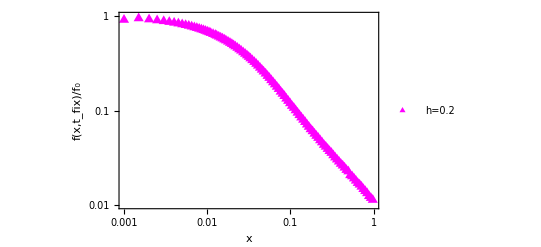

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.2_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.01,1}}, PlotMarkers->{"▲",12}];

(*Show both plots*)
Show[a1sCombined]
```

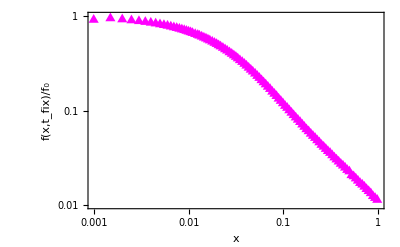
```mathematica
a2=-Graphics-;
```

### h = 0.5

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
```

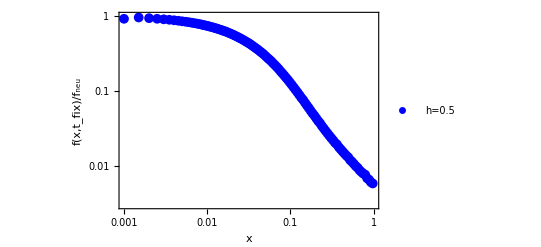

```mathematica
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.5_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"●",10}];

(*Show both plots*)
Show[a1sCombined]
```

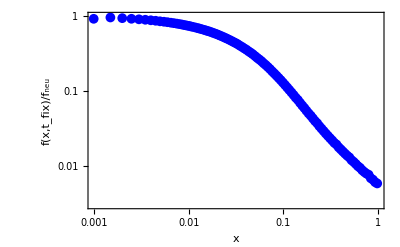
```mathematica
a5=-Graphics-;
```

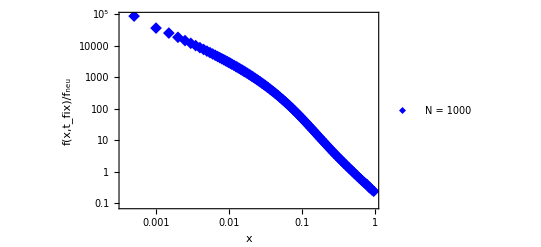

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.5_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s, x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"h=0.5"}, PlotMarkers->{"●",10}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Blue},PlotLegends->{"N = 1000"},PlotRange->All, PlotMarkers->{"◆",12}];

(*Show both plots*)
Show[a1sCombined]
```

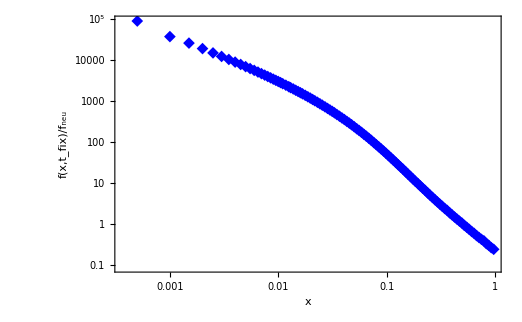
```mathematica
a1=-Graphics-;
```

### N = 500

```mathematica
Supplememtal figure 1
```

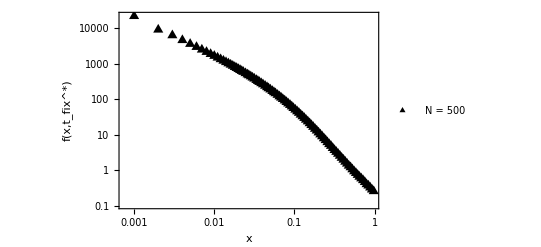

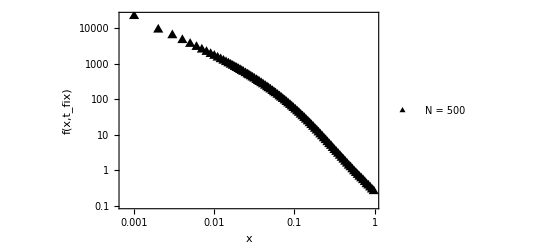

```mathematica
N1=500;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_N_500.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s, x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Black},PlotLegends->{"N = 500"}, PlotMarkers->{"●",10}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,(*FrameLabel->{"x","f(x,t_fix)"},*)FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[")  ",Italic](*,SubscriptBox[Style["f",Italic],"StyleBox[\"neu\",FontSlant->\"Italic\"]"]//DisplayForm,Style["(x)",Italic]*)}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Black},PlotLegends->{"N = 500"},PlotRange->All, PlotMarkers->{"▲",12}];

(*Show both plots*)
Show[a1sCombined]
```

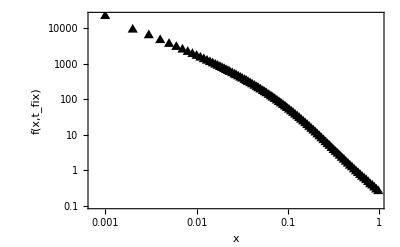
```mathematica
a2=-Graphics-;
```

```mathematica
Show[a2,a1,a3]
```

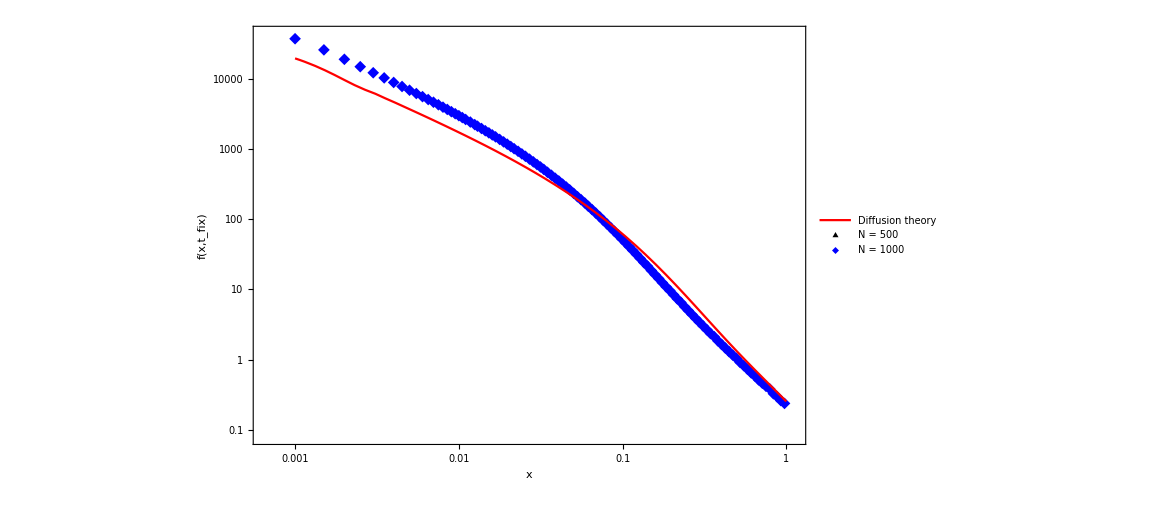
```mathematica
a1=-Graphics-;
```

```mathematica
Show[a1sCombined,a1]
```

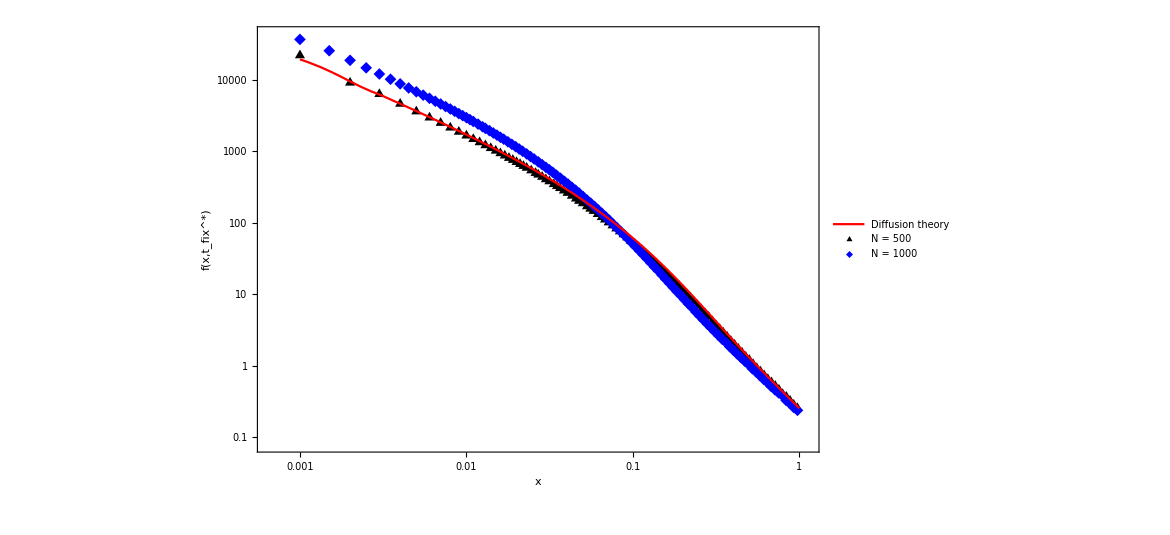

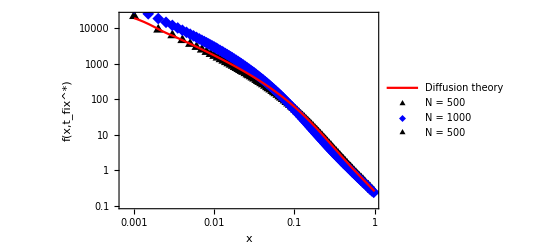

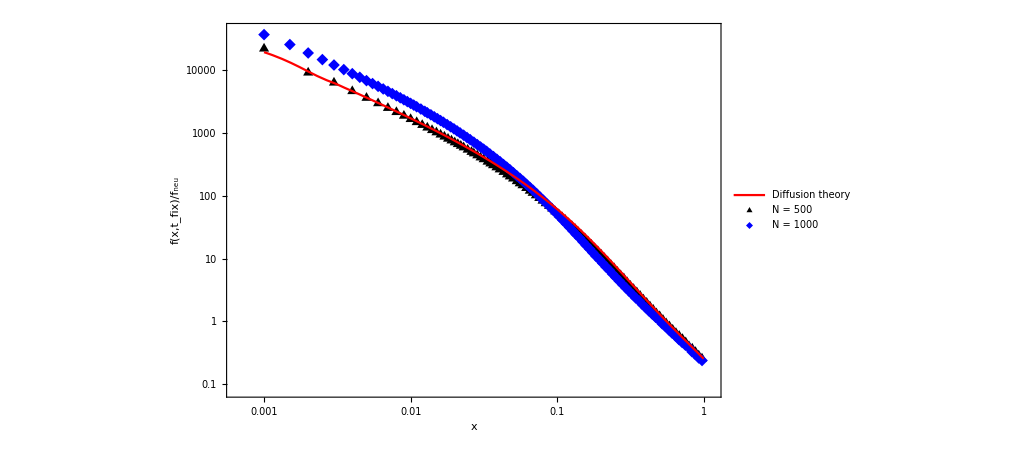

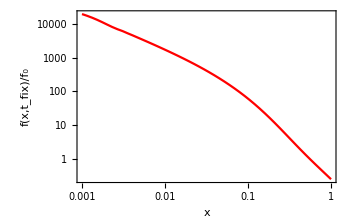
```mathematica
a3=-Graphics-;
```

```mathematica
144.52 +15 +87.54 -10
```

237.06

```mathematica
Show[a1,a2,a3]
```

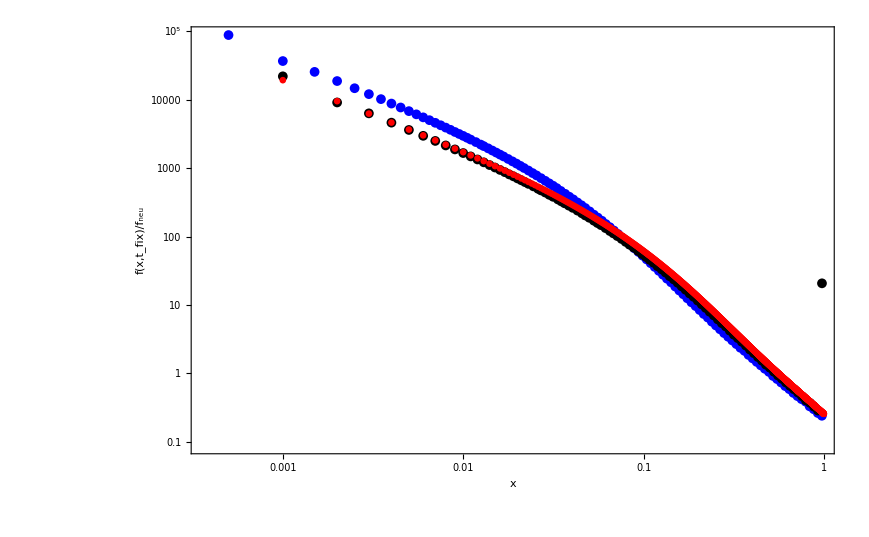

### Ns = 10

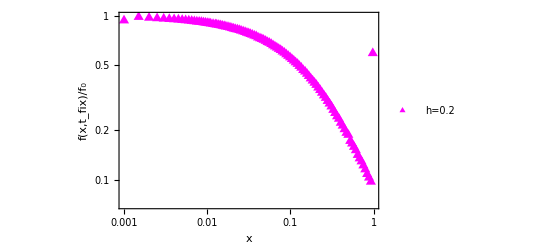

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.2_Ns_10.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.07,1}}, PlotMarkers->{"▲",12}];

(*Show both plots*)
Show[a1sCombined]
```

### h = 0.8 and has final figure

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
```

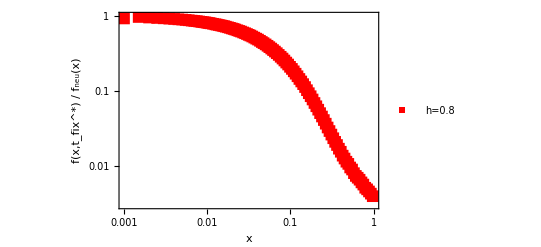

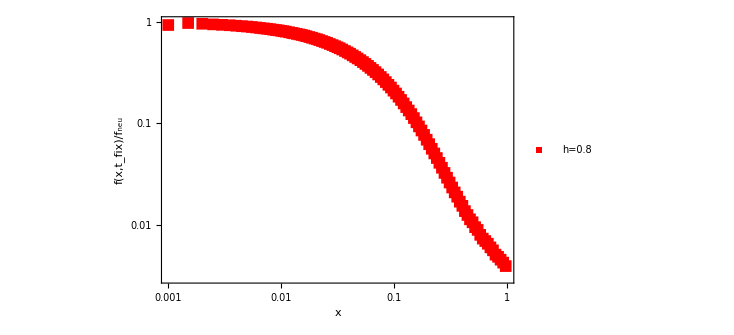

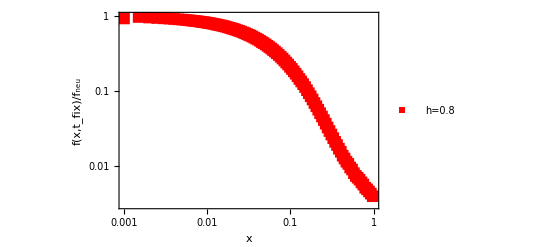

```mathematica
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.8_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];


a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];

(*FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]}]]} *)
(*Show both plots*)
Show[a1sCombined]
```

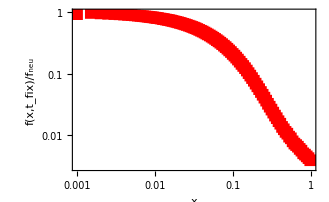
```mathematica
a8=-Graphics-;
```

```mathematica
Show[a8,a5,a2,d2,d5,d8]
```

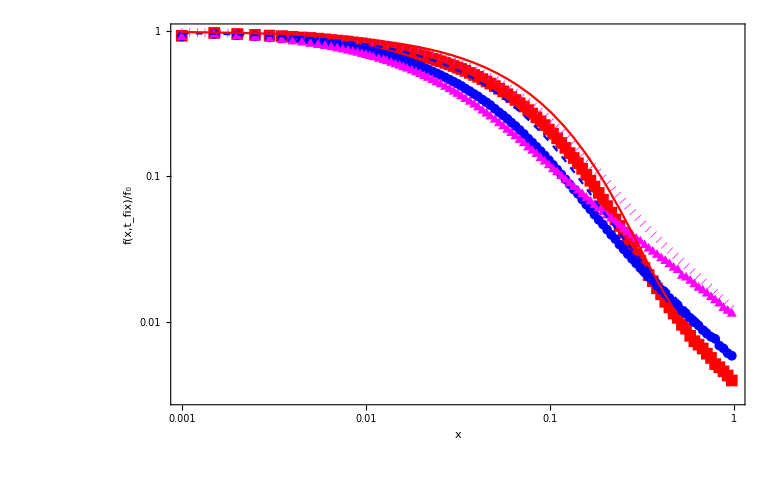

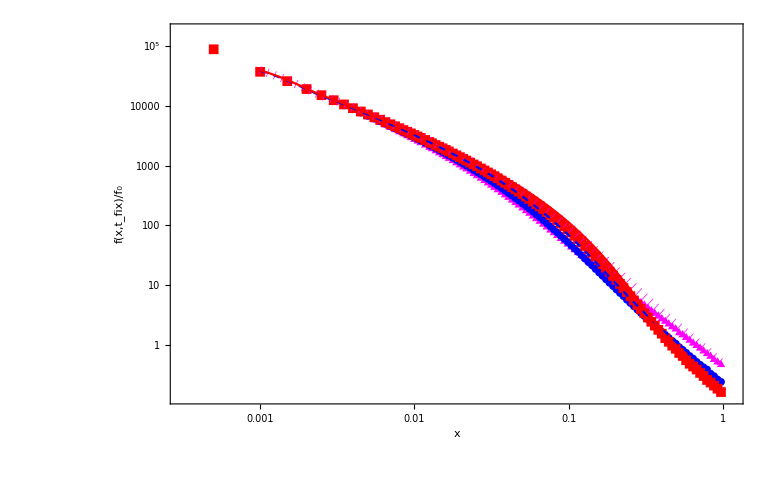

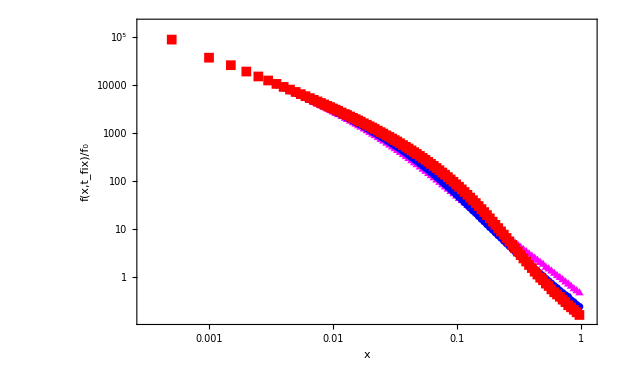
```mathematica
a5=-Graphics-;
```

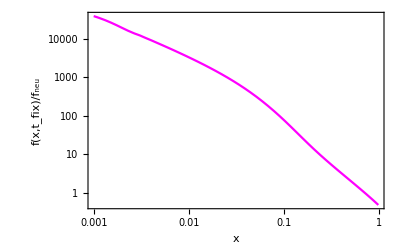
```mathematica
a1=-Graphics-;
```

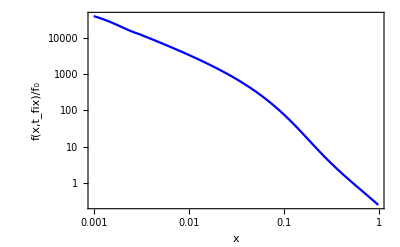
```mathematica
a2=-Graphics-;
```

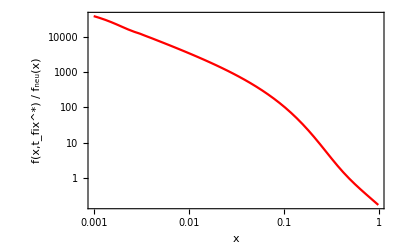
```mathematica
a3=-Graphics-;
```

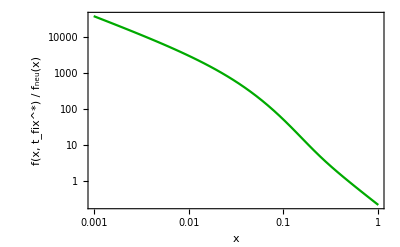
```mathematica
dif=-Graphics-;
```

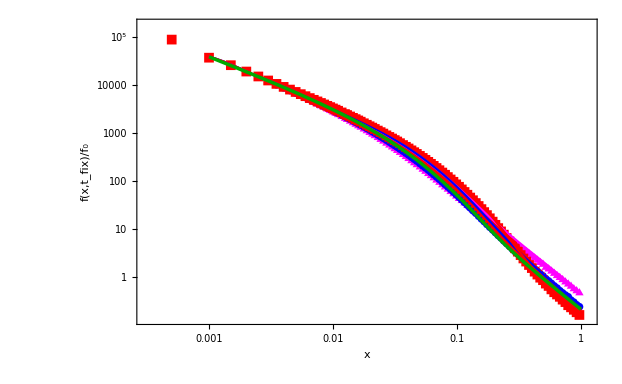

```mathematica
Show[a5,a1,a2,a3,dif]
```

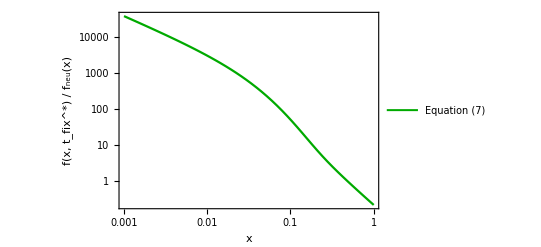

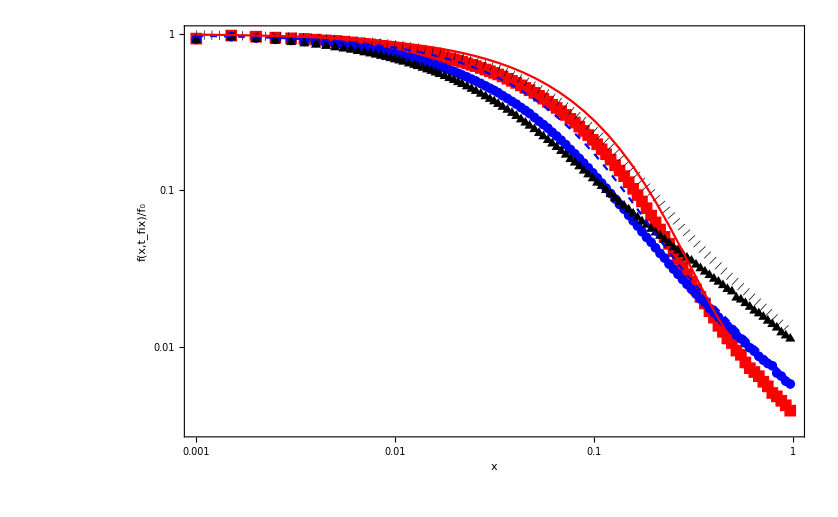

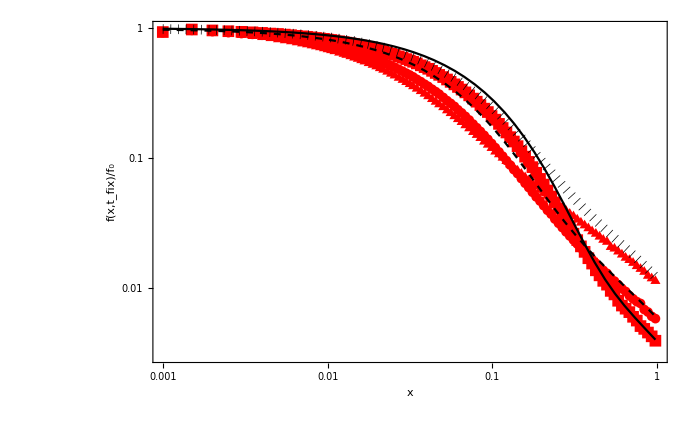

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]== s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1- 2  x2a[t] )),x2a[0]==x0},x2a,{t,0,3000}];


pt=x1[220.18362426267285];
(*pt=x1[1290.3240671352746];*)
p0=1/(2 N1  2 s h);
a= Abs[h pt Log[1-pt]/(1-h)];
w[x_]:=16 N1 s h x pt;

LogLogPlot[((theta pt)/x + theta  pt/x( ⅇ^((-w[x])/(4 a))/(4 a^2)(w[x]  Log[(4 a^2)/w[x]] +w[x] ExpIntegralEi[w[x]/(4 a)] + 4a) + ⅇ^((-w[x])/(4 a)) -1/a-1)), {x,0.001,1}, PlotStyle->{Darker[
Green],Thickness[0.004]},PlotLegends->{"Equation (7)",Large}, Frame->True, (*FrameLabel->{"x","f(x,t_fix)"},*)FrameLabel->{Style["x",Italic],Row[{Style["f(",Italic],Style["x",Italic],Style[", ",Italic],Style[Superscript[Subscript["t","fix"],"*"],Italic],Style[") / ",Italic],Style[Subscript["f","neu"],Italic],Style["(x)",Italic]}]},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16]]
```

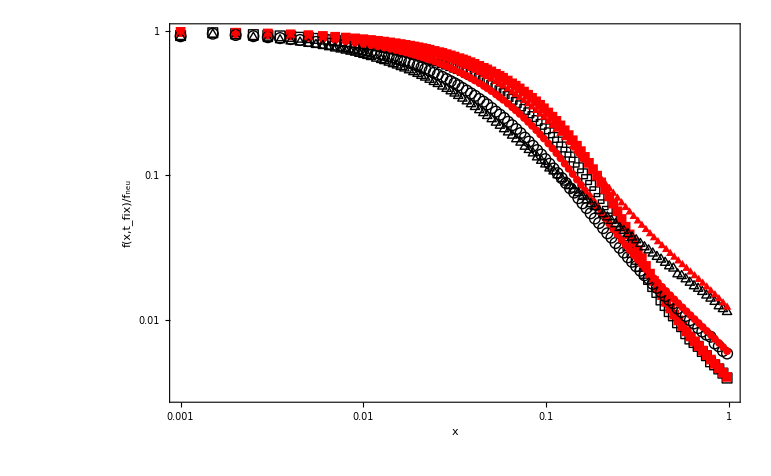

```mathematica
Show[a8,a5,a2,d2,d5,d8]
```

```mathematica
Show[a1sCombined,a1]
```

-Graphics-

```mathematica
a1=-Graphics-;
```

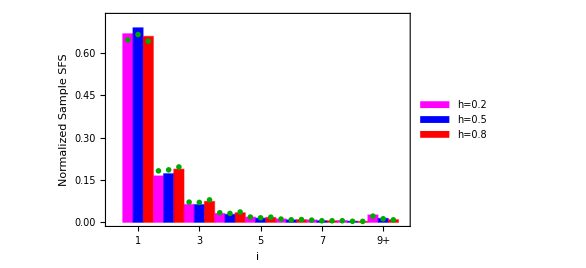

```mathematica
a1=-Graphics-;
```

```mathematica
a1=-Graphics-;
```

```mathematica
Show[a1,d2,d5,d8]
```

-Graphics-

```mathematica
Text[Style["h=0.8 ",FontSize->14,FontSlant->"Italic",Red]]
```

h=0.8

```mathematica
Diffusion
```

```mathematica
take datatfix from histogram_april_2.nb and it is also present below in this file
```

```mathematica
Quit[]
```

```mathematica
h=0.5;
Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
Log[2 2 N1 s  ]/(h  s (1-h))+ ((2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h));
```

3927.02

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 h s N1);
tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];
pt=x1[tfix]
(*pt=0.9967175675397667;*)
xstar=1/(4 N1 s (1-h)) Abs[Log[1-pt]]
```

235.021

0.998434

0.0322967

InterpolatingFunction::dmval: Input value {3927.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

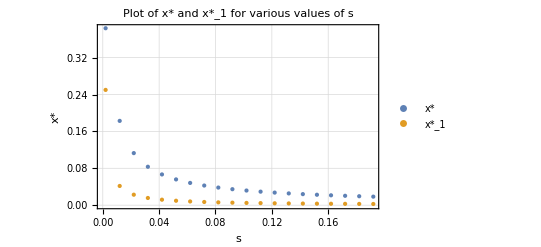

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
h=0.5;
sValues=Range[0.002,0.2,0.01];

(*Function to calculate tfix,xstar,and xstar1 for a given s*)
calculateXstars[s_]:=Module[{x0,tfix,x1,pt,xstar,xstar1},x0=1/(2 2 h s N1);
tfix=Log[2 2 N1 s]/(h s (1-h))+(EulerGamma+(2-3 h) Log[h]+(3 h-1) Log[1-h])/(h s (1-h));
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t]+h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];
pt=x1[tfix];

xstar=1/(4 N1 s (1-h)) Abs[Log[1-pt]];
xstar1=1/(4 N1 s (1-h));
Return[{xstar,xstar1}];];

(*Calculate xstar and xstar1 for each value of s*)
values=Table[{s,calculateXstars[s][[1]],calculateXstars[s][[2]]},{s,sValues}];

(*Extract xstar and xstar1 values for plotting*)
xstarData=values[[All,{1,2}]];
xstar1Data=values[[All,{1,3}]];

(*Plot the results*)
ListPlot[{xstarData,xstar1Data},PlotStyle->{PointSize[Medium],PointSize[Medium]},AxesLabel->{"s","x*"},PlotLabel->"Plot of x* and x*_1 for various values of s",GridLines->Automatic,Frame->True,FrameLabel->{"s","x*"},PlotLegends->{"x*","x*_1"},PlotRange->All]
```

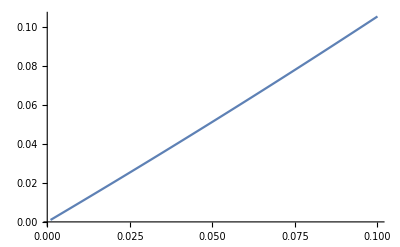

```mathematica
Plot[Abs[Log[1-pt]],{pt,0.001,0.1}]
```

```mathematica
Quit[]
```

0.005 Abs[Log[1-pt]]

```mathematica
Log[2 N1 2s h]/(s h)
```

219.101

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]== s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1- 2  x2a[t] )),x2a[0]==x0},x2a,{t,0,3000}];


pt=x1[220.18362426267285];
(*pt=x1[1290.3240671352746];*)
p0=1/(2 N1  2 s h);
a= 1/(4 N1 s (1-h)) Abs[Log[1-pt]]
```

0.0285959

```mathematica
x1[220.18362426267285]
```

0.996718

## Diffusion

```mathematica
h=0.2
```

### h=0.2

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.2;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1500},{x,0,1}];
gData=Table[Sum[Datatfix[[k,2]] G[x,Datatfix[[k,1]]]/(x*(1-x)),{k,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];


averageGData={};
AppendTo[averageGData,gData];
```

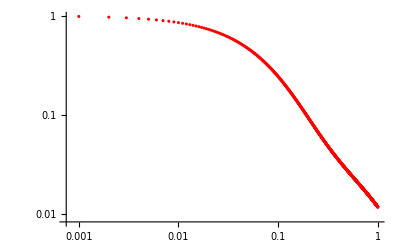

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

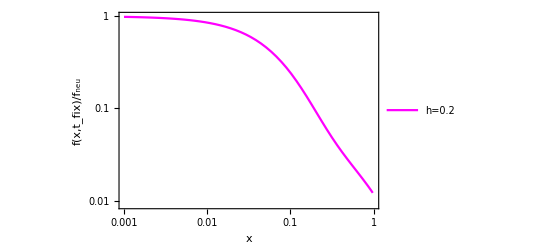

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}, PlotMarkers->{"▲",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

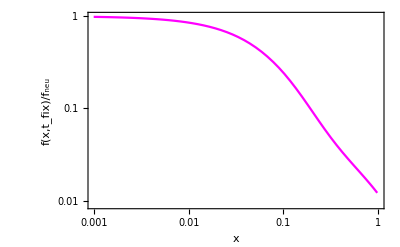
```mathematica
d2=-Graphics-;
```

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.2;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1500},{x,0,1}];
gData=Table[Sum[Datatfix[[k,2]] G[x,Datatfix[[k,1]]]/(x*(1-x)),{k,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];


averageGData={};
AppendTo[averageGData,gData];
```

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}, PlotMarkers->{"▲",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

### Below is for mean tfix

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.2;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];

tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1500},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];


averageGData={};
AppendTo[averageGData,gData];
xaxish2=Table[x,{x,0.001,0.999,0.001}];

Datah2=Transpose@{xaxish2,xaxish2 gData/theta};
```

275.295

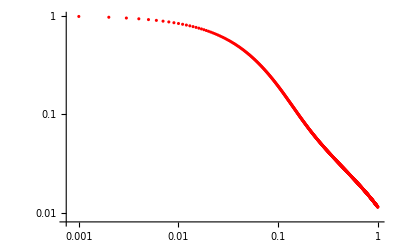

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

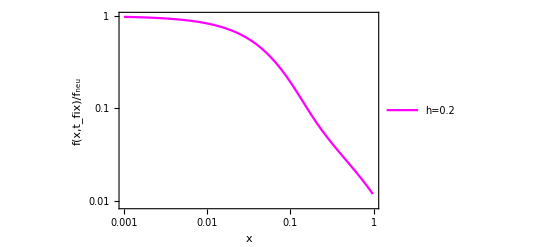

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}, PlotMarkers->{"▲",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

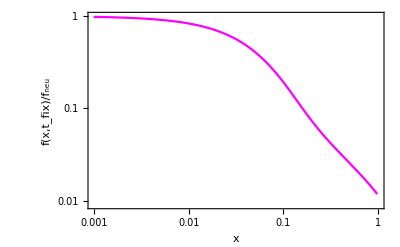
```mathematica
d2=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

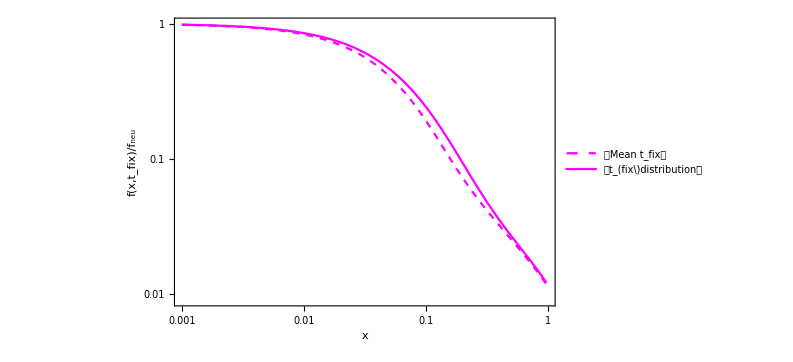

```mathematica
N1=1000;
mu=10^-7;
L=100000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.2;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1500}];

tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1500},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];


averageGData={};
AppendTo[averageGData,gData];
xaxish2=Table[x,{x,0.001,0.999,0.001}];

Datah2=Transpose@{xaxish2,xaxish2 gData/theta};
```

275.295

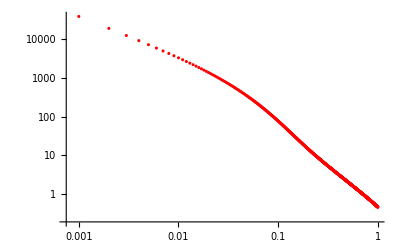

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis, gData};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

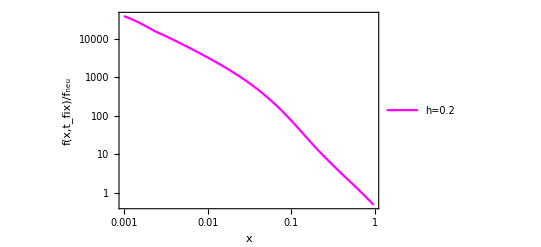

```mathematica
Data1s=Transpose@{xaxis, gData};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.009,1}}, PlotMarkers->{"▲",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->All];

(*Show both plots*)
Show[a1sInterpolated]
```

### h = 0.5

```mathematica
Quit[]
```

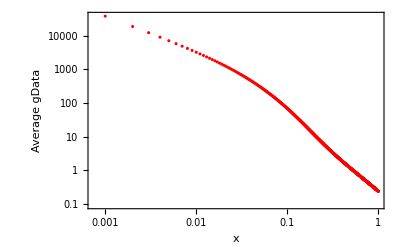

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

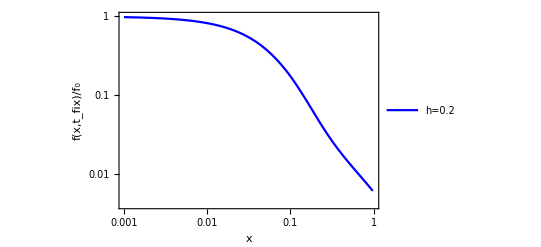

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"●",8}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}];
(*Show both plots*)
Show[a1sInterpolated]
```

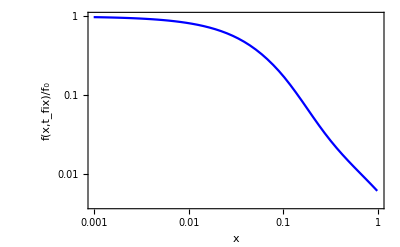
```mathematica
d5=-Graphics-;
```

```mathematica
Quit[]
```

235.021

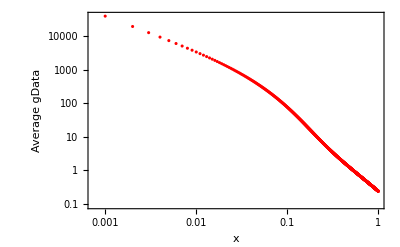

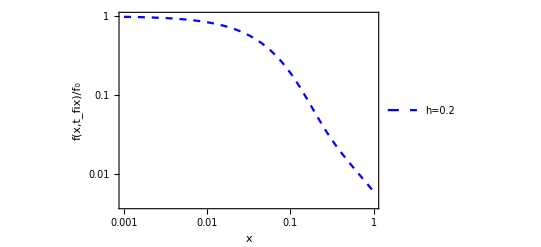

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];
tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
	Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"●",8}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue, Dashed},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}];
(*Show both plots*)
Show[a1sInterpolated]
```

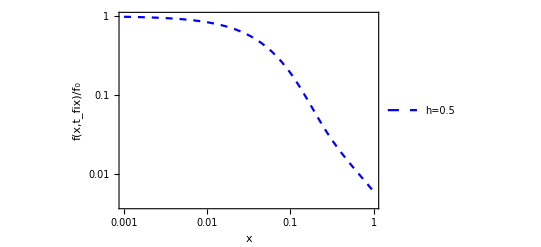

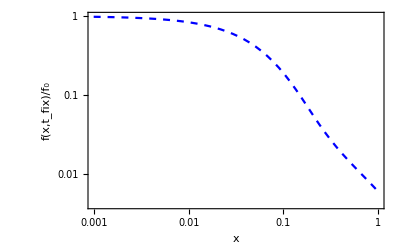
```mathematica
a1=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

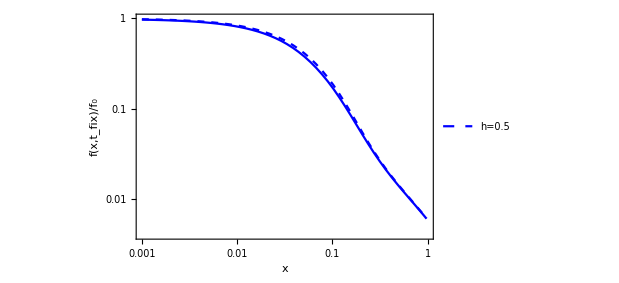

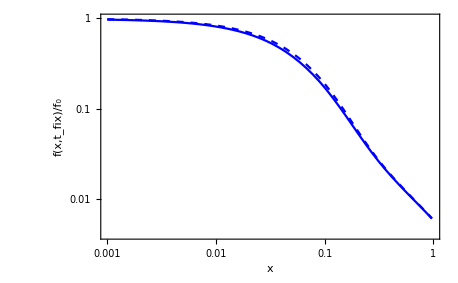
```mathematica
a1=-Graphics-;
```

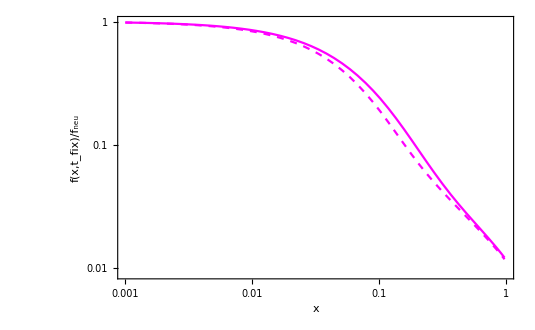
```mathematica
a2=-Graphics-;
```

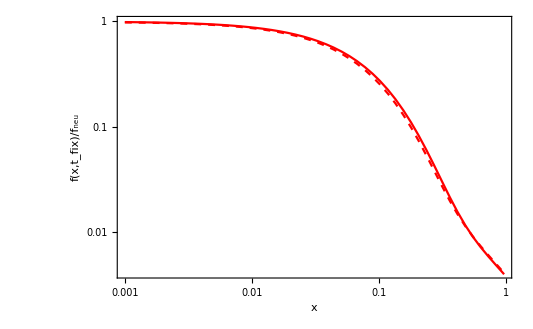
```mathematica
a3=-Graphics-;
```

```mathematica
Show[a3,a1,a2]
```

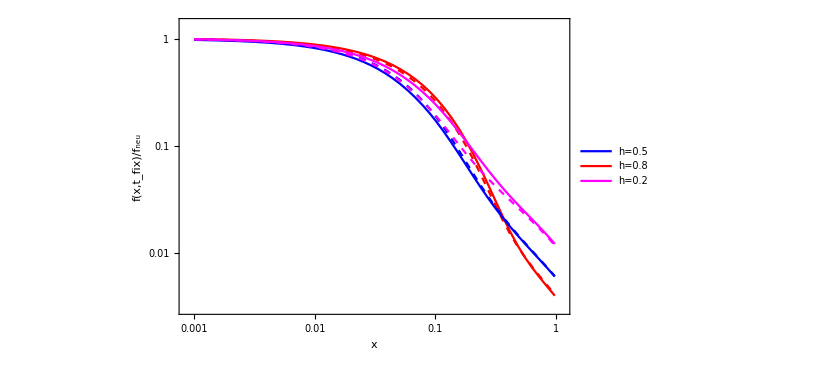

```mathematica
Show[a1sInterpolated,h8dist,a2,a1]
```

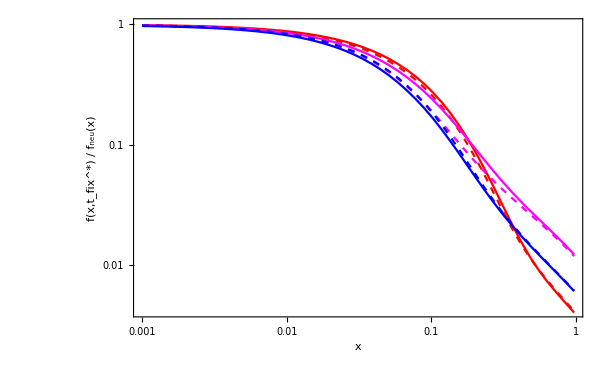

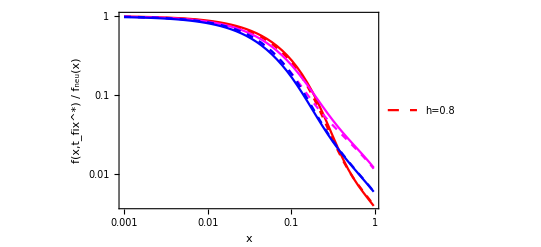

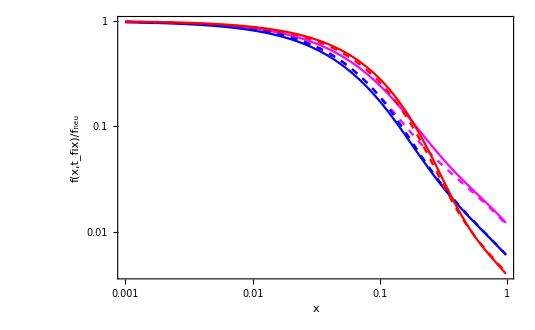

235.021

-Graphics-

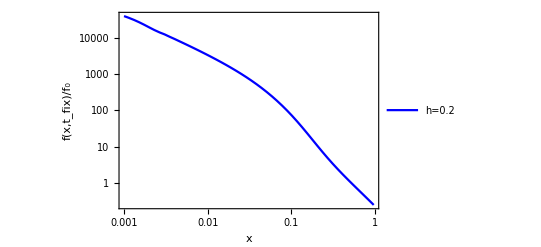

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];
tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
	Data1s=Transpose@{xaxis, gData};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"●",8}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"h=0.2"},PlotRange->All];
(*Show both plots*)
Show[a1sInterpolated]
```

### N = 500

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

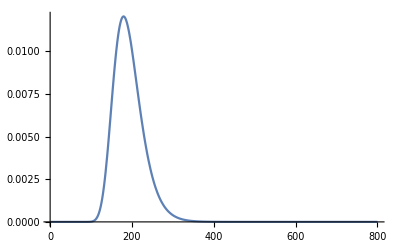

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
N1=500;
s0=0.1;
h=0.5;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=taui[t]=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;

B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];

a3=Plot[pdfgenh[t],{t,1,800},PlotRange->All,PlotPoints->50]




timePoints=Range[1,800,1];

weightValues=pdfgenh/@timePoints;

Datatfix=Transpose[{timePoints,weightValues}];
```

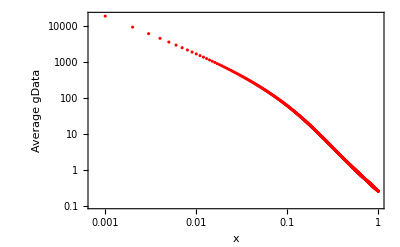

```mathematica
N1=500;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=500;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

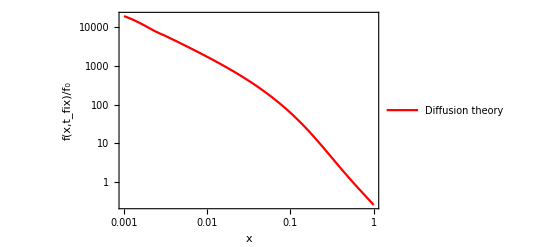

```mathematica
Data1s=Transpose[{xaxis,averageGData1}];
interpolation=Interpolation[Data1s];
(*Plot the original and combined data*)

a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[Data1s[[All,1]]],Max[Data1s[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Red},PlotLegends->{"Diffusion theory"},PlotRange->All];
(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
Datatfix
```

{{1,1.88992×10^-261},{2,4.3403×10^-182},{3,1.44798×10^-146},{4,3.58917×10^-125},{5,2.01199×10^-110},{6,1.99255×10^-99},{7,8.49062×10^-91},{8,8.94235×10^-84},{9,6.64395×10^-78},{10,6.82373×10^-73},{11,1.52576×10^-68},{12,1.02212×10^-64},{13,2.58722×10^-61},{14,2.94261×10^-58},{15,1.71668×10^-55},{16,5.69513×10^-53},{17,1.16597×10^-50},{18,1.57326×10^-48},{19,1.47613×10^-46},{20,1.00659×10^-44},{21,5.17576×10^-43},{22,2.06985×10^-41},{23,6.60915×10^-40},{24,1.72323×10^-38},{25,3.7404×10^-37},{26,6.8728×10^-36},{27,1.08472×10^-34},{28,1.48943×10^-33},{29,1.79936×10^-32},{30,1.93168×10^-31},{31,1.85913×10^-30},{32,1.61684×10^-29},{33,1.27961×10^-28},{34,9.27464×10^-28},{35,6.19179×10^-27},{36,3.82726×10^-26},{37,2.20068×10^-25},{38,1.18219×10^-24},{39,5.95627×10^-24},{40,2.82475×10^-23},{41,1.26512×10^-22},{42,5.36713×10^-22},{43,2.16284×10^-21},{44,8.30035×10^-21},{45,3.04086×10^-20},{46,1.06583×10^-19},{47,3.58149×10^-19},{48,1.156×10^-18},{49,3.59043×10^-18},{50,1.07488×10^-17},{51,3.1065×10^-17},{52,8.68012×10^-17},{53,2.34811×10^-16},{54,6.15766×10^-16},{55,1.56728×10^-15},{56,3.87623×10^-15},{57,9.3257×10^-15},{58,2.18477×10^-14},{59,4.98895×10^-14},{60,1.11145×10^-13},{61,2.41786×10^-13},{62,5.14037×10^-13},{63,1.06886×10^-12},{64,2.17541×10^-12},{65,4.33678×10^-12},{66,8.47413×10^-12},{67,1.62409×10^-11},{68,3.05481×10^-11},{69,5.64258×10^-11},{70,1.02409×10^-10},{71,1.82728×10^-10},{72,3.20705×10^-10},{73,5.53937×10^-10},{74,9.42062×10^-10},{75,1.57821×10^-9},{76,2.60562×10^-9},{77,4.24137×10^-9},{78,6.80971×10^-9},{79,1.07883×10^-8},{80,1.68712×10^-8},{81,2.60536×10^-8},{82,3.97444×10^-8},{83,5.99128×10^-8},{84,8.92777×10^-8},{85,1.31549×10^-7},{86,1.91728×10^-7},{87,2.76486×10^-7},{88,3.94613×10^-7},{89,5.57579×10^-7},{90,7.80181×10^-7},{91,1.08132×10^-6},{92,1.48488×10^-6},{93,2.02076×10^-6},{94,2.72604×10^-6},{95,3.64622×10^-6},{96,4.83666×10^-6},{97,6.36407×10^-6},{98,8.30813×10^-6},{99,0.0000107632},{100,0.0000138399},{101,0.0000176672},{102,0.0000223937},{103,0.0000281893},{104,0.0000352472},{105,0.0000437844},{106,0.0000540434},{107,0.0000662927},{108,0.0000808273},{109,0.0000979686},{110,0.000118064},{111,0.000141486},{112,0.00016863},{113,0.000199915},{114,0.000235777},{115,0.000276669},{116,0.000323056},{117,0.000375412},{118,0.000434214},{119,0.000499937},{120,0.000573051},{121,0.000654013},{122,0.000743261},{123,0.00084121},{124,0.000948244},{125,0.00106471},{126,0.00119092},{127,0.00132714},{128,0.00147356},{129,0.00163035},{130,0.0017976},{131,0.00197533},{132,0.00216351},{133,0.00236203},{134,0.00257072},{135,0.00278932},{136,0.00301753},{137,0.00325495},{138,0.00350113},{139,0.00375556},{140,0.00401765},{141,0.00428677},{142,0.00456223},{143,0.00484327},{144,0.00512912},{145,0.00541895},{146,0.00571191},{147,0.00600712},{148,0.00630367},{149,0.00660065},{150,0.00689714},{151,0.00719221},{152,0.00748494},{153,0.00777444},{154,0.0080598},{155,0.00834016},{156,0.00861469},{157,0.00888256},{158,0.00914301},{159,0.00939531},{160,0.00963877},{161,0.00987274},{162,0.0100966},{163,0.0103099},{164,0.010512},{165,0.0107026},{166,0.0108813},{167,0.0110477},{168,0.0112015},{169,0.0113426},{170,0.0114707},{171,0.0115858},{172,0.0116877},{173,0.0117765},{174,0.0118522},{175,0.0119149},{176,0.0119646},{177,0.0120015},{178,0.0120259},{179,0.0120379},{180,0.0120378},{181,0.0120259},{182,0.0120025},{183,0.011968},{184,0.0119227},{185,0.0118669},{186,0.0118012},{187,0.0117258},{188,0.0116413},{189,0.011548},{190,0.0114465},{191,0.011337},{192,0.0112202},{193,0.0110964},{194,0.0109661},{195,0.0108297},{196,0.0106876},{197,0.0105404},{198,0.0103884},{199,0.0102321},{200,0.0100718},{201,0.00990801},{202,0.00974108},{203,0.00957139},{204,0.00939932},{205,0.00922523},{206,0.00904945},{207,0.00887232},{208,0.00869416},{209,0.00851527},{210,0.00833594},{211,0.00815645},{212,0.00797705},{213,0.007798},{214,0.00761954},{215,0.00744188},{216,0.00726524},{217,0.0070898},{218,0.00691575},{219,0.00674326},{220,0.00657249},{221,0.00640357},{222,0.00623666},{223,0.00607186},{224,0.00590928},{225,0.00574904},{226,0.00559122},{227,0.00543591},{228,0.00528316},{229,0.00513306},{230,0.00498565},{231,0.00484098},{232,0.0046991},{233,0.00456002},{234,0.00442379},{235,0.00429041},{236,0.0041599},{237,0.00403227},{238,0.00390752},{239,0.00378565},{240,0.00366665},{241,0.00355051},{242,0.00343721},{243,0.00332673},{244,0.00321905},{245,0.00311415},{246,0.00301199},{247,0.00291254},{248,0.00281577},{249,0.00272165},{250,0.00263013},{251,0.00254117},{252,0.00245474},{253,0.00237078},{254,0.00228927},{255,0.00221014},{256,0.00213336},{257,0.00205888},{258,0.00198665},{259,0.00191662},{260,0.00184876},{261,0.001783},{262,0.0017193},{263,0.00165761},{264,0.00159789},{265,0.00154008},{266,0.00148414},{267,0.00143002},{268,0.00137768},{269,0.00132706},{270,0.00127813},{271,0.00123083},{272,0.00118513},{273,0.00114097},{274,0.00109832},{275,0.00105712},{276,0.00101735},{277,0.000978947},{278,0.000941885},{279,0.000906119},{280,0.000871611},{281,0.000838321},{282,0.000806213},{283,0.00077525},{284,0.000745395},{285,0.000716614},{286,0.000688873},{287,0.000662138},{288,0.000636377},{289,0.000611557},{290,0.000587649},{291,0.000564621},{292,0.000542445},{293,0.000521091},{294,0.000500533},{295,0.000480743},{296,0.000461695},{297,0.000443363},{298,0.000425723},{299,0.000408751},{300,0.000392423},{301,0.000376717},{302,0.000361611},{303,0.000347083},{304,0.000333113},{305,0.000319681},{306,0.000306768},{307,0.000294355},{308,0.000282424},{309,0.000270957},{310,0.000259937},{311,0.000249348},{312,0.000239175},{313,0.000229401},{314,0.000220012},{315,0.000210993},{316,0.000202331},{317,0.000194013},{318,0.000186025},{319,0.000178355},{320,0.000170991},{321,0.000163921},{322,0.000157134},{323,0.000150619},{324,0.000144367},{325,0.000138366},{326,0.000132607},{327,0.000127081},{328,0.000121779},{329,0.000116691},{330,0.000111811},{331,0.000107129},{332,0.000102637},{333,0.0000983295},{334,0.0000941977},{335,0.0000902352},{336,0.0000864351},{337,0.0000827911},{338,0.000079297},{339,0.0000759469},{340,0.0000727349},{341,0.0000696556},{342,0.0000667038},{343,0.0000638741},{344,0.0000611619},{345,0.0000585623},{346,0.0000560708},{347,0.0000536831},{348,0.0000513949},{349,0.0000492023},{350,0.0000471012},{351,0.0000450881},{352,0.0000431594},{353,0.0000413115},{354,0.0000395413},{355,0.0000378454},{356,0.0000362209},{357,0.0000346649},{358,0.0000331745},{359,0.000031747},{360,0.0000303799},{361,0.0000290706},{362,0.0000278168},{363,0.0000266161},{364,0.0000254664},{365,0.0000243655},{366,0.0000233114},{367,0.0000223022},{368,0.000021336},{369,0.000020411},{370,0.0000195254},{371,0.0000186777},{372,0.0000178663},{373,0.0000170895},{374,0.0000163461},{375,0.0000156345},{376,0.0000149534},{377,0.0000143016},{378,0.0000136778},{379,0.0000130808},{380,0.0000125095},{381,0.0000119629},{382,0.0000114398},{383,0.0000109392},{384,0.0000104603},{385,0.0000100021},{386,9.5637×10^-6},{387,9.14426×10^-6},{388,8.74299×10^-6},{389,8.35911×10^-6},{390,7.99188×10^-6},{391,7.64059×10^-6},{392,7.30455×10^-6},{393,6.98312×10^-6},{394,6.67567×10^-6},{395,6.38159×10^-6},{396,6.10033×10^-6},{397,5.83131×10^-6},{398,5.57403×10^-6},{399,5.32798×10^-6},{400,5.09266×10^-6},{401,4.86763×10^-6},{402,4.65243×10^-6},{403,4.44665×10^-6},{404,4.24987×10^-6},{405,4.06171×10^-6},{406,3.88179×10^-6},{407,3.70977×10^-6},{408,3.54529×10^-6},{409,3.38802×10^-6},{410,3.23767×10^-6},{411,3.09392×10^-6},{412,2.9565×10^-6},{413,2.82512×10^-6},{414,2.69952×10^-6},{415,2.57945×10^-6},{416,2.46467×10^-6},{417,2.35496×10^-6},{418,2.25008×10^-6},{419,2.14983×10^-6},{420,2.05401×10^-6},{421,1.96242×10^-6},{422,1.87488×10^-6},{423,1.79121×10^-6},{424,1.71124×10^-6},{425,1.63481×10^-6},{426,1.56177×10^-6},{427,1.49196×10^-6},{428,1.42525×10^-6},{429,1.36149×10^-6},{430,1.30057×10^-6},{431,1.24235×10^-6},{432,1.18671×10^-6},{433,1.13355×10^-6},{434,1.08275×10^-6},{435,1.0342×10^-6},{436,9.87821×10^-7},{437,9.43502×10^-7},{438,9.01157×10^-7},{439,8.60698×10^-7},{440,8.22042×10^-7},{441,7.85109×10^-7},{442,7.49824×10^-7},{443,7.16113×10^-7},{444,6.83906×10^-7},{445,6.53138×10^-7},{446,6.23744×10^-7},{447,5.95664×10^-7},{448,5.68839×10^-7},{449,5.43214×10^-7},{450,5.18735×10^-7},{451,4.95352×10^-7},{452,4.73016×10^-7},{453,4.5168×10^-7},{454,4.313×10^-7},{455,4.11834×10^-7},{456,3.93241×10^-7},{457,3.75482×10^-7},{458,3.58519×10^-7},{459,3.42319×10^-7},{460,3.26845×10^-7},{461,3.12067×10^-7},{462,2.97952×10^-7},{463,2.84473×10^-7},{464,2.71599×10^-7},{465,2.59304×10^-7},{466,2.47563×10^-7},{467,2.3635×10^-7},{468,2.25642×10^-7},{469,2.15416×10^-7},{470,2.05651×10^-7},{471,1.96326×10^-7},{472,1.87422×10^-7},{473,1.78919×10^-7},{474,1.708×10^-7},{475,1.63047×10^-7},{476,1.55644×10^-7},{477,1.48575×10^-7},{478,1.41826×10^-7},{479,1.35381×10^-7},{480,1.29228×10^-7},{481,1.23353×10^-7},{482,1.17744×10^-7},{483,1.12388×10^-7},{484,1.07275×10^-7},{485,1.02393×10^-7},{486,9.77321×10^-8},{487,9.32823×10^-8},{488,8.90341×10^-8},{489,8.49785×10^-8},{490,8.11066×10^-8},{491,7.74103×10^-8},{492,7.38816×10^-8},{493,7.05129×10^-8},{494,6.72972×10^-8},{495,6.42273×10^-8},{496,6.12969×10^-8},{497,5.84995×10^-8},{498,5.58291×10^-8},{499,5.32801×10^-8},{500,5.0847×10^-8},{501,4.85244×10^-8},{502,4.63074×10^-8},{503,4.41913×10^-8},{504,4.21714×10^-8},{505,4.02435×10^-8},{506,3.84032×10^-8},{507,3.66468×10^-8},{508,3.49703×10^-8},{509,3.33702×10^-8},{510,3.1843×10^-8},{511,3.03854×10^-8},{512,2.89942×10^-8},{513,2.76665×10^-8},{514,2.63993×10^-8},{515,2.51899×10^-8},{516,2.40356×10^-8},{517,2.29341×10^-8},{518,2.18828×10^-8},{519,2.08795×10^-8},{520,1.9922×10^-8},{521,1.90082×10^-8},{522,1.81362×10^-8},{523,1.73041×10^-8},{524,1.65099×10^-8},{525,1.57521×10^-8},{526,1.50289×10^-8},{527,1.43388×10^-8},{528,1.36803×10^-8},{529,1.30519×10^-8},{530,1.24522×10^-8},{531,1.188×10^-8},{532,1.1334×10^-8},{533,1.0813×10^-8},{534,1.03158×10^-8},{535,9.84144×10^-9},{536,9.3888×10^-9},{537,8.9569×10^-9},{538,8.5448×10^-9},{539,8.15158×10^-9},{540,7.7764×10^-9},{541,7.41843×10^-9},{542,7.07687×10^-9},{543,6.75099×10^-9},{544,6.44006×10^-9},{545,6.1434×10^-9},{546,5.86036×10^-9},{547,5.59031×10^-9},{548,5.33267×10^-9},{549,5.08686×10^-9},{550,4.85234×10^-9},{551,4.6286×10^-9},{552,4.41514×10^-9},{553,4.21149×10^-9},{554,4.0172×10^-9},{555,3.83185×10^-9},{556,3.65502×10^-9},{557,3.48633×10^-9},{558,3.3254×10^-9},{559,3.17187×10^-9},{560,3.02541×10^-9},{561,2.88569×10^-9},{562,2.7524×10^-9},{563,2.62525×10^-9},{564,2.50395×10^-9},{565,2.38824×10^-9},{566,2.27786×10^-9},{567,2.17257×10^-9},{568,2.07213×10^-9},{569,1.97632×10^-9},{570,1.88493×10^-9},{571,1.79775×10^-9},{572,1.71459×10^-9},{573,1.63526×10^-9},{574,1.5596×10^-9},{575,1.48742×10^-9},{576,1.41858×10^-9},{577,1.35291×10^-9},{578,1.29028×10^-9},{579,1.23053×10^-9},{580,1.17355×10^-9},{581,1.11919×10^-9},{582,1.06735×10^-9},{583,1.0179×10^-9},{584,9.70737×10^-10},{585,9.25752×10^-10},{586,8.82846×10^-10},{587,8.41923×10^-10},{588,8.02892×10^-10},{589,7.65665×10^-10},{590,7.3016×10^-10},{591,6.96297×10^-10},{592,6.64×10^-10},{593,6.33197×10^-10},{594,6.03819×10^-10},{595,5.75801×10^-10},{596,5.4908×10^-10},{597,5.23595×10^-10},{598,4.9929×10^-10},{599,4.76111×10^-10},{600,4.54004×10^-10},{601,4.32922×10^-10},{602,4.12816×10^-10},{603,3.93642×10^-10},{604,3.75356×10^-10},{605,3.57917×10^-10},{606,3.41286×10^-10},{607,3.25427×10^-10},{608,3.10302×10^-10},{609,2.95879×10^-10},{610,2.82124×10^-10},{611,2.69008×10^-10},{612,2.56499×10^-10},{613,2.44571×10^-10},{614,2.33197×10^-10},{615,2.2235×10^-10},{616,2.12006×10^-10},{617,2.02143×10^-10},{618,1.92737×10^-10},{619,1.83768×10^-10},{620,1.75215×10^-10},{621,1.6706×10^-10},{622,1.59283×10^-10},{623,1.51867×10^-10},{624,1.44796×10^-10},{625,1.38054×10^-10},{626,1.31624×10^-10},{627,1.25494×10^-10},{628,1.19648×10^-10},{629,1.14074×10^-10},{630,1.08759×10^-10},{631,1.03691×10^-10},{632,9.88591×10^-11},{633,9.42517×10^-11},{634,8.98585×10^-11},{635,8.56696×10^-11},{636,8.16756×10^-11},{637,7.78674×10^-11},{638,7.42364×10^-11},{639,7.07743×10^-11},{640,6.74734×10^-11},{641,6.43261×10^-11},{642,6.13253×10^-11},{643,5.84642×10^-11},{644,5.57363×10^-11},{645,5.31354×10^-11},{646,5.06556×10^-11},{647,4.82914×10^-11},{648,4.60372×10^-11},{649,4.38881×10^-11},{650,4.18391×10^-11},{651,3.98856×10^-11},{652,3.80231×10^-11},{653,3.62474×10^-11},{654,3.45544×10^-11},{655,3.29404×10^-11},{656,3.14016×10^-11},{657,2.99346×10^-11},{658,2.8536×10^-11},{659,2.72025×10^-11},{660,2.59313×10^-11},{661,2.47194×10^-11},{662,2.3564×10^-11},{663,2.24625×10^-11},{664,2.14124×10^-11},{665,2.04113×10^-11},{666,1.94569×10^-11},{667,1.85471×10^-11},{668,1.76797×10^-11},{669,1.68528×10^-11},{670,1.60645×10^-11},{671,1.53131×10^-11},{672,1.45967×10^-11},{673,1.39137×10^-11},{674,1.32627×10^-11},{675,1.26421×10^-11},{676,1.20504×10^-11},{677,1.14864×10^-11},{678,1.09488×10^-11},{679,1.04363×10^-11},{680,9.94767×10^-12},{681,9.48193×10^-12},{682,9.03795×10^-12},{683,8.61473×10^-12},{684,8.21129×10^-12},{685,7.82671×10^-12},{686,7.46011×10^-12},{687,7.11065×10^-12},{688,6.77754×10^-12},{689,6.46001×10^-12},{690,6.15732×10^-12},{691,5.8688×10^-12},{692,5.59377×10^-12},{693,5.33161×10^-12},{694,5.08172×10^-12},{695,4.84352×10^-12},{696,4.61647×10^-12},{697,4.40004×10^-12},{698,4.19374×10^-12},{699,3.9971×10^-12},{700,3.80967×10^-12},{701,3.63101×10^-12},{702,3.46071×10^-12},{703,3.29839×10^-12},{704,3.14367×10^-12},{705,2.9962×10^-12},{706,2.85563×10^-12},{707,2.72165×10^-12},{708,2.59395×10^-12},{709,2.47223×10^-12},{710,2.35621×10^-12},{711,2.24562×10^-12},{712,2.14022×10^-12},{713,2.03976×10^-12},{714,1.94401×10^-12},{715,1.85274×10^-12},{716,1.76576×10^-12},{717,1.68285×10^-12},{718,1.60383×10^-12},{719,1.52851×10^-12},{720,1.45672×10^-12},{721,1.38831×10^-12},{722,1.3231×10^-12},{723,1.26094×10^-12},{724,1.20171×10^-12},{725,1.14525×10^-12},{726,1.09144×10^-12},{727,1.04016×10^-12},{728,9.9128×10^-13},{729,9.44695×10^-13},{730,9.00297×10^-13},{731,8.57982×10^-13},{732,8.17653×10^-13},{733,7.79217×10^-13},{734,7.42585×10^-13},{735,7.07674×10^-13},{736,6.74401×10^-13},{737,6.4269×10^-13},{738,6.12468×10^-13},{739,5.83666×10^-13},{740,5.56216×10^-13},{741,5.30055×10^-13},{742,5.05123×10^-13},{743,4.81362×10^-13},{744,4.58718×10^-13},{745,4.37137×10^-13},{746,4.1657×10^-13},{747,3.9697×10^-13},{748,3.7829×10^-13},{749,3.60488×10^-13},{750,3.43523×10^-13},{751,3.27356×10^-13},{752,3.11948×10^-13},{753,2.97264×10^-13},{754,2.83271×10^-13},{755,2.69935×10^-13},{756,2.57227×10^-13},{757,2.45116×10^-13},{758,2.33575×10^-13},{759,2.22576×10^-13},{760,2.12095×10^-13},{761,2.02106×10^-13},{762,1.92587×10^-13},{763,1.83516×10^-13},{764,1.74872×10^-13},{765,1.66635×10^-13},{766,1.58785×10^-13},{767,1.51304×10^-13},{768,1.44175×10^-13},{769,1.37382×10^-13},{770,1.30908×10^-13},{771,1.2474×10^-13},{772,1.18861×10^-13},{773,1.13259×10^-13},{774,1.07921×10^-13},{775,1.02834×10^-13},{776,9.79869×10^-14},{777,9.33677×10^-14},{778,8.89661×10^-14},{779,8.47717×10^-14},{780,8.07748×10^-14},{781,7.69661×10^-14},{782,7.33368×10^-14},{783,6.98785×10^-14},{784,6.6583×10^-14},{785,6.34428×10^-14},{786,6.04505×10^-14},{787,5.75992×10^-14},{788,5.48822×10^-14},{789,5.22932×10^-14},{790,4.98262×10^-14},{791,4.74755×10^-14},{792,4.52355×10^-14},{793,4.31011×10^-14},{794,4.10674×10^-14},{795,3.91294×10^-14},{796,3.72828×10^-14},{797,3.55233×10^-14},{798,3.38467×10^-14},{799,3.22491×10^-14},{800,3.07269×10^-14}}

### h = 0.8

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

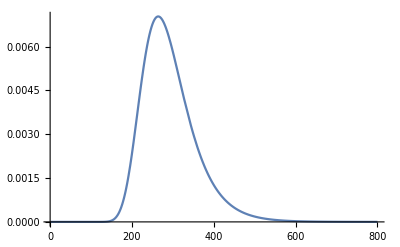

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
N1=1000;
s0=0.1;
h=0.8;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=taui[t]=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;

B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];

a3=Plot[pdfgenh[t],{t,1,800},PlotRange->All,PlotPoints->50]




timePoints=Range[1,800,1];

weightValues=pdfgenh/@timePoints;

Datatfix=Transpose[{timePoints,weightValues}];
```

```mathematica
Quit[]
```

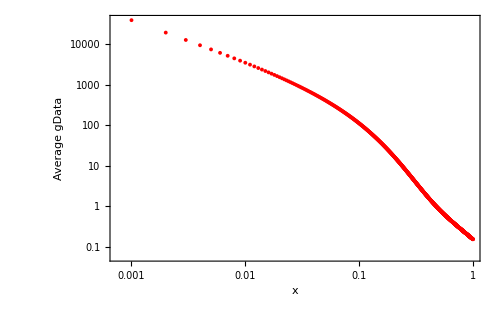

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.8;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

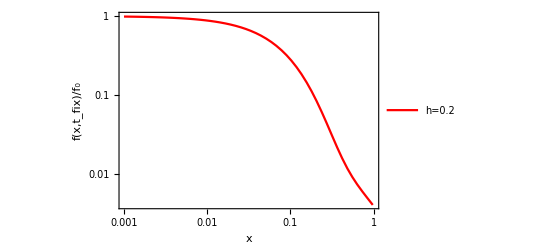

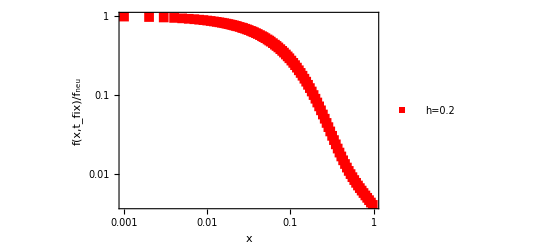

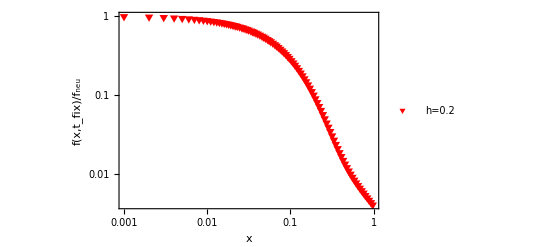

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"■",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

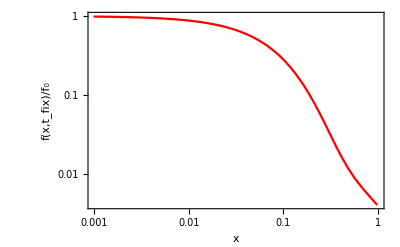
```mathematica
d8=-Graphics-;
```

```mathematica
below withmean tfix
```

```mathematica
Quit[]
```

275.295

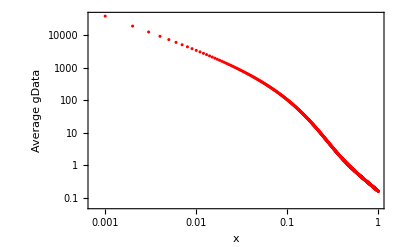

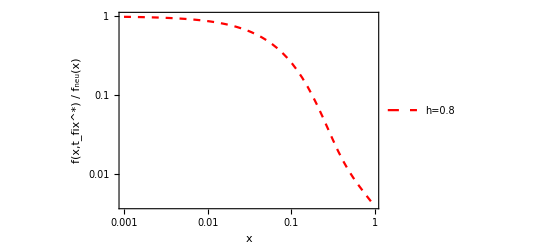

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.8;x0=1/(2 2 s h N1);
(*x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];*)
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1000}];
tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
	Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"●",8}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];


a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,(*FrameLabel->{"x","f(x,t_fix)/f_neu"},*)FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red, Dashed},PlotLegends->{"h=0.8"}];


(*Show both plots*)
Show[a1sInterpolated]
```

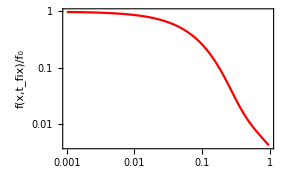
```mathematica
d8=-Graphics-;
```

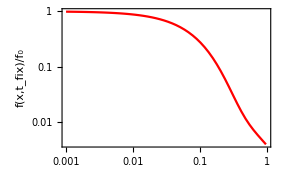
```mathematica
a1=-Graphics-;
```

```mathematica
Show[a1,a2]
```

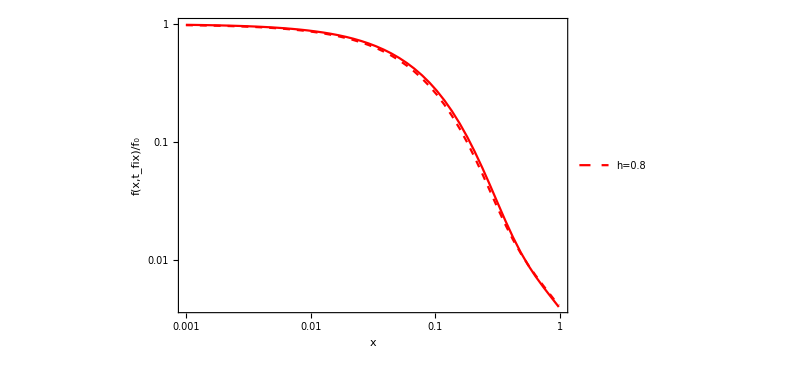

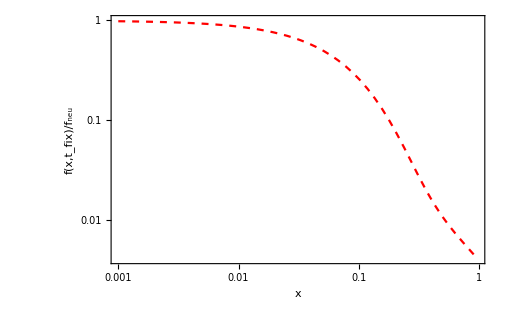
```mathematica
a1=-Graphics-;
```

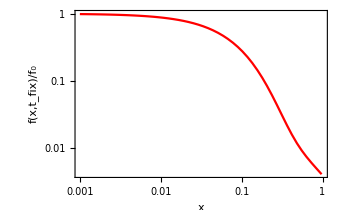
```mathematica
h8dist=-Graphics-;
```

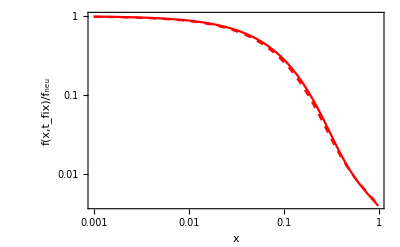

```mathematica
Show[a1,a2]
```

275.295

-Graphics-

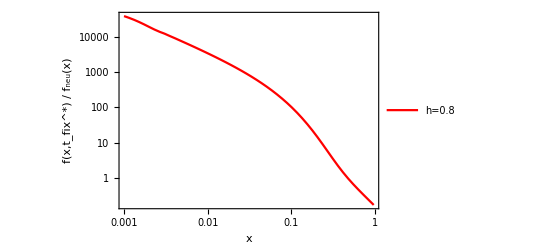

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.8;x0=1/(2 2 s h N1);
(*x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];*)
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,1000}];
tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
	Data1s=Transpose@{xaxis, gData};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"●",8}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];


a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,(*FrameLabel->{"x","f(x,t_fix)/f_neu"},*)FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"h=0.8"}];


(*Show both plots*)
Show[a1sInterpolated]
```

### h = 0.2 for Ns = 10

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

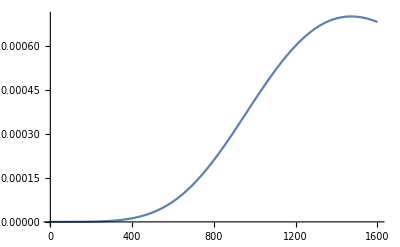

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
N1=1000;
s0=0.01;
h=0.2;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=taui[t]=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;

B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];

a3=Plot[pdfgenh[t],{t,1,3600},PlotRange->All,PlotPoints->50]




timePoints=Range[1,3600,1];

weightValues=pdfgenh/@timePoints;

Datatfix=Transpose[{timePoints,weightValues}];
```

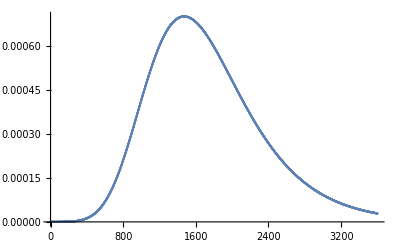

```mathematica
ListPlot[Datatfix]
```

```mathematica
theta 1.0
```

39.9996

```mathematica
Quit[]
```

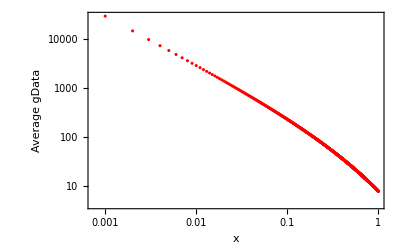

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.01;h=0.2;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,3600}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,3600},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

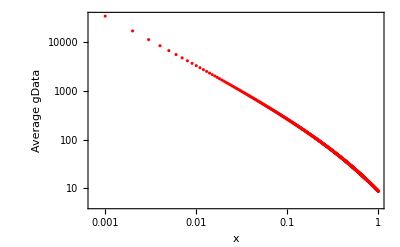

```mathematica
gData=Table[G[x,2206]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

```mathematica
a1=-Graphics-;
```

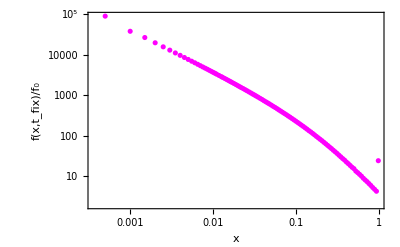
```mathematica
a2=-Graphics-;
```

```mathematica
LogLogPlot[theta/x,{x,0,1}]
```

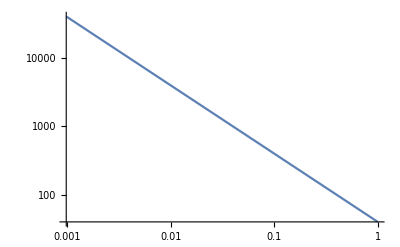
```mathematica
a3=-Graphics-;
```

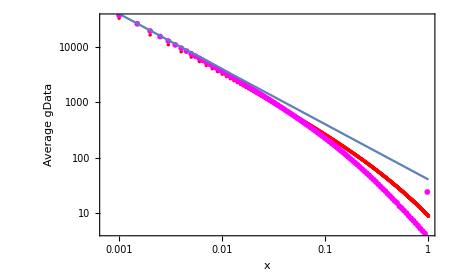

```mathematica
Show[a1,a2,a3]
```

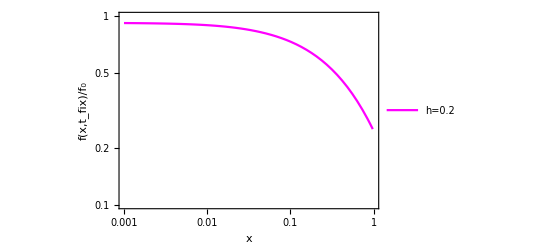

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"■",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.1,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

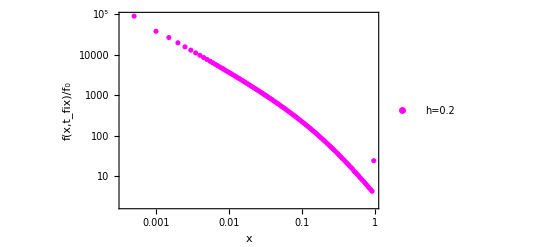

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.2_Ns_10.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,(*x11s x21s/theta *) x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"}(*,PlotRange->{{0.001,1},{0.07,1}}, PlotMarkers->{"▲",12}*)];

(*Show both plots*)
Show[a1sCombined]
```

## Sample SFS for dominance case

```mathematica
Quit[]
```

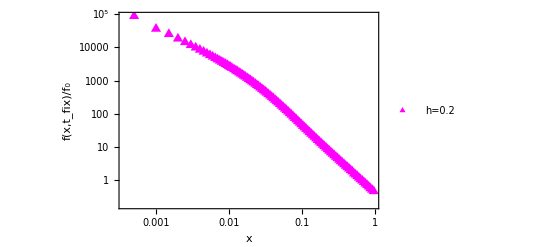

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1sh2=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.2_more_loci.txt"];
datas1sh2=ReadList[s1sh2,{Number,Number}];
Close[s1sh2];

x11sh2=datas1sh2[[All,1]];
x21sh2=datas1sh2[[All,2]];

Data1sh2=Transpose@{x11sh2, x21sh2};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1sh2,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1sh2,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1sh2},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->All, PlotMarkers->{"▲",12}];

(*Show both plots*)
Show[a1sCombined]
```

```mathematica
Data1sh2
```

```mathematica
Data1sh2={{0.,96.347},{0.0005,88103.7},{0.001,36525.7},{0.0015,25264.2},{0.002,18455.8},{0.0025,14422.3},{0.003,11787},{0.0035,9908.71},{0.004,8508.15},{0.0045,7424.37},{0.005,6545.12},{0.0055,5845.4},{0.006,5265.12},{0.0065,4769.96},{0.007,4343.62},{0.0075,3989.27},{0.008,3672.97},{0.0085,3397.4},{0.009,3157.63},{0.0095,2937.94},{0.01,2742.12},{0.0105,2569.96},{0.011,2409.48},{0.0115,2264.38},{0.012,2135.45},{0.0125,2022.95},{0.013,1910.44},{0.0135,1811.7},{0.014,1715.87},{0.0145,1631.78},{0.015,1554.33},{0.0155,1483.6},{0.016,1412.25},{0.0165,1348.9},{0.017,1290.34},{0.0175,1235.15},{0.018,1182.95},{0.0185,1133.03},{0.019,1088.6},{0.0195,1044.12},{0.02,1007.71},{0.0205,964.025},{0.021,927.84},{0.0215,894.386},{0.022,861.246},{0.0225,830.131},{0.023,801.994},{0.0235,774.769},{0.024,747.614},{0.0245,720.207},{0.025,698.555},{0.0255,673.615},{0.026,656.493},{0.0265,633.395},{0.027,611.782},{0.0275,593.642},{0.028,578.061},{0.0285,558.384},{0.029,542.233},{0.0295,526.371},{0.03,511.608},{0.0305,496.897},{0.031,481.67},{0.0315,469.987},{0.032,458.024},{0.0325,444.351},{0.033,431.161},{0.0335,419.925},{0.034,408.919},{0.0345,397.46},{0.035,387.718},{0.0355,377.54},{0.036,369.928},{0.0365,360.527},{0.037,349.752},{0.0375,342.711},{0.038,333.204},{0.0385,326.454},{0.039,317.507},{0.0395,311.96},{0.04,303.173},{0.0405,297.133},{0.041,289.215},{0.0415,282.741},{0.042,275.621},{0.0425,270.444},{0.043,264.425},{0.0435,257.173},{0.044,252.87},{0.0445,247.383},{0.045,241.108},{0.0455,235.922},{0.046,232.51},{0.0465,226.203},{0.047,220.985},{0.0475,217.633},{0.048,214.423},{0.0485,209.974},{0.049,204.401},{0.0495,202.396},{0.05,197.015},{0.0505,194.241},{0.051,189.783},{0.0515,186.494},{0.052,180.89},{0.0525,178.764},{0.053,175.595},{0.0535,172.646},{0.054,169.392},{0.0545,166.502},{0.055,163.135},{0.0555,159.709},{0.056,157.286},{0.0565,155.061},{0.057,151.367},{0.0575,149.531},{0.058,145.905},{0.0585,144.824},{0.059,141.688},{0.0595,137.943},{0.06,136.075},{0.0605,135.303},{0.061,132.497},{0.0615,128.459},{0.062,127.573},{0.0625,126.089},{0.063,123.456},{0.0635,121.902},{0.064,118.472},{0.0645,118.248},{0.065,116.204},{0.0655,114.963},{0.066,113.333},{0.0665,111.113},{0.067,108.691},{0.0675,107.514},{0.068,104.899},{0.0685,103.812},{0.069,103.387},{0.0695,100.773},{0.07,100.453},{0.0705,98.4366},{0.071,96.3046},{0.0715,96.0621},{0.072,93.7683},{0.0725,93.2168},{0.073,92.0084},{0.0735,89.773},{0.074,89.3493},{0.0745,87.2905},{0.075,85.2569},{0.0755,85.2617},{0.076,83.6401},{0.0765,81.4672},{0.077,81.9741},{0.0775,80.303},{0.078,79.4985},{0.0785,77.7601},{0.079,78.3129},{0.0795,75.7483},{0.08,75.663},{0.0805,74.5674},{0.081,73.2957},{0.0815,72.5856},{0.082,71.7484},{0.0825,70.56},{0.083,70.3826},{0.0835,68.7707},{0.084,68.4232},{0.0845,67.5902},{0.085,66.3146},{0.0855,65.6697},{0.086,65.3047},{0.0865,63.5557},{0.087,63.4428},{0.0875,62.0434},{0.088,61.5565},{0.0885,60.4082},{0.089,60.0438},{0.0895,58.7684},{0.09,59.1338},{0.0905,57.8296},{0.091,57.2579},{0.0915,56.3056},{0.092,56.3552},{0.0925,55.8898},{0.093,55.1775},{0.0935,53.0163},{0.094,53.3715},{0.0945,53.6993},{0.095,52.7643},{0.0955,52.0349},{0.096,51.1741},{0.0965,50.5799},{0.097,50.3624},{0.0975,49.302},{0.098,49.6941},{0.0985,48.8247},{0.099,47.8619},{0.0995,47.28},{0.1,47.0769},{0.1005,46.8014},{0.101,45.6908},{0.1015,45.2721},{0.102,45.299},{0.1025,44.0534},{0.103,43.9667},{0.1035,43.1837},{0.104,43.69},{0.1045,42.5079},{0.105,42.2615},{0.1055,42.1722},{0.106,41.1503},{0.1065,40.3439},{0.107,40.7891},{0.1075,40.2482},{0.108,40.138},{0.1085,39.286},{0.109,39.3433},{0.1095,39.4662},{0.11,38.7503},{0.1105,38.2068},{0.111,37.5763},{0.1115,37.767},{0.112,37.244},{0.1125,37.2343},{0.113,35.7411},{0.1135,36.2651},{0.114,35.8125},{0.1145,35.6732},{0.115,35.3518},{0.1155,34.057},{0.116,34.255},{0.1165,33.9646},{0.117,33.3501},{0.1175,33.7589},{0.118,33.1099},{0.1185,32.7522},{0.119,32.9444},{0.1195,32.3167},{0.12,32.0843},{0.1205,31.8143},{0.121,31.0953},{0.1215,30.9965},{0.122,31.0582},{0.1225,30.3362},{0.123,30.544},{0.1235,30.043},{0.124,29.6619},{0.1245,29.6531},{0.125,28.8955},{0.1255,28.7065},{0.126,28.839},{0.1265,28.8987},{0.127,28.1227},{0.1275,27.7687},{0.128,27.7335},{0.1285,28.1632},{0.129,27.5383},{0.1295,27.519},{0.13,27.2246},{0.1305,26.7927},{0.131,26.767},{0.1315,26.1956},{0.132,25.5522},{0.1325,25.5442},{0.133,25.7972},{0.1335,25.8576},{0.134,25.7307},{0.1345,25.1152},{0.135,24.7511},{0.1355,24.5083},{0.136,24.361},{0.1365,24.5692},{0.137,24.5471},{0.1375,24.0703},{0.138,24.0207},{0.1385,23.2619},{0.139,23.8789},{0.1395,23.7279},{0.14,23.0126},{0.1405,23.0714},{0.141,22.7234},{0.1415,22.4619},{0.142,22.2908},{0.1425,21.8733},{0.143,22.2536},{0.1435,22.0258},{0.144,22.0111},{0.1445,22.0382},{0.145,21.6682},{0.1455,21.1638},{0.146,21.3255},{0.1465,21.3896},{0.147,20.9601},{0.1475,20.6542},{0.148,20.7593},{0.1485,20.2656},{0.149,20.503},{0.1495,20.3124},{0.15,19.9402},{0.1505,20.0461},{0.151,19.5941},{0.1515,19.5934},{0.152,19.5734},{0.1525,19.4753},{0.153,19.4924},{0.1535,18.8414},{0.154,19.0612},{0.1545,18.881},{0.155,18.548},{0.1555,18.4426},{0.156,18.2761},{0.1565,18.7185},{0.157,18.4863},{0.1575,17.7895},{0.158,17.8079},{0.1585,17.6234},{0.159,17.4043},{0.1595,18.0507},{0.16,17.8199},{0.1605,17.6059},{0.161,17.0865},{0.1615,16.644},{0.162,17.2818},{0.1625,16.6359},{0.163,16.7148},{0.1635,17.17},{0.164,16.4947},{0.1645,16.5555},{0.165,16.282},{0.1655,16.459},{0.166,16.1784},{0.1665,15.7251},{0.167,16.0093},{0.1675,15.8504},{0.168,16.1233},{0.1685,15.49},{0.169,15.6363},{0.1695,15.3979},{0.17,15.197},{0.1705,15.4952},{0.171,15.3755},{0.1715,15.1073},{0.172,15.0716},{0.1725,14.901},{0.173,14.6215},{0.1735,14.8269},{0.174,14.4386},{0.1745,14.5618},{0.175,14.5542},{0.1755,14.3188},{0.176,14.1916},{0.1765,14.2003},{0.177,13.9516},{0.1775,14.1442},{0.178,13.5657},{0.1785,13.9872},{0.179,13.7167},{0.1795,13.8824},{0.18,13.5264},{0.1805,13.5918},{0.181,13.6845},{0.1815,13.4451},{0.182,13.3722},{0.1825,13.3203},{0.183,12.8546},{0.1835,13.1533},{0.184,13.3707},{0.1845,13.3959},{0.185,12.9214},{0.1855,13.1392},{0.186,12.8053},{0.1865,12.8562},{0.187,12.8645},{0.1875,12.517},{0.188,12.5708},{0.1885,12.2932},{0.189,12.3168},{0.1895,12.2535},{0.19,12.0583},{0.1905,12.4085},{0.191,12.2745},{0.1915,12.4305},{0.192,11.699},{0.1925,12.1547},{0.193,11.6473},{0.1935,11.9144},{0.194,11.6618},{0.1945,11.3354},{0.195,11.6771},{0.1955,11.773},{0.196,11.4124},{0.1965,11.7122},{0.197,11.1809},{0.1975,11.2665},{0.198,11.08},{0.1985,11.1436},{0.199,10.8369},{0.1995,10.9199},{0.2,11.1152},{0.2005,10.6955},{0.201,10.6123},{0.2015,10.4517},{0.202,10.6123},{0.2025,11.1809},{0.203,10.8097},{0.2035,10.7284},{0.204,10.2932},{0.2045,10.4497},{0.205,10.694},{0.2055,10.4966},{0.206,10.7861},{0.2065,10.2752},{0.207,10.479},{0.2075,9.86481},{0.208,10.5118},{0.2085,10.286},{0.209,10.0793},{0.2095,9.99684},{0.21,10.2116},{0.2105,9.90885},{0.211,10.0149},{0.2115,10.1523},{0.212,9.74576},{0.2125,9.67735},{0.213,9.87914},{0.2135,9.87831},{0.214,9.5112},{0.2145,9.73459},{0.215,9.67778},{0.2155,9.42544},{0.216,9.52888},{0.2165,9.57884},{0.217,9.07676},{0.2175,9.26569},{0.218,9.17929},{0.2185,9.26421},{0.219,9.04989},{0.2195,8.901},{0.22,9.00386},{0.2205,8.92144},{0.221,9.25135},{0.2215,8.70755},{0.222,8.84495},{0.2225,8.83369},{0.223,8.9754},{0.2235,8.84211},{0.224,8.72916},{0.2245,8.78824},{0.225,8.75402},{0.2255,8.58102},{0.226,8.73716},{0.2265,8.50219},{0.227,8.38807},{0.2275,8.40051},{0.228,8.24309},{0.2285,8.37606},{0.229,8.73126},{0.2295,8.46973},{0.23,8.42412},{0.2305,8.20505},{0.231,8.07292},{0.2315,8.09379},{0.232,8.27671},{0.2325,8.13066},{0.233,7.96966},{0.2335,7.95564},{0.234,7.79305},{0.2345,7.90192},{0.235,7.92561},{0.2355,7.83584},{0.236,7.88991},{0.2365,7.74185},{0.237,7.85186},{0.2375,7.82677},{0.238,8.01402},{0.2385,7.75343},{0.239,7.81383},{0.2395,7.70455},{0.24,7.68411},{0.2405,7.76261},{0.241,7.52153},{0.2415,7.34134},{0.242,7.42143},{0.2425,7.43143},{0.243,7.59853},{0.2435,7.65408},{0.244,7.41067},{0.2445,7.20605},{0.245,7.35378},{0.2455,7.32142},{0.246,7.08109},{0.2465,7.0343},{0.247,7.00943},{0.2475,6.97507},{0.248,7.10721},{0.2485,6.83368},{0.249,6.87373},{0.2495,7.11238},{0.25,7.00585},{0.2505,6.91977},{0.251,7.07508},{0.2515,6.93936},{0.252,6.98066},{0.2525,7.03713},{0.253,6.89774},{0.2535,7.01227},{0.254,6.5458},{0.2545,6.61463},{0.255,6.70957},{0.2555,6.71048},{0.256,6.86054},{0.2565,6.51419},{0.257,6.58985},{0.2575,6.58944},{0.258,6.42885},{0.2585,6.61746},{0.259,6.55382},{0.2595,6.316},{0.26,6.52495},{0.2605,6.40442},{0.261,6.35287},{0.2615,6.45013},{0.262,6.48734},{0.2625,6.26753},{0.263,6.23992},{0.2635,6.45646},{0.264,6.34318},{0.2645,6.33318},{0.265,6.19705},{0.2655,6.3728},{0.266,5.994},{0.2665,5.85153},{0.267,6.02729},{0.2675,6.18913},{0.268,6.15584},{0.2685,5.93646},{0.269,6.12139},{0.2695,6.11413},{0.27,6.14457},{0.2705,6.03456},{0.271,6.27395},{0.2715,6.05016},{0.272,5.78222},{0.2725,5.91634},{0.273,5.75143},{0.2735,6.02212},{0.274,5.78579},{0.2745,5.67694},{0.275,5.73826},{0.2755,5.73541},{0.276,5.51436},{0.2765,5.5368},{0.277,5.68094},{0.2775,5.3778},{0.278,5.89474},{0.2785,5.69822},{0.279,5.5112},{0.2795,5.69579},{0.28,5.71898},{0.2805,5.61161},{0.281,5.64291},{0.2815,5.61371},{0.282,5.52321},{0.2825,5.41342},{0.283,5.59402},{0.2835,5.57558},{0.284,5.43628},{0.2845,5.3739},{0.285,5.4055},{0.2855,5.44671},{0.286,5.3838},{0.2865,5.34418},{0.287,5.46431},{0.2875,5.15558},{0.288,5.16759},{0.2885,5.25726},{0.289,5.00426},{0.2895,5.24809},{0.29,5.35779},{0.2905,5.23609},{0.291,5.00827},{0.2915,4.98299},{0.292,5.07591},{0.2925,5.21373},{0.293,5.06591},{0.2935,5.12154},{0.294,5.18761},{0.2945,5.0011},{0.295,4.90816},{0.2955,5.11153},{0.296,5.02354},{0.2965,4.81883},{0.297,5.0207},{0.2975,5.08835},{0.298,4.87698},{0.2985,4.88531},{0.299,4.85528},{0.2995,5.12965},{0.3,4.85886},{0.3005,5.11923},{0.301,4.64549},{0.3015,4.73315},{0.302,4.79564},{0.3025,4.78046},{0.303,4.68469},{0.3035,4.69153},{0.304,4.63548},{0.3045,4.74643},{0.305,4.8613},{0.3055,4.69111},{0.306,4.79722},{0.3065,4.75117},{0.307,4.71641},{0.3075,4.65591},{0.308,4.67069},{0.3085,4.6927},{0.309,4.62072},{0.3095,4.62062},{0.31,4.53696},{0.3105,4.57458},{0.311,4.71673},{0.3115,4.75076},{0.312,4.69553},{0.3125,4.45287},{0.313,4.50451},{0.3135,4.42527},{0.314,4.5634},{0.3145,4.24425},{0.315,4.62463},{0.3155,4.37722},{0.316,4.30673},{0.3165,4.22823},{0.317,4.24867},{0.3175,4.41926},{0.318,4.37238},{0.3185,4.43327},{0.319,4.42727},{0.3195,4.25468},{0.32,4.23666},{0.3205,4.16459},{0.321,4.24119},{0.3215,4.07892},{0.322,4.2275},{0.3225,4.14056},{0.323,4.10653},{0.3235,4.29071},{0.324,4.40883},{0.3245,4.09852},{0.325,4.03688},{0.3255,4.29113},{0.326,4.09061},{0.3265,3.95437},{0.327,4.11854},{0.3275,4.07608},{0.328,4.18218},{0.3285,4.23349},{0.329,4.24108},{0.3295,4.00443},{0.33,4.0509},{0.3305,3.85628},{0.331,4.01844},{0.3315,3.96997},{0.332,3.92793},{0.3325,3.91233},{0.333,4.04288},{0.3335,3.91992},{0.334,3.88716},{0.3345,3.94805},{0.335,3.84869},{0.3355,3.75101},{0.336,3.77778},{0.3365,4.02603},{0.337,4.03931},{0.3375,3.71371},{0.338,3.74542},{0.3385,3.81265},{0.339,3.93794},{0.3395,3.76619},{0.34,3.7938},{0.3405,3.7606},{0.341,3.77019},{0.3415,3.73258},{0.342,3.87388},{0.3425,3.72857},{0.343,3.65049},{0.3435,3.75017},{0.344,3.82225},{0.3445,3.8567},{0.345,3.80265},{0.3455,3.70856},{0.346,3.59486},{0.3465,3.53079},{0.347,3.55356},{0.3475,3.58801},{0.348,3.46431},{0.3485,3.67168},{0.349,3.70772},{0.3495,3.72382},{0.35,3.46789},{0.3505,3.34177},{0.351,3.52194},{0.3515,3.41142},{0.352,3.53638},{0.3525,3.49591},{0.353,3.61003},{0.3535,3.58526},{0.354,3.38539},{0.3545,3.55356},{0.355,3.46631},{0.3555,3.30573},{0.356,3.50434},{0.3565,3.45145},{0.357,3.53079},{0.3575,3.35946},{0.358,3.37579},{0.3585,3.44987},{0.359,3.43628},{0.3595,3.57959},{0.36,3.22164},{0.3605,3.20362},{0.361,3.44186},{0.3615,3.25568},{0.362,3.32016},{0.3625,3.35736},{0.363,3.37622},{0.3635,3.4015},{0.364,3.43111},{0.3645,3.46514},{0.365,3.40941},{0.3655,3.16359},{0.366,3.30815},{0.3665,3.37379},{0.367,3.43828},{0.3675,3.40382},{0.368,3.25526},{0.3685,3.31932},{0.369,3.00743},{0.3695,3.08592},{0.37,3.00501},{0.3705,3.23566},{0.371,3.05148},{0.3715,2.95221},{0.372,3.2541},{0.3725,3.31574},{0.373,3.1736},{0.3735,3.13239},{0.374,3.1031},{0.3745,2.95938},{0.375,3.20805},{0.3755,2.997},{0.376,2.96781},{0.3765,3.20646},{0.377,3.00184},{0.3775,3.19962},{0.378,3.17602},{0.3785,3.10153},{0.379,3.20162},{0.3795,2.90891},{0.38,2.98541},{0.3805,2.92344},{0.381,2.99626},{0.3815,3.04146},{0.382,3.01102},{0.3825,3.04747},{0.383,2.98783},{0.3835,3.00584},{0.384,3.00142},{0.3845,2.98783},{0.385,2.90491},{0.3855,2.88731},{0.386,2.94937},{0.3865,2.85887},{0.387,2.88288},{0.3875,3.14715},{0.388,2.94294},{0.3885,2.8969},{0.389,2.99542},{0.3895,2.83926},{0.39,2.8733},{0.3905,2.77478},{0.391,2.85486},{0.3915,2.94495},{0.392,2.95096},{0.3925,2.67868},{0.393,2.73758},{0.3935,2.80481},{0.394,2.80322},{0.3945,2.69796},{0.395,2.76076},{0.3955,2.69269},{0.396,2.76119},{0.3965,2.8597},{0.397,2.79322},{0.3975,2.82282},{0.398,2.989},{0.3985,2.84885},{0.399,2.84769},{0.3995,2.63263},{0.4,2.47648},{0.4005,2.59902},{0.401,2.84168},{0.4015,2.66667},{0.402,2.64907},{0.4025,2.82483},{0.403,2.73875},{0.4035,2.79364},{0.404,2.74074},{0.4045,2.66392},{0.405,2.57742},{0.4055,2.68269},{0.406,2.71872},{0.4065,2.62663},{0.407,2.58543},{0.4075,2.67868},{0.408,2.49291},{0.4085,2.71756},{0.409,2.66667},{0.4095,2.62146},{0.41,2.65065},{0.4105,2.66467},{0.411,2.67509},{0.4115,2.61862},{0.412,2.62505},{0.4125,2.60662},{0.413,2.46246},{0.4135,2.52252},{0.414,2.39481},{0.4145,2.51819},{0.415,2.62705},{0.4155,2.54497},{0.416,2.55256},{0.4165,2.68911},{0.417,2.58058},{0.4175,2.47531},{0.418,2.50851},{0.4185,2.49692},{0.419,2.58142},{0.4195,2.56983},{0.42,2.44887},{0.4205,2.54054},{0.421,2.66192},{0.4215,2.41968},{0.422,2.63148},{0.4225,2.61303},{0.423,2.42643},{0.4235,2.53095},{0.424,2.36479},{0.4245,2.47974},{0.425,2.26627},{0.4255,2.48132},{0.426,2.34434},{0.4265,2.35562},{0.427,2.51652},{0.4275,2.57058},{0.428,2.31431},{0.4285,2.4885},{0.429,2.44487},{0.4295,2.44086},{0.43,2.51694},{0.4305,2.53896},{0.431,2.41209},{0.4315,2.38238},{0.432,2.47248},{0.4325,2.2767},{0.433,2.25026},{0.4335,2.21021},{0.434,2.22823},{0.4345,2.28354},{0.435,2.34276},{0.4355,2.53854},{0.436,2.31232},{0.4365,2.29071},{0.437,2.25793},{0.4375,2.39081},{0.438,2.39808},{0.4385,2.2827},{0.439,2.28513},{0.4395,2.29672},{0.44,2.2002},{0.4405,2.30831},{0.441,2.23023},{0.4415,2.23908},{0.442,2.36036},{0.4425,2.32433},{0.443,2.20663},{0.4435,2.25552},{0.444,2.31432},{0.4445,2.17059},{0.445,2.28554},{0.4455,2.16416},{0.446,2.24066},{0.4465,2.15616},{0.447,2.26226},{0.4475,2.31073},{0.448,2.2551},{0.4485,2.23223},{0.449,2.41125},{0.4495,2.04605},{0.45,2.19946},{0.4505,2.09051},{0.451,2.25626},{0.4515,2.15658},{0.452,2.25225},{0.4525,2.2022},{0.453,2.14657},{0.4535,2.1258},{0.454,2.16459},{0.4545,2.15858},{0.455,1.96122},{0.4555,2.10653},{0.456,1.86871},{0.4565,2.03688},{0.457,2.10653},{0.4575,2.14414},{0.458,2.18061},{0.4585,2.10695},{0.459,2.10811},{0.4595,2.15257},{0.46,2.11612},{0.4605,2.21021},{0.461,2.04447},{0.4615,2.00601},{0.462,2.17702},{0.4625,1.998},{0.463,1.97039},{0.4635,2.11211},{0.464,1.98841},{0.4645,2.05005},{0.465,2.04404},{0.4655,2.21022},{0.466,1.93193},{0.4665,2.07208},{0.467,2.05606},{0.4675,1.98166},{0.468,2.004},{0.4685,1.91317},{0.469,1.98198},{0.4695,2.02687},{0.47,1.998},{0.4705,2.06607},{0.471,1.88272},{0.4715,2.13455},{0.472,1.86587},{0.4725,2.06206},{0.473,2.01001},{0.4735,2.0353},{0.474,1.97323},{0.4745,1.88715},{0.475,1.99842},{0.4755,1.81182},{0.476,1.95764},{0.4765,1.90591},{0.477,1.82625},{0.4775,1.8939},{0.478,1.90274},{0.4785,1.95838},{0.479,1.87788},{0.4795,1.86554},{0.48,1.82909},{0.4805,1.82066},{0.481,2.03204},{0.4815,1.94394},{0.482,1.92192},{0.4825,1.90074},{0.483,1.88231},{0.4835,1.96597},{0.484,1.93594},{0.4845,1.75175},{0.485,1.76577},{0.4855,1.8803},{0.486,1.84985},{0.4865,1.86587},{0.487,1.86386},{0.4875,1.86187},{0.488,1.83384},{0.4885,1.73373},{0.489,1.91792},{0.4895,1.8803},{0.49,1.93193},{0.4905,1.80022},{0.491,1.85986},{0.4915,1.86787},{0.492,1.87588},{0.4925,1.69169},{0.493,1.8979},{0.4935,1.74375},{0.494,1.82783},{0.4945,1.69011},{0.495,1.90233},{0.4955,1.79347},{0.496,1.78579},{0.4965,1.78378},{0.497,1.83584},{0.4975,1.93394},{0.498,1.71172},{0.4985,1.74975},{0.499,1.78062},{0.4995,1.78462},{0.5,3.60202},{0.5005,0.00600601},{0.501,3.62405},{0.5015,0.002002},{0.502,3.4427},{0.5025,0},{0.503,3.38781},{0.5035,0.004004},{0.504,3.42827},{0.5045,0},{0.505,3.37422},{0.5055,0},{0.506,3.2661},{0.5065,0.00600601},{0.507,3.31173},{0.5075,0.004004},{0.508,3.46389},{0.5085,0.002002},{0.509,3.44745},{0.5095,0},{0.51,3.28012},{0.5105,0},{0.511,3.34619},{0.5115,0},{0.512,1.68168},{0.5125,1.56357},{0.513,1.59802},{0.5135,1.82224},{0.514,1.59201},{0.5145,1.68811},{0.515,1.62046},{0.5155,1.76376},{0.516,1.72173},{0.5165,1.68136},{0.517,1.61203},{0.5175,1.60361},{0.518,1.59359},{0.5185,1.72773},{0.519,1.74374},{0.5195,1.63647},{0.52,1.65533},{0.5205,1.49391},{0.521,1.76661},{0.5215,1.58959},{0.522,1.60761},{0.5225,1.54197},{0.523,1.61203},{0.5235,1.47948},{0.524,1.53196},{0.5245,1.62162},{0.525,1.54354},{0.5255,1.60602},{0.526,1.6977},{0.5265,1.5624},{0.527,1.62605},{0.5275,1.5976},{0.528,1.5644},{0.5285,1.47347},{0.529,1.51594},{0.5295,1.60602},{0.53,1.56999},{0.5305,1.67768},{0.531,1.50751},{0.5315,1.45746},{0.532,1.54196},{0.5325,1.51477},{0.533,1.60402},{0.5335,1.6016},{0.534,1.50351},{0.5345,1.54555},{0.535,1.56156},{0.5355,1.54955},{0.536,1.55756},{0.5365,1.42543},{0.537,1.6036},{0.5375,1.51151},{0.538,1.56156},{0.5385,1.41583},{0.539,1.48549},{0.5395,1.44945},{0.54,1.53796},{0.5405,1.50952},{0.541,1.48349},{0.5415,1.60002},{0.542,1.49876},{0.5425,1.47347},{0.543,1.43544},{0.5435,1.4467},{0.544,1.51752},{0.5445,1.4799},{0.545,1.54997},{0.5455,1.56282},{0.546,1.48833},{0.5465,1.46989},{0.547,1.47948},{0.5475,1.41183},{0.548,1.53554},{0.5485,1.54997},{0.549,1.46547},{0.5495,1.38338},{0.55,1.48949},{0.5505,1.41341},{0.551,1.4955},{0.5515,1.44344},{0.552,1.46147},{0.5525,1.576},{0.553,1.33734},{0.5535,1.44344},{0.554,1.46747},{0.5545,1.48749},{0.555,1.48749},{0.5555,1.42342},{0.556,1.45946},{0.5565,1.46272},{0.557,1.4014},{0.5575,1.35177},{0.558,1.47147},{0.5585,1.35778},{0.559,1.33534},{0.5595,1.44228},{0.56,1.45946},{0.5605,1.32332},{0.561,1.3818},{0.5615,1.34218},{0.562,1.39023},{0.5625,1.44945},{0.563,1.37137},{0.5635,1.35135},{0.564,1.3838},{0.5645,1.36937},{0.565,1.49033},{0.5655,1.21121},{0.566,1.38739},{0.5665,1.42026},{0.567,1.21522},{0.5675,1.25526},{0.568,1.26769},{0.5685,1.50952},{0.569,1.40382},{0.5695,1.34535},{0.57,1.36979},{0.5705,1.35736},{0.571,1.3954},{0.5715,1.41342},{0.572,1.41584},{0.5725,1.27127},{0.573,1.28929},{0.5735,1.4387},{0.574,1.39023},{0.5745,1.23524},{0.575,1.28328},{0.5755,1.25926},{0.576,1.35177},{0.5765,1.23524},{0.577,1.22807},{0.5775,1.40541},{0.578,1.3013},{0.5785,1.26927},{0.579,1.32132},{0.5795,1.34535},{0.58,1.33334},{0.5805,1.23924},{0.581,1.31131},{0.5815,1.43344},{0.582,1.24925},{0.5825,1.27528},{0.583,1.34535},{0.5835,1.32733},{0.584,1.23608},{0.5845,1.29972},{0.585,1.39782},{0.5855,1.32733},{0.586,1.2933},{0.5865,1.2973},{0.587,1.23924},{0.5875,1.2837},{0.588,1.22923},{0.5885,1.29372},{0.589,1.24324},{0.5895,1.34777},{0.59,1.24725},{0.5905,1.33534},{0.591,1.26368},{0.5915,1.31131},{0.592,1.22723},{0.5925,1.2032},{0.593,1.35335},{0.5935,1.29371},{0.594,1.1932},{0.5945,1.18044},{0.595,1.26126},{0.5955,1.25526},{0.596,1.18519},{0.5965,1.25125},{0.597,1.11312},{0.5975,1.15758},{0.598,1.21922},{0.5985,1.20921},{0.599,1.31499},{0.5995,1.21922},{0.6,1.18961},{0.6005,1.30731},{0.601,1.11111},{0.6015,1.24525},{0.602,1.21922},{0.6025,1.20963},{0.603,1.23323},{0.6035,1.32132},{0.604,1.17117},{0.6045,1.22923},{0.605,1.18002},{0.6055,1.21121},{0.606,1.21522},{0.6065,1.24325},{0.607,1.23724},{0.6075,1.06148},{0.608,1.16158},{0.6085,1.23123},{0.609,1.10511},{0.6095,1.13313},{0.61,1.23365},{0.6105,1.1972},{0.611,1.22122},{0.6115,1.16917},{0.612,1.24767},{0.6125,1.27611},{0.613,1.0991},{0.6135,1.0991},{0.614,1.1031},{0.6145,1.21321},{0.615,1.18919},{0.6155,1.11554},{0.616,1.2953},{0.6165,1.16158},{0.617,1.22965},{0.6175,1.10711},{0.618,1.16317},{0.6185,1.21522},{0.619,1.08835},{0.6195,1.0991},{0.62,1.12555},{0.6205,1.14114},{0.621,1.17918},{0.6215,1.12998},{0.622,1.19361},{0.6225,1.14315},{0.623,1.10912},{0.6235,1.13313},{0.624,1.09109},{0.6245,1.162},{0.625,1.10911},{0.6255,1.20921},{0.626,1.0931},{0.6265,1.13714},{0.627,1.07908},{0.6275,1.12596},{0.628,1.05906},{0.6285,1.08108},{0.629,1.14757},{0.6295,1.04146},{0.63,1.22048},{0.6305,1.06907},{0.631,1.16116},{0.6315,1.12154},{0.632,1.10911},{0.6325,1.13113},{0.633,1.04747},{0.6335,1.07107},{0.634,1.08909},{0.6345,1.1031},{0.635,1.10036},{0.6355,1.11311},{0.636,1.03504},{0.6365,1.03104},{0.637,1.1031},{0.6375,1.05906},{0.638,1.09393},{0.6385,1.12914},{0.639,1.22523},{0.6395,1.02503},{0.64,1.0775},{0.6405,1.08509},{0.641,1.08108},{0.6415,1.01301},{0.642,1.02945},{0.6425,1.11311},{0.643,0.960961},{0.6435,1.05105},{0.644,1.02503},{0.6445,1.10711},{0.645,1.06306},{0.6455,1.00542},{0.646,1.003},{0.6465,0.97139},{0.647,0.929352},{0.6475,1.11512},{0.648,0.984987},{0.6485,0.984987},{0.649,1.06907},{0.6495,1.11595},{0.65,0.99141},{0.6505,1.05105},{0.651,1.05706},{0.6515,1.04905},{0.652,1.06306},{0.6525,1.03103},{0.653,1.08509},{0.6535,0.992995},{0.654,1.0991},{0.6545,1.03345},{0.655,1.05547},{0.6555,0.962963},{0.656,1.03345},{0.6565,1.08309},{0.657,0.975394},{0.6575,1.04304},{0.658,0.982983},{0.6585,0.981404},{0.659,1.13313},{0.6595,0.974975},{0.66,1.00501},{0.6605,0.984987},{0.661,1.14715},{0.6615,1.01301},{0.662,0.946947},{0.6625,1.00901},{0.663,1.07349},{0.6635,1.03704},{0.664,0.880881},{0.6645,0.977396},{0.665,1.02302},{0.6655,1.02102},{0.666,0.966969},{0.6665,1.01343},{0.667,1.08308},{0.6675,0.884885},{0.668,0.860863},{0.6685,0.964965},{0.669,1.06707},{0.6695,1.01143},{0.67,1.00301},{0.6705,0.984985},{0.671,1.04188},{0.6715,1.03946},{0.672,0.884885},{0.6725,1.03303},{0.673,1.001},{0.6735,0.874875},{0.674,0.970971},{0.6745,0.954955},{0.675,0.964965},{0.6755,0.992995},{0.676,0.902905},{0.6765,1.01185},{0.677,1.03904},{0.6775,0.992997},{0.678,0.970971},{0.6785,0.920923},{0.679,0.936937},{0.6795,0.822825},{0.68,0.914171},{0.6805,0.927346},{0.681,1.03103},{0.6815,0.92134},{0.682,0.874875},{0.6825,0.990247},{0.683,0.950951},{0.6835,0.990991},{0.684,0.876877},{0.6845,0.860863},{0.685,0.967812},{0.6855,0.948949},{0.686,1.00301},{0.6865,1.06348},{0.687,0.949368},{0.6875,0.946947},{0.688,0.89131},{0.6885,0.965384},{0.689,1.01343},{0.6895,0.955374},{0.69,0.932935},{0.6905,1.00226},{0.691,0.892893},{0.6915,0.876877},{0.692,0.928931},{0.6925,0.952953},{0.693,0.980983},{0.6935,0.928929},{0.694,0.89131},{0.6945,0.946951},{0.695,0.964967},{0.6955,0.876877},{0.696,0.932933},{0.6965,0.978981},{0.697,0.894895},{0.6975,0.940941},{0.698,0.939782},{0.6985,0.952953},{0.699,0.839262},{0.6995,0.958959},{0.7,0.954955},{0.7005,0.894895},{0.701,0.929348},{0.7015,0.874877},{0.702,0.909332},{0.7025,0.904905},{0.703,0.934939},{0.7035,0.897316},{0.704,0.853691},{0.7045,0.862863},{0.705,0.924929},{0.7055,0.904907},{0.706,0.887306},{0.7065,0.863282},{0.707,0.91133},{0.7075,0.996997},{0.708,0.916917},{0.7085,0.964967},{0.709,0.89131},{0.7095,0.846847},{0.71,0.798799},{0.7105,0.930933},{0.711,0.84927},{0.7115,0.931352},{0.712,0.844845},{0.7125,0.914915},{0.713,0.746749},{0.7135,0.81123},{0.714,0.854855},{0.7145,0.846847},{0.715,0.864865},{0.7155,0.867286},{0.716,0.834835},{0.7165,0.850851},{0.717,0.858859},{0.7175,0.752755},{0.718,0.804805},{0.7185,0.854863},{0.719,0.85127},{0.7195,0.842847},{0.72,0.915334},{0.7205,0.80122},{0.721,0.906907},{0.7215,0.788789},{0.722,0.854855},{0.7225,0.728729},{0.723,0.882139},{0.7235,0.861701},{0.724,0.864865},{0.7245,0.808813},{0.725,0.886889},{0.7255,0.882883},{0.726,0.859278},{0.7265,0.890893},{0.727,0.880881},{0.7275,0.883302},{0.728,0.912913},{0.7285,0.892893},{0.729,0.914915},{0.7295,0.727148},{0.73,0.712713},{0.7305,0.803222},{0.731,0.814815},{0.7315,0.778779},{0.732,0.840843},{0.7325,0.77119},{0.733,0.89173},{0.7335,0.822823},{0.734,0.874881},{0.7345,0.820821},{0.735,0.767186},{0.7355,0.810811},{0.736,0.814817},{0.7365,0.911334},{0.737,0.757176},{0.7375,0.854855},{0.738,0.900905},{0.7385,0.854857},{0.739,0.810811},{0.7395,0.921344},{0.74,0.758759},{0.7405,0.844847},{0.741,0.786787},{0.7415,0.741579},{0.742,0.924927},{0.7425,0.796797},{0.743,0.848849},{0.7435,0.816817},{0.744,0.745164},{0.7445,0.704705},{0.745,0.736741},{0.7455,0.696697},{0.746,0.758759},{0.7465,0.744749},{0.747,0.776777},{0.7475,0.850851},{0.748,0.844845},{0.7485,0.744745},{0.749,0.779198},{0.7495,0.740741},{0.75,0.733573},{0.7505,0.80723},{0.751,0.812069},{0.7515,0.794797},{0.752,0.756761},{0.7525,0.878881},{0.753,0.836837},{0.7535,0.800807},{0.754,0.764765},{0.7545,0.818821},{0.755,0.794795},{0.7555,0.726727},{0.756,0.775196},{0.7565,0.734735},{0.757,0.813236},{0.7575,0.633052},{0.758,0.775613},{0.7585,0.666667},{0.759,0.736737},{0.7595,0.814817},{0.76,0.764765},{0.7605,0.714715},{0.761,0.796797},{0.7615,0.828829},{0.762,0.782785},{0.7625,0.747585},{0.763,0.696697},{0.7635,0.676677},{0.764,0.774775},{0.7645,0.708709},{0.765,0.790795},{0.7655,0.748749},{0.766,0.834835},{0.7665,0.762763},{0.767,0.770771},{0.7675,0.692693},{0.768,0.742745},{0.7685,0.694695},{0.769,0.798799},{0.7695,0.760763},{0.77,0.766767},{0.7705,0.779198},{0.771,0.716717},{0.7715,0.6811},{0.772,0.843681},{0.7725,0.792793},{0.773,0.830833},{0.7735,0.775196},{0.774,0.828829},{0.7745,0.762763},{0.775,0.668671},{0.7755,0.66909},{0.776,0.752755},{0.7765,0.732733},{0.777,0.702703},{0.7775,0.664665},{0.778,0.706707},{0.7785,0.739158},{0.779,0.838839},{0.7795,0.728729},{0.78,0.730733},{0.7805,0.614615},{0.781,0.716717},{0.7815,0.742743},{0.782,0.726729},{0.7825,0.676677},{0.783,0.690691},{0.7835,0.680681},{0.784,0.716717},{0.7845,0.652653},{0.785,0.710711},{0.7855,0.670671},{0.786,0.682683},{0.7865,0.698699},{0.787,0.756757},{0.7875,0.763601},{0.788,0.692701},{0.7885,0.696697},{0.789,0.692693},{0.7895,0.786787},{0.79,0.726727},{0.7905,0.738739},{0.791,0.666667},{0.7915,0.696699},{0.792,0.718719},{0.7925,0.655074},{0.793,0.681519},{0.7935,0.768769},{0.794,0.748749},{0.7945,0.776785},{0.795,0.644645},{0.7955,0.638641},{0.796,0.662663},{0.7965,0.692693},{0.797,0.739577},{0.7975,0.742743},{0.798,0.576579},{0.7985,0.704705},{0.799,0.726727},{0.7995,0.752755},{0.8,0.690691},{0.8005,0.689108},{0.801,0.653491},{0.8015,0.670671},{0.802,0.753172},{0.8025,0.680681},{0.803,0.680681},{0.8035,0.660661},{0.804,0.705124},{0.8045,0.680681},{0.805,0.738741},{0.8055,0.686687},{0.806,0.662663},{0.8065,0.622625},{0.807,0.718719},{0.8075,0.704705},{0.808,0.668669},{0.8085,0.716717},{0.809,0.660661},{0.8095,0.685104},{0.81,0.640641},{0.8105,0.700701},{0.811,0.672673},{0.8115,0.678679},{0.812,0.6811},{0.8125,0.666667},{0.813,0.612613},{0.8135,0.683102},{0.814,0.622625},{0.8145,0.674675},{0.815,0.625044},{0.8155,0.746749},{0.816,0.698699},{0.8165,0.600601},{0.817,0.642643},{0.8175,0.63105},{0.818,0.692693},{0.8185,0.704705},{0.819,0.665503},{0.8195,0.709128},{0.82,0.588591},{0.8205,0.644645},{0.821,0.645064},{0.8215,0.706709},{0.822,0.660661},{0.8225,0.709549},{0.823,0.684685},{0.8235,0.670671},{0.824,0.634635},{0.8245,0.642643},{0.825,0.648649},{0.8255,0.664667},{0.826,0.630631},{0.8265,0.672673},{0.827,0.614619},{0.8275,0.642643},{0.828,0.666667},{0.8285,0.588589},{0.829,0.660661},{0.8295,0.661499},{0.83,0.613871},{0.8305,0.660661},{0.831,0.722723},{0.8315,0.726727},{0.832,0.708713},{0.8325,0.592593},{0.833,0.709547},{0.8335,0.608609},{0.834,0.549387},{0.8345,0.683102},{0.835,0.712713},{0.8355,0.574575},{0.836,0.688689},{0.8365,0.602603},{0.837,0.590591},{0.8375,0.58384},{0.838,0.649072},{0.8385,0.584585},{0.839,0.588589},{0.8395,0.634635},{0.84,0.696699},{0.8405,0.668669},{0.841,0.598599},{0.8415,0.554555},{0.842,0.664665},{0.8425,0.552553},{0.843,0.655074},{0.8435,0.624625},{0.844,0.586587},{0.8445,0.568569},{0.845,0.618621},{0.8455,0.623044},{0.846,0.598601},{0.8465,0.710717},{0.847,0.612617},{0.8475,0.528529},{0.848,0.625044},{0.8485,0.620621},{0.849,0.672681},{0.8495,0.538539},{0.85,0.650651},{0.8505,0.610611},{0.851,0.590591},{0.8515,0.562563},{0.852,0.610611},{0.8525,0.600601},{0.853,0.642643},{0.8535,0.583002},{0.854,0.680681},{0.8545,0.564569},{0.855,0.520521},{0.8555,0.663082},{0.856,0.61103},{0.8565,0.568569},{0.857,0.586587},{0.8575,0.530531},{0.858,0.631052},{0.8585,0.540543},{0.859,0.622623},{0.8595,0.492492},{0.86,0.600601},{0.8605,0.628633},{0.861,0.582583},{0.8615,0.591431},{0.862,0.528529},{0.8625,0.606611},{0.863,0.604605},{0.8635,0.600601},{0.864,0.542543},{0.8645,0.606607},{0.865,0.607026},{0.8655,0.538539},{0.866,0.580581},{0.8665,0.606607},{0.867,0.562563},{0.8675,0.598599},{0.868,0.542543},{0.8685,0.618619},{0.869,0.580581},{0.8695,0.532533},{0.87,0.594595},{0.8705,0.583004},{0.871,0.585847},{0.8715,0.606607},{0.872,0.570571},{0.8725,0.568988},{0.873,0.628629},{0.8735,0.642645},{0.874,0.564565},{0.8745,0.576996},{0.875,0.510511},{0.8755,0.568571},{0.876,0.572573},{0.8765,0.548968},{0.877,0.526527},{0.8775,0.544547},{0.878,0.594595},{0.8785,0.584587},{0.879,0.47047},{0.8795,0.568569},{0.88,0.482482},{0.8805,0.587006},{0.881,0.544545},{0.8815,0.620621},{0.882,0.478478},{0.8825,0.588589},{0.883,0.598599},{0.8835,0.653076},{0.884,0.554555},{0.8845,0.494494},{0.885,0.548549},{0.8855,0.610611},{0.886,0.628629},{0.8865,0.532533},{0.887,0.556976},{0.8875,0.633471},{0.888,0.694695},{0.8885,0.534537},{0.889,0.546547},{0.8895,0.604607},{0.89,0.538539},{0.8905,0.502505},{0.891,0.49049},{0.8915,0.536537},{0.892,0.520521},{0.8925,0.597016},{0.893,0.555393},{0.8935,0.478478},{0.894,0.560561},{0.8945,0.584585},{0.895,0.464466},{0.8955,0.480482},{0.896,0.570571},{0.8965,0.550551},{0.897,0.590591},{0.8975,0.534954},{0.898,0.47047},{0.8985,0.536537},{0.899,0.45045},{0.8995,0.564565},{0.9,0.522523},{0.9005,0.482902},{0.901,0.550551},{0.9015,0.520521},{0.902,0.536537},{0.9025,0.520521},{0.903,0.528529},{0.9035,0.504505},{0.904,0.504505},{0.9045,0.524525},{0.905,0.530531},{0.9055,0.528529},{0.906,0.590591},{0.9065,0.514515},{0.907,0.496499},{0.9075,0.512515},{0.908,0.614615},{0.9085,0.526529},{0.909,0.544964},{0.9095,0.546547},{0.91,0.554557},{0.9105,0.526527},{0.911,0.494494},{0.9115,0.546547},{0.912,0.544966},{0.9125,0.581},{0.913,0.514517},{0.9135,0.520521},{0.914,0.534535},{0.9145,0.47047},{0.915,0.520521},{0.9155,0.532537},{0.916,0.582583},{0.9165,0.468468},{0.917,0.504505},{0.9175,0.522525},{0.918,0.570571},{0.9185,0.526527},{0.919,0.534954},{0.9195,0.550551},{0.92,0.607026},{0.9205,0.538541},{0.921,0.508928},{0.9215,0.530531},{0.922,0.486486},{0.9225,0.476476},{0.923,0.564565},{0.9235,0.522523},{0.924,0.550551},{0.9245,0.584585},{0.925,0.526527},{0.9255,0.478478},{0.926,0.546547},{0.9265,0.544966},{0.927,0.442442},{0.9275,0.476476},{0.928,0.538539},{0.9285,0.52094},{0.929,0.478478},{0.9295,0.534535},{0.93,0.456876},{0.9305,0.540543},{0.931,0.510511},{0.9315,0.474894},{0.932,0.568569},{0.9325,0.526527},{0.933,0.518519},{0.9335,0.386386},{0.934,0.428432},{0.9345,0.464464},{0.935,0.47448},{0.9355,0.496496},{0.936,0.490492},{0.9365,0.488488},{0.937,0.546547},{0.9375,0.492492},{0.938,0.49049},{0.9385,0.47047},{0.939,0.502922},{0.9395,0.478478},{0.94,0.476476},{0.9405,0.454454},{0.941,0.492492},{0.9415,0.518519},{0.942,0.402402},{0.9425,0.556557},{0.943,0.454454},{0.9435,0.466886},{0.944,0.466466},{0.9445,0.534535},{0.945,0.478478},{0.9455,0.484484},{0.946,0.462882},{0.9465,0.506507},{0.947,0.506507},{0.9475,0.551068},{0.948,0.482902},{0.9485,0.548549},{0.949,0.498498},{0.9495,0.45045},{0.95,0.542543},{0.9505,0.476478},{0.951,0.514515},{0.9515,0.536537},{0.952,0.484484},{0.9525,0.536537},{0.953,0.446446},{0.9535,0.488488},{0.954,0.432432},{0.9545,0.51093},{0.955,0.464884},{0.9555,0.49049},{0.956,0.528529},{0.9565,0.476896},{0.957,0.544964},{0.9575,0.510511},{0.958,0.432432},{0.9585,0.514515},{0.959,0.482482},{0.9595,0.528541},{0.96,0.500501},{0.9605,0.510513},{0.961,0.456458},{0.9615,0.522523},{0.962,0.434434},{0.9625,0.482484},{0.963,0.521361},{0.9635,0.526527},{0.964,0.464464},{0.9645,0.492492},{0.965,0.49049},{0.9655,0.44044},{0.966,0.436438},{0.9665,0.482482},{0.967,0.476476},{0.9675,0.484484},{0.968,0.498498},{0.9685,0.41842},{0.969,0.49091},{0.9695,0.42042},{0.97,0.468468},{0.9705,0.472474},{0.971,0.424424},{0.9715,0.472472},{0.972,0.496496},{0.9725,0.456876},{0.973,0.42843},{0.9735,0.502503},{0.974,0.468468},{0.9745,0.526527},{0.975,0.47848},{0.9755,0.422422},{0.976,0.42042},{0.9765,0.492492},{0.977,0.432432},{0.9775,0.408408},{0.978,0.478478},{0.9785,0.486486},{0.979,0.476476},{0.9795,0.466468},{0.98,0.474474},{0.9805,0.404404},{0.981,0.414414},{0.9815,0.432852},{0.982,0.424424},{0.9825,0.47047},{0.983,0.468468},{0.9835,0.482902},{0.984,0.502505},{0.9845,0.398398},{0.985,0.482482},{0.9855,0.49049},{0.986,0.398398},{0.9865,0.456456},{0.987,0.536537},{0.9875,0.400402},{0.988,0.368368},{0.9885,0.478478},{0.989,0.44044},{0.9895,0.436436},{0.99,0.404404},{0.9905,0.474474},{0.991,0.426426},{0.9915,0.4004},{0.992,0.492492},{0.9925,0.467307},{0.993,0.354354},{0.9935,0.432432},{0.994,0.384386},{0.9945,0.398398},{0.995,0.458878},{0.9955,0.448448},{0.996,0.414414},{0.9965,0.448448},{0.997,0.432432},{0.9975,0.422422},{0.998,0.456456},{0.9985,0.452872},{0.999,0.418418}};
```

```mathematica
Quit[]
```

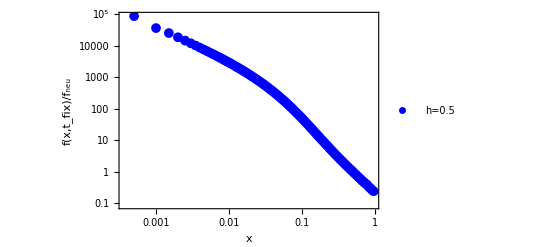

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.5_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1sh5=Transpose@{x11s,x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1sh5,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1sh5,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1sh5},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"h=0.5"},PlotRange->All, PlotMarkers->{"●",10}];

(*Show both plots*)
Show[a1sCombined]
```

```mathematica
Data1sh5
```

```mathematica
Data1sh5={{0.,122.559},{0.0005,88381.9},{0.001,36837.2},{0.0015,25583.7},{0.002,18783.8},{0.0025,14746.7},{0.003,12090.3},{0.0035,10217.4},{0.004,8799.45},{0.0045,7709.49},{0.005,6820.65},{0.0055,6120.11},{0.006,5529.72},{0.0065,5027.42},{0.007,4603.11},{0.0075,4236.81},{0.008,3916.21},{0.0085,3635.91},{0.009,3377.88},{0.0095,3160.61},{0.01,2963.57},{0.0105,2783.02},{0.011,2616.69},{0.0115,2472.9},{0.012,2338.21},{0.0125,2211.98},{0.013,2099.02},{0.0135,1995.67},{0.014,1900.34},{0.0145,1809.14},{0.015,1724.07},{0.0155,1652.7},{0.016,1577.72},{0.0165,1514.42},{0.017,1449.28},{0.0175,1388.08},{0.018,1334.76},{0.0185,1282.64},{0.019,1229.78},{0.0195,1188.76},{0.02,1141.15},{0.0205,1098.19},{0.021,1061.04},{0.0215,1021.48},{0.022,986.946},{0.0225,954.043},{0.023,922.906},{0.0235,889.957},{0.024,860.215},{0.0245,834.135},{0.025,807.45},{0.0255,783.773},{0.026,758.221},{0.0265,735.598},{0.027,716.219},{0.0275,689.672},{0.028,672.893},{0.0285,651.897},{0.029,633.144},{0.0295,617.34},{0.03,597.178},{0.0305,582.199},{0.031,566.025},{0.0315,554.489},{0.032,537.276},{0.0325,523.556},{0.033,510.197},{0.0335,497.332},{0.034,481.698},{0.0345,470.239},{0.035,458.253},{0.0355,446.469},{0.036,435.64},{0.0365,427.516},{0.037,417.017},{0.0375,403.956},{0.038,396.167},{0.0385,383.566},{0.039,379.706},{0.0395,367.746},{0.04,360.851},{0.0405,352.739},{0.041,346.431},{0.0415,336.729},{0.042,329.352},{0.0425,321.508},{0.043,314.221},{0.0435,308.219},{0.044,301.125},{0.0445,296.461},{0.045,288.671},{0.0455,284.012},{0.046,276.729},{0.0465,273.926},{0.047,265.666},{0.0475,261.053},{0.048,255.568},{0.0485,249.43},{0.049,245.252},{0.0495,238.483},{0.05,234.537},{0.0505,232.234},{0.051,226.613},{0.0515,220.357},{0.052,215.732},{0.0525,213.814},{0.053,208.044},{0.0535,204.871},{0.054,200.621},{0.0545,196.609},{0.055,193.862},{0.0555,190.022},{0.056,188.246},{0.0565,185.015},{0.057,179.908},{0.0575,178.276},{0.058,174.929},{0.0585,171.776},{0.059,167.932},{0.0595,164.957},{0.06,162.357},{0.0605,158.911},{0.061,156.573},{0.0615,152.997},{0.062,150.675},{0.0625,149.171},{0.063,145.173},{0.0635,145.163},{0.064,140.301},{0.0645,138.399},{0.065,136.166},{0.0655,134.575},{0.066,132.561},{0.0665,131.299},{0.067,127.81},{0.0675,126.086},{0.068,124.563},{0.0685,121.61},{0.069,120.995},{0.0695,118.074},{0.07,115.892},{0.0705,115.317},{0.071,112.779},{0.0715,111.195},{0.072,109.74},{0.0725,107.478},{0.073,106.142},{0.0735,103.902},{0.074,102.276},{0.0745,100.138},{0.075,100.411},{0.0755,97.2733},{0.076,96.6087},{0.0765,94.4906},{0.077,93.9741},{0.0775,92.2964},{0.078,90.7889},{0.0785,89.5156},{0.079,88.0121},{0.0795,87.3515},{0.08,87.0932},{0.0805,84.7989},{0.081,83.1833},{0.0815,81.7418},{0.082,81.0671},{0.0825,80.4125},{0.083,78.3544},{0.0835,77.6477},{0.084,76.7929},{0.0845,75.4955},{0.085,74.5386},{0.0855,73.924},{0.086,72.5706},{0.0865,72.6087},{0.087,70.8649},{0.0875,69.6157},{0.088,69.1172},{0.0885,68.1342},{0.089,66.3064},{0.0895,66.0641},{0.09,65.8039},{0.0905,64.9991},{0.091,63.7058},{0.0915,63.1292},{0.092,62.5666},{0.0925,61.2453},{0.093,60.4125},{0.0935,60.2663},{0.094,59.0812},{0.0945,57.7678},{0.095,57.0851},{0.0955,57.0091},{0.096,56.3043},{0.0965,55.6277},{0.097,55.1892},{0.0975,53.8559},{0.098,53.3594},{0.0985,52.2303},{0.099,52.6447},{0.0995,51.3734},{0.1,50.5666},{0.1005,50.4805},{0.101,49.4175},{0.1015,48.905},{0.102,48.8369},{0.1025,48.0561},{0.103,47.1312},{0.1035,46.6647},{0.104,46.6987},{0.1045,44.953},{0.105,45.2192},{0.1055,44.4925},{0.106,44.0181},{0.1065,43.8159},{0.107,42.5846},{0.1075,42.4084},{0.108,42.7428},{0.1085,41.6437},{0.109,41.7097},{0.1095,40.3164},{0.11,40.1282},{0.1105,39.5616},{0.111,39.4675},{0.1115,38.939},{0.112,38.5125},{0.1125,38.2122},{0.113,37.5115},{0.1135,36.7468},{0.114,36.8068},{0.1145,36.7528},{0.115,36.3244},{0.1155,35.3354},{0.116,35.6397},{0.1165,34.6127},{0.117,34.6467},{0.1175,34.2723},{0.118,33.896},{0.1185,33.2092},{0.119,32.3464},{0.1195,33.5416},{0.12,32.1862},{0.1205,31.8198},{0.121,31.8559},{0.1215,31.7478},{0.122,31.4815},{0.1225,31.1111},{0.123,29.8479},{0.1235,30.3244},{0.124,30.1021},{0.1245,29.7258},{0.125,29.1091},{0.1255,28.949},{0.126,28.6567},{0.1265,28.3464},{0.127,28.0881},{0.1275,27.7317},{0.128,28.0901},{0.1285,27.2313},{0.129,27.2713},{0.1295,26.5005},{0.13,26.6186},{0.1305,26.3083},{0.131,26.004},{0.1315,25.5436},{0.132,25.1752},{0.1325,25.1572},{0.133,25.1432},{0.1335,24.7788},{0.134,24.6767},{0.1345,24.1742},{0.135,24.0701},{0.1355,23.6957},{0.136,23.1512},{0.1365,23.8939},{0.137,22.959},{0.1375,23.1191},{0.138,22.981},{0.1385,22.8108},{0.139,22.8308},{0.1395,21.7858},{0.14,22.6727},{0.1405,21.8659},{0.141,21.2072},{0.1415,21.7338},{0.142,21.5816},{0.1425,21.4355},{0.143,20.5666},{0.1435,20.2643},{0.144,20.8449},{0.1445,20.3364},{0.145,20.4425},{0.1455,20.3984},{0.146,19.8299},{0.1465,19.6897},{0.147,19.4154},{0.1475,19.5175},{0.148,19.1251},{0.1485,18.9049},{0.149,18.8048},{0.1495,18.6447},{0.15,18.6046},{0.1505,18.5646},{0.151,18.1822},{0.1515,17.3314},{0.152,17.6777},{0.1525,17.5295},{0.153,17.6116},{0.1535,17.5315},{0.154,17.2373},{0.1545,16.8769},{0.155,16.8449},{0.1555,16.8949},{0.156,16.5626},{0.1565,17.2813},{0.157,16.2363},{0.1575,16.3664},{0.158,16.4184},{0.1585,16.6006},{0.159,15.9179},{0.1595,15.8298},{0.16,15.1472},{0.1605,15.2773},{0.161,14.9309},{0.1615,15.1792},{0.162,15.2533},{0.1625,15.2252},{0.163,15.0631},{0.1635,14.7007},{0.164,14.6867},{0.1645,15.007},{0.165,14.8449},{0.1655,14.4825},{0.166,13.942},{0.1665,13.8919},{0.167,14.1101},{0.1675,13.8459},{0.168,13.6196},{0.1685,13.4094},{0.169,13.6176},{0.1695,13.7938},{0.17,13.4955},{0.1705,13.2753},{0.171,13.0951},{0.1715,13.3594},{0.172,13.2993},{0.1725,12.9269},{0.173,12.5866},{0.1735,12.7007},{0.174,12.5546},{0.1745,12.6907},{0.175,12.5406},{0.1755,12.2142},{0.176,12.0721},{0.1765,12.034},{0.177,11.9139},{0.1775,11.978},{0.178,12.1462},{0.1785,11.5876},{0.179,11.8238},{0.1795,11.958},{0.18,11.7798},{0.1805,11.962},{0.181,11.6316},{0.1815,11.3013},{0.182,11.1672},{0.1825,11.3333},{0.183,10.975},{0.1835,10.5446},{0.184,11.0831},{0.1845,10.965},{0.185,10.5446},{0.1855,10.8829},{0.186,10.4825},{0.1865,10.4044},{0.187,10.1281},{0.1875,10.4124},{0.188,9.98199},{0.1885,10.4465},{0.189,10.1682},{0.1895,10.1301},{0.19,10.1101},{0.1905,10.1882},{0.191,10.2643},{0.1915,10.0561},{0.192,9.79379},{0.1925,9.71773},{0.193,9.7918},{0.1935,9.65568},{0.194,9.48149},{0.1945,9.7978},{0.195,9.71773},{0.1955,9.47549},{0.196,9.47749},{0.1965,9.14716},{0.197,9.2913},{0.1975,9.30932},{0.198,8.96697},{0.1985,9.00902},{0.199,8.96297},{0.1995,8.95097},{0.2,8.95097},{0.2005,9.40341},{0.201,8.91893},{0.2015,8.57259},{0.202,8.24626},{0.2025,8.44445},{0.203,8.61262},{0.2035,8.70872},{0.204,8.4945},{0.2045,8.39841},{0.205,8.27228},{0.2055,8.01002},{0.206,8.27027},{0.2065,7.994},{0.207,8.0881},{0.2075,8.10212},{0.208,8.25027},{0.2085,7.63164},{0.209,8.05206},{0.2095,8.36437},{0.21,7.96597},{0.2105,7.80381},{0.211,7.60161},{0.2115,7.2953},{0.212,7.41542},{0.2125,7.67368},{0.213,7.82984},{0.2135,7.73574},{0.214,7.51353},{0.2145,7.37338},{0.215,7.33134},{0.2155,7.50551},{0.216,7.16717},{0.2165,7.24525},{0.217,7.31732},{0.2175,7.24525},{0.218,7.11512},{0.2185,7.01302},{0.219,7.04506},{0.2195,7.05507},{0.22,6.995},{0.2205,7.10312},{0.221,6.85486},{0.2215,6.92293},{0.222,6.65866},{0.2225,6.95297},{0.223,6.87688},{0.2235,6.78079},{0.224,6.63664},{0.2245,6.47448},{0.225,6.5986},{0.2255,6.79481},{0.226,6.52253},{0.2265,6.58058},{0.227,6.73874},{0.2275,6.60461},{0.228,6.34235},{0.2285,6.42843},{0.229,6.31632},{0.2295,6.32833},{0.23,6.13013},{0.2305,6.2843},{0.231,6.34435},{0.2315,6.26026},{0.232,6.28429},{0.2325,6.20221},{0.233,6.02603},{0.2335,5.8959},{0.234,5.8899},{0.2345,5.87989},{0.235,5.93594},{0.2355,5.98601},{0.236,5.76177},{0.2365,5.90191},{0.237,5.73574},{0.2375,5.72573},{0.238,5.95396},{0.2385,5.51753},{0.239,5.85987},{0.2395,5.4915},{0.24,5.48349},{0.2405,5.48148},{0.241,5.80382},{0.2415,5.58359},{0.242,5.46147},{0.2425,5.47147},{0.243,5.42343},{0.2435,5.25326},{0.244,5.64365},{0.2445,5.43144},{0.245,5.3954},{0.2455,5.4935},{0.246,5.1892},{0.2465,5.44545},{0.247,5.11112},{0.2475,5.21122},{0.248,5.33534},{0.2485,5.28329},{0.249,5.02303},{0.2495,5.21121},{0.25,5.27328},{0.2505,4.94295},{0.251,5.01703},{0.2515,4.93294},{0.252,4.99901},{0.2525,4.97097},{0.253,4.97898},{0.2535,4.80881},{0.254,4.82483},{0.2545,4.5025},{0.255,4.85485},{0.2555,4.91692},{0.256,4.73073},{0.2565,4.60862},{0.257,4.86087},{0.2575,4.76277},{0.258,4.73274},{0.2585,4.3924},{0.259,4.62063},{0.2595,4.63064},{0.26,4.65466},{0.2605,4.53654},{0.261,4.56657},{0.2615,4.64665},{0.262,4.41242},{0.2625,4.40841},{0.263,4.61862},{0.2635,4.42043},{0.264,4.43243},{0.2645,4.34835},{0.265,4.57258},{0.2655,4.3964},{0.266,4.24425},{0.2665,4.35836},{0.267,4.18419},{0.2675,4.30631},{0.268,4.42042},{0.2685,4.28229},{0.269,4.0921},{0.2695,4.27028},{0.27,4.22423},{0.2705,4.25026},{0.271,4.2983},{0.2715,4.26427},{0.272,4.28429},{0.2725,4.13414},{0.273,4.22223},{0.2735,4.04204},{0.274,3.996},{0.2745,4.11012},{0.275,3.95996},{0.2755,4.13614},{0.276,4.06206},{0.2765,4.26828},{0.277,3.87387},{0.2775,3.86187},{0.278,3.93594},{0.2785,3.81382},{0.279,3.93794},{0.2795,3.89991},{0.28,3.77377},{0.2805,3.70772},{0.281,3.85986},{0.2815,3.8018},{0.282,3.69971},{0.2825,3.68569},{0.283,3.76777},{0.2835,3.90192},{0.284,3.71372},{0.2845,3.65366},{0.285,3.81382},{0.2855,3.60361},{0.286,3.45746},{0.2865,3.47148},{0.287,3.55355},{0.2875,3.50951},{0.288,3.5876},{0.2885,3.63764},{0.289,3.56957},{0.2895,3.48348},{0.29,3.48549},{0.2905,3.62563},{0.291,3.57758},{0.2915,3.4975},{0.292,3.42943},{0.2925,3.35736},{0.293,3.35536},{0.2935,3.57958},{0.294,3.43344},{0.2945,3.32333},{0.295,3.44945},{0.2955,3.50951},{0.296,3.44344},{0.2965,3.33134},{0.297,3.24725},{0.2975,3.26527},{0.298,3.28128},{0.2985,3.31132},{0.299,3.30531},{0.2995,3.36337},{0.3,3.16917},{0.3005,3.33134},{0.301,3.36938},{0.3015,3.21922},{0.302,3.1952},{0.3025,3.0911},{0.303,3.24925},{0.3035,3.25926},{0.304,3.28329},{0.3045,3.1992},{0.305,3.05105},{0.3055,3.15516},{0.306,3.16917},{0.3065,3.31532},{0.307,3.12513},{0.3075,2.93093},{0.308,2.96897},{0.3085,2.98699},{0.309,2.999},{0.3095,3.01102},{0.31,2.87488},{0.3105,2.96697},{0.311,3.15716},{0.3115,2.85085},{0.312,2.95495},{0.3125,3.001},{0.313,2.92092},{0.3135,2.97698},{0.314,2.93293},{0.3145,2.81081},{0.315,2.78479},{0.3155,2.95295},{0.316,2.78479},{0.3165,2.80281},{0.317,3.0991},{0.3175,2.95696},{0.318,2.8949},{0.3185,2.61662},{0.319,2.86086},{0.3195,2.80481},{0.32,2.7888},{0.3205,2.80081},{0.321,2.79479},{0.3215,2.67067},{0.322,2.86687},{0.3225,2.85285},{0.323,2.81281},{0.3235,2.66466},{0.324,2.81882},{0.3245,2.75075},{0.325,2.73874},{0.3255,2.5986},{0.326,2.60661},{0.3265,2.70271},{0.327,2.65065},{0.3275,2.5986},{0.328,2.55856},{0.3285,2.7007},{0.329,2.48448},{0.3295,2.65866},{0.33,2.58459},{0.3305,2.51652},{0.331,2.46847},{0.3315,2.66066},{0.332,2.65265},{0.3325,2.65465},{0.333,2.71071},{0.3335,2.63464},{0.334,2.54655},{0.3345,2.4945},{0.335,2.5045},{0.3355,2.47648},{0.336,2.46446},{0.3365,2.45245},{0.337,2.42043},{0.3375,2.41041},{0.338,2.58459},{0.3385,2.37638},{0.339,2.40841},{0.3395,2.54254},{0.34,2.36837},{0.3405,2.51452},{0.341,2.28428},{0.3415,2.37037},{0.342,2.51852},{0.3425,2.38438},{0.343,2.43443},{0.3435,2.43644},{0.344,2.31031},{0.3445,2.3964},{0.345,2.37238},{0.3455,2.31832},{0.346,2.36637},{0.3465,2.36237},{0.347,2.26427},{0.3475,2.31231},{0.348,2.22823},{0.3485,2.2963},{0.349,2.17618},{0.3495,2.25426},{0.35,2.29429},{0.3505,2.20621},{0.351,2.25826},{0.3515,2.34635},{0.352,2.11812},{0.3525,2.20821},{0.353,2.25826},{0.3535,2.27027},{0.354,2.25025},{0.3545,2.3003},{0.355,2.38839},{0.3555,2.12813},{0.356,2.33233},{0.3565,2.28028},{0.357,2.26026},{0.3575,2.22223},{0.358,2.24825},{0.3585,2.33834},{0.359,2.06006},{0.3595,2.18018},{0.36,2.25626},{0.3605,2.20421},{0.361,2.08209},{0.3615,2.06807},{0.362,2.19219},{0.3625,1.9019},{0.363,2.0981},{0.3635,2.12013},{0.364,2.0981},{0.3645,1.95596},{0.365,1.91993},{0.3655,2.12813},{0.366,2.10811},{0.3665,2.02603},{0.367,2.11812},{0.3675,2.10411},{0.368,1.94395},{0.3685,2.08208},{0.369,2.24024},{0.3695,1.996},{0.37,2.04605},{0.3705,1.82583},{0.371,1.86787},{0.3715,1.95195},{0.372,1.94795},{0.3725,1.92393},{0.373,1.86186},{0.3735,1.96797},{0.374,2.01602},{0.3745,1.98398},{0.375,2.07008},{0.3755,1.87988},{0.376,1.90591},{0.3765,1.88589},{0.377,1.94595},{0.3775,1.76777},{0.378,1.86387},{0.3785,1.81182},{0.379,1.8999},{0.3795,1.82583},{0.38,1.88989},{0.3805,1.97197},{0.381,1.86186},{0.3815,1.92392},{0.382,1.91391},{0.3825,1.84184},{0.383,1.93994},{0.3835,1.78979},{0.384,1.71772},{0.3845,1.92392},{0.385,1.71973},{0.3855,1.85186},{0.386,1.76777},{0.3865,1.87588},{0.387,1.6937},{0.3875,1.77377},{0.388,1.78379},{0.3885,1.71371},{0.389,1.78579},{0.3895,1.81182},{0.39,1.82583},{0.3905,1.80381},{0.391,1.72773},{0.3915,1.70771},{0.392,1.68569},{0.3925,1.6937},{0.393,1.68368},{0.3935,1.64565},{0.394,1.7017},{0.3945,1.74575},{0.395,1.73774},{0.3955,1.73974},{0.396,1.7017},{0.3965,1.71572},{0.397,1.6036},{0.3975,1.74975},{0.398,1.62963},{0.3985,1.72172},{0.399,1.70771},{0.3995,1.70971},{0.4,1.54955},{0.4005,1.68569},{0.401,1.77978},{0.4015,1.67368},{0.402,1.72372},{0.4025,1.57558},{0.403,1.62563},{0.4035,1.64965},{0.404,1.57758},{0.4045,1.67968},{0.405,1.65165},{0.4055,1.61962},{0.406,1.54155},{0.4065,1.66567},{0.407,1.65966},{0.4075,1.57558},{0.408,1.60761},{0.4085,1.57958},{0.409,1.55956},{0.4095,1.58759},{0.41,1.66367},{0.4105,1.60761},{0.411,1.48348},{0.4115,1.69169},{0.412,1.53954},{0.4125,1.56357},{0.413,1.65165},{0.4135,1.59159},{0.414,1.65966},{0.4145,1.55356},{0.415,1.47548},{0.4155,1.52553},{0.416,1.53153},{0.4165,1.56356},{0.417,1.43944},{0.4175,1.48549},{0.418,1.47147},{0.4185,1.54955},{0.419,1.4955},{0.4195,1.48148},{0.42,1.42743},{0.4205,1.42143},{0.421,1.37137},{0.4215,1.52753},{0.422,1.44545},{0.4225,1.38739},{0.423,1.51752},{0.4235,1.47548},{0.424,1.35135},{0.4245,1.51151},{0.425,1.3954},{0.4255,1.55155},{0.426,1.40541},{0.4265,1.32132},{0.427,1.38539},{0.4275,1.53554},{0.428,1.41542},{0.4285,1.58158},{0.429,1.48749},{0.4295,1.52152},{0.43,1.36937},{0.4305,1.35335},{0.431,1.43344},{0.4315,1.3974},{0.432,1.49149},{0.4325,1.44946},{0.433,1.36737},{0.4335,1.37738},{0.434,1.33133},{0.4345,1.37938},{0.435,1.39139},{0.4355,1.43944},{0.436,1.26927},{0.4365,1.32733},{0.437,1.40741},{0.4375,1.37137},{0.438,1.34334},{0.4385,1.31932},{0.439,1.33334},{0.4395,1.38339},{0.44,1.41542},{0.4405,1.35736},{0.441,1.2973},{0.4415,1.27327},{0.442,1.35936},{0.4425,1.33934},{0.443,1.38939},{0.4435,1.38339},{0.444,1.37738},{0.4445,1.31532},{0.445,1.22523},{0.4455,1.32533},{0.446,1.30331},{0.4465,1.41341},{0.447,1.24525},{0.4475,1.32132},{0.448,1.35736},{0.4485,1.28128},{0.449,1.32733},{0.4495,1.30931},{0.45,1.21121},{0.4505,1.26327},{0.451,1.1932},{0.4515,1.22523},{0.452,1.27528},{0.4525,1.22723},{0.453,1.21322},{0.4535,1.23323},{0.454,1.25526},{0.4545,1.22723},{0.455,1.23724},{0.4555,1.25926},{0.456,1.18719},{0.4565,1.18519},{0.457,1.32132},{0.4575,1.27327},{0.458,1.21922},{0.4585,1.26527},{0.459,1.23123},{0.4595,1.11512},{0.46,1.25325},{0.4605,1.18919},{0.461,1.21121},{0.4615,1.27728},{0.462,1.10311},{0.4625,1.26527},{0.463,1.25325},{0.4635,1.20521},{0.464,1.22122},{0.4645,1.28929},{0.465,1.21321},{0.4655,1.23323},{0.466,1.16517},{0.4665,1.1952},{0.467,1.23724},{0.4675,1.21922},{0.468,1.12513},{0.4685,1.17317},{0.469,1.04304},{0.4695,1.07307},{0.47,1.17718},{0.4705,1.13313},{0.471,1.13113},{0.4715,1.17718},{0.472,1.18719},{0.4725,1.23924},{0.473,1.10711},{0.4735,1.12313},{0.474,1.18719},{0.4745,1.07307},{0.475,1.16116},{0.4755,1.1011},{0.476,1.16317},{0.4765,1.14915},{0.477,1.11912},{0.4775,1.04705},{0.478,1.13514},{0.4785,1.21522},{0.479,1.04905},{0.4795,1.08108},{0.48,1.11512},{0.4805,1.08709},{0.481,1.0991},{0.4815,1.0991},{0.482,1.08709},{0.4825,1.00501},{0.483,1.08108},{0.4835,1.04505},{0.484,1.17918},{0.4845,1.05506},{0.485,1.07508},{0.4855,1.03104},{0.486,1.08709},{0.4865,1.03704},{0.487,1.10911},{0.4875,0.986987},{0.488,1.00501},{0.4885,1.05706},{0.489,1.10711},{0.4895,1.02703},{0.49,1.07107},{0.4905,1.07307},{0.491,1.03904},{0.4915,1.03304},{0.492,1.05706},{0.4925,0.946951},{0.493,1.02703},{0.4935,1.10311},{0.494,1.09309},{0.4945,0.984987},{0.495,1.01101},{0.4955,1.003},{0.496,1.01101},{0.4965,1.04705},{0.497,0.902903},{0.4975,0.912913},{0.498,1.01502},{0.4985,0.978979},{0.499,1.05105},{0.4995,1.03504},{0.5,1.92393},{0.5005,0.004004},{0.501,2.14014},{0.5015,0.004004},{0.502,2.14414},{0.5025,0.00600601},{0.503,2.03003},{0.5035,0},{0.504,2.06206},{0.5045,0},{0.505,1.93994},{0.5055,0},{0.506,1.89189},{0.5065,0.004004},{0.507,1.97198},{0.5075,0},{0.508,2.02603},{0.5085,0.002002},{0.509,1.91792},{0.5095,0},{0.51,2.00801},{0.5105,0},{0.511,1.93393},{0.5115,0},{0.512,1.003},{0.5125,0.956959},{0.513,0.884885},{0.5135,1.01301},{0.514,1.04705},{0.5145,0.870871},{0.515,0.916917},{0.5155,1.02903},{0.516,0.930931},{0.5165,1.02303},{0.517,0.942943},{0.5175,0.928931},{0.518,0.912913},{0.5185,0.930931},{0.519,0.940943},{0.5195,0.864867},{0.52,0.938939},{0.5205,0.902903},{0.521,0.884885},{0.5215,0.910911},{0.522,0.848851},{0.5225,0.914915},{0.523,0.970973},{0.5235,0.958959},{0.524,0.970971},{0.5245,0.888893},{0.525,0.942945},{0.5255,0.940941},{0.526,0.906907},{0.5265,0.908911},{0.527,0.900903},{0.5275,0.864865},{0.528,0.876877},{0.5285,0.904905},{0.529,0.930933},{0.5295,0.878883},{0.53,0.894895},{0.5305,0.872873},{0.531,0.932933},{0.5315,0.958959},{0.532,0.866867},{0.5325,0.902903},{0.533,0.936937},{0.5335,0.834837},{0.534,0.856859},{0.5345,0.978985},{0.535,0.974975},{0.5355,0.870871},{0.536,0.826827},{0.5365,0.906907},{0.537,0.832837},{0.5375,0.854855},{0.538,0.836837},{0.5385,0.906909},{0.539,0.884885},{0.5395,0.898899},{0.54,0.860863},{0.5405,0.796797},{0.541,0.960963},{0.5415,0.882885},{0.542,0.830833},{0.5425,0.838839},{0.543,0.834837},{0.5435,0.848849},{0.544,0.854855},{0.5445,0.858861},{0.545,0.848851},{0.5455,0.790791},{0.546,0.846849},{0.5465,0.772773},{0.547,0.806807},{0.5475,0.824825},{0.548,0.854855},{0.5485,0.784789},{0.549,0.758759},{0.5495,0.798799},{0.55,0.832835},{0.5505,0.872873},{0.551,0.766767},{0.5515,0.822827},{0.552,0.870871},{0.5525,0.828831},{0.553,0.802803},{0.5535,0.826827},{0.554,0.742743},{0.5545,0.816821},{0.555,0.836837},{0.5555,0.800801},{0.556,0.752753},{0.5565,0.818821},{0.557,0.680681},{0.5575,0.772775},{0.558,0.894895},{0.5585,0.718719},{0.559,0.838839},{0.5595,0.808809},{0.56,0.844847},{0.5605,0.808809},{0.561,0.782783},{0.5615,0.786789},{0.562,0.804805},{0.5625,0.740741},{0.563,0.742743},{0.5635,0.786787},{0.564,0.744745},{0.5645,0.814815},{0.565,0.762767},{0.5655,0.834839},{0.566,0.788789},{0.5665,0.778779},{0.567,0.770773},{0.5675,0.768769},{0.568,0.678681},{0.5685,0.762765},{0.569,0.770771},{0.5695,0.760761},{0.57,0.762765},{0.5705,0.734741},{0.571,0.658663},{0.5715,0.750753},{0.572,0.746751},{0.5725,0.736739},{0.573,0.680681},{0.5735,0.732733},{0.574,0.732733},{0.5745,0.698699},{0.575,0.682683},{0.5755,0.730731},{0.576,0.704705},{0.5765,0.760763},{0.577,0.752753},{0.5775,0.736739},{0.578,0.678679},{0.5785,0.786787},{0.579,0.812813},{0.5795,0.720723},{0.58,0.754755},{0.5805,0.660663},{0.581,0.840841},{0.5815,0.752755},{0.582,0.766767},{0.5825,0.778779},{0.583,0.752753},{0.5835,0.708709},{0.584,0.716717},{0.5845,0.710713},{0.585,0.646647},{0.5855,0.690691},{0.586,0.664665},{0.5865,0.734735},{0.587,0.724725},{0.5875,0.682685},{0.588,0.726727},{0.5885,0.692693},{0.589,0.748749},{0.5895,0.700703},{0.59,0.580583},{0.5905,0.698701},{0.591,0.712713},{0.5915,0.720721},{0.592,0.718721},{0.5925,0.710713},{0.593,0.770771},{0.5935,0.738739},{0.594,0.700703},{0.5945,0.646647},{0.595,0.702705},{0.5955,0.736739},{0.596,0.776777},{0.5965,0.706707},{0.597,0.602603},{0.5975,0.588589},{0.598,0.704705},{0.5985,0.696697},{0.599,0.746747},{0.5995,0.646649},{0.6,0.632633},{0.6005,0.648649},{0.601,0.654657},{0.6015,0.644645},{0.602,0.598599},{0.6025,0.684685},{0.603,0.690693},{0.6035,0.668669},{0.604,0.640641},{0.6045,0.682683},{0.605,0.754755},{0.6055,0.690691},{0.606,0.682683},{0.6065,0.632633},{0.607,0.674679},{0.6075,0.594595},{0.608,0.610611},{0.6085,0.710711},{0.609,0.650653},{0.6095,0.796797},{0.61,0.594595},{0.6105,0.692693},{0.611,0.630633},{0.6115,0.658661},{0.612,0.688689},{0.6125,0.640641},{0.613,0.652653},{0.6135,0.660663},{0.614,0.574575},{0.6145,0.654655},{0.615,0.612615},{0.6155,0.638647},{0.616,0.590591},{0.6165,0.634635},{0.617,0.602603},{0.6175,0.626627},{0.618,0.610613},{0.6185,0.620621},{0.619,0.600601},{0.6195,0.584585},{0.62,0.606607},{0.6205,0.612613},{0.621,0.594595},{0.6215,0.702705},{0.622,0.636637},{0.6225,0.634635},{0.623,0.616621},{0.6235,0.580581},{0.624,0.618621},{0.6245,0.560565},{0.625,0.584585},{0.6255,0.624625},{0.626,0.658659},{0.6265,0.644647},{0.627,0.626627},{0.6275,0.610611},{0.628,0.588589},{0.6285,0.614615},{0.629,0.550551},{0.6295,0.542543},{0.63,0.628629},{0.6305,0.628629},{0.631,0.590591},{0.6315,0.564565},{0.632,0.584587},{0.6325,0.552553},{0.633,0.584585},{0.6335,0.648649},{0.634,0.594595},{0.6345,0.672675},{0.635,0.586587},{0.6355,0.542543},{0.636,0.578579},{0.6365,0.658659},{0.637,0.616619},{0.6375,0.716721},{0.638,0.538539},{0.6385,0.634635},{0.639,0.558559},{0.6395,0.650659},{0.64,0.666667},{0.6405,0.602605},{0.641,0.644649},{0.6415,0.610611},{0.642,0.546549},{0.6425,0.528529},{0.643,0.634635},{0.6435,0.604605},{0.644,0.516517},{0.6445,0.536537},{0.645,0.554555},{0.6455,0.590593},{0.646,0.544545},{0.6465,0.588589},{0.647,0.522523},{0.6475,0.558559},{0.648,0.508511},{0.6485,0.632633},{0.649,0.584585},{0.6495,0.540545},{0.65,0.632633},{0.6505,0.542543},{0.651,0.554555},{0.6515,0.630631},{0.652,0.514515},{0.6525,0.574575},{0.653,0.572573},{0.6535,0.596597},{0.654,0.578579},{0.6545,0.558559},{0.655,0.564571},{0.6555,0.566567},{0.656,0.578579},{0.6565,0.562563},{0.657,0.518519},{0.6575,0.528531},{0.658,0.522525},{0.6585,0.576577},{0.659,0.534535},{0.6595,0.536537},{0.66,0.530539},{0.6605,0.524525},{0.661,0.560561},{0.6615,0.512515},{0.662,0.478478},{0.6625,0.472474},{0.663,0.530531},{0.6635,0.586589},{0.664,0.600605},{0.6645,0.562563},{0.665,0.526527},{0.6655,0.510511},{0.666,0.534537},{0.6665,0.504505},{0.667,0.610611},{0.6675,0.484486},{0.668,0.540545},{0.6685,0.486486},{0.669,0.582583},{0.6695,0.556559},{0.67,0.534535},{0.6705,0.478478},{0.671,0.49049},{0.6715,0.448448},{0.672,0.542543},{0.6725,0.538539},{0.673,0.496496},{0.6735,0.508513},{0.674,0.488488},{0.6745,0.518519},{0.675,0.556557},{0.6755,0.522525},{0.676,0.518519},{0.6765,0.516519},{0.677,0.522523},{0.6775,0.512513},{0.678,0.500501},{0.6785,0.502503},{0.679,0.486488},{0.6795,0.550551},{0.68,0.502503},{0.6805,0.516517},{0.681,0.506511},{0.6815,0.512515},{0.682,0.496496},{0.6825,0.500503},{0.683,0.518519},{0.6835,0.476476},{0.684,0.492492},{0.6845,0.568571},{0.685,0.468468},{0.6855,0.49049},{0.686,0.564567},{0.6865,0.472472},{0.687,0.514515},{0.6875,0.514515},{0.688,0.514515},{0.6885,0.47047},{0.689,0.548549},{0.6895,0.47047},{0.69,0.540543},{0.6905,0.462462},{0.691,0.542543},{0.6915,0.45846},{0.692,0.518519},{0.6925,0.542543},{0.693,0.492492},{0.6935,0.508509},{0.694,0.466466},{0.6945,0.45846},{0.695,0.516517},{0.6955,0.522525},{0.696,0.476476},{0.6965,0.464464},{0.697,0.506507},{0.6975,0.530531},{0.698,0.518519},{0.6985,0.392394},{0.699,0.396396},{0.6995,0.456456},{0.7,0.49049},{0.7005,0.448448},{0.701,0.498498},{0.7015,0.456456},{0.702,0.4004},{0.7025,0.44044},{0.703,0.45045},{0.7035,0.488488},{0.704,0.49049},{0.7045,0.520523},{0.705,0.518519},{0.7055,0.492492},{0.706,0.482482},{0.7065,0.442442},{0.707,0.426426},{0.7075,0.532533},{0.708,0.518519},{0.7085,0.484484},{0.709,0.46046},{0.7095,0.502503},{0.71,0.48048},{0.7105,0.506507},{0.711,0.466466},{0.7115,0.496496},{0.712,0.476476},{0.7125,0.510511},{0.713,0.448448},{0.7135,0.478478},{0.714,0.564565},{0.7145,0.480482},{0.715,0.478478},{0.7155,0.508509},{0.716,0.526529},{0.7165,0.48649},{0.717,0.406406},{0.7175,0.404404},{0.718,0.482484},{0.7185,0.448448},{0.719,0.416416},{0.7195,0.428428},{0.72,0.456456},{0.7205,0.408408},{0.721,0.424424},{0.7215,0.406406},{0.722,0.472476},{0.7225,0.444444},{0.723,0.438438},{0.7235,0.420422},{0.724,0.46046},{0.7245,0.416416},{0.725,0.426426},{0.7255,0.398398},{0.726,0.424426},{0.7265,0.438438},{0.727,0.426426},{0.7275,0.432432},{0.728,0.434434},{0.7285,0.452452},{0.729,0.414414},{0.7295,0.484486},{0.73,0.442442},{0.7305,0.434434},{0.731,0.454454},{0.7315,0.454454},{0.732,0.466466},{0.7325,0.39039},{0.733,0.45846},{0.7335,0.38038},{0.734,0.452452},{0.7345,0.430434},{0.735,0.406406},{0.7355,0.444444},{0.736,0.448448},{0.7365,0.428428},{0.737,0.374376},{0.7375,0.364364},{0.738,0.432432},{0.7385,0.398398},{0.739,0.3984},{0.7395,0.406406},{0.74,0.394394},{0.7405,0.43043},{0.741,0.446446},{0.7415,0.386386},{0.742,0.516517},{0.7425,0.436436},{0.743,0.422422},{0.7435,0.41041},{0.744,0.464464},{0.7445,0.394394},{0.745,0.414416},{0.7455,0.47047},{0.746,0.376376},{0.7465,0.442444},{0.747,0.402402},{0.7475,0.36036},{0.748,0.458458},{0.7485,0.388388},{0.749,0.452456},{0.7495,0.458458},{0.75,0.448448},{0.7505,0.424424},{0.751,0.414414},{0.7515,0.412412},{0.752,0.432432},{0.7525,0.434434},{0.753,0.402404},{0.7535,0.432432},{0.754,0.404404},{0.7545,0.456456},{0.755,0.378382},{0.7555,0.382382},{0.756,0.386386},{0.7565,0.416416},{0.757,0.414414},{0.7575,0.386386},{0.758,0.426426},{0.7585,0.402402},{0.759,0.36036},{0.7595,0.408408},{0.76,0.398398},{0.7605,0.452452},{0.761,0.412412},{0.7615,0.370372},{0.762,0.414418},{0.7625,0.448448},{0.763,0.420422},{0.7635,0.362362},{0.764,0.420422},{0.7645,0.428428},{0.765,0.44044},{0.7655,0.43043},{0.766,0.43043},{0.7665,0.416416},{0.767,0.412412},{0.7675,0.436438},{0.768,0.436438},{0.7685,0.444444},{0.769,0.386386},{0.7695,0.402402},{0.77,0.392392},{0.7705,0.450454},{0.771,0.438438},{0.7715,0.370372},{0.772,0.39039},{0.7725,0.384384},{0.773,0.458458},{0.7735,0.446446},{0.774,0.39039},{0.7745,0.41842},{0.775,0.42843},{0.7755,0.386386},{0.776,0.464464},{0.7765,0.378378},{0.777,0.424424},{0.7775,0.426426},{0.778,0.376376},{0.7785,0.322322},{0.779,0.358358},{0.7795,0.362362},{0.78,0.408408},{0.7805,0.402402},{0.781,0.34034},{0.7815,0.358358},{0.782,0.444448},{0.7825,0.42042},{0.783,0.326326},{0.7835,0.348348},{0.784,0.362362},{0.7845,0.362362},{0.785,0.396396},{0.7855,0.384384},{0.786,0.386388},{0.7865,0.36036},{0.787,0.386388},{0.7875,0.338338},{0.788,0.414416},{0.7885,0.374374},{0.789,0.378378},{0.7895,0.322322},{0.79,0.418418},{0.7905,0.344344},{0.791,0.428428},{0.7915,0.382384},{0.792,0.322322},{0.7925,0.396396},{0.793,0.4004},{0.7935,0.372372},{0.794,0.418418},{0.7945,0.358358},{0.795,0.43844},{0.7955,0.426426},{0.796,0.404404},{0.7965,0.326328},{0.797,0.37037},{0.7975,0.350352},{0.798,0.39039},{0.7985,0.408408},{0.799,0.422422},{0.7995,0.36036},{0.8,0.362362},{0.8005,0.342342},{0.801,0.392392},{0.8015,0.404404},{0.802,0.366366},{0.8025,0.384384},{0.803,0.386388},{0.8035,0.376376},{0.804,0.382382},{0.8045,0.418418},{0.805,0.338338},{0.8055,0.382382},{0.806,0.372372},{0.8065,0.312312},{0.807,0.388388},{0.8075,0.392392},{0.808,0.356358},{0.8085,0.394394},{0.809,0.364364},{0.8095,0.312312},{0.81,0.42042},{0.8105,0.36036},{0.811,0.398398},{0.8115,0.366366},{0.812,0.414416},{0.8125,0.352352},{0.813,0.332334},{0.8135,0.35035},{0.814,0.336336},{0.8145,0.38038},{0.815,0.304304},{0.8155,0.31031},{0.816,0.324324},{0.8165,0.288288},{0.817,0.296296},{0.8175,0.326326},{0.818,0.34034},{0.8185,0.292292},{0.819,0.366366},{0.8195,0.274276},{0.82,0.354354},{0.8205,0.36036},{0.821,0.348348},{0.8215,0.318318},{0.822,0.404404},{0.8225,0.336336},{0.823,0.324324},{0.8235,0.36036},{0.824,0.332332},{0.8245,0.352352},{0.825,0.34835},{0.8255,0.33033},{0.826,0.406406},{0.8265,0.406406},{0.827,0.344344},{0.8275,0.342342},{0.828,0.36036},{0.8285,0.286286},{0.829,0.292296},{0.8295,0.362364},{0.83,0.282282},{0.8305,0.352352},{0.831,0.374374},{0.8315,0.344344},{0.832,0.306306},{0.8325,0.31031},{0.833,0.312312},{0.8335,0.348348},{0.834,0.312318},{0.8345,0.314314},{0.835,0.382388},{0.8355,0.364364},{0.836,0.342342},{0.8365,0.332336},{0.837,0.310312},{0.8375,0.302302},{0.838,0.34034},{0.8385,0.288288},{0.839,0.338338},{0.8395,0.314314},{0.84,0.306306},{0.8405,0.308308},{0.841,0.358358},{0.8415,0.358358},{0.842,0.3003},{0.8425,0.31031},{0.843,0.286286},{0.8435,0.314314},{0.844,0.316316},{0.8445,0.296296},{0.845,0.284284},{0.8455,0.314314},{0.846,0.324324},{0.8465,0.3003},{0.847,0.322322},{0.8475,0.292292},{0.848,0.302302},{0.8485,0.278278},{0.849,0.326326},{0.8495,0.294294},{0.85,0.344346},{0.8505,0.324324},{0.851,0.252252},{0.8515,0.336336},{0.852,0.354354},{0.8525,0.314316},{0.853,0.292292},{0.8535,0.298298},{0.854,0.334334},{0.8545,0.306306},{0.855,0.348348},{0.8555,0.300302},{0.856,0.344344},{0.8565,0.342342},{0.857,0.318318},{0.8575,0.292292},{0.858,0.344344},{0.8585,0.282282},{0.859,0.332332},{0.8595,0.296296},{0.86,0.272272},{0.8605,0.254254},{0.861,0.316316},{0.8615,0.374374},{0.862,0.296296},{0.8625,0.292292},{0.863,0.278278},{0.8635,0.324324},{0.864,0.294294},{0.8645,0.308308},{0.865,0.272272},{0.8655,0.278278},{0.866,0.334334},{0.8665,0.306306},{0.867,0.28028},{0.8675,0.276276},{0.868,0.27027},{0.8685,0.292292},{0.869,0.286286},{0.8695,0.32032},{0.87,0.314314},{0.8705,0.32032},{0.871,0.298298},{0.8715,0.314316},{0.872,0.326326},{0.8725,0.292296},{0.873,0.282282},{0.8735,0.286288},{0.874,0.34034},{0.8745,0.318318},{0.875,0.284284},{0.8755,0.354354},{0.876,0.30831},{0.8765,0.286286},{0.877,0.334334},{0.8775,0.264264},{0.878,0.332332},{0.8785,0.308308},{0.879,0.282282},{0.8795,0.304304},{0.88,0.304304},{0.8805,0.302302},{0.881,0.24024},{0.8815,0.254254},{0.882,0.282284},{0.8825,0.27027},{0.883,0.326326},{0.8835,0.304304},{0.884,0.26026},{0.8845,0.256256},{0.885,0.316316},{0.8855,0.304304},{0.886,0.296296},{0.8865,0.296296},{0.887,0.282282},{0.8875,0.298298},{0.888,0.296296},{0.8885,0.262262},{0.889,0.274274},{0.8895,0.258258},{0.89,0.308308},{0.8905,0.328328},{0.891,0.324324},{0.8915,0.304306},{0.892,0.346346},{0.8925,0.286286},{0.893,0.268268},{0.8935,0.284284},{0.894,0.282282},{0.8945,0.226226},{0.895,0.296296},{0.8955,0.274274},{0.896,0.284284},{0.8965,0.27027},{0.897,0.28028},{0.8975,0.322322},{0.898,0.288288},{0.8985,0.292292},{0.899,0.272272},{0.8995,0.284284},{0.9,0.304304},{0.9005,0.276276},{0.901,0.28028},{0.9015,0.264264},{0.902,0.272272},{0.9025,0.282282},{0.903,0.276276},{0.9035,0.262262},{0.904,0.238238},{0.9045,0.302302},{0.905,0.228228},{0.9055,0.26026},{0.906,0.284284},{0.9065,0.324324},{0.907,0.316316},{0.9075,0.244244},{0.908,0.318318},{0.9085,0.306306},{0.909,0.266266},{0.9095,0.28028},{0.91,0.262262},{0.9105,0.282282},{0.911,0.276276},{0.9115,0.312312},{0.912,0.23023},{0.9125,0.274274},{0.913,0.284284},{0.9135,0.270274},{0.914,0.238238},{0.9145,0.266266},{0.915,0.316316},{0.9155,0.294294},{0.916,0.286286},{0.9165,0.278282},{0.917,0.26026},{0.9175,0.258258},{0.918,0.25025},{0.9185,0.33834},{0.919,0.278278},{0.9195,0.238238},{0.92,0.254254},{0.9205,0.286286},{0.921,0.208208},{0.9215,0.254254},{0.922,0.27027},{0.9225,0.286286},{0.923,0.304304},{0.9235,0.292292},{0.924,0.306306},{0.9245,0.24024},{0.925,0.278278},{0.9255,0.214214},{0.926,0.3003},{0.9265,0.26827},{0.927,0.270272},{0.9275,0.22022},{0.928,0.214214},{0.9285,0.248248},{0.929,0.24024},{0.9295,0.252252},{0.93,0.28829},{0.9305,0.232234},{0.931,0.234234},{0.9315,0.256256},{0.932,0.266266},{0.9325,0.24024},{0.933,0.254254},{0.9335,0.246246},{0.934,0.274274},{0.9345,0.28829},{0.935,0.234234},{0.9355,0.244244},{0.936,0.214214},{0.9365,0.274274},{0.937,0.202204},{0.9375,0.244244},{0.938,0.272272},{0.9385,0.244246},{0.939,0.262262},{0.9395,0.268268},{0.94,0.236236},{0.9405,0.246246},{0.941,0.256256},{0.9415,0.272272},{0.942,0.256256},{0.9425,0.23023},{0.943,0.248248},{0.9435,0.288288},{0.944,0.242242},{0.9445,0.202202},{0.945,0.258258},{0.9455,0.24024},{0.946,0.218218},{0.9465,0.222222},{0.947,0.224224},{0.9475,0.244244},{0.948,0.266266},{0.9485,0.286286},{0.949,0.22022},{0.9495,0.25025},{0.95,0.248248},{0.9505,0.216216},{0.951,0.282282},{0.9515,0.222222},{0.952,0.282284},{0.9525,0.222224},{0.953,0.256256},{0.9535,0.26026},{0.954,0.250254},{0.9545,0.292292},{0.955,0.244244},{0.9555,0.286286},{0.956,0.244244},{0.9565,0.21021},{0.957,0.24024},{0.9575,0.266266},{0.958,0.246246},{0.9585,0.27027},{0.959,0.24024},{0.9595,0.228228},{0.96,0.27027},{0.9605,0.264264},{0.961,0.28028},{0.9615,0.236236},{0.962,0.236236},{0.9625,0.278278},{0.963,0.234236},{0.9635,0.278278},{0.964,0.262262},{0.9645,0.236236},{0.965,0.274274},{0.9655,0.256256},{0.966,0.2002},{0.9665,0.246246},{0.967,0.18018},{0.9675,0.220222},{0.968,0.262262},{0.9685,0.236236},{0.969,0.216218},{0.9695,0.214214},{0.97,0.26026},{0.9705,0.244244},{0.971,0.268268},{0.9715,0.246246},{0.972,0.272272},{0.9725,0.28028},{0.973,0.212212},{0.9735,0.222222},{0.974,0.224224},{0.9745,0.24024},{0.975,0.25025},{0.9755,0.204204},{0.976,0.234234},{0.9765,0.226226},{0.977,0.26026},{0.9775,0.218218},{0.978,0.26026},{0.9785,0.228228},{0.979,0.218218},{0.9795,0.242242},{0.98,0.268268},{0.9805,0.218218},{0.981,0.198198},{0.9815,0.228228},{0.982,0.226226},{0.9825,0.27027},{0.983,0.272272},{0.9835,0.222222},{0.984,0.226228},{0.9845,0.226226},{0.985,0.21021},{0.9855,0.228228},{0.986,0.236236},{0.9865,0.22022},{0.987,0.254254},{0.9875,0.23023},{0.988,0.25025},{0.9885,0.218218},{0.989,0.224224},{0.9895,0.174174},{0.99,0.238238},{0.9905,0.226226},{0.991,0.216216},{0.9915,0.268268},{0.992,0.246246},{0.9925,0.232232},{0.993,0.256256},{0.9935,0.226228},{0.994,0.222222},{0.9945,0.218218},{0.995,0.186186},{0.9955,0.218218},{0.996,0.222222},{0.9965,0.176176},{0.997,0.22823},{0.9975,0.238238},{0.998,0.262262},{0.9985,0.236236},{0.999,0.19019}};
```

```mathematica
Quit[]
```

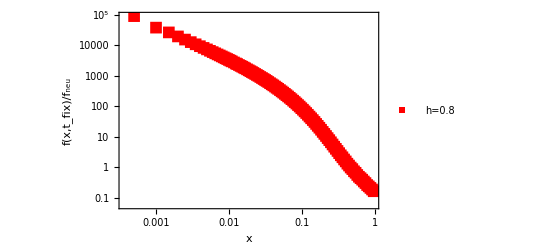

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.8_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1sh8=Transpose@{x11s,x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1sh8,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1sh8,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1sh8},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->All, PlotMarkers->{"■",12}];

(*Show both plots*)
Show[a1sCombined]
```

```mathematica
Data1sh8
```

```mathematica
Data1sh8={{0.,157.343},{0.0005,88727.5},{0.001,37238.3},{0.0015,25968.4},{0.002,19157},{0.0025,15115.4},{0.003,12464.2},{0.0035,10585.3},{0.004,9165.37},{0.0045,8054.88},{0.005,7196.82},{0.0055,6470.75},{0.006,5870},{0.0065,5358.39},{0.007,4927.64},{0.0075,4563.49},{0.008,4236.71},{0.0085,3943.35},{0.009,3688.69},{0.0095,3473.31},{0.01,3261.93},{0.0105,3079.39},{0.011,2914.06},{0.0115,2760.42},{0.012,2620.45},{0.0125,2488.33},{0.013,2373.49},{0.0135,2264.46},{0.014,2166.96},{0.0145,2073.64},{0.015,1987.19},{0.0155,1910.6},{0.016,1831.71},{0.0165,1761.73},{0.017,1689.37},{0.0175,1627.6},{0.018,1569.43},{0.0185,1513.56},{0.019,1462.47},{0.0195,1408.43},{0.02,1365.18},{0.0205,1320.27},{0.021,1278.63},{0.0215,1235.61},{0.022,1197.68},{0.0225,1159.02},{0.023,1125.84},{0.0235,1092.13},{0.024,1061.24},{0.0245,1029.89},{0.025,1002.88},{0.0255,973.547},{0.026,950.115},{0.0265,921.915},{0.027,895.414},{0.0275,872.625},{0.028,851.522},{0.0285,827.723},{0.029,809.725},{0.0295,789.072},{0.03,765.13},{0.0305,752.455},{0.031,730.325},{0.0315,715.995},{0.032,696.227},{0.0325,683.388},{0.033,665.132},{0.0335,651.688},{0.034,636.399},{0.0345,621.548},{0.035,607.852},{0.0355,593.642},{0.036,579.836},{0.0365,566.914},{0.037,558.585},{0.0375,543.51},{0.038,532.589},{0.0385,521.848},{0.039,511.072},{0.0395,500.183},{0.04,491.812},{0.0405,479.332},{0.041,472.923},{0.0415,463.678},{0.042,451.834},{0.0425,445.352},{0.043,434.879},{0.0435,425.868},{0.044,420.565},{0.0445,410.022},{0.045,402.923},{0.0455,394.927},{0.046,387.656},{0.0465,382.281},{0.047,372.094},{0.0475,367.17},{0.048,361.782},{0.0485,352.839},{0.049,346.783},{0.0495,343.98},{0.05,337.854},{0.0505,330.112},{0.051,325.358},{0.0515,318.987},{0.052,313.654},{0.0525,307.688},{0.053,302.793},{0.0535,297.057},{0.054,294.885},{0.0545,286.855},{0.055,283.862},{0.0555,278.066},{0.056,274.343},{0.0565,269.085},{0.057,266.539},{0.0575,263.161},{0.058,257.316},{0.0585,253.272},{0.059,248.827},{0.0595,244.593},{0.06,238.905},{0.0605,237.666},{0.061,233.49},{0.0615,228.609},{0.062,225.592},{0.0625,222.959},{0.063,220.411},{0.0635,215.247},{0.064,213.464},{0.0645,211.606},{0.065,206.947},{0.0655,203.69},{0.066,199.974},{0.0665,197.846},{0.067,194.473},{0.0675,192.919},{0.068,190.182},{0.0685,185.706},{0.069,183.193},{0.0695,181.7},{0.07,179.506},{0.0705,176.435},{0.071,173.612},{0.0715,171.936},{0.072,167.924},{0.0725,166.721},{0.073,164.885},{0.0735,162.082},{0.074,160.242},{0.0745,157.938},{0.075,155.782},{0.0755,153.944},{0.076,150.779},{0.0765,150.112},{0.077,146.859},{0.0775,144.344},{0.078,142.599},{0.0785,141.235},{0.079,139.354},{0.0795,138.493},{0.08,135.768},{0.0805,133.678},{0.081,133.464},{0.0815,130.639},{0.082,128.885},{0.0825,126.879},{0.083,125.696},{0.0835,124.012},{0.084,121.922},{0.0845,120.447},{0.085,119.345},{0.0855,117.714},{0.086,116.258},{0.0865,115.906},{0.087,113.854},{0.0875,112.216},{0.088,110.517},{0.0885,108.473},{0.089,107.708},{0.0895,105.808},{0.09,105.067},{0.0905,103.828},{0.091,102.348},{0.0915,102.483},{0.092,100.721},{0.0925,99.5557},{0.093,97.4416},{0.0935,98.2864},{0.094,95.0572},{0.0945,93.5717},{0.095,93.5677},{0.0955,91.7759},{0.096,90.873},{0.0965,89.7959},{0.097,88.1923},{0.0975,89.0612},{0.098,86.2924},{0.0985,85.5597},{0.099,85.3655},{0.0995,83.4035},{0.1,82.9731},{0.1005,80.9891},{0.101,80.1923},{0.1015,80.8189},{0.102,79.3895},{0.1025,78.6507},{0.103,77.3054},{0.1035,76.5486},{0.104,75.7178},{0.1045,75.0431},{0.105,74.7328},{0.1055,72.9611},{0.106,72.0381},{0.1065,71.2273},{0.107,70.6727},{0.1075,69.1592},{0.108,69.2813},{0.1085,68.5786},{0.109,68.7168},{0.1095,66.7188},{0.11,65.2933},{0.1105,65.6177},{0.111,64.3985},{0.1115,63.6798},{0.112,63.7178},{0.1125,63.3314},{0.113,61.8139},{0.1135,61.2954},{0.114,60.3904},{0.1145,59.5496},{0.115,59.2973},{0.1155,59.0871},{0.116,57.4555},{0.1165,58.0301},{0.117,57.5676},{0.1175,56.1402},{0.118,54.9029},{0.1185,54.935},{0.119,55.0071},{0.1195,53.3234},{0.12,53.5936},{0.1205,53.0191},{0.121,52.5466},{0.1215,51.6817},{0.122,51.4595},{0.1225,51.1712},{0.123,49.926},{0.1235,49.1812},{0.124,48.931},{0.1245,48.2423},{0.125,48.0401},{0.1255,47.3394},{0.126,47.2593},{0.1265,46.1422},{0.127,45.922},{0.1275,45.9941},{0.128,45.3274},{0.1285,45.1612},{0.129,43.8859},{0.1295,44.4245},{0.13,43.8119},{0.1305,42.7368},{0.131,41.99},{0.1315,42.6067},{0.132,42.0681},{0.1325,41.5897},{0.133,41.1232},{0.1335,40.5706},{0.134,39.5796},{0.1345,40.5005},{0.135,39.3754},{0.1355,39.3133},{0.136,39.0811},{0.1365,38.7788},{0.137,38.2483},{0.1375,37.2032},{0.138,36.7888},{0.1385,36.6607},{0.139,36.931},{0.1395,36.7768},{0.14,35.9079},{0.1405,35.5916},{0.141,35.5876},{0.1415,35.0831},{0.142,34.7188},{0.1425,34.8409},{0.143,34.1302},{0.1435,33.2313},{0.144,33.1492},{0.1445,33.8999},{0.145,32.3123},{0.1455,32.6927},{0.146,32.2703},{0.1465,32.1282},{0.147,31.8298},{0.1475,30.945},{0.148,31.6617},{0.1485,30.3964},{0.149,30.3744},{0.1495,30.2383},{0.15,30.024},{0.1505,29.8038},{0.151,29.5115},{0.1515,29.0731},{0.152,28.6967},{0.1525,28.4285},{0.153,28.2563},{0.1535,28.6487},{0.154,27.3394},{0.1545,28.1502},{0.155,26.8929},{0.1555,27.1712},{0.156,26.6026},{0.1565,26.2703},{0.157,26.1402},{0.1575,26.3023},{0.158,26.4044},{0.1585,25.4295},{0.159,25.0931},{0.1595,24.959},{0.16,24.8088},{0.1605,25.021},{0.161,25.0551},{0.1615,24.032},{0.162,23.958},{0.1625,23.5135},{0.163,23.3013},{0.1635,22.9029},{0.164,23.2172},{0.1645,23.1852},{0.165,22.8589},{0.1655,22.927},{0.166,22.3564},{0.1665,22.3363},{0.167,22.3263},{0.1675,21.8198},{0.168,21.9219},{0.1685,21.6016},{0.169,21.6737},{0.1695,20.945},{0.17,21.7177},{0.1705,21.1231},{0.171,20.4625},{0.1715,20.4004},{0.172,20.4245},{0.1725,20.4925},{0.173,19.8819},{0.1735,19.7278},{0.174,19.7157},{0.1745,19.3393},{0.175,19.3233},{0.1755,19.3053},{0.176,18.973},{0.1765,19.2172},{0.177,18.8909},{0.1775,18.5185},{0.178,18.2743},{0.1785,18.3964},{0.179,18.1842},{0.1795,18.024},{0.18,17.6677},{0.1805,17.6056},{0.181,17.6317},{0.1815,17.3213},{0.182,17.4895},{0.1825,17.2072},{0.183,16.8429},{0.1835,17.0531},{0.184,17.0531},{0.1845,16.8969},{0.185,16.2543},{0.1855,16.4925},{0.186,16.0661},{0.1865,15.97},{0.187,16.02},{0.1875,15.8499},{0.188,15.5436},{0.1885,16.1662},{0.189,15.2433},{0.1895,15.3353},{0.19,15.2773},{0.1905,15.1752},{0.191,14.949},{0.1915,15.023},{0.192,14.4805},{0.1925,14.8188},{0.193,14.1161},{0.1935,14.1542},{0.194,14.3544},{0.1945,14.0861},{0.195,13.8499},{0.1955,13.8298},{0.196,14.1362},{0.1965,13.8338},{0.197,13.5015},{0.1975,13.6557},{0.198,13.4555},{0.1985,13.3173},{0.199,13.2633},{0.1995,13.2252},{0.2,13.1392},{0.2005,12.7367},{0.201,13.0531},{0.2015,13.0871},{0.202,12.961},{0.2025,12.5265},{0.203,12.1101},{0.2035,12.2322},{0.204,12.4204},{0.2045,12.01},{0.205,11.966},{0.2055,12.0341},{0.206,11.96},{0.2065,11.8679},{0.207,11.6997},{0.2075,11.6757},{0.208,11.3714},{0.2085,11.4154},{0.209,11.4695},{0.2095,11.7157},{0.21,11.2893},{0.2105,11.1011},{0.211,11.2072},{0.2115,11.2393},{0.212,11.0611},{0.2125,10.8709},{0.213,10.8308},{0.2135,10.3043},{0.214,11.2192},{0.2145,10.5826},{0.215,10.3784},{0.2155,10.026},{0.216,10.3343},{0.2165,10.0621},{0.217,10.4665},{0.2175,10.2122},{0.218,10.3824},{0.2185,10.0621},{0.219,9.78179},{0.2195,9.94396},{0.22,9.65766},{0.2205,9.70972},{0.221,9.51152},{0.2215,9.47949},{0.222,9.26327},{0.2225,9.27729},{0.223,9.27929},{0.2235,9.30932},{0.224,9.43944},{0.2245,9.2953},{0.225,9.40141},{0.2255,9.15517},{0.226,8.92694},{0.2265,8.82683},{0.227,8.83884},{0.2275,8.84686},{0.228,8.8889},{0.2285,8.5906},{0.229,8.81284},{0.2295,8.71072},{0.23,8.45046},{0.2305,8.65066},{0.231,8.82484},{0.2315,8.33834},{0.232,8.24827},{0.2325,8.08609},{0.233,8.13815},{0.2335,8.34636},{0.234,8.24425},{0.2345,8.1902},{0.235,7.76777},{0.2355,7.83383},{0.236,7.68769},{0.2365,7.84786},{0.237,7.96196},{0.2375,7.73374},{0.238,7.78779},{0.2385,7.54154},{0.239,7.58961},{0.2395,7.72374},{0.24,7.57759},{0.2405,7.50952},{0.241,7.35336},{0.2415,7.41342},{0.242,7.39741},{0.2425,7.18319},{0.243,7.4875},{0.2435,7.08109},{0.244,7.24325},{0.2445,7.05105},{0.245,7.12313},{0.2455,7.04705},{0.246,7.03505},{0.2465,6.979},{0.247,6.79081},{0.2475,6.8889},{0.248,6.82283},{0.2485,6.6847},{0.249,6.74675},{0.2495,6.70472},{0.25,6.70871},{0.2505,6.72673},{0.251,6.6907},{0.2515,6.6787},{0.252,6.19821},{0.2525,6.27829},{0.253,6.38839},{0.2535,6.25826},{0.254,6.51453},{0.2545,6.01802},{0.255,6.34235},{0.2555,6.24826},{0.256,6.15616},{0.2565,6.21623},{0.257,5.93194},{0.2575,5.92993},{0.258,5.98999},{0.2585,5.98599},{0.259,6.0921},{0.2595,5.84384},{0.26,5.83586},{0.2605,5.65165},{0.261,5.87388},{0.2615,5.72573},{0.262,5.74575},{0.2625,5.65967},{0.263,5.63364},{0.2635,5.51753},{0.264,5.53955},{0.2645,5.71572},{0.265,5.53754},{0.2655,5.5956},{0.266,5.4975},{0.2665,5.51151},{0.267,5.34735},{0.2675,5.25126},{0.268,5.25125},{0.2685,5.20321},{0.269,5.37338},{0.2695,5.16117},{0.27,5.31532},{0.2705,5.16918},{0.271,5.25526},{0.2715,5.17518},{0.272,4.98499},{0.2725,4.92493},{0.273,4.93694},{0.2735,5.03705},{0.274,5.07909},{0.2745,5.01502},{0.275,4.72873},{0.2755,4.94294},{0.276,4.71271},{0.2765,4.77477},{0.277,4.56456},{0.2775,4.85686},{0.278,4.58859},{0.2785,4.51853},{0.279,4.52053},{0.2795,4.83484},{0.28,4.6887},{0.2805,4.72272},{0.281,4.51853},{0.2815,4.61662},{0.282,4.77878},{0.2825,4.73475},{0.283,4.3964},{0.2835,4.36236},{0.284,4.61462},{0.2845,4.4905},{0.285,4.28228},{0.2855,4.27227},{0.286,4.22022},{0.2865,4.21021},{0.287,4.27628},{0.2875,4.23023},{0.288,4.14815},{0.2885,4.19821},{0.289,4.24825},{0.2895,4.01802},{0.29,4.05806},{0.2905,4.13614},{0.291,4.12012},{0.2915,4.07408},{0.292,3.94595},{0.2925,3.94795},{0.293,4.16417},{0.2935,4},{0.294,4.21021},{0.2945,3.93594},{0.295,3.73774},{0.2955,4.00001},{0.296,3.96797},{0.2965,3.77578},{0.297,3.6937},{0.2975,3.81582},{0.298,3.80181},{0.2985,3.87388},{0.299,3.90991},{0.2995,3.60161},{0.3,3.82983},{0.3005,3.6997},{0.301,3.90991},{0.3015,3.62763},{0.302,3.58559},{0.3025,3.6957},{0.303,3.5956},{0.3035,3.65766},{0.304,3.51352},{0.3045,3.64165},{0.305,3.53154},{0.3055,3.62163},{0.306,3.71572},{0.3065,3.36937},{0.307,3.3994},{0.3075,3.62363},{0.308,3.37538},{0.3085,3.35936},{0.309,3.40741},{0.3095,3.31732},{0.31,3.30931},{0.3105,3.37539},{0.311,3.2993},{0.3115,3.20521},{0.312,3.37938},{0.3125,3.32533},{0.313,3.37337},{0.3135,3.27528},{0.314,3.13313},{0.3145,3.05706},{0.315,3.11313},{0.3155,3.18919},{0.316,3.25726},{0.3165,3.18319},{0.317,3.28529},{0.3175,3.17718},{0.318,3.06708},{0.3185,2.81282},{0.319,3.08109},{0.3195,3.21922},{0.32,3.10311},{0.3205,3.05306},{0.321,3.12113},{0.3215,3.06306},{0.322,3.23924},{0.3225,2.7968},{0.323,2.94895},{0.3235,3.04705},{0.324,2.81482},{0.3245,3.02503},{0.325,3.01702},{0.3255,2.94094},{0.326,2.9009},{0.3265,2.85486},{0.327,2.80281},{0.3275,2.80681},{0.328,2.91291},{0.3285,2.67467},{0.329,2.73874},{0.3295,2.85886},{0.33,2.71071},{0.3305,2.6967},{0.331,2.66066},{0.3315,2.65866},{0.332,2.6987},{0.3325,2.73874},{0.333,2.64064},{0.3335,2.57858},{0.334,2.66066},{0.3345,2.71272},{0.335,2.65866},{0.3355,2.72673},{0.336,2.77478},{0.3365,2.5025},{0.337,2.54855},{0.3375,2.58058},{0.338,2.50251},{0.3385,2.47448},{0.339,2.38839},{0.3395,2.5986},{0.34,2.46847},{0.3405,2.66667},{0.341,2.46647},{0.3415,2.43243},{0.342,2.51452},{0.3425,2.45045},{0.343,2.41041},{0.3435,2.43043},{0.344,2.50851},{0.3445,2.55056},{0.345,2.31432},{0.3455,2.42242},{0.346,2.53254},{0.3465,2.36036},{0.347,2.44845},{0.3475,2.34835},{0.348,2.44244},{0.3485,2.1922},{0.349,2.39239},{0.3495,2.22222},{0.35,2.13814},{0.3505,2.41442},{0.351,2.2042},{0.3515,2.16817},{0.352,2.30631},{0.3525,2.18819},{0.353,2.35636},{0.3535,2.31832},{0.354,2.22222},{0.3545,2.11612},{0.355,2.20421},{0.3555,2.17218},{0.356,2.23023},{0.3565,2.23223},{0.357,2.21021},{0.3575,2.13213},{0.358,2.20621},{0.3585,2.20821},{0.359,2.0981},{0.3595,2.13013},{0.36,2.14215},{0.3605,2.16417},{0.361,2.06607},{0.3615,2.04404},{0.362,1.99399},{0.3625,2.08208},{0.363,2.14014},{0.3635,2.09409},{0.364,1.91792},{0.3645,1.8979},{0.365,2.03403},{0.3655,2.002},{0.366,2.09009},{0.3665,2.03604},{0.367,2.0941},{0.3675,2.07007},{0.368,1.96197},{0.3685,1.94795},{0.369,1.90391},{0.3695,2.16417},{0.37,2.02002},{0.3705,2.00401},{0.371,1.94195},{0.3715,1.95395},{0.372,1.86587},{0.3725,1.94595},{0.373,1.87988},{0.3735,1.92793},{0.374,1.91391},{0.3745,1.96597},{0.375,1.78379},{0.3755,1.996},{0.376,1.88189},{0.3765,1.76577},{0.377,1.90591},{0.3775,1.85385},{0.378,1.85986},{0.3785,1.7998},{0.379,1.78779},{0.3795,1.84785},{0.38,1.93394},{0.3805,1.79179},{0.381,1.75376},{0.3815,1.87187},{0.382,1.77778},{0.3825,1.67768},{0.383,1.68569},{0.3835,1.76778},{0.384,1.78178},{0.3845,1.69169},{0.385,1.62963},{0.3855,1.83384},{0.386,1.68569},{0.3865,1.65566},{0.387,1.7017},{0.3875,1.64164},{0.388,1.57157},{0.3885,1.64164},{0.389,1.65165},{0.3895,1.70971},{0.39,1.56356},{0.3905,1.67968},{0.391,1.65966},{0.3915,1.69369},{0.392,1.67367},{0.3925,1.62763},{0.393,1.70571},{0.3935,1.74975},{0.394,1.62563},{0.3945,1.57958},{0.395,1.57157},{0.3955,1.70771},{0.396,1.54355},{0.3965,1.56356},{0.397,1.58159},{0.3975,1.56357},{0.398,1.55355},{0.3985,1.62963},{0.399,1.63764},{0.3995,1.54955},{0.4,1.62362},{0.4005,1.53353},{0.401,1.55756},{0.4015,1.4955},{0.402,1.50751},{0.4025,1.41742},{0.403,1.60961},{0.4035,1.43343},{0.404,1.54955},{0.4045,1.47748},{0.405,1.44345},{0.4055,1.52753},{0.406,1.43744},{0.4065,1.46947},{0.407,1.47548},{0.4075,1.52152},{0.408,1.45145},{0.4085,1.46347},{0.409,1.54155},{0.4095,1.41142},{0.41,1.37137},{0.4105,1.38539},{0.411,1.52953},{0.4115,1.3954},{0.412,1.40742},{0.4125,1.50351},{0.413,1.37137},{0.4135,1.47548},{0.414,1.34535},{0.4145,1.33333},{0.415,1.43143},{0.4155,1.27127},{0.416,1.37338},{0.4165,1.36336},{0.417,1.35335},{0.4175,1.34935},{0.418,1.37137},{0.4185,1.33734},{0.419,1.34535},{0.4195,1.2913},{0.42,1.2953},{0.4205,1.34935},{0.421,1.21922},{0.4215,1.26527},{0.422,1.41141},{0.4225,1.36937},{0.423,1.4034},{0.4235,1.1932},{0.424,1.23924},{0.4245,1.1952},{0.425,1.32332},{0.4255,1.31732},{0.426,1.32933},{0.4265,1.29129},{0.427,1.23123},{0.4275,1.25726},{0.428,1.30131},{0.4285,1.30531},{0.429,1.23323},{0.4295,1.21321},{0.43,1.22322},{0.4305,1.26927},{0.431,1.12713},{0.4315,1.12513},{0.432,1.21522},{0.4325,1.27128},{0.433,1.0991},{0.4335,1.20121},{0.434,1.22923},{0.4345,1.2973},{0.435,1.15115},{0.4355,1.18118},{0.436,1.13714},{0.4365,1.2012},{0.437,1.15716},{0.4375,1.15115},{0.438,1.26727},{0.4385,1.21722},{0.439,1.17318},{0.4395,1.18919},{0.44,1.11312},{0.4405,1.1932},{0.441,1.09309},{0.4415,1.18319},{0.442,1.1932},{0.4425,1.21922},{0.443,1.22122},{0.4435,1.07107},{0.444,1.13514},{0.4445,1.16918},{0.445,1.16316},{0.4455,1.03704},{0.446,1.16917},{0.4465,1.15115},{0.447,1.11912},{0.4475,1.03904},{0.448,1.16317},{0.4485,1.03303},{0.449,1.11912},{0.4495,1.06707},{0.45,1.15916},{0.4505,1.07508},{0.451,1.15716},{0.4515,1.03504},{0.452,1.06306},{0.4525,1.05105},{0.453,1.08909},{0.4535,1.06907},{0.454,1.05906},{0.4545,1.10711},{0.455,1.06707},{0.4555,1.07508},{0.456,0.976977},{0.4565,1.03103},{0.457,1.05506},{0.4575,1.06106},{0.458,1.08509},{0.4585,1.08709},{0.459,0.984987},{0.4595,0.980981},{0.46,1.01301},{0.4605,0.984985},{0.461,1.001},{0.4615,0.958961},{0.462,0.996997},{0.4625,1.02102},{0.463,0.988989},{0.4635,1.03704},{0.464,0.936937},{0.4645,0.999003},{0.465,1.00501},{0.4655,0.974975},{0.466,1.1031},{0.4665,1.02102},{0.467,0.928931},{0.4675,0.982987},{0.468,0.948949},{0.4685,1.00501},{0.469,1.003},{0.4695,0.996997},{0.47,1.001},{0.4705,0.978979},{0.471,0.994995},{0.4715,1.01302},{0.472,0.858859},{0.4725,1.003},{0.473,0.856859},{0.4735,0.974975},{0.474,0.942945},{0.4745,0.946947},{0.475,0.920925},{0.4755,0.868869},{0.476,0.948951},{0.4765,0.938939},{0.477,0.978981},{0.4775,0.894895},{0.478,0.928929},{0.4785,0.882883},{0.479,0.886887},{0.4795,0.882883},{0.48,0.974977},{0.4805,0.956957},{0.481,0.894895},{0.4815,0.826827},{0.482,0.944945},{0.4825,0.872873},{0.483,0.840841},{0.4835,0.936939},{0.484,0.922923},{0.4845,0.894895},{0.485,0.934935},{0.4855,0.904907},{0.486,0.826829},{0.4865,0.922925},{0.487,0.944947},{0.4875,0.908913},{0.488,0.802805},{0.4885,0.850851},{0.489,0.866867},{0.4895,0.914915},{0.49,0.876877},{0.4905,0.820821},{0.491,0.898901},{0.4915,0.896899},{0.492,0.868869},{0.4925,0.784785},{0.493,0.810811},{0.4935,0.806807},{0.494,0.898899},{0.4945,0.874875},{0.495,0.804807},{0.4955,0.810813},{0.496,0.872873},{0.4965,0.816819},{0.497,0.892893},{0.4975,0.790791},{0.498,0.842843},{0.4985,0.826827},{0.499,0.870871},{0.4995,0.774775},{0.5,1.65566},{0.5005,0.004004},{0.501,1.56557},{0.5015,0},{0.502,1.64565},{0.5025,0.002002},{0.503,1.68969},{0.5035,0},{0.504,1.54755},{0.5045,0.004004},{0.505,1.65766},{0.5055,0},{0.506,1.53554},{0.5065,0},{0.507,1.57558},{0.5075,0},{0.508,1.48348},{0.5085,0.002002},{0.509,1.63163},{0.5095,0},{0.51,1.57358},{0.5105,0},{0.511,1.53554},{0.5115,0},{0.512,0.790791},{0.5125,0.776779},{0.513,0.814815},{0.5135,0.774775},{0.514,0.750751},{0.5145,0.758761},{0.515,0.754755},{0.5155,0.746747},{0.516,0.794795},{0.5165,0.780781},{0.517,0.730731},{0.5175,0.722723},{0.518,0.820821},{0.5185,0.808809},{0.519,0.752753},{0.5195,0.778779},{0.52,0.746747},{0.5205,0.754755},{0.521,0.776777},{0.5215,0.724725},{0.522,0.722725},{0.5225,0.688689},{0.523,0.792793},{0.5235,0.680683},{0.524,0.748749},{0.5245,0.786789},{0.525,0.682683},{0.5255,0.780781},{0.526,0.744745},{0.5265,0.662663},{0.527,0.800803},{0.5275,0.748749},{0.528,0.734735},{0.5285,0.726729},{0.529,0.712719},{0.5295,0.644645},{0.53,0.686687},{0.5305,0.674675},{0.531,0.670671},{0.5315,0.692693},{0.532,0.704707},{0.5325,0.706707},{0.533,0.628629},{0.5335,0.702705},{0.534,0.684687},{0.5345,0.682683},{0.535,0.726729},{0.5355,0.692693},{0.536,0.636637},{0.5365,0.648649},{0.537,0.710715},{0.5375,0.630631},{0.538,0.708709},{0.5385,0.676677},{0.539,0.628629},{0.5395,0.554555},{0.54,0.678679},{0.5405,0.654657},{0.541,0.656657},{0.5415,0.714715},{0.542,0.644645},{0.5425,0.660661},{0.543,0.708709},{0.5435,0.702705},{0.544,0.602603},{0.5445,0.732733},{0.545,0.614615},{0.5455,0.674675},{0.546,0.652653},{0.5465,0.688689},{0.547,0.768769},{0.5475,0.632633},{0.548,0.646647},{0.5485,0.704705},{0.549,0.686687},{0.5495,0.642643},{0.55,0.686687},{0.5505,0.686687},{0.551,0.610615},{0.5515,0.658659},{0.552,0.642643},{0.5525,0.646647},{0.553,0.610611},{0.5535,0.566567},{0.554,0.724727},{0.5545,0.638639},{0.555,0.556557},{0.5555,0.648649},{0.556,0.622623},{0.5565,0.622625},{0.557,0.710711},{0.5575,0.590591},{0.558,0.634635},{0.5585,0.658661},{0.559,0.572573},{0.5595,0.606607},{0.56,0.578579},{0.5605,0.648651},{0.561,0.668669},{0.5615,0.616617},{0.562,0.614617},{0.5625,0.584585},{0.563,0.634635},{0.5635,0.632633},{0.564,0.568569},{0.5645,0.500501},{0.565,0.528529},{0.5655,0.542543},{0.566,0.628629},{0.5665,0.592595},{0.567,0.592593},{0.5675,0.598599},{0.568,0.564569},{0.5685,0.582585},{0.569,0.544545},{0.5695,0.528531},{0.57,0.534535},{0.5705,0.586587},{0.571,0.626627},{0.5715,0.574575},{0.572,0.542545},{0.5725,0.528529},{0.573,0.520521},{0.5735,0.528529},{0.574,0.590591},{0.5745,0.592597},{0.575,0.578579},{0.5755,0.622623},{0.576,0.554555},{0.5765,0.580583},{0.577,0.564565},{0.5775,0.586587},{0.578,0.548549},{0.5785,0.560563},{0.579,0.484484},{0.5795,0.536537},{0.58,0.526527},{0.5805,0.630631},{0.581,0.522525},{0.5815,0.542545},{0.582,0.516519},{0.5825,0.526527},{0.583,0.562565},{0.5835,0.574579},{0.584,0.478478},{0.5845,0.504505},{0.585,0.566567},{0.5855,0.590591},{0.586,0.526527},{0.5865,0.524525},{0.587,0.556557},{0.5875,0.48048},{0.588,0.604605},{0.5885,0.478478},{0.589,0.584585},{0.5895,0.510511},{0.59,0.528531},{0.5905,0.568571},{0.591,0.546549},{0.5915,0.488488},{0.592,0.546549},{0.5925,0.492497},{0.593,0.516517},{0.5935,0.562563},{0.594,0.520523},{0.5945,0.490492},{0.595,0.500503},{0.5955,0.544545},{0.596,0.498498},{0.5965,0.544545},{0.597,0.448448},{0.5975,0.454454},{0.598,0.524527},{0.5985,0.568569},{0.599,0.528529},{0.5995,0.556559},{0.6,0.494494},{0.6005,0.500501},{0.601,0.512513},{0.6015,0.45646},{0.602,0.486486},{0.6025,0.520521},{0.603,0.536537},{0.6035,0.454454},{0.604,0.520521},{0.6045,0.552553},{0.605,0.416416},{0.6055,0.474474},{0.606,0.462462},{0.6065,0.496496},{0.607,0.524527},{0.6075,0.496496},{0.608,0.462464},{0.6085,0.504505},{0.609,0.498498},{0.6095,0.560561},{0.61,0.46046},{0.6105,0.442442},{0.611,0.482482},{0.6115,0.494497},{0.612,0.486486},{0.6125,0.43043},{0.613,0.47047},{0.6135,0.42843},{0.614,0.498501},{0.6145,0.406406},{0.615,0.478478},{0.6155,0.436436},{0.616,0.422422},{0.6165,0.468468},{0.617,0.454454},{0.6175,0.476478},{0.618,0.478478},{0.6185,0.49049},{0.619,0.464464},{0.6195,0.426428},{0.62,0.492492},{0.6205,0.43043},{0.621,0.428428},{0.6215,0.486486},{0.622,0.452454},{0.6225,0.448448},{0.623,0.464464},{0.6235,0.432432},{0.624,0.444444},{0.6245,0.474474},{0.625,0.436436},{0.6255,0.478478},{0.626,0.550551},{0.6265,0.454454},{0.627,0.43043},{0.6275,0.452454},{0.628,0.448448},{0.6285,0.540541},{0.629,0.462464},{0.6295,0.464464},{0.63,0.42042},{0.6305,0.524525},{0.631,0.408412},{0.6315,0.47047},{0.632,0.466466},{0.6325,0.47047},{0.633,0.43043},{0.6335,0.424424},{0.634,0.436436},{0.6345,0.456456},{0.635,0.444444},{0.6355,0.46046},{0.636,0.418418},{0.6365,0.434436},{0.637,0.414414},{0.6375,0.362362},{0.638,0.444446},{0.6385,0.396398},{0.639,0.438438},{0.6395,0.422422},{0.64,0.372372},{0.6405,0.444444},{0.641,0.398398},{0.6415,0.466466},{0.642,0.456456},{0.6425,0.422424},{0.643,0.376376},{0.6435,0.414414},{0.644,0.368368},{0.6445,0.396398},{0.645,0.412412},{0.6455,0.44845},{0.646,0.442442},{0.6465,0.424424},{0.647,0.43043},{0.6475,0.414414},{0.648,0.458458},{0.6485,0.436436},{0.649,0.492492},{0.6495,0.38038},{0.65,0.394394},{0.6505,0.368368},{0.651,0.354354},{0.6515,0.478478},{0.652,0.428428},{0.6525,0.43043},{0.653,0.422422},{0.6535,0.454454},{0.654,0.438438},{0.6545,0.386386},{0.655,0.398398},{0.6555,0.42042},{0.656,0.386386},{0.6565,0.424424},{0.657,0.426428},{0.6575,0.472472},{0.658,0.406406},{0.6585,0.402404},{0.659,0.386386},{0.6595,0.43043},{0.66,0.378378},{0.6605,0.464466},{0.661,0.376376},{0.6615,0.4004},{0.662,0.448448},{0.6625,0.536537},{0.663,0.394394},{0.6635,0.382382},{0.664,0.438438},{0.6645,0.428428},{0.665,0.400402},{0.6655,0.434434},{0.666,0.384384},{0.6665,0.438438},{0.667,0.36036},{0.6675,0.364366},{0.668,0.392392},{0.6685,0.356356},{0.669,0.392392},{0.6695,0.332336},{0.67,0.326326},{0.6705,0.366366},{0.671,0.402404},{0.6715,0.352352},{0.672,0.364364},{0.6725,0.416416},{0.673,0.376376},{0.6735,0.424424},{0.674,0.47047},{0.6745,0.366366},{0.675,0.452452},{0.6755,0.36036},{0.676,0.366366},{0.6765,0.426426},{0.677,0.308308},{0.6775,0.376376},{0.678,0.382382},{0.6785,0.416416},{0.679,0.43844},{0.6795,0.358358},{0.68,0.348348},{0.6805,0.368368},{0.681,0.386386},{0.6815,0.376376},{0.682,0.3984},{0.6825,0.362362},{0.683,0.406406},{0.6835,0.346346},{0.684,0.314314},{0.6845,0.386386},{0.685,0.400402},{0.6855,0.33033},{0.686,0.38038},{0.6865,0.374374},{0.687,0.368368},{0.6875,0.418418},{0.688,0.358358},{0.6885,0.374374},{0.689,0.414414},{0.6895,0.388388},{0.69,0.326326},{0.6905,0.37037},{0.691,0.382382},{0.6915,0.382384},{0.692,0.328328},{0.6925,0.372372},{0.693,0.332332},{0.6935,0.308308},{0.694,0.404404},{0.6945,0.328328},{0.695,0.316318},{0.6955,0.41041},{0.696,0.326326},{0.6965,0.288288},{0.697,0.332334},{0.6975,0.35836},{0.698,0.392392},{0.6985,0.334334},{0.699,0.34034},{0.6995,0.362362},{0.7,0.384384},{0.7005,0.33033},{0.701,0.374374},{0.7015,0.346348},{0.702,0.398398},{0.7025,0.34034},{0.703,0.332332},{0.7035,0.362362},{0.704,0.330332},{0.7045,0.364364},{0.705,0.344344},{0.7055,0.322322},{0.706,0.382382},{0.7065,0.306306},{0.707,0.386386},{0.7075,0.436438},{0.708,0.336336},{0.7085,0.33634},{0.709,0.332332},{0.7095,0.288288},{0.71,0.3003},{0.7105,0.35035},{0.711,0.326328},{0.7115,0.33033},{0.712,0.31832},{0.7125,0.324324},{0.713,0.332332},{0.7135,0.316316},{0.714,0.33834},{0.7145,0.326326},{0.715,0.346346},{0.7155,0.32032},{0.716,0.374374},{0.7165,0.32032},{0.717,0.334334},{0.7175,0.32032},{0.718,0.35035},{0.7185,0.302302},{0.719,0.30831},{0.7195,0.308308},{0.72,0.324324},{0.7205,0.320322},{0.721,0.334334},{0.7215,0.286286},{0.722,0.32032},{0.7225,0.366366},{0.723,0.368368},{0.7235,0.33033},{0.724,0.328328},{0.7245,0.348348},{0.725,0.322322},{0.7255,0.328328},{0.726,0.298298},{0.7265,0.376376},{0.727,0.32032},{0.7275,0.36837},{0.728,0.296296},{0.7285,0.306306},{0.729,0.318318},{0.7295,0.318318},{0.73,0.306306},{0.7305,0.352352},{0.731,0.326326},{0.7315,0.314318},{0.732,0.318318},{0.7325,0.28028},{0.733,0.346346},{0.7335,0.266266},{0.734,0.312312},{0.7345,0.370372},{0.735,0.308308},{0.7355,0.348352},{0.736,0.334334},{0.7365,0.338338},{0.737,0.338338},{0.7375,0.324324},{0.738,0.252252},{0.7385,0.32032},{0.739,0.306306},{0.7395,0.354354},{0.74,0.30831},{0.7405,0.316316},{0.741,0.332332},{0.7415,0.296296},{0.742,0.296296},{0.7425,0.306306},{0.743,0.338338},{0.7435,0.316316},{0.744,0.338338},{0.7445,0.302302},{0.745,0.318318},{0.7455,0.292292},{0.746,0.30631},{0.7465,0.33033},{0.747,0.304304},{0.7475,0.35035},{0.748,0.308308},{0.7485,0.298298},{0.749,0.284284},{0.7495,0.318318},{0.75,0.326328},{0.7505,0.29029},{0.751,0.336336},{0.7515,0.256258},{0.752,0.238238},{0.7525,0.276276},{0.753,0.292292},{0.7535,0.32032},{0.754,0.32032},{0.7545,0.25025},{0.755,0.284284},{0.7555,0.238238},{0.756,0.314314},{0.7565,0.302302},{0.757,0.242242},{0.7575,0.272274},{0.758,0.282282},{0.7585,0.324324},{0.759,0.298298},{0.7595,0.29029},{0.76,0.272272},{0.7605,0.320322},{0.761,0.298298},{0.7615,0.306306},{0.762,0.262262},{0.7625,0.248248},{0.763,0.274274},{0.7635,0.272272},{0.764,0.336336},{0.7645,0.292294},{0.765,0.276276},{0.7655,0.302302},{0.766,0.256256},{0.7665,0.28829},{0.767,0.292292},{0.7675,0.278278},{0.768,0.256256},{0.7685,0.262262},{0.769,0.296298},{0.7695,0.258258},{0.77,0.25025},{0.7705,0.272272},{0.771,0.278278},{0.7715,0.258258},{0.772,0.274274},{0.7725,0.3003},{0.773,0.272272},{0.7735,0.266266},{0.774,0.292292},{0.7745,0.276276},{0.775,0.282282},{0.7755,0.258258},{0.776,0.252252},{0.7765,0.282284},{0.777,0.272272},{0.7775,0.21021},{0.778,0.29029},{0.7785,0.26026},{0.779,0.282282},{0.7795,0.26026},{0.78,0.27828},{0.7805,0.232232},{0.781,0.328328},{0.7815,0.25025},{0.782,0.274274},{0.7825,0.262262},{0.783,0.238238},{0.7835,0.268268},{0.784,0.244244},{0.7845,0.232232},{0.785,0.276276},{0.7855,0.256256},{0.786,0.286286},{0.7865,0.254254},{0.787,0.250252},{0.7875,0.25025},{0.788,0.264264},{0.7885,0.248248},{0.789,0.272272},{0.7895,0.252252},{0.79,0.254254},{0.7905,0.218218},{0.791,0.25025},{0.7915,0.236236},{0.792,0.27027},{0.7925,0.25025},{0.793,0.232232},{0.7935,0.270272},{0.794,0.268268},{0.7945,0.23023},{0.795,0.24825},{0.7955,0.278278},{0.796,0.27027},{0.7965,0.270272},{0.797,0.218218},{0.7975,0.23023},{0.798,0.224224},{0.7985,0.284284},{0.799,0.228228},{0.7995,0.268268},{0.8,0.244246},{0.8005,0.220222},{0.801,0.284284},{0.8015,0.286286},{0.802,0.242242},{0.8025,0.224224},{0.803,0.278278},{0.8035,0.208208},{0.804,0.272272},{0.8045,0.256256},{0.805,0.27027},{0.8055,0.214214},{0.806,0.232232},{0.8065,0.29029},{0.807,0.272272},{0.8075,0.262262},{0.808,0.264264},{0.8085,0.264264},{0.809,0.246246},{0.8095,0.24625},{0.81,0.25025},{0.8105,0.21021},{0.811,0.226226},{0.8115,0.25025},{0.812,0.256256},{0.8125,0.242246},{0.813,0.226226},{0.8135,0.262262},{0.814,0.238238},{0.8145,0.232232},{0.815,0.24024},{0.8155,0.224224},{0.816,0.238238},{0.8165,0.196196},{0.817,0.274274},{0.8175,0.232232},{0.818,0.2963},{0.8185,0.25025},{0.819,0.242242},{0.8195,0.256256},{0.82,0.286286},{0.8205,0.224224},{0.821,0.22022},{0.8215,0.262262},{0.822,0.25025},{0.8225,0.228228},{0.823,0.262262},{0.8235,0.212212},{0.824,0.198198},{0.8245,0.246246},{0.825,0.246246},{0.8255,0.198198},{0.826,0.258258},{0.8265,0.214214},{0.827,0.248248},{0.8275,0.3003},{0.828,0.234234},{0.8285,0.236236},{0.829,0.254254},{0.8295,0.27027},{0.83,0.23824},{0.8305,0.22022},{0.831,0.232232},{0.8315,0.206206},{0.832,0.25025},{0.8325,0.214214},{0.833,0.25025},{0.8335,0.2002},{0.834,0.256256},{0.8345,0.254254},{0.835,0.216216},{0.8355,0.224224},{0.836,0.254254},{0.8365,0.254256},{0.837,0.264264},{0.8375,0.172172},{0.838,0.21021},{0.8385,0.204204},{0.839,0.232232},{0.8395,0.206206},{0.84,0.222222},{0.8405,0.234236},{0.841,0.184184},{0.8415,0.196198},{0.842,0.252252},{0.8425,0.244246},{0.843,0.22022},{0.8435,0.214216},{0.844,0.256256},{0.8445,0.228228},{0.845,0.218218},{0.8455,0.250252},{0.846,0.222222},{0.8465,0.212212},{0.847,0.26026},{0.8475,0.238238},{0.848,0.202204},{0.8485,0.262262},{0.849,0.25025},{0.8495,0.202202},{0.85,0.168168},{0.8505,0.224224},{0.851,0.202202},{0.8515,0.226226},{0.852,0.248248},{0.8525,0.25025},{0.853,0.22022},{0.8535,0.2002},{0.854,0.196198},{0.8545,0.18018},{0.855,0.202202},{0.8555,0.222222},{0.856,0.204204},{0.8565,0.176176},{0.857,0.22022},{0.8575,0.254254},{0.858,0.224224},{0.8585,0.184184},{0.859,0.212212},{0.8595,0.198198},{0.86,0.216216},{0.8605,0.24825},{0.861,0.182182},{0.8615,0.22022},{0.862,0.224224},{0.8625,0.236236},{0.863,0.212212},{0.8635,0.21021},{0.864,0.178178},{0.8645,0.182182},{0.865,0.206206},{0.8655,0.198198},{0.866,0.186186},{0.8665,0.232232},{0.867,0.222222},{0.8675,0.222222},{0.868,0.208208},{0.8685,0.212212},{0.869,0.250252},{0.8695,0.248248},{0.87,0.212212},{0.8705,0.196196},{0.871,0.198198},{0.8715,0.212212},{0.872,0.206208},{0.8725,0.22823},{0.873,0.214214},{0.8735,0.212212},{0.874,0.26026},{0.8745,0.176176},{0.875,0.222222},{0.8755,0.186186},{0.876,0.224224},{0.8765,0.208208},{0.877,0.202204},{0.8775,0.174174},{0.878,0.216216},{0.8785,0.214214},{0.879,0.2002},{0.8795,0.318318},{0.88,0.16016},{0.8805,0.21021},{0.881,0.24024},{0.8815,0.21021},{0.882,0.242242},{0.8825,0.216216},{0.883,0.17017},{0.8835,0.2002},{0.884,0.214214},{0.8845,0.2002},{0.885,0.192192},{0.8855,0.198198},{0.886,0.182182},{0.8865,0.232232},{0.887,0.200202},{0.8875,0.192192},{0.888,0.21021},{0.8885,0.186186},{0.889,0.194194},{0.8895,0.194194},{0.89,0.194194},{0.8905,0.21021},{0.891,0.192192},{0.8915,0.216216},{0.892,0.2002},{0.8925,0.208208},{0.893,0.174174},{0.8935,0.184184},{0.894,0.19019},{0.8945,0.184184},{0.895,0.238238},{0.8955,0.176176},{0.896,0.19019},{0.8965,0.198198},{0.897,0.212212},{0.8975,0.182182},{0.898,0.194194},{0.8985,0.172172},{0.899,0.206206},{0.8995,0.176176},{0.9,0.222222},{0.9005,0.21622},{0.901,0.162162},{0.9015,0.214216},{0.902,0.178178},{0.9025,0.188188},{0.903,0.174174},{0.9035,0.206206},{0.904,0.154154},{0.9045,0.198198},{0.905,0.212212},{0.9055,0.186186},{0.906,0.18018},{0.9065,0.148148},{0.907,0.192192},{0.9075,0.228228},{0.908,0.182182},{0.9085,0.18018},{0.909,0.204204},{0.9095,0.166166},{0.91,0.248248},{0.9105,0.186186},{0.911,0.17017},{0.9115,0.156156},{0.912,0.202202},{0.9125,0.182182},{0.913,0.212212},{0.9135,0.16817},{0.914,0.152152},{0.9145,0.174174},{0.915,0.16016},{0.9155,0.174174},{0.916,0.21021},{0.9165,0.192192},{0.917,0.172172},{0.9175,0.192192},{0.918,0.196196},{0.9185,0.196196},{0.919,0.164164},{0.9195,0.212212},{0.92,0.148148},{0.9205,0.198198},{0.921,0.150152},{0.9215,0.178178},{0.922,0.204204},{0.9225,0.192192},{0.923,0.178178},{0.9235,0.196196},{0.924,0.166166},{0.9245,0.206206},{0.925,0.188188},{0.9255,0.198198},{0.926,0.19019},{0.9265,0.178178},{0.927,0.184184},{0.9275,0.206206},{0.928,0.168168},{0.9285,0.204204},{0.929,0.166166},{0.9295,0.158158},{0.93,0.176176},{0.9305,0.204204},{0.931,0.162162},{0.9315,0.17017},{0.932,0.160162},{0.9325,0.194194},{0.933,0.192194},{0.9335,0.142142},{0.934,0.18018},{0.9345,0.17017},{0.935,0.228228},{0.9355,0.208208},{0.936,0.17017},{0.9365,0.158158},{0.937,0.192192},{0.9375,0.154154},{0.938,0.17017},{0.9385,0.192192},{0.939,0.17017},{0.9395,0.176176},{0.94,0.212212},{0.9405,0.228228},{0.941,0.146146},{0.9415,0.21021},{0.942,0.184184},{0.9425,0.18018},{0.943,0.156156},{0.9435,0.198198},{0.944,0.154154},{0.9445,0.186186},{0.945,0.178178},{0.9455,0.2002},{0.946,0.172172},{0.9465,0.138138},{0.947,0.21021},{0.9475,0.176176},{0.948,0.194194},{0.9485,0.174174},{0.949,0.188188},{0.9495,0.152152},{0.95,0.15816},{0.9505,0.174174},{0.951,0.184188},{0.9515,0.16817},{0.952,0.176176},{0.9525,0.122122},{0.953,0.202202},{0.9535,0.148148},{0.954,0.158158},{0.9545,0.182182},{0.955,0.164164},{0.9555,0.13013},{0.956,0.186186},{0.9565,0.186186},{0.957,0.16016},{0.9575,0.176176},{0.958,0.12613},{0.9585,0.18018},{0.959,0.226226},{0.9595,0.16016},{0.96,0.214214},{0.9605,0.136136},{0.961,0.142142},{0.9615,0.17017},{0.962,0.152152},{0.9625,0.162162},{0.963,0.182182},{0.9635,0.154156},{0.964,0.136136},{0.9645,0.156156},{0.965,0.14014},{0.9655,0.156156},{0.966,0.15015},{0.9665,0.154154},{0.967,0.166166},{0.9675,0.198198},{0.968,0.16016},{0.9685,0.172172},{0.969,0.16016},{0.9695,0.176176},{0.97,0.164164},{0.9705,0.14014},{0.971,0.202202},{0.9715,0.176176},{0.972,0.15015},{0.9725,0.176176},{0.973,0.188188},{0.9735,0.136136},{0.974,0.162162},{0.9745,0.146146},{0.975,0.214214},{0.9755,0.17017},{0.976,0.134134},{0.9765,0.16016},{0.977,0.192192},{0.9775,0.154154},{0.978,0.144144},{0.9785,0.142142},{0.979,0.136136},{0.9795,0.154154},{0.98,0.142142},{0.9805,0.134134},{0.981,0.16016},{0.9815,0.14014},{0.982,0.172174},{0.9825,0.182182},{0.983,0.184184},{0.9835,0.146146},{0.984,0.168168},{0.9845,0.162162},{0.985,0.136136},{0.9855,0.16016},{0.986,0.18018},{0.9865,0.162162},{0.987,0.19019},{0.9875,0.108108},{0.988,0.15015},{0.9885,0.172172},{0.989,0.156156},{0.9895,0.14014},{0.99,0.184184},{0.9905,0.146146},{0.991,0.158158},{0.9915,0.162162},{0.992,0.132134},{0.9925,0.162162},{0.993,0.158158},{0.9935,0.144144},{0.994,0.156156},{0.9945,0.154154},{0.995,0.154154},{0.9955,0.162162},{0.996,0.182182},{0.9965,0.164164},{0.997,0.15015},{0.9975,0.14014},{0.998,0.154154},{0.9985,0.15015},{0.999,0.132132}};
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.29361×10^-7 and 6.37826×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.76724×10^-7 and 6.6608×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.30061×10^-7 and 7.06696×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.55467×10^-7 and 5.26827×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.18259×10^-7 and 4.5676×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.7768×10^-7 and 4.28147×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91399×10^-7 and 3.10336×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3697×10^-7 and 3.73546×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.43107×10^-7 and 4.49734×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

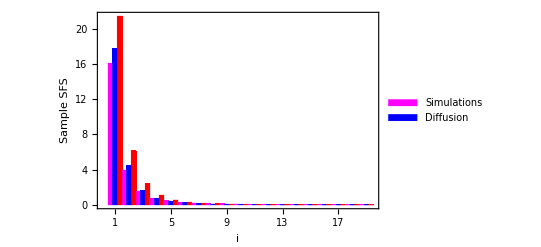

```mathematica
n=20;
N1= 1000;


mu=10^-7;
L=99999;
theta=4N1 mu L;

fun01=Interpolation[Data1sh2]
fun02=Interpolation[Data1sh5]
fun03=Interpolation[Data1sh8]
list01=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list02=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list03=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];

list6=Table[i,{i,1,n-1,1}];
BarChart[Transpose@{list01,list02, list03},ChartStyle->{ Magenta,Blue, Red},ChartLabels->{{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19", "20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True, FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends-> {"Simulations","Diffusion"}](*{Placed[{"c=0.001"},{0.1,0.7}], Placed[{"c=0.01"},{0.5,0.7}] , Placed[{"c=0.1"},{0.5,0.4}] }]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.29361×10^-7 and 6.37826×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.76724×10^-7 and 6.6608×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.30061×10^-7 and 7.06696×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.55467×10^-7 and 5.26827×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.18259×10^-7 and 4.5676×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.7768×10^-7 and 4.28147×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.91399×10^-7 and 3.10336×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3697×10^-7 and 3.73546×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.43107×10^-7 and 4.49734×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

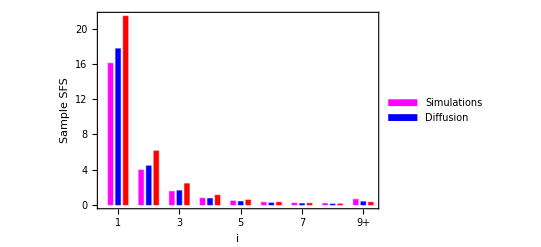

$Aborted

```mathematica
n=20;
N1=1000;

mu=10^-7;
L=99999;
theta=4 N1 mu L;

fun01=Interpolation[Data1sh2];
fun02=Interpolation[Data1sh5];
fun03=Interpolation[Data1sh8];

list01=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list02=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list03=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];


(*Summing the values from i=9 to n-1 and appending to the lists*)
sumList01=Append[Take[list01,8],Total[Drop[list01,8]]];
sumList02=Append[Take[list02,8],Total[Drop[list02,8]]];
sumList03=Append[Take[list03,8],Total[Drop[list03,8]]];


(*Adjusting the labels to include "9+"*)
labels=Join[Range[1,8],{"9+"}];

BarChart[Transpose@{sumList01,sumList02,sumList03},ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"Simulations","Diffusion"}]
```

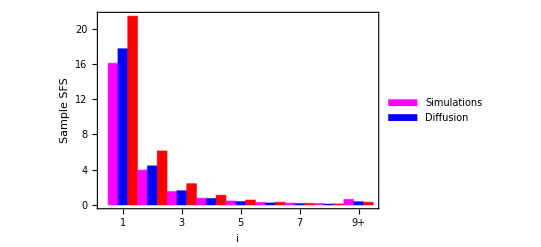

```mathematica
BarChart[Transpose@{sumList01,sumList02,sumList03},ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"Simulations","Diffusion"},BarSpacing->0]
```

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[sumList01];
list02Normalized=normalizeList[sumList02];
list03Normalized=normalizeList[sumList03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"h=0.2","h=0.5","h=0.8"},BarSpacing->0]
```

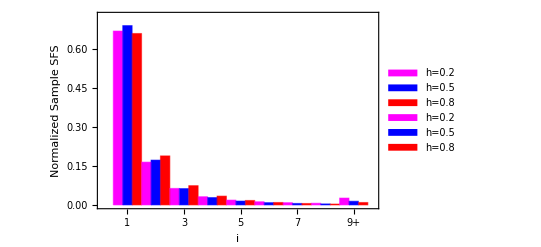

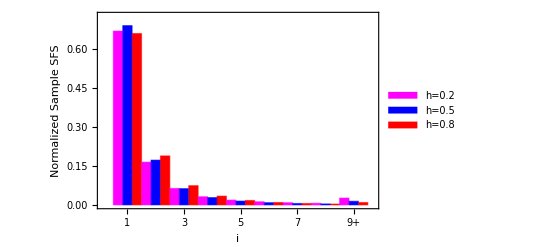
```mathematica
a1=-Graphics-;
```

```mathematica
Show[a1,pointsPlot]
```

-Graphics-

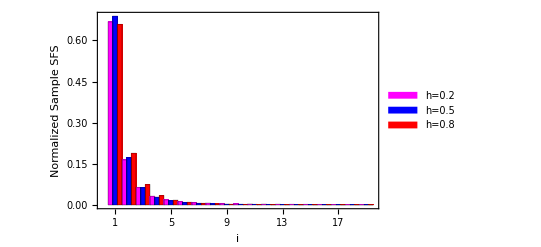

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[list01];
list02Normalized=normalizeList[list02];
list03Normalized=normalizeList[list03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{Magenta,Blue,Red},ChartLabels->{list6,None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"h=0.2","h=0.5","h=0.8"}]
```

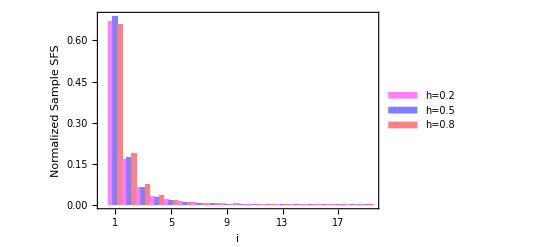

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[list01];
list02Normalized=normalizeList[list02];
list03Normalized=normalizeList[list03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{ Lighter[Magenta,0.5],Lighter[Blue,0.5],Lighter[Red,0.5]},ChartLabels->{list6,None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"h=0.2","h=0.5","h=0.8"}]
```

```mathematica
Total[lst]
```

```mathematica
theory points
```

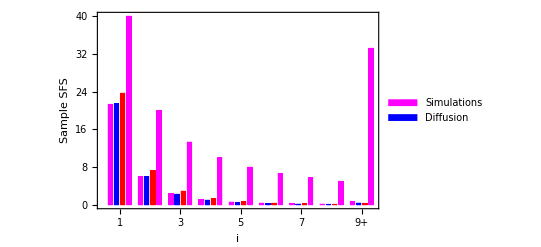

```mathematica
n=20;
N1=1000;

mu=10^-7;
L=99999;
theta=4 N1 mu L;

fun01=Interpolation[Datah2];
fun02=Interpolation[Datah5];
fun03=Interpolation[Datah8];

list01=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list02=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list03=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list04=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) theta/x,{x,0,1}, MaxRecursion->30],{i,1,n-1,1}]; 
(*Summing the values from i=9 to n-1 and appending to the lists*)
sumList01=Append[Take[list01,8],Total[Drop[list01,8]]];
sumList02=Append[Take[list02,8],Total[Drop[list02,8]]];
sumList03=Append[Take[list03,8],Total[Drop[list03,8]]];
sumList04=Append[Take[list04,8],Total[Drop[list04,8]]];
(*Adjusting the labels to include "9+"*)
labels=Join[Range[1,8],{"9+"}];

BarChart[Transpose@{sumList01,sumList02,sumList03,sumList04},ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"Simulations","Diffusion"}]
```

```mathematica
list03
```

{23.6751,7.23462,2.93538,1.3556,0.680202,0.365209,0.209091,0.127714,0.0832144,0.0576453,0.0421655,0.0322754,0.0256146,0.020906,0.017434,0.0147828,0.0126999,0.0110258,0.00965534}

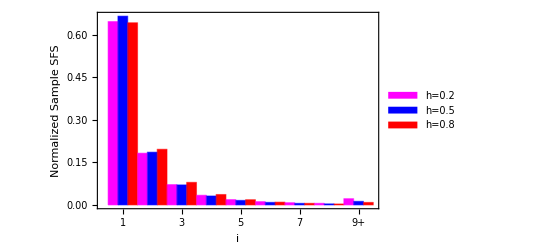

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[sumList01];
list02Normalized=normalizeList[sumList02];
list03Normalized=normalizeList[sumList03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"h=0.2","h=0.5","h=0.8"},BarSpacing->0]
```

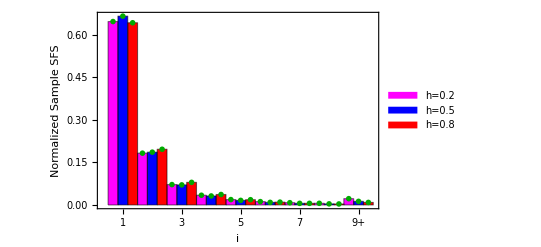

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[sumList01];
list02Normalized=normalizeList[sumList02];
list03Normalized=normalizeList[sumList03];

(*BarChart*)
barchart=BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"\!\(\* StyleBox[\"i\",\nFontSlant->\"Italic\"]\)","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"\!\(\* StyleBox[\"h\",\nFontSlant->\"Italic\"]\)\!\(\* StyleBox[\"=\",\nFontSlant->\"Italic\"]\)\!\(\* StyleBox[\"0.2\",\nFontSlant->\"Italic\"]\)","\!\(\* StyleBox[\"h\",\nFontSlant->\"Italic\"]\)\!\(\* StyleBox[\"=\",\nFontSlant->\"Italic\"]\)\!\(\* StyleBox[\"0.5\",\nFontSlant->\"Italic\"]\)","\!\(\* StyleBox[\"h\",\nFontSlant->\"Italic\"]\)\!\(\* StyleBox[\"=\",\nFontSlant->\"Italic\"]\)\!\(\* StyleBox[\"0.8\",\nFontSlant->\"Italic\"]\)"},BarSpacing->0];

(*Align x-values with bar positions*)
barWidth=1;(*Adjust the width for spacing*)xValues1=Table[1+3*(i-1),{i,1,9}];
xValues2=xValues1+barWidth;
xValues3=xValues1+2*barWidth;

(*Create data for the points*)
data1=Transpose[{xValues1,list01Normalized}];
data2=Transpose[{xValues2,list02Normalized}];
data3=Transpose[{xValues3,list03Normalized}];

(*Plot the points on top of the bars*)
pointsPlot=ListPlot[{data1,data2,data3},PlotStyle->{Darker[Green]},PlotMarkers->{"x",Medium},PlotRange->All,AxesOrigin->{0,0},Axes->False];

(*Combine the bar chart and points*)
Show[barchart,pointsPlot]
```

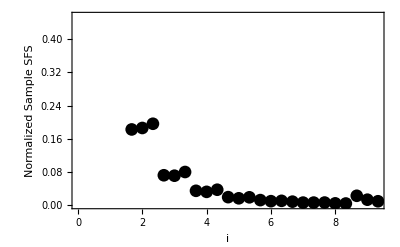
```mathematica
a2=-Graphics-;
```

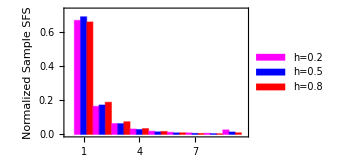
```mathematica
a1=-Graphics-;
```

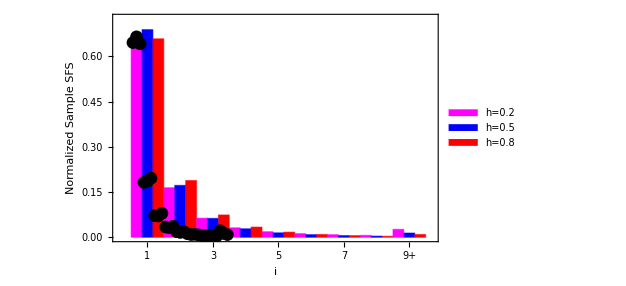

```mathematica
Show[a1,a2]
```

### Datah2 , diffusion for h = 0.2

```mathematica
xaxis=Table[x,{x,0.001,0.999,0.001}];
Transpose@{xaxis,gData}
```

```mathematica
Datah2={{0.001,39266.95242727942},{0.002,19277.30974563431},{0.003,12618.438317383463},{0.004,9292.209305711182},{0.005,7298.997369194367},{0.006,5972.261080927434},{0.007,5026.3401312472515},{0.008,4318.404628408104},{0.009000000000000001,3769.1048654676847},{0.010000000000000002,3330.8312270363804},{0.011,2973.286874158636},{0.012,2676.274086749299},{0.013000000000000001,2425.80998643996},{0.014000000000000002,2211.906949630229},{0.015,2027.2408553149814},{0.016,1866.3187399730384},{0.017,1724.940221315522},{0.018000000000000002,1599.8384474484005},{0.019000000000000003,1488.434430507165},{0.02,1388.6650801983483},{0.021,1298.860370612267},{0.022000000000000002,1217.6540069933924},{0.023,1143.9173968290575},{0.024,1076.7101281636278},{0.025,1015.2423331150043},{0.026000000000000002,958.8457367312596},{0.027000000000000003,906.951139432555},{0.028,859.0707246419983},{0.029,814.7840269046488},{0.030000000000000002,773.7267063807581},{0.031,735.5814960158195},{0.032,700.0708461143653},{0.033,666.9509062621557},{0.034,636.0065692603148},{0.035,607.047364669009},{0.036000000000000004,579.9040367588037},{0.037000000000000005,554.4256773871501},{0.038,530.4773115769384},{0.039,507.9378545428923},{0.04,486.6983751624202},{0.041,466.6606135711237},{0.042,447.735710528846},{0.043000000000000003,429.8431140819739},{0.044000000000000004,412.9096353157602},{0.045,396.8686300048764},{0.046,381.6592870037563},{0.047,367.22600747930744},{0.048,353.51786173813264},{0.049,340.48811256332266},{0.05,328.09379574946917},{0.051000000000000004,316.29534998515305},{0.052000000000000005,305.0562894399688},{0.053000000000000005,294.3429134158519},{0.054,284.1240482580705},{0.055,274.37081742009417},{0.056,265.0564361630973},{0.057,256.1560278647807},{0.058,247.64645932948144},{0.059000000000000004,239.5061928451723},{0.060000000000000005,231.71515303353695},{0.061,224.2546067955466},{0.062,217.1070548740045},{0.063,210.256133742275},{0.064,203.6865266897632},{0.065,197.38388311371511},{0.066,191.33474514696434},{0.067,185.52648085517328},{0.068,179.94722332728938},{0.069,174.5858150613453},{0.07,169.43175711606025},{0.07100000000000001,164.47516255836632},{0.07200000000000001,159.70671378919218},{0.07300000000000001,155.11762337560796},{0.074,150.69959805764077},{0.075,146.44480563344874},{0.076,142.34584445773547},{0.077,138.3957153158272},{0.078,134.58779546020605},{0.079,130.91581461787945},{0.08,127.3738327961311},{0.081,123.95621973122867},{0.082,120.65763583982836},{0.083,117.47301454633475},{0.084,114.39754587154498},{0.085,111.42666117869886},{0.08600000000000001,108.55601898271999},{0.08700000000000001,105.7814917370951},{0.08800000000000001,103.099153520618},{0.089,100.50526855321365},{0.09,97.99628047635089},{0.091,95.56880233922199},{0.092,93.21960723698034},{0.093,90.94561955195036},{0.094,88.74390675289852},{0.095,86.61167171123819},{0.096,84.5462454964671},{0.097,82.54508061624604},{0.098,80.6057446693512},{0.099,78.72591438229887},{0.1,76.90337000277846},{0.101,75.13599002515633},{0.10200000000000001,73.42174622525359},{0.10300000000000001,71.7586989833722},{0.10400000000000001,70.14499287615969},{0.10500000000000001,68.57885251938264},{0.106,67.05857864503179},{0.107,65.58254439742096},{0.108,64.14919183407831},{0.109,62.75702861827022},{0.11,61.4046248909555},{0.111,60.09061031084707},{0.112,58.813671252066236},{0.113,57.572548149620324},{0.114,56.36603298361832},{0.115,55.192966893772756},{0.116,54.05223791631748},{0.117,52.94277883601003},{0.11800000000000001,51.86356514638377},{0.11900000000000001,50.81361311187451},{0.12000000000000001,49.79197792587137},{0.121,48.79775195913476},{0.122,47.83006309338882},{0.123,46.88807313523363},{0.124,45.97097630583483},{0.125,45.07799780213974},{0.126,44.21749316522751},{0.127,43.37948306463195},{0.128,42.563242670052524},{0.129,41.768074096773375},{0.13,40.99330531606155},{0.131,40.238289115106014},{0.132,39.50240210386712},{0.133,38.78504376636497},{0.134,38.08563555408193},{0.135,37.40362001929297},{0.136,36.73845998626563},{0.137,36.08963775839179},{0.138,35.45665435942557},{0.139,34.839028807107},{0.14,34.236297417549},{0.14100000000000001,33.64801313885753},{0.14200000000000002,33.07374491254105},{0.14300000000000002,32.513077061345626},{0.14400000000000002,31.96560870222835},{0.14500000000000002,31.430953183252573},{0.146,30.90873754325476},{0.147,30.398601993195733},{0.148,29.900199418167837},{0.149,29.413194899084175},{0.15,28.93726525312878},{0.151,28.472098592094774},{0.152,28.017393897783677},{0.153,27.57286061368229},{0.154,27.138218252174163},{0.155,26.71319601658098},{0.156,26.297532437365398},{0.157,25.890975021860733},{0.158,25.493279916925207},{0.159,25.104211583948583},{0.16,24.7235424856676},{0.161,24.35105278427376},{0.162,23.986530050322212},{0.163,23.629768981974905},{0.164,23.28057113413361},{0.165,22.938744657040125},{0.166,22.604104043941213},{0.167,22.277732424708567},{0.168,21.96068873606081},{0.169,21.650253000527407},{0.17,21.346247623879286},{0.171,21.048500578759697},{0.17200000000000001,20.756845225643676},{0.17300000000000001,20.47112013988291},{0.17400000000000002,20.19116894459004},{0.17500000000000002,19.916840149127857},{0.17600000000000002,19.647986992979313},{0.177,19.384467294784603},{0.178,19.126143306340953},{0.179,18.872881571370076},{0.18,18.62455278886669},{0.181,18.38103168085},{0.182,18.14219686434755},{0.183,17.907930727448658},{0.184,17.67811930927133},{0.185,17.452652183693658},{0.186,17.23142234670676},{0.187,17.014326107252746},{0.188,16.801262981416702},{0.189,16.592135589847498},{0.19,16.386849558287174},{0.191,16.185313421094026},{0.192,15.987438527648976},{0.193,15.793138951539639},{0.194,15.602331402420551},{0.195,15.414935140452576},{0.196,15.230871893228},{0.197,15.050065775091985},{0.198,14.872443208774422},{0.199,14.697932849249794},{0.2,14.526465509745812},{0.201,14.357974089824976},{0.202,14.192393505465798},{0.203,14.029660621073793},{0.20400000000000001,13.86971418335462},{0.20500000000000002,13.712494756984748},{0.20600000000000002,13.557944662017192},{0.20700000000000002,13.406007912962586},{0.20800000000000002,13.25663015948786},{0.20900000000000002,13.110661812920016},{0.21,12.967588341887904},{0.211,12.826901047699618},{0.212,12.688546042661992},{0.213,12.552470909917133},{0.214,12.418624663485488},{0.215,12.286957709381435},{0.216,12.157421807766323},{0.217,12.029970036104997},{0.218,11.904556753293345},{0.219,11.78113756472532},{0.22,11.659669288269235},{0.221,11.540109921124126},{0.222,11.422418607528027},{0.223,11.306555607291015},{0.224,11.192482265126912},{0.225,11.080160980758304},{0.226,10.969555179770621},{0.227,10.860629285191717},{0.228,10.753348689774286},{0.229,10.647679728959224},{0.23,10.543589654498813},{0.231,10.441046608719295},{0.232,10.34001959940316},{0.233,10.240478475272079},{0.234,10.14239390205213},{0.23500000000000001,10.045737339103518},{0.23600000000000002,9.95048101659764},{0.23700000000000002,9.856597913224897},{0.23800000000000002,9.76406173441721},{0.23900000000000002,9.672846891069714},{0.24000000000000002,9.582928478746686},{0.241,9.49428225735715},{0.242,9.406884631286147},{0.243,9.320712629968119},{0.244,9.235743888889264},{0.245,9.151956631006131},{0.246,9.069329648568212},{0.247,8.987842285332574},{0.248,8.907474419159021},{0.249,8.82820644497467},{0.25,8.750019258097039},{0.251,8.673364693626324},{0.252,8.597749635125242},{0.253,8.523154415479931},{0.254,8.44955983412423},{0.255,8.376947146054134},{0.256,8.305298051084916},{0.257,8.234594683344275},{0.258,8.164819600994862},{0.259,8.095955776179897},{0.26,8.027986585185724},{0.261,7.960895798815344},{0.262,7.89466757296712},{0.263,7.829286439413094},{0.264,7.764737296771441},{0.265,7.701005401667791},{0.266,7.638076360080327},{0.267,7.575936118863651},{0.268,7.514570957446639},{0.269,7.453967479699584},{0.27,7.394112605966086},{0.271,7.334993565255289},{0.272,7.276597887590187},{0.273,7.218913396507833},{0.274,7.161928201707412},{0.275,7.105630691842273},{0.276,7.05000952745209},{0.277,6.995053634031474},{0.278,6.940752195231406},{0.279,6.887094646190042},{0.28,6.8340706669894455},{0.281,6.781670176234974},{0.28200000000000003,6.729883324754118},{0.28300000000000003,6.678700489411628},{0.28400000000000003,6.62811226703794},{0.28500000000000003,6.578109468467938},{0.28600000000000003,6.528683112687145},{0.28700000000000003,6.479824421082608},{0.28800000000000003,6.4315248117957085},{0.28900000000000003,6.3837758941742955},{0.29,6.336569463321527},{0.291,6.28989749473894},{0.292,6.243806635999398},{0.293,6.198343006897938},{0.294,6.153389212240725},{0.295,6.108937212236586},{0.296,6.064979131093167},{0.297,6.021507253633834},{0.298,5.978514021977427},{0.299,5.93599203227928},{0.3,5.893934031532082},{0.301,5.852332914425055},{0.302,5.8111817202601435},{0.303,5.7704736299237425},{0.304,5.730201962912722},{0.305,5.690360174413366},{0.306,5.65094185243203},{0.307,5.611940714976209},{0.308,5.573350607284905},{0.309,5.535165499107008},{0.31,5.497379482026666},{0.311,5.4599867668344215},{0.312,5.42298168094312},{0.313,5.3863586658474505},{0.314,5.350112274626156},{0.315,5.314237169485848},{0.316,5.278728119345492},{0.317,5.243579997460544},{0.318,5.208787779085889},{0.319,5.174346539176572},{0.32,5.14025145012551},{0.321,5.106497779537268},{0.322,5.073080888037073},{0.323,5.03999622711423},{0.324,5.00723933699914},{0.325,4.974805844573109},{0.326,4.942691461310213},{0.327,4.910891981250431},{0.328,4.879403279003332},{0.329,4.848221307781595},{0.33,4.817342097463659},{0.331,4.7867617526848045},{0.332,4.75647645095603},{0.333,4.726482440810032},{0.334,4.696814334674163},{0.335,4.667449067480943},{0.336,4.638363665302839},{0.337,4.609554401096296},{0.338,4.58101761284332},{0.339,4.55274970237259},{0.34,4.524747134199411},{0.341,4.497006434384058},{0.342,4.469524189408135},{0.343,4.442297045068532},{0.34400000000000003,4.41532170538865},{0.34500000000000003,4.388594931546458},{0.34600000000000003,4.362113540819081},{0.34700000000000003,4.335874405543509},{0.34800000000000003,4.309874452093132},{0.34900000000000003,4.284110659869706},{0.35000000000000003,4.258580060310478},{0.35100000000000003,4.233279735910084},{0.35200000000000004,4.208206819256955},{0.353,4.183358492083885},{0.354,4.158731984332471},{0.355,4.134324573231131},{0.356,4.110133582386402},{0.357,4.086156380887223},{0.358,4.06239038242196},{0.359,4.038833044407845},{0.36,4.015481867132624},{0.361,3.992334392908095},{0.362,3.969388205235324},{0.363,3.9466409279812567},{0.364,3.924090224566505},{0.365,3.901733797164049},{0.366,3.879569385908627},{0.367,3.857594768116585},{0.368,3.835807757515954},{0.369,3.8142062034865387},{0.37,3.79278799030979},{0.371,3.771551036428266},{0.372,3.7504932937144573},{0.373,3.7296127467487765},{0.374,3.7089074121065195},{0.375,3.6883753376535857},{0.376,3.668035443183135},{0.377,3.6478648619431846},{0.378,3.627861642828774},{0.379,3.608023864065716},{0.38,3.588349632742593},{0.381,3.5688370843493207},{0.382,3.5494843823221665},{0.383,3.530289717595084},{0.384,3.5112513081572443},{0.385,3.492367398616646},{0.386,3.47363625976967},{0.387,3.455056188176481},{0.388,3.4366255057421484},{0.389,3.4183425593033743},{0.39,3.4002057202207263},{0.391,3.382213383976257},{0.392,3.364363969776413},{0.393,3.346655920160117},{0.394,3.329087700611941},{0.395,3.3116577991802427},{0.396,3.294364726100196},{0.397,3.277207013421596},{0.398,3.2601832146413554},{0.399,3.243291904340597},{0.4,3.2265316778262516},{0.401,3.209901150777066},{0.402,3.1933989588939466},{0.403,3.177023757554535},{0.404,3.1607742214719443},{0.405,3.1446490443575663},{0.406,3.1286469385878726},{0.40700000000000003,3.112766634875118},{0.40800000000000003,3.097006881941886},{0.40900000000000003,3.081366446199383},{0.41000000000000003,3.0658441114294086},{0.41100000000000003,3.05043867846993},{0.41200000000000003,3.0351489649041943},{0.41300000000000003,3.0199738047532803},{0.41400000000000003,3.0049120481720557},{0.41500000000000004,2.9899625611484364},{0.41600000000000004,2.975124225205901},{0.41700000000000004,2.9603986041226276},{0.418,2.945787256600111},{0.419,2.9312837383617634},{0.42,2.916886956115585},{0.421,2.902595830935464},{0.422,2.888409298057506},{0.423,2.8743263066789115},{0.424,2.8603458197593365},{0.425,2.846466813824722},{0.426,2.8326882787735075},{0.427,2.8190092176852257},{0.428,2.8054286466314053},{0.429,2.7919455944887557},{0.43,2.7785591027545764},{0.431,2.765268225364381},{0.432,2.7520720285116496},{0.433,2.7389695904697184},{0.434,2.725960001415729},{0.435,2.713042363256629},{0.436,2.7002157894571526},{0.437,2.6874794048697916},{0.438,2.674832345566665},{0.439,2.662273758673304},{0.44,2.6498028022042717},{0.441,2.6374186449006207},{0.442,2.6251204660691254},{0.443,2.612907455423282},{0.444,2.6007788129260097},{0.445,2.5887337486340614},{0.446,2.576771482544072},{0.447,2.56489124444025},{0.448,2.5530922737436397},{0.449,2.541373819362975},{0.45,2.5297351395470375},{0.451,2.5181755017385457},{0.452,2.5066941824294924},{0.453,2.4952904670179525},{0.454,2.483963649666291},{0.455,2.4727130331607663},{0.456,2.4615379287724974},{0.457,2.450437656119766},{0.458,2.439411543031622},{0.459,2.4284611378586995},{0.46,2.4175846671321644},{0.461,2.4067803614351733},{0.462,2.3960475659591967},{0.463,2.3853856335470547},{0.464,2.374793924595525},{0.465,2.364271806959064},{0.466,2.353818655854577},{0.467,2.343433853767258},{0.468,2.3331167903574475},{0.46900000000000003,2.3228668623685285},{0.47000000000000003,2.3126834735357997},{0.47100000000000003,2.3025660344963477},{0.47200000000000003,2.2925139626998723},{0.47300000000000003,2.282526682320475},{0.47400000000000003,2.2726036241693595},{0.47500000000000003,2.2627442256084715},{0.47600000000000003,2.2529479304650173},{0.47700000000000004,2.2432141889468844},{0.47800000000000004,2.2335424575589147},{0.47900000000000004,2.2239321990200485},{0.48000000000000004,2.21438288218129},{0.481,2.204893981944511},{0.482,2.1954649791820495},{0.483,2.1860953606571214},{0.484,2.17678461894499},{0.485,2.1675322523549214},{0.486,2.1583377648528805},{0.487,2.1492006659849707},{0.488,2.140120470801596},{0.489,2.1310966997823377},{0.49,2.122128878761527},{0.491,2.113216538854508},{0.492,2.104359216384565},{0.493,2.0955564528105195},{0.494,2.0868077946549675},{0.495,2.0781127934331574},{0.496,2.069471005582486},{0.497,2.060881992392612},{0.498,2.052345319936159},{0.499,2.0438605590000174},{0.5,2.0354272850172124},{0.501,2.0270465945468437},{0.502,2.018716549048453},{0.503,2.0104367309887574},{0.504,2.002206727242797},{0.505,1.994026129043104},{0.506,1.9858945319293881},{0.507,1.9778115356987314},{0.508,1.9697767443562832},{0.509,1.9617897660664423},{0.51,1.9538502131045234},{0.511,1.945957701808902},{0.512,1.93811185253362},{0.513,1.9303122896014575},{0.514,1.9225586412574505},{0.515,1.9148505396228575},{0.516,1.90718762064956},{0.517,1.8995695240748942},{0.518,1.8919958933769037},{0.519,1.8844663757300097},{0.52,1.8769806219610845},{0.521,1.8695382865059322},{0.522,1.8621390273661587},{0.523,1.8547825060664314},{0.524,1.847468387612118},{0.525,1.840196340447302},{0.526,1.8329660364131595},{0.527,1.8257771507067062},{0.528,1.8186293618398888},{0.529,1.81152235159903},{0.53,1.8044558050046156},{0.531,1.797429410271412},{0.532,1.7904428587689194},{0.533,1.7834958449821425},{0.534,1.7765880664726805},{0.535,1.7697192238401285},{0.536,1.7628890206837833},{0.537,1.7560971635646478},{0.538,1.7493433619677285},{0.539,1.7426273282646239},{0.54,1.735948777676388},{0.541,1.729307428236677},{0.542,1.7227032562733586},{0.543,1.7161362399773497},{0.544,1.7096055915661217},{0.545,1.7031110366733706},{0.546,1.6966523035778718},{0.547,1.6902291231755633},{0.548,1.6838412289518896},{0.549,1.6774883569543955},{0.55,1.671170245765567},{0.551,1.664886636475919},{0.552,1.658637272657321},{0.553,1.6524219003365606},{0.554,1.646240267969138},{0.555,1.6400921264132917},{0.556,1.6339772289042465},{0.557,1.6278953310286866},{0.558,1.6218461906994412},{0.559,1.6158295681303882},{0.56,1.6098452258115685},{0.561,1.6038929284845038},{0.562,1.597972443117723},{0.5630000000000001,1.5920835388824812},{0.5640000000000001,1.5862259871286843},{0.5650000000000001,1.5803995613609976},{0.5660000000000001,1.5746040372151515},{0.5670000000000001,1.5688391924344285},{0.5680000000000001,1.5631048068463347},{0.5690000000000001,1.557400662339453},{0.5700000000000001,1.5517265428404676},{0.5710000000000001,1.5460822342913685},{0.5720000000000001,1.5404675246268191},{0.5730000000000001,1.5348822037516938},{0.5740000000000001,1.5293260635187806},{0.5750000000000001,1.5237988977066401},{0.5760000000000001,1.5183005019976243},{0.5770000000000001,1.5128306739560484},{0.578,1.5073892130065152},{0.579,1.5019759204123824},{0.58,1.4965905992543829},{0.581,1.49123305440938},{0.582,1.4859030925292633},{0.583,1.4806005220199805},{0.584,1.4753254354368484},{0.585,1.4700775027280566},{0.586,1.4648563944716169},{0.587,1.4596619240637891},{0.588,1.4544939065578832},{0.589,1.4493521586481486},{0.59,1.444236498653796},{0.591,1.4391467465031498},{0.592,1.4340827237179334},{0.593,1.4290442533976793},{0.594,1.424031160204265},{0.595,1.4190432703465758},{0.596,1.4140804115652859},{0.597,1.409142413117759},{0.598,1.4042291057630705},{0.599,1.3993403217471392},{0.6,1.394475894787981},{0.601,1.3896356600610644},{0.602,1.384819454184786},{0.603,1.380027115206046},{0.604,1.3752584825859338},{0.605,1.3705133971855181},{0.606,1.3657917012517373},{0.607,1.361093238403391},{0.608,1.356417853617232},{0.609,1.3517653932141513},{0.61,1.3471357048454622},{0.611,1.342528637479275},{0.612,1.337944041386964},{0.613,1.3333817681297215},{0.614,1.3288416705452057},{0.615,1.3243236027342657},{0.616,1.3198274200477604},{0.617,1.3153529790734502},{0.618,1.3109001376229765},{0.619,1.3064687547189167},{0.62,1.3020586905819171},{0.621,1.2976698066179007},{0.622,1.293301965405348},{0.623,1.2889550306826523},{0.624,1.284628867335541},{0.625,1.280323341384569},{0.626,1.2760385724284997},{0.627,1.2717741757187204},{0.628,1.2675300195199508},{0.629,1.2633059731825869},{0.63,1.259101907132941},{0.631,1.2549176928635566},{0.632,1.2507532029235962},{0.633,1.2466083109093025},{0.634,1.2424828914545285},{0.635,1.2383768202213368},{0.636,1.234289973890671},{0.637,1.2302222301530887},{0.638,1.2261734676995666},{0.639,1.222143566212365},{0.64,1.2181324063559626},{0.641,1.214139869768047},{0.642,1.2101658390505712},{0.643,1.2062101977608715},{0.644,1.2022728304028423},{0.645,1.1983536224181688},{0.646,1.1944524601776205},{0.647,1.1905692309723968},{0.648,1.1867038230055302},{0.649,1.1828561253833427},{0.65,1.1790260281069562},{0.651,1.1752134220638504},{0.652,1.1714181990194783},{0.653,1.1676402516089257},{0.654,1.1638794733286209},{0.655,1.1601357585280927},{0.656,1.1564090024017744},{0.657,1.1526991009808514},{0.658,1.1490059511251558},{0.659,1.1453294505151013},{0.66,1.1416694976436632},{0.661,1.1380259918083955},{0.662,1.134398833103491},{0.663,1.1307879224118795},{0.664,1.1271931613973616},{0.665,1.1236144524967813},{0.666,1.120051698912234},{0.667,1.1165048580353283},{0.668,1.1129738880734572},{0.669,1.1094585871111986},{0.67,1.105958860643928},{0.671,1.1024746148932563},{0.672,1.0990057568009672},{0.673,1.0955521940229955},{0.674,1.09211383492345},{0.675,1.0886905885686722},{0.676,1.0852823647213379},{0.677,1.0818890738345992},{0.678,1.078510627046261},{0.679,1.0751469361729986},{0.68,1.0717979137046123},{0.681,1.0684634727983158},{0.682,1.0651435272730638},{0.683,1.0618379916039118},{0.684,1.0585467809164126},{0.685,1.0552698109810454},{0.686,1.0520069982076767},{0.687,1.0487582596400564},{0.6880000000000001,1.0455235129503437},{0.6890000000000001,1.0423026764336638},{0.6900000000000001,1.0390956690026945},{0.6910000000000001,1.0359024101822856},{0.6920000000000001,1.0327228201041028},{0.6930000000000001,1.0295568195013023},{0.6940000000000001,1.0264043297032328},{0.6950000000000001,1.0232652726301634},{0.6960000000000001,1.020139570788038},{0.6970000000000001,1.0170271472632562},{0.6980000000000001,1.0139279257174756},{0.6990000000000001,1.010841830382442},{0.7000000000000001,1.0077687860548414},{0.7010000000000001,1.0047087180911722},{0.7020000000000001,1.0016615524026429},{0.7030000000000001,0.9986272154500883},{0.7040000000000001,0.9956056342389066},{0.705,0.9925967363140167},{0.706,0.9896004497548331},{0.707,0.9866167031702603},{0.708,0.9836454256937032},{0.709,0.9806866188399044},{0.71,0.9777401769086355},{0.711,0.9748059942470674},{0.712,0.9718840015720981},{0.713,0.9689741300994152},{0.714,0.9660763115396216},{0.715,0.963190478094388},{0.716,0.9603165624526259},{0.717,0.9574544977866876},{0.718,0.9546042177485866},{0.719,0.9517656564662431},{0.72,0.9489387485397501},{0.721,0.9461234290376617},{0.722,0.9433196334933039},{0.723,0.9405272979011052},{0.724,0.937746358712948},{0.725,0.9349767528345405},{0.726,0.9322184176218077},{0.727,0.9294712908773021},{0.728,0.9267353108466322},{0.729,0.924010416214911},{0.73,0.9212965461032199},{0.731,0.9185936400650926},{0.732,0.9159016380830132},{0.733,0.9132204805649328},{0.734,0.9105501083408006},{0.735,0.907890462659112},{0.736,0.9052414851834696},{0.737,0.9026031179891596},{0.738,0.8999753035597436},{0.739,0.8973579847836609},{0.74,0.8947511049508458},{0.741,0.892154607749358},{0.742,0.8895684372620214},{0.743,0.8869925379630786},{0.744,0.8844268547148534},{0.745,0.8818713327644236},{0.746,0.879325917740306},{0.747,0.8767905556491479},{0.748,0.8742651928724275},{0.749,0.8717497761631638},{0.75,0.8692442526426333},{0.751,0.8667486464146692},{0.752,0.8642628287910251},{0.753,0.8617867476491846},{0.754,0.8593203512197638},{0.755,0.8568635880839645},{0.756,0.8544164071710398},{0.757,0.8519787577557768},{0.758,0.8495505894559932},{0.759,0.8471318522300478},{0.76,0.8447224963743649},{0.761,0.8423224725209729},{0.762,0.8399317316350552},{0.763,0.8375502250125154},{0.764,0.8351779042775548},{0.765,0.8328147213802608},{0.766,0.8304606285942105},{0.767,0.8281155785140825},{0.768,0.8257795240532835},{0.769,0.8234524184415835},{0.77,0.8211342152227635},{0.771,0.8188248682522726},{0.772,0.8165243316948959},{0.773,0.8142325600224318},{0.774,0.8119495080113797},{0.775,0.8096751307406354},{0.776,0.807409383589196},{0.777,0.8051522222338737},{0.778,0.8029036026470172},{0.779,0.8006634810942397},{0.78,0.7984318141321569},{0.781,0.796208558606128},{0.782,0.7939936716480078},{0.783,0.7917871106739004},{0.784,0.7895888333819218},{0.785,0.787398797749966},{0.786,0.7852169620334769},{0.787,0.7830432847632237},{0.788,0.7808777247430813},{0.789,0.7787202410478128},{0.79,0.7765707930208557},{0.791,0.7744293402721117},{0.792,0.7722958618795079},{0.793,0.7701703373642776},{0.794,0.7680526886147503},{0.795,0.7659428760370615},{0.796,0.7638408602905319},{0.797,0.7617466022859724},{0.798,0.7596600631839975},{0.799,0.7575812043933506},{0.8,0.7555099875692348},{0.801,0.7534463746116564},{0.802,0.7513903276637744},{0.803,0.7493418091102599},{0.804,0.747300781575664},{0.805,0.7452672079227934},{0.806,0.7432410512510934},{0.807,0.7412222748950399},{0.808,0.7392108424225382},{0.809,0.7372067176333285},{0.81,0.7352098645573999},{0.811,0.7332202474534095},{0.812,0.7312378308071102},{0.8130000000000001,0.7292625793297816},{0.8140000000000001,0.7272944579566708},{0.8150000000000001,0.7253334318454357},{0.8160000000000001,0.7233794663745959},{0.8170000000000001,0.7214325271419882},{0.8180000000000001,0.7194925799632266},{0.8190000000000001,0.7175595908701673},{0.8200000000000001,0.7156335261093795},{0.8210000000000001,0.7137143521406174},{0.8220000000000001,0.7118020356352986},{0.8230000000000001,0.7098965434749845},{0.8240000000000001,0.7079978427498649},{0.8250000000000001,0.7061059007572436},{0.8260000000000001,0.7042206850000285},{0.8270000000000001,0.7023421631852232},{0.8280000000000001,0.7004703032224181},{0.8290000000000001,0.6986050732222868},{0.8300000000000001,0.6967464414950795},{0.8310000000000001,0.6948943765491192},{0.8320000000000001,0.6930488470892978},{0.8330000000000001,0.6912098220155695},{0.834,0.6893773013424419},{0.835,0.6875512391398484},{0.836,0.6857315892984718},{0.837,0.68391832128504},{0.838,0.6821114047511168},{0.839,0.6803108095319598},{0.84,0.6785165056453867},{0.841,0.6767284632906462},{0.842,0.6749466528472969},{0.843,0.6731710448740917},{0.844,0.6714016101078688},{0.845,0.6696383194624481},{0.846,0.6678811440275337},{0.847,0.6661300550676232},{0.848,0.664385024020921},{0.849,0.6626460224982583},{0.85,0.6609130222820176},{0.851,0.6591859953250627},{0.852,0.6574649137496748},{0.853,0.6557497498464908},{0.854,0.6540404760734494},{0.855,0.6523370650547394},{0.856,0.6506394895797538},{0.857,0.6489477226020468},{0.858,0.647261737238296},{0.859,0.6455815067672681},{0.86,0.6439070046287871},{0.861,0.6422382044227072},{0.862,0.6405750799078884},{0.863,0.6389176050011748},{0.864,0.6372657537763755},{0.865,0.6356195004632486},{0.866,0.6339788194464867},{0.867,0.6323436852647043},{0.868,0.6307140726094274},{0.869,0.6290899563240833},{0.87,0.6274713114029928},{0.871,0.6258581129903623},{0.872,0.6242503363792754},{0.873,0.6226479570106863},{0.874,0.6210509504724111},{0.875,0.6194592924981186},{0.876,0.6178729980775545},{0.877,0.6162920044976999},{0.878,0.6147162877628845},{0.879,0.6131458240154962},{0.88,0.6115805895351981},{0.881,0.6100205607381479},{0.882,0.6084657141762262},{0.883,0.6069160265362658},{0.884,0.6053714746392895},{0.885,0.6038320354397522},{0.886,0.6022976860247871},{0.887,0.6007684036134584},{0.888,0.5992441655560183},{0.889,0.5977249493331689},{0.89,0.59621073255533},{0.891,0.59470149296191},{0.892,0.5931972084205843},{0.893,0.5916978569265762},{0.894,0.5902034166019432},{0.895,0.5887138656948696},{0.896,0.5872291825789622},{0.897,0.5857493457525503},{0.898,0.5842743338379925},{0.899,0.5828041255809864},{0.9,0.5813386998498827},{0.901,0.5798780356350063},{0.902,0.578422112047978},{0.903,0.5769709083210444},{0.904,0.5755244038064105},{0.905,0.5740825779755759},{0.906,0.5726454104186782},{0.907,0.5712128808438375},{0.908,0.5697849690765074},{0.909,0.5683616550588293},{0.91,0.5669429188489914},{0.911,0.5655287406205921},{0.912,0.5641191006620064},{0.913,0.5627139793757586},{0.914,0.5613133572778967},{0.915,0.5599172149973722},{0.916,0.558525533275425},{0.917,0.5571382929649691},{0.918,0.5557554750299867},{0.919,0.5543770605449216},{0.92,0.5530030306940809},{0.921,0.5516333667710368},{0.922,0.5502680501780357},{0.923,0.548907062425408},{0.924,0.5475503851309844},{0.925,0.5461980000195144},{0.926,0.5448498889220882},{0.927,0.5435060337755645},{0.928,0.5421664166220004},{0.929,0.5408310196080833},{0.93,0.5394998249845714},{0.931,0.5381728151057327},{0.932,0.5368499724287897},{0.933,0.5355312795133689},{0.934,0.5342167190209516},{0.935,0.5329062737143295},{0.936,0.5315999264570637},{0.937,0.5302976602129466},{0.9380000000000001,0.5289994580454677},{0.9390000000000001,0.527705303117283},{0.9400000000000001,0.5264151786896878},{0.9410000000000001,0.5251290681220914},{0.9420000000000001,0.5238469548714976},{0.9430000000000001,0.5225688224919862},{0.9440000000000001,0.5212946546342001},{0.9450000000000001,0.5200244350448329},{0.9460000000000001,0.5187581475661222},{0.9470000000000001,0.5174957761353449},{0.9480000000000001,0.5162373047843161},{0.9490000000000001,0.5149827176388906},{0.9500000000000001,0.5137319989184681},{0.9510000000000001,0.5124851329355018},{0.9520000000000001,0.5112421040950091},{0.9530000000000001,0.5100028968940863},{0.9540000000000001,0.5087674959214258},{0.9550000000000001,0.5075358858568366},{0.9560000000000001,0.5063080514707682},{0.9570000000000001,0.5050839776238361},{0.9580000000000001,0.5038636492663516},{0.9590000000000001,0.5026470514378553},{0.9600000000000001,0.5014341692666501},{0.961,0.5002249879693412},{0.962,0.4990194928503769},{0.963,0.49781766930159144},{0.964,0.49661950280175293},{0.965,0.4954249789161123},{0.966,0.494234083295956},{0.967,0.49304680167816073},{0.968,0.4918631198847522},{0.969,0.4906830238224643},{0.97,0.4895064994823039},{0.971,0.4883335329391161},{0.972,0.48716411035115326},{0.973,0.4859982179596462},{0.974,0.48483584208837843},{0.975,0.48367696914326275},{0.976,0.48252158561192054},{0.977,0.4813696780632633},{0.978,0.4802212331470773},{0.979,0.47907623759361084},{0.98,0.4779346782131632},{0.981,0.47679654189567644},{0.982,0.4756618156103313},{0.983,0.47453048640514217},{0.984,0.4734025414065578},{0.985,0.47227796781906317},{0.986,0.47115675292478293},{0.987,0.47003888408308897},{0.988,0.4689243487302088},{0.989,0.4678131343788378},{0.99,0.46670522861775204},{0.991,0.46560061911142525},{0.992,0.4644992935996467},{0.993,0.4634012398971426},{0.994,0.46230644589319825},{0.995,0.46121489955128414},{0.996,0.46012658890868363},{0.997,0.45904150207612177},{0.998,0.4579596272373986},{0.999,0.45688095264902245}};
```

### Transpose[{xaxis, averageGData1}] , diffusion data for h = 0.5

```mathematica
Datah5={{0.001,39234.490961899515},{0.002,19272.14351566967},{0.003,12622.057520002501},{0.004,9299.991410204646},{0.005,7309.097252417598},{0.006,5983.759383365962},{0.007,5038.714216029436},{0.008,4331.330191055229},{0.009000000000000001,3782.3677605572084},{0.010000000000000002,3344.283381631027},{0.011,2986.8222406750415},{0.012,2689.8146155469344},{0.013000000000000001,2439.296993644507},{0.014000000000000002,2225.2955679485076},{0.015,2040.4963346452107},{0.016,1879.4139041375659},{0.017,1737.853672873157},{0.018000000000000002,1612.5532712268327},{0.019000000000000003,1500.9372383652405},{0.02,1400.9452946495649},{0.021,1310.9096790637243},{0.022000000000000002,1229.4659400690039},{0.023,1155.4869984074915},{0.024,1088.033694202573},{0.025,1026.317202753296},{0.026000000000000002,969.6701236050008},{0.027000000000000003,917.5239942690358},{0.028,869.3916224292651},{0.029,824.8530735523381},{0.030000000000000002,783.5444609741658},{0.031,745.1489056453853},{0.032,709.3891909228903},{0.033,676.0217528521976},{0.034,644.8317309866377},{0.035,615.6288676359949},{0.036000000000000004,588.2440905721943},{0.037000000000000005,562.5266498893383},{0.038,538.341706937018},{0.039,515.5682941855343},{0.04,494.0975811099326},{0.041,473.8313938457258},{0.042,454.6809463210164},{0.043000000000000003,436.5657484386163},{0.044000000000000004,419.41266314110936},{0.045,403.15508919927987},{0.046,387.7322505920788},{0.047,373.0885766027866},{0.048,359.17315940191384},{0.049,345.9392780473011},{0.05,333.3439796029984},{0.051000000000000004,321.3477095370836},{0.052000000000000005,309.91398476471},{0.053000000000000005,299.00910370398134},{0.054,288.60188854669155},{0.055,278.6634556438437},{0.056,269.16701049159434},{0.057,260.0876642965089},{0.058,251.40226951572146},{0.059000000000000004,243.08927212073016},{0.060000000000000005,235.12857863373006},{0.061,227.50143624126568},{0.062,220.19032450872427},{0.063,213.1788574066793},{0.064,206.4516945212183},{0.065,199.99446045920186},{0.066,193.79367157928843},{0.067,187.83666928333676},{0.068,182.1115591928472},{0.069,176.6071556134003},{0.07,171.312930758286},{0.07100000000000001,166.21896826209996},{0.07200000000000001,161.31592056721917},{0.07300000000000001,156.59496981177804},{0.074,152.04779188791434},{0.075,147.6665233743853},{0.076,143.4437310788035},{0.077,139.37238395224554},{0.078,135.44582716332198},{0.079,131.65775814035635},{0.08,128.0022044094569},{0.081,124.47350307327311},{0.082,121.06628179037146},{0.083,117.77544112866521},{0.084,114.59613817838661},{0.085,111.5237713208676},{0.08600000000000001,108.55396605904453},{0.08700000000000001,105.68256182425382},{0.08800000000000001,102.90559968165228},{0.089,100.21931086357623},{0.09,97.62010606643832},{0.091,95.10456545242056},{0.092,92.66942930233114},{0.093,90.31158927060606},{0.094,88.02808019760788},{0.095,85.8160724381509},{0.096,83.67286466860439},{0.097,81.59587713803042},{0.098,79.58264533163283},{0.099,77.63081401735712},{0.1,75.73813164881406},{0.101,73.90244509982433},{0.10200000000000001,72.12169470781913},{0.10300000000000001,70.39390960510006},{0.10400000000000001,68.71720331857594},{0.10500000000000001,67.08976962007158},{0.106,65.50987861065461},{0.107,63.9758730236637},{0.108,62.48616473225675},{0.109,61.03923144833765},{0.11,59.63361360067622},{0.111,58.267911380914576},{0.112,56.94078194695948},{0.113,55.650936774005146},{0.114,54.39713914411411},{0.115,53.178201765915894},{0.116,51.9929845165644},{0.117,50.840392298632906},{0.11800000000000001,49.719373005121405},{0.11900000000000001,48.62891558621017},{0.12000000000000001,47.5680482118173},{0.121,46.53583652441136},{0.122,45.53138197689345},{0.123,44.55382025070107},{0.124,43.60231974959768},{0.125,42.67608016490326},{0.126,41.782471626994365},{0.127,40.912467215728746},{0.128,40.065321244448135},{0.129,39.240315184616065},{0.13,38.43675657497294},{0.131,37.65397798033614},{0.132,36.89133599740999},{0.133,36.14821030512894},{0.134,35.4240027572049},{0.135,34.7181365146879},{0.136,34.03005521647798},{0.137,33.35922218584675},{0.138,32.70511967113921},{0.139,32.067248118932255},{0.14,31.445125478024252},{0.14100000000000001,30.83828653272252},{0.14200000000000002,30.24628226398197},{0.14300000000000002,29.668679237028805},{0.14400000000000002,29.105059014179307},{0.14500000000000002,28.555017591634858},{0.146,28.018164859100825},{0.147,27.494124081140004},{0.148,26.9825313992301},{0.149,26.4830353535496},{0.15,25.995296423569098},{0.151,25.51898658657348},{0.152,25.05378889328648},{0.153,24.59939705981272},{0.154,24.155515075152582},{0.155,23.72185682358415},{0.156,23.29814572124235},{0.157,22.884114366259535},{0.158,22.47950420186412},{0.159,22.084065191863985},{0.16,21.697555507970108},{0.161,21.319741228442897},{0.162,20.950396047569285},{0.163,20.589300995502633},{0.164,20.23624416802045},{0.165,19.891020465776354},{0.166,19.553431342643147},{0.167,19.22436535585451},{0.168,18.904691407913432},{0.169,18.5920444914467},{0.17,18.286236995295862},{0.171,17.987087036989404},{0.17200000000000001,17.69441828073254},{0.17300000000000001,17.408059761597894},{0.17400000000000002,17.127845715666584},{0.17500000000000002,16.85361541588082},{0.17600000000000002,16.585213013379825},{0.177,16.32248738410138},{0.178,16.065291980440833},{0.179,15.813484687768968},{0.18,15.566927685618706},{0.181,15.325487313359169},{0.182,15.089033940183503},{0.183,14.857441839244547},{0.184,14.630589065779459},{0.185,14.4083573390715},{0.186,14.190631928103487},{0.187,13.977301540763786},{0.188,13.768258216471526},{0.189,13.563397222093455},{0.19,13.362616951030084},{0.191,13.165818825354046},{0.192,12.972907200888262},{0.193,12.783789275116407},{0.194,12.598374997822301},{0.195,12.416576984359368},{0.196,12.238310431455115},{0.197,12.06349303545954},{0.198,11.892044912950018},{0.199,11.72388852360874},{0.2,11.55894859529205},{0.201,11.397152051214402},{0.202,11.238427939172439},{0.203,11.082707362737908},{0.20400000000000001,10.92992341435069},{0.20500000000000002,10.780011110246026},{0.20600000000000002,10.632907327152493},{0.20700000000000002,10.488550740699779},{0.20800000000000002,10.346881765477598},{0.20900000000000002,10.208631363642047},{0.21,10.073338612512767},{0.211,9.940547971519967},{0.212,9.810201425441607},{0.213,9.682242517068417},{0.214,9.55661630543015},{0.215,9.433269325146766},{0.216,9.312149546867703},{0.217,9.193206338763776},{0.218,9.076390429037552},{0.219,8.96165386941923},{0.22,8.84894999961637},{0.221,8.738233412686823},{0.222,8.629459921305415},{0.223,8.522586524895914},{0.224,8.417571377600916},{0.225,8.314373757063127},{0.226,8.2129540339926},{0.227,8.113273642495248},{0.228,8.015295051138894},{0.229,7.918981734733917},{0.23,7.824298146806363},{0.231,7.7312096927421186},{0.232,7.639682703581528},{0.233,7.549684410444481},{0.234,7.461182919566745},{0.23500000000000001,7.37414718792889},{0.23600000000000002,7.288546999459849},{0.23700000000000002,7.204352941797717},{0.23800000000000002,7.1215363835909935},{0.23900000000000002,7.040069452324009},{0.24000000000000002,6.959925012650857},{0.241,6.881076645222604},{0.242,6.803498625993105},{0.243,6.727165905989224},{0.244,6.652054091531681},{0.245,6.578139424893216},{0.246,6.505398765381233},{0.247,6.4338095708324},{0.248,6.363349879507175},{0.249,6.293998292372566},{0.25,6.225733955761783},{0.251,6.158972547578113},{0.252,6.093254073118149},{0.253,6.028557391452309},{0.254,5.964861868535325},{0.255,5.902147365345326},{0.256,5.840394226285459},{0.257,5.779583267840775},{0.258,5.719695767483317},{0.259,5.660713452818495},{0.26,5.6026184909661785},{0.261,5.545393478170018},{0.262,5.489021429628756},{0.263,5.433485769543474},{0.264,5.378770321374904},{0.265,5.324859298305066},{0.266,5.271737293897762},{0.267,5.219389272952498},{0.268,5.167800562546657},{0.269,5.116956843260871},{0.27,5.066844140582655},{0.271,5.017448816483566},{0.272,4.968757561165251},{0.273,4.920757384969891},{0.274,4.873435610450669},{0.275,4.826779864598051},{0.276,4.780778071217717},{0.277,4.7354184434562},{0.278,4.690689476470288},{0.279,4.6465799402364585},{0.28,4.603078872496647},{0.281,4.560175571836786},{0.28200000000000003,4.517859590894656},{0.28300000000000003,4.476120729693665},{0.28400000000000003,4.434949029099275},{0.28500000000000003,4.394334764394894},{0.28600000000000003,4.354268438974127},{0.28700000000000003,4.3147407781463665},{0.28800000000000003,4.275742723052787},{0.28900000000000003,4.2372654246898875},{0.29,4.1993002380378},{0.291,4.161838716290651},{0.292,4.12492750652114},{0.293,4.0886127398594985},{0.294,4.0527758344767495},{0.295,4.017408390475728},{0.296,3.9825021878882105},{0.297,3.9480491829330164},{0.298,3.9140415043433916},{0.299,3.8804714497619663},{0.3,3.847331482201675},{0.301,3.8146142265710123},{0.302,3.782312466262105},{0.303,3.750419139800057},{0.304,3.7189273375521217},{0.305,3.6878302984952294},{0.306,3.6571214070405214},{0.307,3.6267941899134586},{0.308,3.5968423130882554},{0.309,3.5672595787752686},{0.31,3.538039922460135},{0.311,3.509177409993391},{0.312,3.480666234729399},{0.313,3.452500714713384},{0.314,3.4246752899154718},{0.315,3.397184519510578},{0.316,3.3700230792031065},{0.317,3.343185758595345},{0.318,3.3166674585985834},{0.319,3.2904631888858926},{0.32,3.264568065385621},{0.321,3.238977307814617},{0.322,3.213686237250274},{0.323,3.1886902737404417},{0.324,3.1639849339503563},{0.325,3.139565828845675},{0.326,3.1154286614107973},{0.327,3.0915692244016206},{0.328,3.067983398131924},{0.329,3.044667148292592},{0.33,3.0216165238028947},{0.331,2.9988276546930757},{0.332,2.976296750017499},{0.333,2.954020095797638},{0.334,2.932036463841574},{0.335,2.9103207472388184},{0.336,2.8888479383143557},{0.337,2.8676143433438677},{0.338,2.846616338908032},{0.339,2.8258503705820677},{0.34,2.805312951645957},{0.341,2.7850006618148293},{0.342,2.764910145989135},{0.343,2.745038113024117},{0.34400000000000003,2.725381334518213},{0.34500000000000003,2.7059366436199306},{0.34600000000000003,2.6867009338528374},{0.34700000000000003,2.6676711579582326},{0.34800000000000003,2.648844326755156},{0.34900000000000003,2.630217508017314},{0.35000000000000003,2.611787825366606},{0.35100000000000003,2.593552457182842},{0.35200000000000004,2.5755086355293417},{0.353,2.557653645094038},{0.354,2.5399848221457715},{0.355,2.522499553505442},{0.356,2.5051952755316798},{0.357,2.4880694731207402},{0.358,2.4711196787203056},{0.359,2.4543434713568866},{0.36,2.4377384756765386},{0.361,2.421302360998593},{0.362,2.4050328403821264},{0.363,2.3889276697048802},{0.364,2.3729846467543787},{0.365,2.357201610330952},{0.366,2.341576439362423},{0.367,2.326107052030198},{0.368,2.310791404906499},{0.369,2.2956274921025135},{0.37,2.2806133444271937},{0.371,2.2657470285564942},{0.372,2.251026646212803},{0.373,2.2364503333543366},{0.374,2.2220162593742927},{0.375,2.207722626309517},{0.376,2.1935929632111777},{0.377,2.1796000775351},{0.378,2.1657421569356763},{0.379,2.152017419575366},{0.38,2.138424113614843},{0.381,2.1249605167101286},{0.382,2.111624935516563},{0.383,2.098415705199481},{0.384,2.0853311889514567},{0.385,2.0723697775159913},{0.386,2.0595298887175018},{0.387,2.046809966997499},{0.388,2.034208482956823},{0.389,2.0217239329038095},{0.39,2.009354838408281},{0.391,1.9970997458612345},{0.392,1.9849572260401116},{0.393,1.9729258736795467},{0.394,1.9610043070474736},{0.395,1.9491911675264828},{0.396,1.9374851192003315},{0.397,1.9258848484454905},{0.398,1.914389063527631},{0.399,1.9029964942029547},{0.4,1.8917058913242546},{0.401,1.8805160264516256},{0.402,1.8694256914677216},{0.403,1.858433698197458},{0.404,1.847538878032086},{0.405,1.8367400815575294},{0.406,1.8260361781869063},{0.40700000000000003,1.8154260557971433},{0.40800000000000003,1.8049086203696012},{0.40900000000000003,1.794482795634622},{0.41000000000000003,1.784147522719917},{0.41100000000000003,1.7739017598027151},{0.41200000000000003,1.763744481765592},{0.41300000000000003,1.7536746798558964},{0.41400000000000003,1.7436913613487024},{0.41500000000000004,1.7337935492132073},{0.41600000000000004,1.7239802817824994},{0.41700000000000004,1.714254101130718},{0.418,1.7046175378483936},{0.419,1.6950626490925673},{0.42,1.68558848687981},{0.421,1.676194117342451},{0.422,1.666878620516107},{0.423,1.6576410901297602},{0.424,1.6484806333983275},{0.425,1.6393963708176866},{0.426,1.6303874359620971},{0.427,1.6214529752839908},{0.428,1.6125921479160672},{0.429,1.6038041254756654},{0.43,1.5950880918713566},{0.431,1.5864432431117321},{0.432,1.5778687871163224},{0.433,1.5693639435286293},{0.434,1.56092794353121},{0.435,1.552560029662796},{0.436,1.54425945563738},{0.437,1.536025486165265},{0.438,1.5278573967760034},{0.439,1.519754473643221},{0.44,1.5117160134112644},{0.441,1.5037413230236512},{0.442,1.4958297195532775},{0.443,1.487980530034361},{0.444,1.4801930912960621},{0.445,1.4724667497977824},{0.446,1.4648008614660688},{0.447,1.4571947915331274},{0.448,1.4496479143768832},{0.449,1.4421596133625785},{0.45,1.43472928068586},{0.451,1.4273563172173378},{0.452,1.4200401323485707},{0.453,1.4127801438394672},{0.454,1.4055757776670497},{0.455,1.3984264678755742},{0.456,1.391331656427957},{0.457,1.3842907930584993},{0.458,1.3773033351268613},{0.459,1.3703717550044048},{0.46,1.363494006024127},{0.461,1.3566680436061807},{0.462,1.3498933349514795},{0.463,1.3431693543152465},{0.464,1.336495582911067},{0.465,1.3298715088159672},{0.466,1.3232966268764765},{0.467,1.3167704386156824},{0.468,1.3102924521412338},{0.46900000000000003,1.3038621820543002},{0.47000000000000003,1.2974791493594462},{0.47100000000000003,1.2911428813754267},{0.47200000000000003,1.2848529116468654},{0.47300000000000003,1.2786087798568206},{0.47400000000000003,1.2724100317401987},{0.47500000000000003,1.2662562189980269},{0.47600000000000003,1.2601468992125417},{0.47700000000000004,1.2540816357631026},{0.47800000000000004,1.2480599977428914},{0.47900000000000004,1.2420815598764072},{0.48000000000000004,1.2361459024377195},{0.481,1.2302526111694816},{0.482,1.2244012772026758},{0.483,1.2185914969770917},{0.484,1.212822872162506},{0.485,1.2070950095805677},{0.486,1.2014075211273552},{0.487,1.1957600236966124},{0.488,1.1901521391036338},{0.489,1.1845834940097946},{0.49,1.1790537198477073},{0.491,1.1735624527469974},{0.492,1.1681093334606782},{0.493,1.1626940072921197},{0.494,1.1573161240225924},{0.495,1.151975337839377},{0.496,1.1466713072644283},{0.497,1.1414036950835786},{0.498,1.1361721682762687},{0.499,1.1309763979457985},{0.5,1.125816059250081},{0.501,1.1206929000767345},{0.502,1.1156045258545557},{0.503,1.1105506146258701},{0.504,1.1055308482552413},{0.505,1.100544912382483},{0.506,1.0955924963761128},{0.507,1.0906732932872496},{0.508,1.0857869998039391},{0.509,1.0809333162059034},{0.51,1.0761119463197055},{0.511,1.0713225974743263},{0.512,1.0665649804571362},{0.513,1.0618388094702678},{0.514,1.057143802087371},{0.515,1.05247967921075},{0.516,1.0478461650288742},{0.517,1.0432429869742517},{0.518,1.0386698756816661},{0.519,1.0341265649467664},{0.52,1.0296127916849966},{0.521,1.025128295890874},{0.522,1.020672820597593},{0.523,1.0162461118369592},{0.524,1.011847918599643},{0.525,1.007477992795746},{0.526,1.0031360892156767},{0.527,0.9988219654913263},{0.528,0.994535382057541},{0.529,0.9902761021138818},{0.53,0.9860438915866699},{0.531,0.9818385190913065},{0.532,0.9776597558948672},{0.533,0.9735073758789591},{0.534,0.9693811555028389},{0.535,0.9652808737667848},{0.536,0.9612063121757166},{0.537,0.9571572547030581},{0.538,0.953133487754836},{0.539,0.9491348001340117},{0.54,0.9451609830050367},{0.541,0.9412118298586294},{0.542,0.9372874700692583},{0.543,0.9333880341233448},{0.544,0.9295126511806846},{0.545,0.9256611193975316},{0.546,0.9218332391001336},{0.547,0.9180288127603798},{0.548,0.9142476449716566},{0.549,0.9104895424249062},{0.55,0.9067543138848844},{0.551,0.9030417701666156},{0.552,0.8993517241120408},{0.553,0.8956839905668524},{0.554,0.8920383863575183},{0.555,0.8884147302684862},{0.556,0.8848128430195674},{0.557,0.881232547243499},{0.558,0.8776736674636739},{0.559,0.8741360300720445},{0.56,0.8706194633071916},{0.561,0.8671237972325542},{0.562,0.8636488637148222},{0.5630000000000001,0.8601944964024821},{0.5640000000000001,0.8567605307045213},{0.5650000000000001,0.8533468037692759},{0.5660000000000001,0.8499531544634334},{0.5670000000000001,0.8465794233511735},{0.5680000000000001,0.8432254526734534},{0.5690000000000001,0.8398910863274317},{0.5700000000000001,0.8365761698460237},{0.5710000000000001,0.8332805503775946},{0.5720000000000001,0.830004076665777},{0.5730000000000001,0.8267465990294168},{0.5740000000000001,0.8235079693426439},{0.5750000000000001,0.8202880410150599},{0.5760000000000001,0.8170866689720463},{0.5770000000000001,0.8139037096351865},{0.578,0.8107390209027991},{0.579,0.8075924621305799},{0.58,0.8044638941123516},{0.581,0.8013531790609153},{0.582,0.7982601805890023},{0.583,0.7951847636903238},{0.584,0.7921271475916465},{0.585,0.789087022687787},{0.586,0.7860640793711642},{0.587,0.7830581856991566},{0.588,0.7800692110241108},{0.589,0.7770970259800446},{0.59,0.7741415024694542},{0.591,0.7712025136502172},{0.592,0.7682799339225977},{0.593,0.765373638916345},{0.594,0.7624835054778877},{0.595,0.7596094116576207},{0.596,0.7567512366972835},{0.597,0.7539088610174267},{0.598,0.7510821662049678},{0.599,0.748271035000832},{0.6,0.7454753512876776},{0.601,0.7426950000777033},{0.602,0.7399298675005378},{0.603,0.7371798407912084},{0.604,0.7344448082781854},{0.605,0.731724659371506},{0.606,0.7290192845509693},{0.607,0.7263285753544059},{0.608,0.723652424366019},{0.609,0.7209907252047919},{0.61,0.718343372512969},{0.611,0.7157102619445977},{0.612,0.7130912901541381},{0.613,0.7104863547851343},{0.614,0.707895354458949},{0.615,0.7053181887635559},{0.616,0.7027547582423922},{0.617,0.7002049643832674},{0.618,0.6976687096073253},{0.619,0.6951458972580641},{0.62,0.6926364315904033},{0.621,0.6901402177598047},{0.622,0.6876571618114408},{0.623,0.6851871706694099},{0.624,0.6827301521259987},{0.625,0.680286014830987},{0.626,0.6778549571848395},{0.627,0.6754365999920369},{0.628,0.6730308531683883},{0.629,0.6706376274450941},{0.63,0.6682568343610336},{0.631,0.6658883862551035},{0.632,0.6635321962586113},{0.633,0.6611881782877187},{0.634,0.6588562470359349},{0.635,0.6565363179666602},{0.636,0.6542283073057771},{0.637,0.6519321320342891},{0.638,0.6496477098810064},{0.639,0.647374959315276},{0.64,0.6451137995397582},{0.641,0.6428641504832444},{0.642,0.640625932793519},{0.643,0.6383990678302633},{0.644,0.6361834776579997},{0.645,0.6339790850390743},{0.646,0.6317858134266815},{0.647,0.6296035869579238},{0.648,0.62743233044691},{0.649,0.6252719693778889},{0.65,0.6231224298984187},{0.651,0.6209836388125699},{0.652,0.6188555235741616},{0.653,0.6167380122800314},{0.654,0.6146310336633338},{0.655,0.6125345170868721},{0.656,0.6104483925364579},{0.657,0.6083725906142994},{0.658,0.6063070425324177},{0.659,0.604251680106089},{0.66,0.6022064357473128},{0.661,0.6001712424583051},{0.662,0.5981460338250143},{0.663,0.5961307440106604},{0.664,0.5941253077492956},{0.665,0.5921296603393864},{0.666,0.5901437376374136},{0.667,0.5881675359719927},{0.668,0.5862010522910456},{0.669,0.5842441036820211},{0.67,0.5822966273955184},{0.671,0.5803585612078073},{0.672,0.5784298434162527},{0.673,0.57651041283477},{0.674,0.5746002087893084},{0.675,0.572699171113359},{0.676,0.5708072401434937},{0.677,0.5689243567149277},{0.678,0.5670504621571092},{0.679,0.5651854982893338},{0.68,0.563329407416384},{0.681,0.5614821323241929},{0.682,0.5596436162755305},{0.683,0.5578138030057146},{0.684,0.5559926367183438},{0.685,0.5541800620810505},{0.686,0.5523760242212784},{0.687,0.5505804687220783},{0.6880000000000001,0.5487933416179255},{0.6890000000000001,0.5470145893905556},{0.6900000000000001,0.5452441589648205},{0.6910000000000001,0.5434819977045627},{0.6920000000000001,0.5417280534085066},{0.6930000000000001,0.5399822743061679},{0.6940000000000001,0.5382446090537797},{0.6950000000000001,0.5365150067302347},{0.6960000000000001,0.5347934168330416},{0.6970000000000001,0.5330797892742993},{0.6980000000000001,0.5313740743766822},{0.6990000000000001,0.5296762228694409},{0.7000000000000001,0.5279861858844164},{0.7010000000000001,0.5263039149520649},{0.7020000000000001,0.5246293619974963},{0.7030000000000001,0.5229624793365226},{0.7040000000000001,0.5213032196717178},{0.705,0.5196515360884865},{0.706,0.5180073820511423},{0.707,0.5163707113989958},{0.708,0.514741478342448},{0.709,0.5131197099050022},{0.71,0.5115053248682863},{0.711,0.5098982419073571},{0.712,0.5082984162093467},{0.713,0.5067058033120405},{0.714,0.505120359101042},{0.715,0.5035420398069524},{0.716,0.5019708020025654},{0.717,0.5004066026000783},{0.718,0.4988493988483161},{0.719,0.4972991483299718},{0.72,0.49575580895885957},{0.721,0.49421933897718123},{0.722,0.49268969695280795},{0.723,0.49116684177657244},{0.724,0.48965073265957554},{0.725,0.4881413291305041},{0.726,0.4866385910329608},{0.727,0.4851424785228062},{0.728,0.48365295206551007},{0.729,0.48216997243351545},{0.73,0.48069350070361155},{0.731,0.47922349825431704},{0.732,0.4777599267632733},{0.733,0.4763027482046455},{0.734,0.47485192484653355},{0.735,0.47340741924839097},{0.736,0.4719691942584513},{0.737,0.470537213011162},{0.738,0.46911143892462615},{0.739,0.4676918356980488},{0.74,0.4662783673091918},{0.741,0.4648709980118329},{0.742,0.4634696923332296},{0.743,0.4620744150715889},{0.744,0.46068513129354066},{0.745,0.459301806331615},{0.746,0.4579244057817225},{0.747,0.4565528955006381},{0.748,0.4551872416034857},{0.749,0.45382741046122643},{0.75,0.4524733686981466},{0.751,0.4511251613505856},{0.752,0.4497826774637122},{0.753,0.4484458840711689},{0.754,0.44711474844778476},{0.755,0.4457892381077839},{0.756,0.4444693208030034},{0.757,0.4431549645211193},{0.758,0.4418461374838835},{0.759,0.4405428081453677},{0.76,0.4392449451902165},{0.761,0.4379525175319093},{0.762,0.4366654943110288},{0.763,0.43538384489353976},{0.764,0.4341075388690727},{0.765,0.43283654604921634},{0.766,0.4315708364658173},{0.767,0.43031038036928565},{0.768,0.4290551482269081},{0.769,0.4278051107211666},{0.77,0.42656023874806387},{0.771,0.4253205034154531},{0.772,0.4240858760413757},{0.773,0.4228563281524018},{0.774,0.4216318314819769},{0.775,0.42041235796877346},{0.776,0.41919787975504513},{0.777,0.4179883691849875},{0.778,0.4167837988031009},{0.779,0.4155841413525564},{0.78,0.4143893697735664},{0.781,0.41319945720175616},{0.782,0.4120143769665399},{0.783,0.41083410258949654},{0.784,0.4096586077827492},{0.785,0.4084878664473448},{0.786,0.4073218526716354},{0.787,0.4061605407296596},{0.788,0.4050039050795248},{0.789,0.4038519203617883},{0.79,0.402704561397839},{0.791,0.40156180318827706},{0.792,0.4004236387786219},{0.793,0.3992900615590048},{0.794,0.39816101123007014},{0.795,0.3970364632627173},{0.796,0.3959163932968423},{0.797,0.39480077714017775},{0.798,0.39368959076713944},{0.799,0.3925828103176793},{0.8,0.3914804120961421},{0.801,0.39038237257012937},{0.802,0.3892886683693667},{0.803,0.3881992762845774},{0.804,0.3871141732663602},{0.805,0.38603333642407217},{0.806,0.38495674302471544},{0.807,0.38388437049182866},{0.808,0.38281619640438275},{0.809,0.38175219849567993},{0.81,0.38069235465225715},{0.811,0.37963664291279264},{0.812,0.3785850414670164},{0.8130000000000001,0.3775375286546223},{0.8140000000000001,0.37649408296418563},{0.8150000000000001,0.3754546830320808},{0.8160000000000001,0.374419307641403},{0.8170000000000001,0.3733879357208922},{0.8180000000000001,0.3723605463438578},{0.8190000000000001,0.3713371187271067},{0.8200000000000001,0.370317632229872},{0.8210000000000001,0.3693020663527432},{0.8220000000000001,0.3682904007365969},{0.8230000000000001,0.36728261516152916},{0.8240000000000001,0.36627868954578763},{0.8250000000000001,0.3652786039447036},{0.8260000000000001,0.3642823385496246},{0.8270000000000001,0.36328987368684623},{0.8280000000000001,0.3623011898165425},{0.8290000000000001,0.3613162675316961},{0.8300000000000001,0.3603350875570262},{0.8310000000000001,0.3593576307479151},{0.8320000000000001,0.358383878089332},{0.8330000000000001,0.35741381069475425},{0.834,0.35644743856915606},{0.835,0.35548472892553523},{0.836,0.35452564875814424},{0.837,0.35357017949907293},{0.838,0.35261830270097816},{0.839,0.35167000003632964},{0.84,0.3507252532966611},{0.841,0.34978404439182365},{0.842,0.34884635534924496},{0.843,0.3479121683131907},{0.844,0.3469814655440307},{0.845,0.34605422941750774},{0.846,0.3451304424240108},{0.847,0.34421008716785095},{0.848,0.34329314636654085},{0.849,0.34237960285007757},{0.85,0.34146943956022774},{0.851,0.34056263954981647},{0.852,0.3396591859820186},{0.853,0.3387590621296526},{0.854,0.3378622513744772},{0.855,0.33696873720649},{0.856,0.33607850322322935},{0.857,0.33519153312907674},{0.858,0.3343078107345626},{0.859,0.3334273199556733},{0.86,0.3325500448131596},{0.861,0.3316759694318463},{0.862,0.33080507803994463},{0.863,0.32993735496836374},{0.864,0.3290727846500242},{0.865,0.328211351619172},{0.866,0.3273530405106931},{0.867,0.3264978360594276},{0.868,0.32564572309948475},{0.869,0.32479668656355665},{0.87,0.32395071148223253},{0.871,0.3231077829833114},{0.872,0.32226788629111364},{0.873,0.32143100672579167},{0.874,0.32059712970263815},{0.875,0.31976624073139237},{0.876,0.3189383599631253},{0.877,0.3181134388788118},{0.878,0.3172914631252793},{0.879,0.31647241843769436},{0.88,0.3156562906390608},{0.881,0.31484306563972125},{0.882,0.31403272943686195},{0.883,0.31322526811402107},{0.884,0.3124206678406003},{0.885,0.31161891487137955},{0.886,0.3108199955460354},{0.887,0.31002389628866245},{0.888,0.3092306036072979},{0.889,0.30844010409344963},{0.89,0.3076523844216269},{0.891,0.30686743134887506},{0.892,0.30608523171431246},{0.893,0.3053057724386713},{0.894,0.3045290405238408},{0.895,0.303755023052414},{0.896,0.30298370718723755},{0.897,0.30221508017096405},{0.898,0.301449129325608},{0.899,0.3006858420521043},{0.9,0.29992520582986937},{0.901,0.2991672082163666},{0.902,0.29841183684667283},{0.903,0.29765907943304876},{0.904,0.29690892376451267},{0.905,0.29616135770641533},{0.906,0.29541636920001973},{0.907,0.29467394626208193},{0.908,0.29393407698443563},{0.909,0.29319674953357905},{0.91,0.29246195215026494},{0.911,0.29172967314909276},{0.912,0.29099990091810396},{0.913,0.2902726239183797},{0.914,0.2895478306836416},{0.915,0.2888255098198541},{0.916,0.288105650004831},{0.917,0.28738823998784296},{0.918,0.2866732685892287},{0.919,0.2859607247000082},{0.92,0.28525059728149876},{0.921,0.28454287536493306},{0.922,0.2838375480510801},{0.923,0.2831346045098687},{0.924,0.28243403398001304},{0.925,0.28173582576864115},{0.926,0.28103996925092484},{0.927,0.28034645386971363},{0.928,0.27965526913516936},{0.929,0.2789664046244041},{0.93,0.27827984998112043},{0.931,0.2775955949152536},{0.932,0.2769136292026163},{0.933,0.2762339426845454},{0.934,0.2755565252675514},{0.935,0.27488136692297016},{0.936,0.2742084576866157},{0.937,0.2735377876584375},{0.9380000000000001,0.2728693470021771},{0.9390000000000001,0.27220312594502966},{0.9400000000000001,0.2715391147773059},{0.9410000000000001,0.27087730385209685},{0.9420000000000001,0.27021768358494025},{0.9430000000000001,0.26956024445349014},{0.9440000000000001,0.2689049769971873},{0.9450000000000001,0.26825187181693255},{0.9460000000000001,0.26760091957476184},{0.9470000000000001,0.26695211099352356},{0.9480000000000001,0.2663054368565577},{0.9490000000000001,0.2656608880073773},{0.9500000000000001,0.26501845534935137},{0.9510000000000001,0.2643781298453907},{0.9520000000000001,0.26373990251763474},{0.9530000000000001,0.26310376444714106},{0.9540000000000001,0.2624697067735765},{0.9550000000000001,0.26183772069491024},{0.9560000000000001,0.2612077974671091},{0.9570000000000001,0.2605799284038342},{0.9580000000000001,0.25995410487614},{0.9590000000000001,0.2593303183121753},{0.9600000000000001,0.2587085601968854},{0.961,0.2580888220717168},{0.962,0.2574710955343238},{0.963,0.2568553722382763},{0.964,0.25624164389277},{0.965,0.2556299022623379},{0.966,0.2550201391665643},{0.967,0.2544123464797997},{0.968,0.2538065161308785},{0.969,0.2532026401028371},{0.97,0.25260071043263516},{0.971,0.25200071921087763},{0.972,0.2514026585815388},{0.973,0.2508065207416882},{0.974,0.25021229794121774},{0.975,0.24961998248257133},{0.976,0.24902956672047508},{0.977,0.24844104306167017},{0.978,0.2478544039646466},{0.979,0.24726964193937928},{0.98,0.24668674954706502},{0.981,0.24610571939986142},{0.982,0.24552654416062783},{0.983,0.244949216542667},{0.984,0.24437372930946885},{0.985,0.2438000752744561},{0.986,0.24322824730073034},{0.987,0.24265823830082123},{0.988,0.24209004123643554},{0.989,0.24152364911820914},{0.99,0.24095905500545953},{0.991,0.24039625200594028},{0.992,0.23983523327559714},{0.993,0.23927599201832508},{0.994,0.2387185214857271},{0.995,0.23816281497687472},{0.996,0.23760886583806967},{0.997,0.23705666746260667},{0.998,0.23650621329053845},{0.999,0.2359574968084414}};
```

### Transpose[{xaxis, averageGData1}] for h = 0.8

```mathematica
Datah8={{0.001,39207.17899250935},{0.002,19334.099932611432},{0.003,12712.248885191995},{0.004,9403.180788276282},{0.005,7419.206811207238},{0.006,6097.764161328987},{0.007,5154.89748493872},{0.008,4448.629217522178},{0.009000000000000001,3900.0830338298847},{0.010000000000000002,3461.9332279055875},{0.011,3104.063522188233},{0.012,2806.396472061223},{0.013000000000000001,2555.0323759927214},{0.014000000000000002,2340.0429384714657},{0.015,2154.147467766848},{0.016,1991.8854995276254},{0.017,1849.081435579834},{0.018000000000000002,1722.4876364575202},{0.019000000000000003,1609.5402215542056},{0.02,1508.188129227815},{0.021,1416.7710168745705},{0.022000000000000002,1333.9304609817266},{0.023,1258.5443223829611},{0.024,1189.6775201989776},{0.025,1126.5446200314598},{0.026000000000000002,1068.4810556498414},{0.027000000000000003,1014.9207458579443},{0.028,965.3785077455059},{0.029,919.436108576515},{0.030000000000000002,876.7311072990971},{0.031,836.9478557623955},{0.032,799.810187204542},{0.033,765.075434105722},{0.034,732.5295017135134},{0.035,701.9827861060422},{0.036000000000000004,673.2667725772618},{0.037000000000000005,646.2311856347611},{0.038,620.7415889972601},{0.039,596.6773548226167},{0.04,573.9299375510003},{0.041,552.401400355757},{0.042,532.0031521006832},{0.043000000000000003,512.6548605352185},{0.044000000000000004,494.28351368969896},{0.045,476.8226064173285},{0.046,460.2114330387946},{0.047,444.3944702870062},{0.048,429.3208373831777},{0.049,414.94382222549547},{0.05,401.22046443459817},{0.051000000000000004,388.11118745199286},{0.052000000000000005,375.5794730881218},{0.053000000000000005,363.5915729135178},{0.054,352.1162517170912},{0.055,341.1245589502698},{0.056,330.5896246587598},{0.057,320.4864768946691},{0.058,310.79187801653455},{0.059000000000000004,301.4841776363098},{0.060000000000000005,292.543180271166},{0.061,283.95002601266333},{0.062,275.6870827435875},{0.063,267.73784861937224},{0.064,260.086863691418},{0.065,252.71962968778803},{0.066,245.6225370861049},{0.067,238.78279871677032},{0.068,232.18838922426738},{0.069,225.82798979224165},{0.07,219.6909376059821},{0.07100000000000001,213.76717958522892},{0.07200000000000001,208.04722997213543},{0.07300000000000001,202.52213140470803},{0.074,197.1834191460139},{0.075,192.0230881746134},{0.076,187.0335628726829},{0.077,182.2076690756677},{0.078,177.53860827153238},{0.079,173.01993375913304},{0.08,168.6455285942858},{0.081,164.40958516903558},{0.082,160.30658628470343},{0.083,156.33128759272634},{0.084,152.47870128930512},{0.085,148.74408096060142},{0.08600000000000001,145.1229074848322},{0.08700000000000001,141.61087590621983},{0.08800000000000001,138.20388320348894},{0.089,134.89801688254857},{0.09,131.6895443292536},{0.091,128.5749028637747},{0.092,125.55069044318991},{0.093,122.61365696350487},{0.094,119.7606961164592},{0.095,116.98883776023783},{0.096,114.2952407666115},{0.097,111.6771863101218},{0.098,109.13207156773365},{0.099,106.65740379992835},{0.1,104.25079478653413},{0.101,101.90995559270473},{0.10200000000000001,99.63269164238591},{0.10300000000000001,97.41689807837001},{0.10400000000000001,95.26055538964535},{0.10500000000000001,93.16172528821784},{0.106,91.11854681892774},{0.107,89.12923268701495},{0.108,87.19206578931733},{0.109,85.30539593602107},{0.11,83.46763675083412},{0.111,81.67726273832801},{0.112,79.93280650799662},{0.113,78.232856145321},{0.114,76.57605272081032},{0.115,74.96108792861759},{0.116,73.38670184690748},{0.117,71.85168081268952},{0.11800000000000001,70.35485540432265},{0.11900000000000001,68.89509852535502},{0.12000000000000001,67.47132358378437},{0.121,66.0824827612159},{0.122,64.72756536675635},{0.123,63.40559627081938},{0.124,62.11563441432713},{0.125,60.85677138908363},{0.126,59.63174543131087},{0.127,58.43602986237857},{0.128,57.26879246713984},{0.129,56.129229070312604},{0.13,55.01656243656179},{0.131,53.930041220812406},{0.132,52.86893896612839},{0.133,51.83255314665298},{0.134,50.82020425325501},{0.135,49.83123491966594},{0.136,48.86500908702211},{0.137,47.920911204848885},{0.138,46.998345466636856},{0.139,46.096735078266995},{0.14,45.215521557641026},{0.14100000000000001,44.35416406396663},{0.14200000000000002,43.51213875523449},{0.14300000000000002,42.688938172505885},{0.14400000000000002,41.88407064970634},{0.14500000000000002,41.09705974769287},{0.146,40.32744371142977},{0.147,39.57477494917111},{0.148,38.838619532608426},{0.149,38.11855671699675},{0.15,37.41417848032591},{0.151,36.72508908065285},{0.152,36.05090463075727},{0.153,35.391252689326976},{0.154,34.745771867920155},{0.155,34.11411145299098},{0.156,33.495931042301336},{0.157,32.890900195075865},{0.158,32.29869809529044},{0.159,31.719013227514488},{0.16,31.151543064756552},{0.161,30.59599376779016},{0.162,30.052079895462533},{0.163,29.519524125513275},{0.164,28.998056985453065},{0.165,28.487416593074446},{0.166,27.987348406187063},{0.167,27.49806583179736},{0.168,27.019778171090163},{0.169,26.551319931527782},{0.17,26.092458086233655},{0.171,25.642965954710697},{0.17200000000000001,25.202623010007244},{0.17300000000000001,24.771214692510732},{0.17400000000000002,24.34853223010189},{0.17500000000000002,23.93437246441455},{0.17600000000000002,23.528537682957744},{0.177,23.13083545686768},{0.178,22.74107848406769},{0.179,22.359084437624293},{0.18,21.98467581909649},{0.181,21.617679816684966},{0.182,21.257928167995825},{0.183,20.905257027242023},{0.184,20.559506836712938},{0.185,20.22052220235026},{0.186,19.888151773274913},{0.187,19.56224812511681},{0.188,19.24266764700504},{0.189,18.929270432082653},{0.19,18.621920171415418},{0.191,18.320484051169768},{0.192,18.024832652940088},{0.193,17.734839857110703},{0.194,17.450382749142356},{0.195,17.17134152867777},{0.196,16.897599421364983},{0.197,16.629042593301335},{0.198,16.36556006800493},{0.199,16.107043645824035},{0.2,15.853387825698587},{0.201,15.604489729191295},{0.202,15.36024902670906},{0.203,15.120567865838717},{0.20400000000000001,14.885350801723858},{0.20500000000000002,14.654504729412546},{0.20600000000000002,14.427938818108275},{0.20700000000000002,14.20556444725932},{0.20800000000000002,13.987295144423902},{0.20900000000000002,13.773425593837212},{0.21,13.56367899989972},{0.211,13.357782371316915},{0.212,13.155654925359633},{0.213,12.957217787426572},{0.214,12.762393942883822},{0.215,12.571108190221215},{0.216,12.38328709548256},{0.217,12.19885894792838},{0.218,12.017753716891418},{0.219,11.83990300978644},{0.22,11.665240031237444},{0.221,11.493699543286601},{0.222,11.325217826650546},{0.223,11.159732642990935},{0.224,10.997183198167287},{0.225,10.837510106441297},{0.226,10.680655355602939},{0.227,10.526562272989594},{0.228,10.375175492370609},{0.229,10.226440921670513},{0.23,10.080305711505142},{0.231,9.936718224505752},{0.232,9.795628005407089},{0.233,9.656985751876189},{0.234,9.520743286059506},{0.23500000000000001,9.386853526826657},{0.23600000000000002,9.255270462689895},{0.23700000000000002,9.125949125379043},{0.23800000000000002,8.99884556405236},{0.23900000000000002,8.873916820124421},{0.24000000000000002,8.751120902692744},{0.241,8.630416764545489},{0.242,8.511764278733123},{0.243,8.395124215687574},{0.244,8.28045822087281},{0.245,8.167728792951413},{0.246,8.05689926245218},{0.247,7.947933770924236},{0.248,7.840797250563648},{0.249,7.735455404298966},{0.25,7.631874686322519},{0.251,7.530278272676683},{0.252,7.430375620739443},{0.253,7.332134255660715},{0.254,7.2355223962314215},{0.255,7.140508939663756},{0.256,7.04706344671514},{0.257,6.955156127146425},{0.258,6.864757825505112},{0.259,6.775840007224708},{0.26,6.688374745031551},{0.261,6.602334705650781},{0.262,6.517693136803276},{0.263,6.43442385448575},{0.264,6.352501230526314},{0.265,6.271900180408127},{0.266,6.192596151353967},{0.267,6.114565110664701},{0.268,6.037783534304942},{0.269,5.962228395729302},{0.27,5.887877154942864},{0.271,5.8147077477897104},{0.272,5.742698575463483},{0.273,5.6718284942341555},{0.274,5.602076805385354},{0.275,5.533423245356731},{0.276,5.465847976086042},{0.277,5.39933157554575},{0.278,5.333855028469112},{0.279,5.269399717260853},{0.28,5.205947413087664},{0.281,5.1434802671438975},{0.28200000000000003,5.081980802087992},{0.28300000000000003,5.021431903645204},{0.28400000000000003,4.961816812372452},{0.28500000000000003,4.903119115581115},{0.28600000000000003,4.845322739413768},{0.28700000000000003,4.788411941070958},{0.28800000000000003,4.732371301184216},{0.28900000000000003,4.677185716331607},{0.29,4.6228403916922325},{0.291,4.569320833836154},{0.292,4.516653641700317},{0.293,4.464865179239566},{0.294,4.413859555263143},{0.295,4.363622899496386},{0.296,4.314141615699645},{0.297,4.265402376293613},{0.298,4.217392117086414},{0.299,4.17009803209994},{0.3,4.123507568493122},{0.301,4.077608421579761},{0.302,4.032388529938696},{0.303,3.9878360706140867},{0.304,3.943939454403694},{0.305,3.9006873212330375},{0.306,3.858068535613433},{0.307,3.8160721821818906},{0.308,3.7746875613209907},{0.309,3.733904184856797},{0.31,3.693711771833038},{0.311,3.6541002443597095},{0.312,3.6150597235344097},{0.313,3.5765805254346548},{0.314,3.538653157179576},{0.315,3.5012683130593274},{0.316,3.4644168707306826},{0.317,3.4280898874772316},{0.318,3.392278596532731},{0.319,3.3569744034661024},{0.32,3.32216888262669},{0.321,3.28785377364835},{0.322,3.254020978011047},{0.323,3.2206625556586146},{0.324,3.187770721671389},{0.325,3.1553378429924557},{0.326,3.123356435206283},{0.327,3.091819159368523},{0.328,3.0607188188858276},{0.329,3.030048356444508},{0.33,2.999800850986946},{0.331,2.969969514734631},{0.332,2.9405476902567846},{0.333,2.911528847583502},{0.334,2.882946884695654},{0.335,2.8547750476699814},{0.336,2.826986728503292},{0.337,2.7995756247381167},{0.338,2.772535550617164},{0.339,2.7458604349959193},{0.34,2.719544319288785},{0.341,2.6935813554479866},{0.342,2.667965803974594},{0.343,2.6426920319609133},{0.34400000000000003,2.6177545111636285},{0.34500000000000003,2.593147816106977},{0.34600000000000003,2.568866622215368},{0.34700000000000003,2.5449057039747633},{0.34800000000000003,2.521259933122252},{0.34900000000000003,2.4979242768631704},{0.35000000000000003,2.474893796115218},{0.35100000000000003,2.4521636437789556},{0.35200000000000004,2.429729063034164},{0.353,2.4075853856614637},{0.354,2.3857280303886945},{0.355,2.364152501261514},{0.356,2.3428543860376894},{0.357,2.321829354604587},{0.358,2.3010731574193692},{0.359,2.280581623971396},{0.36,2.260350661266381},{0.361,2.2403762523318194},{0.362,2.2206544547432387},{0.363,2.201181399170835},{0.364,2.1819532879460484},{0.365,2.162966393647654},{0.366,2.1442170577069595},{0.367,2.125701689031684},{0.368,2.1074167626481315},{0.369,2.0893588183612617},{0.37,2.071524459432264},{0.371,2.0539103512732777},{0.372,2.0365132201588656},{0.373,2.019329851953895},{0.374,2.002357090857466},{0.375,1.9855918381625381},{0.376,1.969061640130239},{0.377,1.9527327231194231},{0.378,1.9366020222254123},{0.379,1.9206665259612523},{0.38,1.9049232753774026},{0.381,1.8893693631935706},{0.382,1.8740019329424535},{0.383,1.85881817812515},{0.384,1.8438153413780027},{0.385,1.828990713650657},{0.386,1.8143416333950946},{0.387,1.7998654857654421},{0.388,1.7855597018283242},{0.389,1.7714217577835591},{0.39,1.7574491741949874},{0.391,1.743639515231231},{0.392,1.729990387916183},{0.393,1.7164994413890384},{0.394,1.703164366173666},{0.395,1.6899828934571368},{0.396,1.6769527943772322},{0.397,1.6640718793187386},{0.398,1.6513379972183568},{0.399,1.6387490348780582},{0.4,1.626302916286702},{0.401,1.6139976019497593},{0.402,1.601831088226973},{0.403,1.5898014066777895},{0.404,1.5779066234144077},{0.405,1.5661448384622876},{0.406,1.5545141851279614},{0.40700000000000003,1.5430128293740006},{0.40800000000000003,1.5316389692009904},{0.40900000000000003,1.5203908340363619},{0.41000000000000003,1.509266684129943},{0.41100000000000003,1.498264809956084},{0.41200000000000003,1.487383531622226},{0.41300000000000003,1.476621198283762},{0.41400000000000003,1.4659761875650759},{0.41500000000000004,1.4554469049866108},{0.41600000000000004,1.4450317833978468},{0.41700000000000004,1.4347345409316266},{0.418,1.4245588824465287},{0.419,1.4144927301872539},{0.42,1.4045345536359513},{0.421,1.3946828473879858},{0.422,1.384936130767036},{0.423,1.3752929474447484},{0.424,1.3657518650648566},{0.425,1.3563114748716867},{0.426,1.3469703913429565},{0.427,1.3377272518267982},{0.428,1.3285807161829126},{0.429,1.3195294664277868},{0.43,1.3105722063838834},{0.431,1.3017076613327454},{0.432,1.2929345776719159},{0.433,1.2842517225756231},{0.434,1.2756578836591377},{0.435,1.2671518686467476},{0.436,1.2587325050432627},{0.437,1.2503986398090003},{0.438,1.2421491390381578},{0.439,1.2339828876405337},{0.44,1.2258987890265023},{0.441,1.2178957647952022},{0.442,1.209972754425854},{0.443,1.2021287149721591},{0.444,1.1943626207597038},{0.445,1.186673463086322},{0.446,1.179060249925341},{0.447,1.171522005631664},{0.448,1.1640577706506172},{0.449,1.1566666012295195},{0.45,1.149347569131899},{0.451,1.1420997613543198},{0.452,1.1349222798457432},{0.453,1.1278142412293886},{0.454,1.1207747765270217},{0.455,1.113803030885631},{0.456,1.1068981633064303},{0.457,1.1000593463761419},{0.458,1.0932857660005022},{0.459,1.0865821081236746},{0.46,1.0799448134970195},{0.461,1.0733703260862342},{0.462,1.0668578473780483},{0.463,1.060406591134858},{0.464,1.0540157832191668},{0.465,1.0476846614198172},{0.466,1.0414124752799596},{0.467,1.0351984859267462},{0.468,1.0290419659027008},{0.46900000000000003,1.0229421989987444},{0.47000000000000003,1.0168984800888388},{0.47100000000000003,1.0109101149662207},{0.47200000000000003,1.0049764201811928},{0.47300000000000003,0.9990967228804472},{0.47400000000000003,0.9932703606478824},{0.47500000000000003,0.9874966813468984},{0.47600000000000003,0.9817750429641243},{0.47700000000000004,0.9761048134545671},{0.47800000000000004,0.9704853705881362},{0.47900000000000004,0.964916101797535},{0.48000000000000004,0.9593964040274727},{0.481,0.9539256835851856},{0.482,0.9485033559922286},{0.483,0.9431288458375228},{0.484,0.9378015866316183},{0.485,0.9325210206621629},{0.486,0.9272865988505364},{0.487,0.922097780609635},{0.488,0.9169540337027772},{0.489,0.9118548341037072},{0.49,0.9067996658576709},{0.491,0.9017880209435412},{0.492,0.8968193991369674},{0.493,0.8918933078745285},{0.494,0.8870092621188624},{0.495,0.8821667842247497},{0.496,0.8773654038061325},{0.497,0.87260465760404},{0.498,0.8678840893554017},{0.499,0.8632032496627259},{0.5,0.8585616958646204},{0.501,0.8539633354112656},{0.502,0.8494033765615403},{0.503,0.8448813774727264},{0.504,0.84039690261183},{0.505,0.8359495226717839},{0.506,0.8315388144883846},{0.507,0.8271643609579503},{0.508,0.8228257509556891},{0.509,0.8185225792547576},{0.51,0.8142544464460025},{0.511,0.810020958858371},{0.512,0.8058217284799726},{0.513,0.8016563728797848},{0.514,0.797524515129988},{0.515,0.7934257837289145},{0.516,0.7893598125246029},{0.517,0.7853262406389434},{0.518,0.7813247123924014},{0.519,0.7773548772293101},{0.52,0.7734163896437135},{0.521,0.7695089091057583},{0.522,0.7656320999886109},{0.523,0.7617856314958978},{0.524,0.7579691775896522},{0.525,0.7541824169187563},{0.526,0.7504250327478685},{0.527,0.7466967128868264},{0.528,0.7429971496205074},{0.529,0.7393260396391439},{0.53,0.735683083969078},{0.531,0.7320679879039429},{0.532,0.7284804609362654},{0.533,0.7249202166894728},{0.534,0.7213869728502977},{0.535,0.7178804511015685},{0.536,0.714400377055374},{0.537,0.710946480186593},{0.538,0.7075184937667779},{0.539,0.7041161547983819},{0.54,0.7007392039493182},{0.541,0.6973873854878432},{0.542,0.6940612210575238},{0.543,0.6907612331180333},{0.544,0.6874856195885839},{0.545,0.6842341285386369},{0.546,0.6810065113557},{0.547,0.6778025227043497},{0.548,0.6746219204855621},{0.549,0.6714644657963446},{0.55,0.6683299228896624},{0.551,0.6652180591346565},{0.552,0.6621286449771423},{0.553,0.659061453900388},{0.554,0.6560162623861637},{0.555,0.6529928498760564},{0.556,0.6499909987330448},{0.557,0.6470104942033289},{0.558,0.6440511243784078},{0.559,0.6411126801574004},{0.56,0.6381949552096036},{0.561,0.6352977459372813},{0.562,0.6324208514386817},{0.5630000000000001,0.6295640734712711},{0.5640000000000001,0.6267272164151877},{0.5650000000000001,0.6239100872368994},{0.5660000000000001,0.6211124954530717},{0.5670000000000001,0.6183342530946281},{0.5680000000000001,0.615575174671008},{0.5690000000000001,0.6128350771346114},{0.5700000000000001,0.6101137798454235},{0.5710000000000001,0.6074111045358207},{0.5720000000000001,0.6047268752755438},{0.5730000000000001,0.6020609184368413},{0.5740000000000001,0.5994130626597709},{0.5750000000000001,0.5967831388176583},{0.5760000000000001,0.5941709799827062},{0.5770000000000001,0.5915764213917479},{0.578,0.5889993004121417},{0.579,0.5864394565077978},{0.58,0.5838967312053387},{0.581,0.5813709680603787},{0.582,0.5788620126239261},{0.583,0.5763697124088962},{0.584,0.573894754978187},{0.585,0.5714365705439716},{0.586,0.5689945880284765},{0.587,0.5665686570617045},{0.588,0.564158629087173},{0.589,0.5617643573411777},{0.59,0.5593856968321915},{0.591,0.5570225043203905},{0.592,0.5546746382973098},{0.593,0.5523419589656221},{0.594,0.5500243282190372},{0.595,0.5477216096223213},{0.596,0.5454336683914308},{0.597,0.5431603713737588},{0.598,0.5409015870284927},{0.599,0.5386571854070772},{0.6,0.5364270381337835},{0.601,0.5342110183863775},{0.602,0.53200900087689},{0.603,0.5298208618324792},{0.604,0.5276464789763886},{0.605,0.525485731508995},{0.606,0.5233385000889426},{0.607,0.5212046668143634},{0.608,0.5190841152041787},{0.609,0.5169767301794795},{0.61,0.514882398044984},{0.611,0.512801006470568},{0.612,0.5107324444728664},{0.613,0.5086766023969416},{0.614,0.5066333718980197},{0.615,0.5046026459232855},{0.616,0.5025843186937393},{0.617,0.5005782856861104},{0.618,0.4985844436148227},{0.619,0.49660269041401356},{0.62,0.4946329252195991},{0.621,0.4926750483513856},{0.622,0.49072896129522275},{0.623,0.4887945666851972},{0.624,0.4868717682858624},{0.625,0.4849604709745015},{0.626,0.4830612741536833},{0.627,0.48117338994380476},{0.628,0.4792967234714704},{0.629,0.47743118090598846},{0.63,0.4755766694484444},{0.631,0.4737330973208328},{0.632,0.4719003737552508},{0.633,0.4700784089831489},{0.634,0.46826711422463674},{0.635,0.46646640167784587},{0.636,0.46467618450834464},{0.637,0.4628963768386052},{0.638,0.46112689373752086},{0.639,0.4593676512099726},{0.64,0.45761856618644325},{0.641,0.45587955651267675},{0.642,0.45415054093938256},{0.643,0.45243143911198264},{0.644,0.4507221715604005},{0.645,0.4490226596888887},{0.646,0.44733282576589656},{0.647,0.4456525929139729},{0.648,0.44398188509970593},{0.649,0.4423206271236949},{0.65,0.44066874461055644},{0.651,0.43902616399895866},{0.652,0.437392812531687},{0.653,0.435768618245736},{0.654,0.4341535099624277},{0.655,0.43254741727755414},{0.656,0.4309502705515429},{0.657,0.4293620008996434},{0.658,0.42778254018213296},{0.659,0.42621182099454075},{0.66,0.4246497766578879},{0.661,0.4230963412089419},{0.662,0.4215514493904847},{0.663,0.42001503664159084},{0.664,0.4184870390879157},{0.665,0.4169673935319914},{0.666,0.4154560374435288},{0.667,0.41395303963895913},{0.668,0.4124584697439789},{0.669,0.4109720045633895},{0.67,0.40949358244988554},{0.671,0.4080231423735451},{0.672,0.4065606239158983},{0.673,0.40510596726402415},{0.674,0.40365911320467585},{0.675,0.40222000311843126},{0.676,0.4007885789738708},{0.677,0.3993647833217794},{0.678,0.3979485592893727},{0.679,0.396539850574548},{0.68,0.39513860144015545},{0.681,0.3937447567082935},{0.682,0.3923582617546229},{0.683,0.39097906250270203},{0.684,0.3896071054183416},{0.685,0.3882423375039759},{0.686,0.3868847062930536},{0.687,0.3855341598444435},{0.6880000000000001,0.3841906467368564},{0.6890000000000001,0.38285411606328146},{0.6900000000000001,0.38152451742543647},{0.6910000000000001,0.38020180092823114},{0.6920000000000001,0.3788859171742421},{0.6930000000000001,0.37757681725819814},{0.6940000000000001,0.37627445276147725},{0.6950000000000001,0.374978775746611},{0.6960000000000001,0.37368973875179745},{0.6970000000000001,0.3724072947854221},{0.6980000000000001,0.3711313973205831},{0.6990000000000001,0.3698620002896236},{0.7000000000000001,0.36859905807866644},{0.7010000000000001,0.36734252552215263},{0.7020000000000001,0.36609235789738215},{0.7030000000000001,0.36484851091905457},{0.7040000000000001,0.36361094073381023},{0.705,0.36237960391477003},{0.706,0.3611544574560724},{0.707,0.35993545876740735},{0.708,0.3587225656685449},{0.709,0.35751588929098954},{0.71,0.35631531193908705},{0.711,0.3551207153272809},{0.712,0.35393205787152676},{0.713,0.3527492983682714},{0.714,0.3515723959911151},{0.715,0.35040131028748966},{0.716,0.3492360011753477},{0.717,0.34807642893986684},{0.718,0.34692255423016466},{0.719,0.3457743380560267},{0.72,0.34463174178464545},{0.721,0.34349472713736956},{0.722,0.3423632561864653},{0.723,0.3412372913518853},{0.724,0.340116795398049},{0.725,0.3390017314306305},{0.726,0.3378920628933549},{0.727,0.33678775356480295},{0.728,0.3356887675552221},{0.729,0.33459506930334426},{0.73,0.33350662357321037},{0.731,0.33242339545099925},{0.732,0.3313453503418623},{0.733,0.3302724539667616},{0.734,0.32920467235931233},{0.735,0.32814197186262806},{0.736,0.3270843191261679},{0.737,0.3260316811025864},{0.738,0.3249840250445832},{0.739,0.32394131850175456},{0.74,0.3229035293174434},{0.741,0.3218706256255896},{0.742,0.32084257584757697},{0.743,0.31981934868907974},{0.744,0.31880091313690445},{0.745,0.3177872384558288},{0.746,0.3167782941854355},{0.747,0.31577405013694115},{0.748,0.31477447639001765},{0.749,0.3137795432896084},{0.75,0.312789221442735},{0.751,0.31180362218756263},{0.752,0.3108225763225627},{0.753,0.3098460546186806},{0.754,0.3088740280923096},{0.755,0.30790646800334387},{0.756,0.3069433458532368},{0.757,0.3059846333830682},{0.758,0.3050303025716183},{0.759,0.30408032563344745},{0.76,0.3031346750169829},{0.761,0.30219332340261185},{0.762,0.30125624370077886},{0.763,0.3003234090500904},{0.764,0.29939479281542314},{0.765,0.29847036858603704},{0.766,0.29755011017369354},{0.767,0.2966339916107768},{0.768,0.2957219871484194},{0.769,0.29481407125463055},{0.77,0.2939102186124278},{0.771,0.2930104041179706},{0.772,0.2921146028786968},{0.773,0.29122279021146},{0.774,0.29033494164066886},{0.775,0.28945103289642693},{0.776,0.2885710399126728},{0.777,0.2876949388253206},{0.778,0.2868227059704003},{0.779,0.285954317882196},{0.78,0.285089751291384},{0.781,0.28422898312316824},{0.782,0.2833719904954141},{0.783,0.2825187507167785},{0.784,0.28166924128483684},{0.785,0.28082343988420627},{0.786,0.27998132438466417},{0.787,0.2791428728392616},{0.788,0.2783080634824307},{0.789,0.27747687472808646},{0.79,0.27664928516772097},{0.791,0.27582527356849},{0.792,0.2750048492161462},{0.793,0.27418802185467084},{0.794,0.273374709918662},{0.795,0.2725648924674771},{0.796,0.2717585487228935},{0.797,0.2709556580679432},{0.798,0.2701562000457532},{0.799,0.2693601543583902},{0.8,0.26856750086570835},{0.801,0.2677782195842019},{0.802,0.2669922906858607},{0.803,0.26620969449702975},{0.804,0.26543041149727165},{0.805,0.2646544223182323},{0.806,0.2638817077425092},{0.807,0.26311224870252237},{0.808,0.2623460262793875},{0.809,0.2615830217017919},{0.81,0.2608232163448708},{0.811,0.2600665917290869},{0.812,0.2593131295191106},{0.8130000000000001,0.2585628115227003},{0.8140000000000001,0.25781561968958533},{0.8150000000000001,0.25707153611034783},{0.8160000000000001,0.2563305430153057},{0.8170000000000001,0.255592622773395},{0.8180000000000001,0.2548577578910519},{0.8190000000000001,0.2541259310110942},{0.8200000000000001,0.2533971249116015},{0.8210000000000001,0.25267132250479374},{0.8220000000000001,0.2519485068359083},{0.8230000000000001,0.25122866108207464},{0.8240000000000001,0.25051176855118645},{0.8250000000000001,0.24979781268077048},{0.8260000000000001,0.2490867770368523},{0.8270000000000001,0.24837864531281836},{0.8280000000000001,0.24767340132827276},{0.8290000000000001,0.2469710290278904},{0.8300000000000001,0.2462715124802638},{0.8310000000000001,0.245574835876745},{0.8320000000000001,0.24488098353028023},{0.8330000000000001,0.24418993987423818},{0.834,0.24350173198601313},{0.835,0.24281632361064215},{0.836,0.24213367810145572},{0.837,0.24145378008877202},{0.838,0.24077661431366143},{0.839,0.2401021656272381},{0.84,0.23943041898995437},{0.841,0.2387613594708985},{0.842,0.23809497224709553},{0.843,0.23743124260281068},{0.844,0.2367701559288564},{0.845,0.23611169772190083},{0.846,0.2354558535837798},{0.847,0.23480260922081095},{0.848,0.2341519504431101},{0.849,0.2335038631639097},{0.85,0.23285833339887949},{0.851,0.23221534726544876},{0.852,0.2315748909821307},{0.853,0.23093695086784777},{0.854,0.23030151334125887},{0.855,0.22966856492008772},{0.856,0.22903809222045193},{0.857,0.22841008195619306},{0.858,0.22778452093820747},{0.859,0.2271613960737777},{0.86,0.2265406943659035},{0.861,0.22592240291263327},{0.862,0.22530650890639556},{0.863,0.22469299963332928},{0.864,0.22408186247261383},{0.865,0.22347308489579792},{0.866,0.22286665446612733},{0.867,0.22226255883787052},{0.868,0.22166078575564283},{0.869,0.22106132305372828},{0.87,0.22046415865539848},{0.871,0.21986928057222907},{0.872,0.21927667690341213},{0.873,0.21868633583506525},{0.874,0.21809824563953614},{0.875,0.2175123946747025},{0.876,0.21692881915637066},{0.877,0.21634746029736854},{0.878,0.21576830651145992},{0.879,0.21519134629051137},{0.88,0.21461656820404876},{0.881,0.21404396089881614},{0.882,0.21347351309833854},{0.883,0.2129052136024867},{0.884,0.21233905128704567},{0.885,0.21177501510328536},{0.886,0.21121309407753514},{0.887,0.21065327731076047},{0.888,0.21009555397814256},{0.889,0.209539913328661},{0.89,0.20898634468467955},{0.891,0.20843483744153363},{0.892,0.20788538106712182},{0.893,0.20733796510149943},{0.894,0.20679257915647495},{0.895,0.20624921291520906},{0.896,0.20570785613181664},{0.897,0.20516849863097109},{0.898,0.20463113030751173},{0.899,0.20409574112605328},{0.9,0.20356232112059822},{0.901,0.2030308603941521},{0.902,0.2025013491183406},{0.903,0.20197377753302975},{0.904,0.20144813594594854},{0.905,0.20092441473231384},{0.906,0.20040260433445822},{0.907,0.19988269526145977},{0.908,0.19936467808877445},{0.909,0.1988485434578711},{0.91,0.19833428207586892},{0.911,0.19782188471517684},{0.912,0.1973113422131357},{0.913,0.1968026454716627},{0.914,0.1962957854568981},{0.915,0.19579075319885422},{0.916,0.1952875397910668},{0.917,0.19478613639024883},{0.918,0.19428653421594613},{0.919,0.19378872455019577},{0.92,0.1932926987371862},{0.921,0.19279844818292013},{0.922,0.19230596435487904},{0.923,0.19181523878169024},{0.924,0.19132626305279612},{0.925,0.19083902881812526},{0.926,0.1903535277877658},{0.927,0.18986975173164097},{0.928,0.1893876924791871},{0.929,0.18890734191903258},{0.93,0.18842869199868031},{0.931,0.18795173472419105},{0.932,0.18747646215986952},{0.933,0.18700286642795216},{0.934,0.18653093970829696},{0.935,0.18606067423807557},{0.936,0.1855920623114668},{0.937,0.18512509627935267},{0.9380000000000001,0.18465976854901595},{0.9390000000000001,0.18419607158384013},{0.9400000000000001,0.18373399790301065},{0.9410000000000001,0.18327354008121874},{0.9420000000000001,0.18281469074836648},{0.9430000000000001,0.1823574425892743},{0.9440000000000001,0.1819017883433901},{0.9450000000000001,0.18144772080450003},{0.9460000000000001,0.1809952328204414},{0.9470000000000001,0.18054431729281728},{0.9480000000000001,0.18009496717671306},{0.9490000000000001,0.17964717548041445},{0.9500000000000001,0.1792009352651276},{0.9510000000000001,0.17875623964470083},{0.9520000000000001,0.1783130817853481},{0.9530000000000001,0.1778714549053745},{0.9540000000000001,0.1774313522749029},{0.9550000000000001,0.1769927672156028},{0.9560000000000001,0.176555693100421},{0.9570000000000001,0.17612012335331312},{0.9580000000000001,0.17568605144897784},{0.9590000000000001,0.1752534709125923},{0.9600000000000001,0.17482237531954892},{0.961,0.1743927582951944},{0.962,0.17396461351456988},{0.963,0.17353793470215317},{0.964,0.1731127156316021},{0.965,0.17268895012549984},{0.966,0.17226663205510154},{0.967,0.17184575534008278},{0.968,0.1714263139482895},{0.969,0.17100830189548924},{0.97,0.17059171324512432},{0.971,0.1701765421080663},{0.972,0.16976278264237193},{0.973,0.16935042905304074},{0.974,0.16893947559177402},{0.975,0.16852991655673544},{0.976,0.1681217462923128},{0.977,0.16771495918888174},{0.978,0.16730954968257036},{0.979,0.16690551225502584},{0.98,0.16650284143318195},{0.981,0.16610153178902823},{0.982,0.1657015779393809},{0.983,0.16530297454565443},{0.984,0.1649057163136352},{0.985,0.16450979799325624},{0.986,0.16411521437837318},{0.987,0.16372196030654199},{0.988,0.16333003065879753},{0.989,0.16293942035943412},{0.99,0.16255012437578675},{0.991,0.162162137718014},{0.992,0.16177545543888222},{0.993,0.16139007263355107},{0.994,0.16100598443936},{0.995,0.16062318603561673},{0.996,0.16024167264338618},{0.997,0.15986143952528112},{0.998,0.15948248198525425},{0.999,0.15910479536839098}};
```

## Datatfix

### below for h = 0.2

```mathematica
Datatfix={{1,2.4546546221692334*^-104},{2,3.565447866295944*^-90},{3,1.5729092016283494*^-82},{4,2.572164735232487*^-77},{5,2.333469394433031*^-73},{6,3.671643616938461*^-70},{7,1.795213594963802*^-67},{8,3.818764602257148*^-65},{9,4.364417663559283*^-63},{10,3.084563184712852*^-61},{11,1.4871507870400072*^-59},{12,5.251521042744816*^-58},{13,1.4322615685006938*^-56},{14,3.141862434940913*^-55},{15,5.721881719784988*^-54},{16,8.871833661002572*^-53},{17,1.1951879023442761*^-51},{18,1.4224100964020725*^-50},{19,1.516181528575687*^-49},{20,1.4642252516531597*^-48},{21,1.2936221512704716*^-47},{22,1.0542262150932844*^-46},{23,7.981032512715464*^-46},{24,5.647218019365393*^-45},{25,3.754591369866934*^-44},{26,2.3564292126942705*^-43},{27,1.4017655365018753*^-42},{28,7.932015138866627*^-42},{29,4.2831154807685905*^-41},{30,2.2132650044139597*^-40},{31,1.0972439020015851*^-39},{32,5.230640581791081*^-39},{33,2.4025710776032894*^-38},{34,1.0652938704295426*^-37},{35,4.567322481400323*^-37},{36,1.8963322472507537*^-36},{37,7.635388329625878*^-36},{38,2.9851347537208013*^-35},{39,1.1345393636913138*^-34},{40,4.196278526191195*^-34},{41,1.5119186650492492*^-33},{42,5.3114124660011976*^-33},{43,1.820867663256954*^-32},{44,6.096448462963324*^-32},{45,1.9949212290409843*^-31},{46,6.384459086788219*^-31},{47,1.9996419301353983*^-30},{48,6.1330042136437696*^-30},{49,1.8430401606097456*^-29},{50,5.429631407138409*^-29},{51,1.5689192461616968*^-28},{52,4.448714273570938*^-28},{53,1.238427051204896*^-27},{54,3.386077469760725*^-27},{55,9.096901628491034*^-27},{56,2.4023243794939832*^-26},{57,6.238428194687546*^-26},{58,1.5936061365099234*^-25},{59,4.0058949025178896*^-25},{60,9.912321913023033*^-25},{61,2.4151693119651528*^-24},{62,5.796289330598201*^-24},{63,1.370604131364077*^-23},{64,3.194172240036118*^-23},{65,7.338539441930747*^-23},{66,1.6625809174642227*^-22},{67,3.7152757942300207*^-22},{68,8.191139221660143*^-22},{69,1.782170468778519*^-21},{70,3.827450486367684*^-21},{71,8.115704440297387*^-21},{72,1.6994070120278618*^-20},{73,3.5149475746803496*^-20},{74,7.18263656980538*^-20},{75,1.4503859712579686*^-19},{76,2.894721925838543*^-19},{77,5.711372949342583*^-19},{78,1.1142162355839128*^-18},{79,2.149694485040414*^-18},{80,4.102451984607566*^-18},{81,7.745496423646884*^-18},{82,1.4470109603423756*^-17},{83,2.6753920211710274*^-17},{84,4.8963310738047546*^-17},{85,8.871459671843464*^-17},{86,1.5915934273917757*^-16},{87,2.827823804933685*^-16},{88,4.976508846091977*^-16},{89,8.675953493386263*^-16},{90,1.4986360327905108*^-15},{91,2.565233754569062*^-15},{92,4.35184739378883*^-15},{93,7.318115664187905*^-15},{94,1.2200162773870994*^-14},{95,2.0166636454267834*^-14},{96,3.3056928264459615*^-14},{97,5.374169364707707*^-14},{98,8.666378748315672*^-14},{99,1.3864304553126008*^-13},{100,2.2006364497608006*^-13},{101,3.46611554308977*^-13},{102,5.417963826610882*^-13},{103,8.405826142624135*^-13},{104,1.2945772251275913*^-12},{105,1.97938343609898*^-12},{106,3.0049456044555065*^-12},{107,4.529992502534791*^-12},{108,6.782053203483713*^-12},{109,1.008499291970719*^-11},{110,1.4896621034490103*^-11},{111,2.1859690507219663*^-11},{112,3.187057217622162*^-11},{113,4.617109005748339*^-11},{114,6.647049098630961*^-11},{115,9.510634619037186*^-11},{116,1.3525540148356374*^-10},{117,1.9120806983365526*^-10},{118,2.687234629108571*^-10},{119,3.7548565785808277*^-10},{120,5.216863660987969*^-10},{121,7.207643819053353*^-10},{122,9.903382210049354*^-10},{123,1.3533752613275381*^-9},{124,1.8396485478602698*^-9},{125,2.487541247932788*^-9},{126,3.346268580022511*^-9},{127,4.478597890908888*^-9},{128,5.964159403099403*^-9},{129,7.903452945797725*^-9},{130,1.0422669630420701*^-8},{131,1.3679461807674737*^-8},{132,1.786980957330998*^-8},{133,2.3236147356044785*^-8},{134,3.0076929443858975*^-8},{135,3.8757828368466234*^-8},{136,4.9724774492322076*^-8},{137,6.35190584976995*^-8},{138,8.07947302985564*^-8},{139,1.023385376633057*^-7},{140,1.290926550029118*^-7},{141,1.6218045677918556*^-7},{142,2.029355902250667*^-7},{143,2.529345979741585*^-7},{144,3.140333321865841*^-7},{145,3.8840738728213515*^-7},{146,4.785967580403117*^-7},{147,5.875549033700042*^-7},{148,7.187023646752543*^-7},{149,8.759850307408536*^-7},{150,1.0639371401937286*^-6},{151,1.2877489870198656*^-6},{152,1.5533392994664297*^-6},{153,1.8674321567354311*^-6},{154,2.23763824687609*^-6},{155,2.672540187583799*^-6},{156,3.1817815477509454*^-6},{157,3.7761591199223227*^-6},{158,4.467717903561212*^-6},{159,5.269848167527779*^-6},{160,6.197383869089253*^-6},{161,7.266701614543374*^-6},{162,8.495819267106168*^-6},{163,9.904493213653113*^-6},{164,0.000011514313239039067},{165,0.000013348793878165138},{166,0.00001543346107346888},{167,0.000017795932892520427},{168,0.000020465993058084394},{169,0.00002347565599849876},{170,0.000026859222128318555},{171,0.00003065332208403183},{172,0.00003489694865708331},{173,0.000039631475218677175},{174,0.00004490065948258033},{175,0.000050750631536590805},{176,0.000057229865163739834},{177,0.00006438913158413143},{178,0.00007228143487423457},{179,0.000080961928458808},{180,0.00009048781222216096},{181,0.000100918209947873},{182,0.00011231402696770754},{183,0.00012473778807931503},{184,0.00013825345597634893},{185,0.0001529262306216101},{186,0.00016882233018154663},{187,0.00018600875432385903},{188,0.0002045530308791395},{189,0.00022452294700650276},{190,0.00024598626619085675},{191,0.00026901043261939005},{192,0.000293662264490358},{193,0.0003200076380670118},{194,0.0003481111643497048},{195,0.00037803586034324866},{196,0.00040984281698187565},{197,0.00044359086583483287},{198,0.0004793362467582123},{199,0.0005171322786801822},{200,0.0005570290357101533},{201,0.0005990730307433055},{202,0.0006433069086953755},{203,0.000689769151442806},{204,0.0007384937964773304},{205,0.0007895101711759356},{206,0.0008428426444937398},{207,0.000898510397756673},{208,0.0009565272160924053},{209,0.001016901301892094},{210,0.00107963511153877},{211,0.0011447252164804218},{212,0.0012121621895498187},{213,0.001281930517214266},{214,0.0013540085377436787},{215,0.001428368407768163},{216,0.0015049760938262062},{217,0.0015837913922219823},{218,0.0016647679751860972},{219,0.0017478534635163086},{220,0.001832989525101065},{221,0.001920111998639755},{222,0.0020091510417255},{223,0.0021000313023168296},{224,0.002192672112504261},{225,0.0022869877033354557},{226,0.002382887439401797},{227,0.002480276071756478},{228,0.0025790540076775555},{229,0.0026791175957184186},{230,0.0027803594244226776},{231,0.0028826686330764716},{232,0.0029859312327951506},{233,0.0030900304362463955},{234,0.003194846994333421},{235,0.0033002595381256563},{236,0.003406144924379209},{237,0.003512378583002152},{238,0.0036188348648554516},{239,0.003725387388328891},{240,0.0038319093832142295},{241,0.0039382740303074764},{242,0.0040443547957392835},{243,0.0041500257581992515},{244,0.004255161928285849},{245,0.0043596395586404015},{246,0.0044633364436467045},{247,0.004566132208060723},{248,0.004667908587764639},{249,0.0047685496591049654},{250,0.004867942136749588},{251,0.004965975527253199},{252,0.005062542354565685},{253,0.005157539945690429},{254,0.005250865917397864},{255,0.005342424044512053},{256,0.00543212122543791},{257,0.005519868317928088},{258,0.005605580267840263},{259,0.005689176221891045},{260,0.005770579626175897},{261,0.005849718307741235},{262,0.005926524542050399},{263,0.00600093510565568},{264,0.006072891313170887},{265,0.006142339043871404},{266,0.0062092287492039175},{267,0.006273515452789963},{268,0.006335158734441764},{269,0.0063941227035287165},{270,0.006450375960752416},{271,0.006503891549138379},{272,0.006554646894854424},{273,0.0066026237384650315},{274,0.006647808057273856},{275,0.0066901899792617125},{276,0.006729763689813868},{277,0.006766527330507054},{278,0.006800482892416766},{279,0.006831636103133839},{280,0.00685999630874212},{281,0.00688557635117298},{282,0.0069083924416444425},{283,0.006928464030876494},{284,0.006945813673902683},{285,0.006960466899720815},{286,0.006972452069038753},{287,0.006981800238380754},{288,0.0069885450133228},{289,0.006992722443144414},{290,0.006994370812154089},{291,0.006993530569173178},{292,0.006990244154473812},{293,0.006984555869175404},{294,0.0069765117392139335},{295,0.0069661593810795945},{296,0.006953547869563372},{297,0.00693872760805115},{298,0.0069217502008984575},{299,0.006902668328999532},{300,0.006881535628305726},{301,0.006858406571099747},{302,0.006833336351190032},{303,0.006806380771908263},{304,0.006777596138008891},{305,0.006747039151216553},{306,0.006714766809395878},{307,0.006680836309577397},{308,0.006645304954822148},{309,0.006608230064970072},{310,0.006569668891294672},{311,0.006529678535068134},{312,0.006488315870076529},{313,0.006445637468939313},{314,0.006401699533432462},{315,0.006356557828657031},{316,0.006310267621282445},{317,0.006262883622536899},{318,0.006214459936446136},{319,0.00616505001324744},{320,0.006114706443043359},{321,0.0060634813680179485},{322,0.0060114258894370595},{323,0.005958590350795974},{324,0.005905024224897516},{325,0.005850776086271313},{326,0.005795893583032804},{327,0.005740423411747292},{328,0.005684411294848205},{329,0.005627901961086621},{330,0.005570939128305057},{331,0.005513565488841594},{332,0.005455822697187501},{333,0.005397751360212794},{334,0.005339391029267292},{335,0.0052807801945169725},{336,0.005221956281227988},{337,0.005162955647929091},{338,0.0051038135863536},{339,0.005044564323062727},{340,0.004985241022660548},{341,0.0049258757924948195},{342,0.00486649968876907},{343,0.004807142723964937},{344,0.004747833875493078},{345,0.00468860109548803},{346,0.004629471321677677},{347,0.004570470489130553},{348,0.004511623543184357},{349,0.004452954453006728},{350,0.004394486225739397},{351,0.004336240921433281},{352,0.00427823966932846},{353,0.004220502683483222},{354,0.004163049279744643},{355,0.004105897892896763},{356,0.004049066094227157},{357,0.003992570609466784},{358,0.00393642733693228},{359,0.0038806513660244687},{360,0.0038252569958366622},{361,0.003770257753950668},{362,0.003715666415339622},{363,0.003661495021346385},{364,0.0036077548986955367},{365,0.0035544566785188033},{366,0.0035016103153523823},{367,0.00344922510606754},{368,0.0033973097087484495},{369,0.0033458721614802404},{370,0.003294919901049074},{371,0.0032444597814663364},{372,0.00319449809203033},{373,0.003145040565306208},{374,0.0030960924279667458},{375,0.003047658376994353},{376,0.0029997426203880943},{377,0.002952348890307389},{378,0.0029054804585269944},{379,0.002859140153777601},{380,0.0028133303778788976},{381,0.002768053121734155},{382,0.0027233099810195405},{383,0.0026791021715621838},{384,0.002635430544401695},{385,0.0025922956005304367},{386,0.0025496975053093764},{387,0.002507636102556255},{388,0.0024661109283044234},{389,0.0024251212242307947},{390,0.0023846659507526036},{391,0.002344743799792505},{392,0.002305353207212825},{393,0.002266492364923538},{394,0.002228159232639313},{395,0.0021903515493524057},{396,0.0021530668444783275},{397,0.0021163024485922988},{398,0.002080055503970483},{399,0.0020443229747476627},{400,0.0020091016567788528},{401,0.001974388187203336},{402,0.0019401790536621682},{403,0.0019064706033094065},{404,0.0018732590514374736},{405,0.0018405404898587817},{406,0.0018083108949923149},{407,0.0017765661356700195},{408,0.0017453019806858358},{409,0.0017145141061191836},{410,0.0016841981027351123},{411,0.0016543494812549225},{412,0.0016249636807973383},{413,0.001596036074026419},{414,0.0015675619734203353},{415,0.0015395366370633682},{416,0.0015119552742107337},{417,0.0014848130405980412},{418,0.0014581050936889677},{419,0.0014318264974875652},{420,0.001405972327122973},{421,0.001380537623655987},{422,0.0013555174082028852},{423,0.0013309066861109519},{424,0.0013067004509047678},{425,0.0012828936880635658},{426,0.0012594813786108877},{427,0.0012364585025532904},{428,0.0012138200421477187},{429,0.0011915609850162718},{430,0.001169676327101746},{431,0.0011481610754940194},{432,0.0011270102510911911},{433,0.0011062188911404314},{434,0.0010857820516383316},{435,0.001065694809603247},{436,0.0010459522652266622},{437,0.0010265495439000694},{438,0.001007481798139179},{439,0.000988744209373345},{440,0.0009703319896538223},{441,0.0009522403832555188},{442,0.0009344646680889183},{443,0.0009170001572315023},{444,0.0008998422001380648},{445,0.000882986183879144},{446,0.0008664275342641674},{447,0.0008501617168526353},{448,0.0008341842377590603},{449,0.000818490643922687},{450,0.0008030765219014323},{451,0.0007879374929622323},{452,0.0007730692001941321},{453,0.0007584672813512567},{454,0.0007441281817348348},{455,0.0007300468464620793},{456,0.0007162194611398995},{457,0.0007026419311438503},{458,0.0006893102086248429},{459,0.0006762202928019047},{460,0.0006633682301867051},{461,0.0006507501148296172},{462,0.0006383620884368524},{463,0.0006262003405049036},{464,0.000614261108386577},{465,0.0006025406773871029},{466,0.0005910353806656566},{467,0.0005797415993167959},{468,0.0005686557622609189},{469,0.0005577743461692024},{470,0.000547093875349287},{471,0.0005366109216053485},{472,0.0005263221040718235},{473,0.0005162240890242171},{474,0.0005063135896672881},{475,0.0004965873659021399},{476,0.0004870422240734692},{477,0.0004776750166982267},{478,0.00046848264217701755},{479,0.0004594620444891079},{480,0.00045061021287162663},{481,0.0004419241814832667},{482,0.00043340102907523997},{483,0.0004250378785286139},{484,0.0004168318966948514},{485,0.0004087802938109068},{486,0.00040088032320452315},{487,0.000393129280839652},{488,0.0003855245049391674},{489,0.0003780633755850611},{490,0.00037074331426218364},{491,0.0003635617834379768},{492,0.0003565162861251387},{493,0.0003496043654463398},{494,0.0003428236041770863},{495,0.0003361716243079213},{496,0.00032964608658589216},{497,0.0003232446900601014},{498,0.0003169651716237578},{499,0.00031080530555424677},{500,0.00030476290305145765},{501,0.0002988358117765369},{502,0.0002930219153864073},{503,0.00028731913307218415},{504,0.00028172541909501453},{505,0.0002762387623240198},{506,0.0002708571857768619},{507,0.00026557874616504884},{508,0.00026040153344171463},{509,0.00025532367033630947},{510,0.0002503433111301718},{511,0.00024545864361817606},{512,0.00024066788566277266},{513,0.0002359692864161027},{514,0.00023136112557954456},{515,0.00022684171287010036},{516,0.00022240938762336281},{517,0.00021806251825920493},{518,0.00021379950227331534},{519,0.00020961876494838568},{520,0.0002055187597803481},{521,0.00020149796762455066},{522,0.00019755489635908604},{523,0.0001936880804663679},{524,0.00018989608061853786},{525,0.0001861774832671426},{526,0.00018253090023616513},{527,0.0001789549683201166},{528,0.00017544834888563447},{529,0.0001720097274775934},{530,0.00016863781342948367},{531,0.0001653313394783519},{532,0.00016208906138150006},{533,0.00015890975754726208},{534,0.00015579222865318507},{535,0.0001527352972846277},{536,0.0001497378075701841},{537,0.00014679862482310473},{538,0.00014391663518723412},{539,0.0001410907452874833},{540,0.0001383198818848336},{541,0.00013560299153632583},{542,0.00013293904025694372},{543,0.0001303270131909191},{544,0.0001277659142825512},{545,0.00012525476595530156},{546,0.00012279260879674336},{547,0.00012037850124785276},{548,0.00011801151927485016},{549,0.00011569075607032583},{550,0.0001134153217797929},{551,0.00011118434317859696},{552,0.00010899696338815548},{553,0.00010685234158870524},{554,0.00010474965273675929},{555,0.00010268808728597046},{556,0.00010066685091281527},{557,0.00009868516424465857},{558,0.00009674226260348037},{559,0.00009483739572380897},{560,0.00009296982751515904},{561,0.00009113883579787926},{562,0.00008934371205550077},{563,0.00008758376118863412},{564,0.00008585830127327525},{565,0.00008416666332258713},{566,0.00008250819105260282},{567,0.00008088224065188746},{568,0.00007928818055479322},{569,0.00007772539121846412},{570,0.00007619326490343},{571,0.00007469120545799709},{572,0.00007321862810603222},{573,0.00007177495923843235},{574,0.00007035963620800142},{575,0.00006897210712776483},{576,0.00006761183067271685},{577,0.0000662782758846562},{578,0.00006497092198100665},{579,0.00006368925816594283},{580,0.00006243278344485421},{581,0.00006120100643950012},{582,0.000059993445201550796},{583,0.000058809627016597754},{584,0.000057649088195777975},{585,0.00005651137387197345},{586,0.000055396040329403204},{587,0.000054302647376056966},{588,0.00005323076728368741},{589,0.00005217997940621819},{590,0.000051149871282640295},{591,0.000050140038399912845},{592,0.00004915008406074588},{593,0.000048179619236391975},{594,0.000047228262422079614},{595,0.00004629563949528635},{596,0.00004538138249005663},{597,0.00004448513488897358},{598,0.000043606540631623313},{599,0.000042745254838877294},{600,0.00004190093825569293},{601,0.00004107325820884812},{602,0.000040261888482185644},{603,0.000039466509193120724},{604,0.00003868680667355604},{605,0.00003792247335008912},{606,0.00003717320762856036},{607,0.00003643871377985364},{608,0.0000357187018279371},{609,0.000035012887440099626},{610,0.00003432099181828035},{611,0.000033642741594703094},{612,0.000032977868726403225},{613,0.00003232611039401078},{614,0.00003168720890145431},{615,0.00003106091157757133},{616,0.000030446970679719284},{617,0.000029845143298814864},{618,0.000029255191266905736},{619,0.00002867688106579705},{620,0.000028109983737551883},{621,0.000027554274796907882},{622,0.000027009534144711546},{623,0.00002647554598286629},{624,0.00002595209873283902},{625,0.000025438984953161108},{626,0.000024936001259810513},{627,0.00002444294824782824},{628,0.000023959630414417817},{629,0.00002348585608350628},{630,0.00002302143733176017},{631,0.00002256618991615411},{632,0.000022119933202254424},{633,0.000021682490094876337},{634,0.00002125368696621692},{635,0.00002083335358948263},{636,0.000020421323083547783},{637,0.000020017431839521975},{638,0.00001962151944871176},{639,0.000019233428652782855},{640,0.000018853005278733265},{641,0.000018480098178763746},{642,0.000018114559170904217},{643,0.00001775624298256616},{644,0.000017405007193099445},{645,0.000017060712178439464},{646,0.000016723221056666135},{647,0.000016392399634590355},{648,0.00001606811635534641},{649,0.000015750242247079807},{650,0.0000154386508724006},{651,0.000015133218279093963},{652,0.000014833822951563845},{653,0.00001454034576391186},{654,0.000014252669930212062},{655,0.00001397068096494662},{656,0.000013694266631963243},{657,0.000013423316903577783},{658,0.000013157723916799964},{659,0.000012897381931018813},{660,0.000012642187286503211},{661,0.000012392038363711963},{662,0.000012146835543390656},{663,0.000011906481167423894},{664,0.000011670879500408115},{665,0.000011439936691956541},{666,0.00001121356073982207},{667,0.000010991661453872671},{668,0.0000107741504207534},{669,0.000010560940968961932},{670,0.000010351948133865891},{671,0.000010147088624496731},{672,9.946280792232476*^-6},{673,9.749444597094137*^-6},{674,9.55650157661227*^-6},{675,9.367374814840664*^-6},{676,9.181988914792444*^-6},{677,9.000269957741025*^-6},{678,8.822145490579871*^-6},{679,8.647544486031747*^-6},{680,8.476397317439391*^-6},{681,8.308635731260312*^-6},{682,8.14419282009492*^-6},{683,7.983002996241848*^-6},{684,7.825001964404715*^-6},{685,7.670126703076907*^-6},{686,7.518315424820935*^-6},{687,7.369507571208616*^-6},{688,7.223643770298561*^-6},{689,7.080665825949033*^-6},{690,6.94051668909037*^-6},{691,6.803140438335423*^-6},{692,6.668482265781848*^-6},{693,6.536488423707377*^-6},{694,6.407106233615992*^-6},{695,6.280284063474005*^-6},{696,6.155971296846422*^-6},{697,6.0341183164507*^-6},{698,5.914676484690537*^-6},{699,5.79759812433724*^-6},{700,5.682836498202874*^-6},{701,5.570345797688059*^-6},{702,5.460081110429231*^-6},{703,5.351998416654534*^-6},{704,5.246054564624171*^-6},{705,5.142207254919212*^-6},{706,5.040415023648534*^-6},{707,4.940637225984536*^-6},{708,4.842834020022344*^-6},{709,4.7469663509548735*^-6},{710,4.652995935559242*^-6},{711,4.560885246986524*^-6},{712,4.4705974998510576*^-6},{713,4.382096635611755*^-6},{714,4.29534730824599*^-6},{715,4.2103148701737155*^-6},{716,4.126965358527098*^-6},{717,4.045265481616656*^-6},{718,3.965182605694212*^-6},{719,3.886684741982233*^-6},{720,3.8097405339483793*^-6},{721,3.734319244831922*^-6},{722,3.660390745415894*^-6},{723,3.5879255020370975*^-6},{724,3.5168945648321056*^-6},{725,3.44726955621228*^-6},{726,3.3790226595844852*^-6},{727,3.3121266083143064*^-6},{728,3.246554674899645*^-6},{729,3.1822806602731327*^-6},{730,3.1192788825026054*^-6},{731,3.0575241688947145*^-6},{732,2.99699184353644*^-6},{733,2.937657718650696*^-6},{734,2.879498084739161*^-6},{735,2.8224897011379206*^-6},{736,2.766609786758911*^-6},{737,2.711836011014203*^-6},{738,2.6581464849185683*^-6},{739,2.605519752367865*^-6},{740,2.553934781589048*^-6},{741,2.503370956730406*^-6},{742,2.453808069766094*^-6},{743,2.4052263122591265*^-6},{744,2.3576062675481934*^-6},{745,2.310928903065906*^-6},{746,2.2651755626796787*^-6},{747,2.2203279592907665*^-6},{748,2.1763681674588215*^-6},{749,2.1332786164219972*^-6},{750,2.0910420829224527*^-6},{751,2.049641684424176*^-6},{752,2.009060872353109*^-6},{753,1.9692834255128906*^-6},{754,1.9302934436039434*^-6},{755,1.8920753408836313*^-6},{756,1.8546138399487776*^-6},{757,1.8178939656412518*^-6},{758,1.7819010390748865*^-6},{759,1.7466206717881032*^-6},{760,1.7120387600381312*^-6},{761,1.678141479278899*^-6},{762,1.644915278873521*^-6},{763,1.6123468769897491*^-6},{764,1.580423242695916*^-6},{765,1.5491316271335008*^-6},{766,1.5184595147661354*^-6},{767,1.4883946431301207*^-6},{768,1.4589249922796316*^-6},{769,1.4300387801135786*^-6},{770,1.4017244576728404*^-6},{771,1.3739707045300155*^-6},{772,1.3467664241602063*^-6},{773,1.3201007400628943*^-6},{774,1.2939629903149406*^-6},{775,1.2683427244183243*^-6},{776,1.243229698574627*^-6},{777,1.2186138717059802*^-6},{778,1.1944854014470579*^-6},{779,1.170834640210216*^-6},{780,1.1476521313392508*^-6},{781,1.1249286053298619*^-6},{782,1.1026549761251063*^-6},{783,1.0808223375353177*^-6},{784,1.0594219594585833*^-6},{785,1.038445284834494*^-6},{786,1.017883925786277*^-6},{787,9.977296604912306*^-7},{788,9.779744298524255*^-7},{789,9.5861033427886*^-7},{790,9.396296305303901*^-7},{791,9.210247286240966*^-7},{792,9.027881888028782*^-7},{793,8.849127185636384*^-7},{794,8.673911697438717*^-7},{795,8.502165356656247*^-7},{796,8.3338194833642*^-7},{797,8.168806757028398*^-7},{798,8.007061189648789*^-7},{799,7.848518099378572*^-7},{800,7.693114084681798*^-7},{801,7.540786998988351*^-7},{802,7.391475925900479*^-7},{803,7.24512115479459*^-7},{804,7.101664156909134*^-7},{805,6.961047561843225*^-7},{806,6.823215134639551*^-7},{807,6.688111756616864*^-7},{808,6.555683394689225*^-7},{809,6.425877087459123*^-7},{810,6.298640927572995*^-7},{811,6.173924025379295*^-7},{812,6.051676505120409*^-7},{813,5.931849476744736*^-7},{814,5.814395018002349*^-7},{815,5.699266155332225*^-7},{816,5.586416845035339*^-7},{817,5.475801954917759*^-7},{818,5.367377246221812*^-7},{819,5.261099355915809*^-7},{820,5.156925779442387*^-7},{821,5.054814853670318*^-7},{822,4.954725740262675*^-7},{823,4.85661840930698*^-7},{824,4.760453623409574*^-7},{825,4.666192921915049*^-7},{826,4.5737986055798275*^-7},{827,4.4832337214931146*^-7},{828,4.3944620483164297*^-7},{829,4.307448081741866*^-7},{830,4.22215702042087*^-7},{831,4.1385547519308563*^-7},{832,4.0566078392021975*^-7},{833,3.97628350713933*^-7},{834,3.897549629512754*^-7},{835,3.8203747161079523*^-7},{836,3.7447279001456966*^-7},{837,3.670578925922284*^-7},{838,3.597898136805916*^-7},{839,3.526656463183548*^-7},{840,3.456825411096266*^-7},{841,3.388377050649726*^-7},{842,3.321284004856188*^-7},{843,3.2555194388156077*^-7},{844,3.191057048885806*^-7},{845,3.12787105219039*^-7},{846,3.065936176281924*^-7},{847,3.005227648906232*^-7},{848,2.94572118749468*^-7},{849,2.8873929870773925*^-7},{850,2.8302197025955906*^-7},{851,2.77417841491664*^-7},{852,2.719246555913364*^-7},{853,2.6654017432463803*^-7},{854,2.6126214411333237*^-7},{855,2.560882326265742*^-7},{856,2.5101592277186074*^-7},{857,2.4604235625021377*^-7},{858,2.4117601279771126*^-7},{859,2.364004744069822*^-7},{860,2.3171949540033234*^-7},{861,2.271312034743959*^-7},{862,2.226337634060972*^-7},{863,2.1822537630078817*^-7},{864,2.1390427887984794*^-7},{865,2.096687427869424*^-7},{866,2.0551707387019935*^-7},{867,2.014476115315457*^-7},{868,1.9745872804907266*^-7},{869,1.935488279288959*^-7},{870,1.8971634726711416*^-7},{871,1.8595975312440432*^-7},{872,1.8227754291298022*^-7},{873,1.7866824379570585*^-7},{874,1.7513041209708574*^-7},{875,1.716626327259165*^-7},{876,1.6826351860938303*^-7},{877,1.6493171014171125*^-7},{878,1.6166587462386526*^-7},{879,1.5846470576368575*^-7},{880,1.5532692312010947*^-7},{881,1.5225127160754109*^-7},{882,1.4923652099094917*^-7},{883,1.4628146539459313*^-7},{884,1.4338492281947284*^-7},{885,1.4054573467203349*^-7},{886,1.3776276529175765*^-7},{887,1.3503490150965147*^-7},{888,1.3236105219705256*^-7},{889,1.2974014782922868*^-7},{890,1.2717114005813883*^-7},{891,1.2465300128896402*^-7},{892,1.221847242900686*^-7},{893,1.1976532174847996*^-7},{894,1.1739382591657884*^-7},{895,1.1506928820405187*^-7},{896,1.1279077880319936*^-7},{897,1.1055738632119731*^-7},{898,1.0836821739297038*^-7},{899,1.062223963693784*^-7},{900,1.0411906492151221*^-7},{901,1.0205738172044202*^-7},{902,1.0003652209656795*^-7},{903,9.805567771080686*^-8},{904,9.611405623119325*^-8},{905,9.421088101250308*^-8},{906,9.23453907735676*^-8},{907,9.051683927310423*^-8},{908,8.872449509714543*^-8},{909,8.69676414013183*^-8},{910,8.524557538471817*^-8},{911,8.355760821933806*^-8},{912,8.190306471785866*^-8},{913,8.028128306215174*^-8},{914,7.869161453284117*^-8},{915,7.71334232586834*^-8},{916,7.560608596087016*^-8},{917,7.41089917006368*^-8},{918,7.264154163619542*^-8},{919,7.120314877603262*^-8},{920,6.979323778001174*^-8},{921,6.841124465748538*^-8},{922,6.705661661347997*^-8},{923,6.572881179171887*^-8},{924,6.442729906505423*^-8},{925,6.315155782304151*^-8},{926,6.190107776370269*^-8},{927,6.06753586894165*^-8},{928,5.947391030686911*^-8},{929,5.8296252030875485*^-8},{930,5.714191279227294*^-8},{931,5.6010430849409386*^-8},{932,5.490135360347853*^-8},{933,5.381423741748029*^-8},{934,5.2748647438800245*^-8},{935,5.170415742535446*^-8},{936,5.0680349575148146*^-8},{937,4.967681435895652*^-8},{938,4.869315035633455*^-8},{939,4.772896409441845*^-8},{940,4.6783869891825755*^-8},{941,4.5857489703809025*^-8},{942,4.4949452975916415*^-8},{943,4.4059396492304924*^-8},{944,4.318696421209186*^-8},{945,4.2331807161287864*^-8},{946,4.1493583270849264*^-8},{947,4.067195724501967*^-8},{948,3.9866600427217624*^-8},{949,3.9077190668570326*^-8},{950,3.8303412199063544*^-8},{951,3.7544955501233486*^-8},{952,3.6801517186363834*^-8},{953,3.607279987312973*^-8},{954,3.535851206865062*^-8},{955,3.465836805189711*^-8},{956,3.397208775933994*^-8},{957,3.3299396673178025*^-8},{958,3.2640025711149544*^-8},{959,3.1993711119113465*^-8},{960,3.1360194365545056*^-8},{961,3.0739222037900356*^-8},{962,3.013054574083104*^-8},{963,2.9533921995946534*^-8},{964,2.894911214383222*^-8},{965,2.8375882252878302*^-8},{966,2.7814003048522538*^-8},{967,2.7263249898560324*^-8},{968,2.6723402162186788*^-8},{969,2.6194244164419042*^-8},{970,2.5675564163582445*^-8},{971,2.5167154684683974*^-8},{972,2.4668812358361502*^-8},{973,2.418033784279892*^-8},{974,2.3701535743367596*^-8},{975,2.3232214534467246*^-8},{976,2.2772186482916813*^-8},{977,2.2321267572862187*^-8},{978,2.1879277432165963*^-8},{979,2.1446039260262174*^-8},{980,2.1021379757435084*^-8},{981,2.060512905549905*^-8},{982,2.0197120649850937*^-8},{983,1.979719133286691*^-8},{984,1.94051811286216*^-8},{985,1.9020933228893952*^-8},{986,1.8644293930446805*^-8},{987,1.8275112573543842*^-8},{988,1.79132414816853*^-8},{989,1.755853590255846*^-8},{990,1.7210853950027902*^-8},{991,1.6870056547598733*^-8},{992,1.6536007372567143*^-8},{993,1.620857280159978*^-8},{994,1.5887621857262377*^-8},{995,1.557302615562843*^-8},{996,1.5264659854925572*^-8},{997,1.4962399605194274*^-8},{998,1.4666124498936187*^-8},{999,1.4375716022742775*^-8},{1000,1.4091058009897385*^-8},{1001,1.3812036594014263*^-8},{1002,1.3538540163626128*^-8},{1003,1.3270459317497444*^-8},{1004,1.300768681867113*^-8},{1005,1.2750117556265766*^-8},{1006,1.2497648499372035*^-8},{1007,1.2250178657451695*^-8},{1008,1.2007609039702198*^-8},{1009,1.1769842604069024*^-8},{1010,1.1536784275384521*^-8},{1011,1.1308340793418306*^-8},{1012,1.1084420789491882*^-8},{1013,1.086493469297248*^-8},{1014,1.0649794706835945*^-8},{1015,1.0438914772546791*^-8},{1016,1.0232210535523974*^-8},{1017,1.002959931187478*^-8},{1018,9.83100005460298*^-9},{1019,9.636333321509462*^-9},{1020,9.44552124365312*^-9},{1021,9.258487493932601*^-9},{1022,9.075157256594125*^-9},{1023,8.895457197277778*^-9},{1024,8.719315433855915*^-9},{1025,8.546661507506914*^-9},{1026,8.37742635453088*^-9},{1027,8.211542278825818*^-9},{1028,8.04894292474528*^-9},{1029,7.88956325056685*^-9},{1030,7.733339502475794*^-9},{1031,7.580209189064172*^-9},{1032,7.430111056350227*^-9},{1033,7.282985063349919*^-9},{1034,7.138772358296932*^-9},{1035,6.997415255669127*^-9},{1036,6.858857213999643*^-9},{1037,6.723042813667223*^-9},{1038,6.5899176691659*^-9},{1039,6.4594286067829566*^-9},{1040,6.331523398481208*^-9},{1041,6.206150881121608*^-9},{1042,6.0832609041367784*^-9},{1043,5.962804310003501*^-9},{1044,5.844732914580158*^-9},{1045,5.728999487833578*^-9},{1046,5.615557719064801*^-9},{1047,5.504362277791585*^-9},{1048,5.395368636797067*^-9},{1049,5.288533212841942*^-9},{1050,5.183813271292082*^-9},{1051,5.081166921971569*^-9},{1052,4.980553105339903*^-9},{1053,4.881931574601338*^-9},{1054,4.785262879898161*^-9},{1055,4.690508352530385*^-9},{1056,4.59763008948671*^-9},{1057,4.5065909382840766*^-9},{1058,4.417354482106329*^-9},{1059,4.329885025237514*^-9},{1060,4.244147578783387*^-9},{1061,4.160107846674711*^-9},{1062,4.07773221194821*^-9},{1063,3.996987723299075*^-9},{1064,3.917842081900865*^-9},{1065,3.840263628486155*^-9},{1066,3.764221330682402*^-9},{1067,3.689684770598367*^-9},{1068,3.6166241326557492*^-9},{1069,3.5450101916627006*^-9},{1070,3.474814301123526*^-9},{1071,3.4060083817817517*^-9},{1072,3.3385649103875468*^-9},{1073,3.2724569086898553*^-9},{1074,3.2076579326374105*^-9},{1075,3.1441420617756387*^-9},{1076,3.0818838888730416*^-9},{1077,3.0208585097837643*^-9},{1078,2.961041514295125*^-9},{1079,2.902408973960902*^-9},{1080,2.84493743531848*^-9},{1081,2.7886039092505164*^-9},{1082,2.7333858611200414*^-9},{1083,2.679261203047396*^-9},{1084,2.626208284892181*^-9},{1085,2.574205884751795*^-9},{1086,2.523233200631495*^-9},{1087,2.473269842985596*^-9},{1088,2.424295825824498*^-9},{1089,2.3762915589006325*^-9},{1090,2.329237839885414*^-9},{1091,2.2831158466795074*^-9},{1092,2.237907129887088*^-9},{1093,2.193593605428313*^-9},{1094,2.150157547321756*^-9},{1095,2.107581580576244*^-9},{1096,2.0658486742503066*^-9},{1097,2.0249421346373056*^-9},{1098,1.984845598588962*^-9},{1099,1.9455430269648638*^-9},{1100,1.9070186982229153*^-9},{1101,1.8692572021317224*^-9},{1102,1.8322434335984897*^-9},{1103,1.7959625866320876*^-9},{1104,1.76040014841866*^-9},{1105,1.7255418935166303*^-9},{1106,1.6913738781676866*^-9},{1107,1.6578824347195908*^-9},{1108,1.6250541661562655*^-9},{1109,1.5928759407415375*^-9},{1110,1.5613348867650737*^-9},{1111,1.530418387385086*^-9},{1112,1.5001140784157439*^-9},{1113,1.4704098318475622*^-9},{1114,1.4412937684977589*^-9},{1115,1.4127542408831578*^-9},{1116,1.384779830202628*^-9},{1117,1.357359335615097*^-9},{1118,1.3304817665621422*^-9},{1119,1.3041363044507252*^-9},{1120,1.278312255127045*^-9},{1121,1.2530006207083294*^-9},{1122,1.2281895477897386*^-9},{1123,1.203869766967213*^-9},{1124,1.1800315500083971*^-9},{1125,1.1566653613122882*^-9},{1126,1.1337618540945333*^-9},{1127,1.1113118666471456*^-9},{1128,1.0893064186841722*^-9},{1129,1.0677367077310782*^-9},{1130,1.046594105621786*^-9},{1131,1.0258701550373334*^-9},{1132,1.0055565661251285*^-9},{1133,9.856452131761971*^-10},{1134,9.661281313890244*^-10},{1135,9.4699751367313*^-10},{1136,9.282457075299413*^-10},{1137,9.098652119855283*^-10},{1138,8.918486746025248*^-10},{1139,8.741888885265801*^-10},{1140,8.568787896099244*^-10},{1141,8.399114535842175*^-10},{1142,8.232800932927474*^-10},{1143,8.069780559652389*^-10},{1144,7.909988205769496*^-10},{1145,7.753359952202489*^-10},{1146,7.599833145582565*^-10},{1147,7.449346373164142*^-10},{1148,7.301839438248785*^-10},{1149,7.157253336098617*^-10},{1150,7.015530230353359*^-10},{1151,6.876613429883331*^-10},{1152,6.740447366159363*^-10},{1153,6.6069775709065*^-10},{1154,6.476150654507313*^-10},{1155,6.347914284459347*^-10},{1156,6.222217164455393*^-10},{1157,6.099009014012264*^-10},{1158,5.978240548237702*^-10},{1159,5.859863458167658*^-10},{1160,5.743830391335364*^-10},{1161,5.630094933055338*^-10},{1162,5.51861158764514*^-10},{1163,5.40933576033108*^-10},{1164,5.302223739322675*^-10},{1165,5.197232678181667*^-10},{1166,5.094320578366659*^-10},{1167,4.993446275369967*^-10},{1168,4.894569417179981*^-10},{1169,4.797650451845526*^-10},{1170,4.702650610500738*^-10},{1171,4.609531891958297*^-10},{1172,4.518257047493125*^-10},{1173,4.4287895659587865*^-10},{1174,4.3410936591199307*^-10},{1175,4.255134247517014*^-10},{1176,4.1708769462076884*^-10},{1177,4.0882880511644617*^-10},{1178,4.0073345257832035*^-10},{1179,3.9279839874999995*^-10},{1180,3.850204695077109*^-10},{1181,3.773965535765006*^-10},{1182,3.6992360128874224*^-10},{1183,3.625986233642486*^-10},{1184,3.5541868971456174*^-10},{1185,3.4838092827083926*^-10},{1186,3.4148252383500614*^-10},{1187,3.34720716953638*^-10},{1188,3.280928028141361*^-10},{1189,3.215961301628218*^-10},{1190,3.1522810024441447*^-10},{1191,3.0898616576236374*^-10},{1192,3.0286782985970946*^-10},{1193,2.9687064512033023*^-10},{1194,2.909922125904497*^-10},{1195,2.8523018081956495*^-10},{1196,2.795822449195573*^-10},{1197,2.740461456414184*^-10},{1198,2.686196684705738*^-10},{1199,2.6330064273897613*^-10},{1200,2.580869407727832*^-10},{1201,2.529764770194138*^-10},{1202,2.479672072219545*^-10},{1203,2.430571276162168*^-10},{1204,2.382442740946519*^-10},{1205,2.3352672145539946*^-10},{1206,2.2890258261463943*^-10},{1207,2.2437000785530678*^-10},{1208,2.1992718408719974*^-10},{1209,2.1557233412154427*^-10},{1210,2.1130371596007402*^-10},{1211,2.0711962209755572*^-10},{1212,2.0301837883906045*^-10},{1213,1.989983456370559*^-10},{1214,1.9505791446704855*^-10},{1215,1.9119550928399047*^-10},{1216,1.8740958561414884*^-10},{1217,1.83698625969159*^-10},{1218,1.8006114947380477*^-10},{1219,1.7649569986528424*^-10},{1220,1.7300085088700067*^-10},{1221,1.695752045533812*^-10},{1222,1.6621739056107165*^-10},{1223,1.6292606574246142*^-10},{1224,1.5969991351833453*^-10},{1225,1.5653764338706844*^-10},{1226,1.5343799039862431*^-10},{1227,1.5039971465053621*^-10},{1228,1.4742160079206285*^-10},{1229,1.4450245753801997*^-10},{1230,1.4164111719213377*^-10},{1231,1.3883643518038446*^-10},{1232,1.360872895926197*^-10},{1233,1.3339258073380353*^-10},{1234,1.3075123068460971*^-10},{1235,1.2816218287352168*^-10},{1236,1.2562440163593465*^-10},{1237,1.231368718365816*^-10},{1238,1.2069859842672437*^-10},{1239,1.1830860606453745*^-10},{1240,1.1596593872124002*^-10},{1241,1.1366965929868456*^-10},{1242,1.1141884925453831*^-10},{1243,1.0921260823490845*^-10},{1244,1.0705005371413134*^-10},{1245,1.049303206415424*^-10},{1246,1.0285256109524659*^-10},{1247,1.0081594394317898*^-10},{1248,9.881965451144087*^-11},{1249,9.686289425891515*^-11},{1250,9.494488045699644*^-11},{1251,9.306484587290735*^-11},{1252,9.122203846603972*^-11},{1253,8.941572109028011*^-11},{1254,8.764517119461589*^-11},{1255,8.590968053550384*^-11},{1256,8.420855488858594*^-11},{1257,8.254111379573025*^-11},{1258,8.090669024377386*^-11},{1259,7.930463044608422*^-11},{1260,7.773429355753713*^-11},{1261,7.619505142245648*^-11},{1262,7.468628832348075*^-11},{1263,7.320740073527046*^-11},{1264,7.175779708308841*^-11},{1265,7.03368975061913*^-11},{1266,6.894413362586889*^-11},{1267,6.757894831834027*^-11},{1268,6.624079549244973*^-11},{1269,6.492913987167992*^-11},{1270,6.3643456780106*^-11},{1271,6.238323192877697*^-11},{1272,6.11479611992549*^-11},{1273,5.993715038212147*^-11},{1274,5.875031529091315*^-11},{1275,5.758698110843295*^-11},{1276,5.644668248494954*^-11},{1277,5.532896328621702*^-11},{1278,5.42333764113155*^-11},{1279,5.3159483613491154*^-11},{1280,5.210685531485302*^-11},{1281,5.1075070452914444*^-11},{1282,5.006371629998329*^-11},{1283,4.907238830091937*^-11},{1284,4.810068991131301*^-11},{1285,4.7148232433020624*^-11},{1286,4.6214634887872387*^-11},{1287,4.5299523806894096*^-11},{1288,4.4402533139295986*^-11},{1289,4.3523304076855124*^-11},{1290,4.266148491622904*^-11},{1291,4.1816730918268026*^-11},{1292,4.098870417011376*^-11},{1293,4.0177073450033326*^-11},{1294,3.9381514094931285*^-11},{1295,3.860170787043477*^-11},{1296,3.783734284368096*^-11},{1297,3.7088113258469566*^-11},{1298,3.6353719412973744*^-11},{1299,3.5633867539847265*^-11},{1300,3.492826968873555*^-11},{1301,3.423664361113624*^-11},{1302,3.3558712647535386*^-11},{1303,3.2894205616599544*^-11},{1304,3.22428567066334*^-11},{1305,3.160440536875208*^-11},{1306,3.0978596213367216*^-11},{1307,3.036517891035015*^-11},{1308,2.9763908080412563*^-11},{1309,2.9174543217090915*^-11},{1310,2.859684855670046*^-11},{1311,2.8030593016971364*^-11},{1312,2.7475550088139146*^-11},{1313,2.6931497745634388*^-11},{1314,2.6398218361058094*^-11},{1315,2.5875498616175712*^-11},{1316,2.5363129415494576*^-11},{1317,2.4860905804713176*^-11},{1318,2.4368626887693786*^-11},{1319,2.3886095746305916*^-11},{1320,2.3413119361661414*^-11},{1321,2.2949508536901974*^-11},{1322,2.249507782147562*^-11},{1323,2.2049645437132557*^-11},{1324,2.1613033204931948*^-11},{1325,2.1185066474107097*^-11},{1326,2.076557405209033*^-11},{1327,2.0354388135341288*^-11},{1328,1.995134423959896*^-11},{1329,1.9556281125125918*^-11},{1330,1.9169040706554762*^-11},{1331,1.8789467928858448*^-11},{1332,1.8417410588693657*^-11},{1333,1.805271910456885*^-11},{1334,1.7695254956324274*^-11},{1335,1.734486543233108*^-11},{1336,1.7001414085799827*^-11},{1337,1.6664763531571362*^-11},{1338,1.6334779104935056*^-11},{1339,1.6011328807721776*^-11},{1340,1.5694283251903173*^-11},{1341,1.538351562629329*^-11},{1342,1.507890160793096*^-11},{1343,1.4780319351252938*^-11},{1344,1.448764941937576*^-11},{1345,1.4200774740424496*^-11},{1346,1.3919580560703608*^-11},{1347,1.3643954389937604*^-11},{1348,1.3373786000550472*^-11},{1349,1.3108967295017709*^-11},{1350,1.284939235118066*^-11},{1351,1.2594957335601323*^-11},{1352,1.2345560470881612*^-11},{1353,1.2101101994949962*^-11},{1354,1.1861484121157161*^-11},{1355,1.1626610999169667*^-11},{1356,1.13963886765751*^-11},{1357,1.1170725061407868*^-11},{1358,1.0949529885202196*^-11},{1359,1.0732714666938943*^-11},{1360,1.0520192677641273*^-11},{1361,1.0311878905680193*^-11},{1362,1.0107690022767053*^-11},{1363,9.907544350614452*^-12},{1364,9.711361828264345*^-12},{1365,9.519063980089684*^-12},{1366,9.33057388445304*^-12},{1367,9.145816142963765*^-12},{1368,8.964716850190112*^-12},{1369,8.787203562801535*^-12},{1370,8.613205274419944*^-12},{1371,8.442652382987548*^-12},{1372,8.275476665073795*^-12},{1373,8.111611244140393*^-12},{1374,7.950990583901844*^-12},{1375,7.793550421885689*^-12},{1376,7.639227783949752*^-12},{1377,7.487960938981113*^-12},{1378,7.339689378224812*^-12},{1379,7.194353791079794*^-12},{1380,7.051896041373575*^-12},{1381,6.9122591441073776*^-12},{1382,6.775387242660101*^-12},{1383,6.641225586408466*^-12},{1384,6.5097205089883155*^-12},{1385,6.3808194065636284*^-12},{1386,6.254470716988127*^-12},{1387,6.130623899087638*^-12},{1388,6.009229412463084*^-12},{1389,5.890238697725231*^-12},{1390,5.773604157009306*^-12},{1391,5.659279134936407*^-12},{1392,5.547217899973432*^-12},{1393,5.4373756261326816*^-12},{1394,5.329708375043755*^-12},{1395,5.2241730783941096*^-12},{1396,5.120727520762742*^-12},{1397,5.019330322900091*^-12},{1398,4.919940925497806*^-12},{1399,4.822519573252438*^-12},{1400,4.727027298494984*^-12},{1401,4.633425868122473*^-12},{1402,4.5416778855795105*^-12},{1403,4.451746641408111*^-12},{1404,4.363596151828547*^-12},{1405,4.2771911588904275*^-12},{1406,4.192497099444558*^-12},{1407,4.109480094737768*^-12},{1408,4.028106936861455*^-12},{1409,3.948345075467533*^-12},{1410,3.870162604748308*^-12},{1411,3.793528250673122*^-12},{1412,3.718411358478048*^-12},{1413,3.644781880404768*^-12},{1414,3.5726103636802085*^-12},{1415,3.5018679387355634*^-12},{1416,3.4325263075660017*^-12},{1417,3.3645577327852513*^-12},{1418,3.2979350259586906*^-12},{1419,3.2326315371148535*^-12},{1420,3.1686211440506017*^-12},{1421,3.1058782416407174*^-12},{1422,3.044377731900785*^-12},{1423,2.9840950138643816*^-12},{1424,2.925005973621364*^-12},{1425,2.8670869747677383*^-12},{1426,2.810314848931521*^-12},{1427,2.7546668865058107*^-12},{1428,2.700120827563725*^-12},{1429,2.646654852954557*^-12},{1430,2.5942475755755788*^-12},{1431,2.5428780318173446*^-12},{1432,2.4925256731781884*^-12},{1433,2.4431703580432544*^-12},{1434,2.394792343623969*^-12},{1435,2.347372278055054*^-12},{1436,2.300891192658858*^-12},{1437,2.2553304943885955*^-12},{1438,2.2106719584400475*^-12},{1439,2.166897720958281*^-12},{1440,2.1239902712800713*^-12},{1441,2.081932446030362*^-12},{1442,2.0407074215182702*^-12},{1443,2.0002987071842077*^-12},{1444,1.96069013900361*^-12},{1445,1.9218658687208164*^-12},{1446,1.883810379012947*^-12},{1447,1.8465084342741542*^-12},{1448,1.80994511752943*^-12},{1449,1.774105802917047*^-12},{1450,1.7389761543752342*^-12},{1451,1.7045421194332521*^-12},{1452,1.6707899240670652*^-12},{1453,1.6377060669483748*^-12},{1454,1.6052773140923316*^-12},{1455,1.573490693565876*^-12},{1456,1.542333490296523*^-12},{1457,1.5117932410085847*^-12},{1458,1.4818577291331582*^-12},{1459,1.4525149801281257*^-12},{1460,1.4237532564822919*^-12},{1461,1.3955610531225514*^-12},{1462,1.3679270927915676*^-12},{1463,1.340840321536713*^-12},{1464,1.3142899042883618*^-12},{1465,1.2882652205256973*^-12},{1466,1.2627558600283724*^-12},{1467,1.2377516187114038*^-12},{1468,1.2132424945409279*^-12},{1469,1.189218683522151*^-12},{1470,1.1656705757377786*^-12},{1471,1.1425887513937129*^-12},{1472,1.1199639768253985*^-12},{1473,1.0977872005544755*^-12},{1474,1.0760495499737897*^-12},{1475,1.05474233032421*^-12},{1476,1.0338570562492454*^-12},{1477,1.013385314925487*^-12},{1478,9.933189412395006*^-13},{1479,9.736499083745984*^-13},{1480,9.54370348455229*^-13},{1481,9.35472549400292*^-13},{1482,9.169489518379788*^-13},{1483,8.987921460824108*^-13},{1484,8.809948646229339*^-13},{1485,8.635500019504675*^-13},{1486,8.464505662468549*^-13},{1487,8.296897220559775*^-13},{1488,8.132607648163002*^-13},{1489,7.971571227265762*^-13},{1490,7.813723541141221*^-13},{1491,7.659001448616001*^-13},{1492,7.507343058792376*^-13},{1493,7.358687706296774*^-13},{1494,7.212975926995871*^-13},{1495,7.070149434243218*^-13},{1496,6.930151095532524*^-13},{1497,6.79292490966118*^-13},{1498,6.658415984325948*^-13},{1499,6.526570514165209*^-13},{1500,6.397335759233328*^-13}};
```

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
h=0.2;
s=0.1;
Log[2 2 N1 s ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
```

317.627

275.295

```mathematica
Log[1-10.]
```

2.19722+3.14159 ⅈ

### below for h = 0.5

```mathematica
Datatfix={{1,0.},{2,0.},{3,4.151047251472476*^-295},{4,4.1989426350820763*^-252},{5,1.941016690045759*^-222},{6,2.608276309898929*^-200},{7,6.179003509137429*^-183},{8,8.628412609395431*^-169},{9,5.835201420580849*^-157},{10,7.381361825898198*^-147},{11,4.34982745842995*^-138},{12,2.2685953183050454*^-130},{13,1.6693189929204664*^-123},{14,2.455247572800332*^-117},{15,9.41964387451671*^-112},{16,1.160006854315179*^-106},{17,5.4050572873193316*^-102},{18,1.0877283612689127*^-97},{19,1.0530859161798492*^-93},{20,5.361157670900453*^-90},{21,1.545578009678681*^-86},{22,2.6855336367126233*^-83},{23,2.9650850710835503*^-80},{24,2.1763768897952057*^-77},{25,1.1041079593334904*^-74},{26,4.0040616035294655*^-72},{27,1.0689356054105126*^-69},{28,2.1554363856823506*^-67},{29,3.358070300673084*^-65},{30,4.1240145846763665*^-63},{31,4.06408513811136*^-61},{32,3.265288701530391*^-59},{33,2.169609722662746*^-57},{34,1.2075471499563959*^-55},{35,5.695167111170505*^-54},{36,2.300013037798592*^-52},{37,8.029694068621752*^-51},{38,2.444371809873805*^-49},{39,6.539785272992895*^-48},{40,1.5489105839715121*^-46},{41,3.269162447132942*^-45},{42,6.186487317501928*^-44},{43,1.055584319963514*^-42},{44,1.6324547956672707*^-41},{45,2.2992175785884245*^-40},{46,2.9624438473054035*^-39},{47,3.5063509239106313*^-38},{48,3.8271558064045856*^-37},{49,3.866164028549318*^-36},{50,3.626880146769935*^-35},{51,3.1696176363056452*^-34},{52,2.5881399328855507*^-33},{53,1.9800857448663394*^-32},{54,1.4230884357957956*^-31},{55,9.631670940860237*^-31},{56,6.1532220496451005*^-30},{57,3.71867270076802*^-29},{58,2.1303898529866206*^-28},{59,1.1592292258659857*^-27},{60,6.0024358686058696*^-27},{61,2.962792797068715*^-26},{62,1.3964319439816775*^-25},{63,6.294721089584316*^-25},{64,2.717888382807554*^-24},{65,1.1256782266227035*^-23},{66,4.478416851509304*^-23},{67,1.7137018831624165*^-22},{68,6.315300147878256*^-22},{69,2.2440072735559535*^-21},{70,7.69710166416402*^-21},{71,2.5514258945071954*^-20},{72,8.18185352299972*^-20},{73,2.540826321195483*^-19},{74,7.648507396566395*^-19},{75,2.2339017561236765*^-18},{76,6.336196011097267*^-18},{77,1.746814864980432*^-17},{78,4.684695490987933*^-17},{79,1.2231540365352046*^-16},{80,3.1115918235205906*^-16},{81,7.718094467615425*^-16},{82,1.8679979768425794*^-15},{83,4.414519923852513*^-15},{84,1.019348889008096*^-14},{85,2.301315327720187*^-14},{86,5.08294559418484*^-14},{87,1.0990158784361496*^-13},{88,2.3275345518857856*^-13},{89,4.831012992839563*^-13},{90,9.832603122724718*^-13},{91,1.9634408466396947*^-12},{92,3.848661030617397*^-12},{93,7.40901717071295*^-12},{94,1.4014594447602657*^-11},{95,2.605991244202105*^-11},{96,4.765793128315711*^-11},{97,8.575484224870336*^-11},{98,1.518899604915662*^-10},{99,2.649272774987421*^-10},{100,4.5522534720939185*^-10},{101,7.709003141338209*^-10},{102,1.2870843501179057*^-9},{103,2.119400540646493*^-9},{104,3.443277277345807*^-9},{105,5.5212212713639226*^-9},{106,8.740766706930477*^-9},{107,1.366652296482317*^-8},{108,2.1110552881173496*^-8},{109,3.222621780221304*^-8},{110,4.863160491412253*^-8},{111,7.256967501258395*^-8},{112,1.071132906910046*^-7},{113,1.5642424813441047*^-7},{114,2.2607626951384421*^-7},{115,3.234525351464234*^-7},{116,4.5822865384976217*^-7},{117,6.429518904135728*^-7},{118,8.937268949845144*^-7},{119,1.231017021205386*^-6},{120,1.6805685021735479*^-6},{121,2.274462220215032*^-6},{122,3.0522945299676313*^-6},{123,4.062484580425064*^-6},{124,5.363700873910105*^-6},{125,7.026394485742704*^-6},{126,9.134420576502699*^-6},{127,0.000011786723729324329},{128,0.000015099056446895347},{129,0.000019205694084524976},{130,0.000024261103839283106},{131,0.000030441520413983366},{132,0.000037946376975868137},{133,0.00004699953707811196},{134,0.00005785027189654513},{135,0.00007077392720233829},{136,0.00008607222643895225},{137,0.00010407315995607785},{138,0.00012513041597996682},{139,0.0001496223161245764},{140,0.00017795022714563223},{141,0.00021053643086990718},{142,0.0002478214456620386},{143,0.0002902608050241965},{144,0.000338321311654779},{145,0.0003924767980889451},{146,0.0004532034379314917},{147,0.0005209746624879418},{148,0.0005962557507400034},{149,0.0006794981673719203},{150,0.0007711337337234204},{151,0.0008715687188915334},{152,0.000981177960673044},{153,0.0011002990764081867},{154,0.0012292269047438158},{155,0.0013682082390137945},{156,0.0015174369565959832},{157,0.0016770496199630873},{158,0.0018471216288104624},{159,0.002027663985535426},{160,0.002218620729212662},{161,0.002419867080444667},{162,0.0026312083272395886},{163,0.002852379469391826},{164,0.0030830456261394515},{165,0.003322803199431707},{166,0.003571181773220509},{167,0.0038276467180271556},{168,0.004091602459830286},{169,0.004362396363240731},{170,0.004639323171102359},{171,0.004921629936176424},{172,0.005208521375485127},{173,0.005499165574226702},{174,0.005792699963914699},{175,0.006088237498494226},{176,0.006384872952577875},{177,0.006681689267529671},{178,0.0069777638737983155},{179,0.00727217492153483},{180,0.007564007355992076},{181,0.007852358779354937},{182,0.008136345046348838},{183,0.008415105547080958},{184,0.00868780813694933},{185,0.008953653679979297},{186,0.009211880178497426},{187,0.009461766468521095},{188,0.009702635466561893},{189,0.00993385695942514},{190,0.010154849934198684},{191,0.010365084452580763},{192,0.010564083073826318},{193,0.010751421841922197},{194,0.010926730850363466},{195,0.011089694404538454},{196,0.01124005080362},{197,0.011377591766348033},{198,0.011502161526960982},{199,0.011613655628935347},{200,0.011712019445153165},{201,0.011797246453661807},{202,0.011869376298355064},{203,0.011928492663723663},{204,0.0119747209923322},{205,0.012008226072916134},{206,0.012029209525994728},{207,0.012037907212697109},{208,0.012034586591136851},{209,0.012019544043178235},{210,0.011993102192843719},{211,0.011955607235951031},{212,0.011907426298861786},{213,0.011848944842498408},{214,0.011780564126065646},{215,0.011702698743212345},{216,0.011615774241708517},{217,0.011520224836106136},{218,0.011416491221308828},{219,0.011305018493508992},{220,0.01118625418356652},{221,0.01106064640660665},{222,0.010928642130411568},{223,0.010790685564071263},{224,0.01064721666734632},{225,0.010498669780278717},{226,0.010345472371764395},{227,0.010188043905070767},{228,0.010026794817642754},{229,0.009862125611984513},{230,0.00969442605393122},{231,0.009524074474228884},{232,0.009351437169015852},{233,0.009176867894543297},{234,0.009000707451277333},{235,0.00882328336792936},{236,0.00864490960272108},{237,0.008465886364881822},{238,0.00828650016208229},{239,0.008107023521385193},{240,0.00792771514364187},{241,0.0077488199404423625},{242,0.007570569151566309},{243,0.007393180507127953},{244,0.00721685842995449},{245,0.007041794273915279},{246,0.006868166594109086},{247,0.006696141445015374},{248,0.006525872702918019},{249,0.006357502409117392},{250,0.0061911611306176275},{251,0.006026968335484171},{252,0.005865032779225927},{253,0.005705452900856585},{254,0.005548317224869259},{255,0.00539370476764898},{256,0.005241685445986877},{257,0.0050923204858414305},{258,0.0049456628296292915},{259,0.004801757540495436},{260,0.004660642202172029},{261,0.00452234731318627},{262,0.0043868966743194245},{263,0.004254307768352964},{264,0.004124592131263798},{265,0.003997755714148117},{266,0.003873799235264416},{267,0.003752718521688727},{268,0.003634504840169495},{269,0.0035191452168563788},{270,0.003406622745656299},{271,0.0032969168850424816},{272,0.0031900037432092574},{273,0.003085856351526168},{274,0.0029844449263004727},{275,0.002885737118906698},{276,0.002789698254385127},{277,0.002696291558649337},{278,0.0026054783744761745},{279,0.0025172183664811322},{280,0.0024314697153086443},{281,0.002348189301293944},{282,0.0022673328778428994},{283,0.00218885523493054},{284,0.002112710352627017},{285,0.0020388515459066623},{286,0.001967231599587107},{287,0.001897802895157967},{288,0.0018305175289654151},{289,0.001765327422368828},{290,0.0017021844241580635},{291,0.0016410404055571877},{292,0.0015818473481477124},{293,0.0015245574250361078},{294,0.0014691230755424357},{295,0.00141549707372549},{296,0.0013636325911792753},{297,0.0013134832541589565},{298,0.001265003195530051},{299,0.0012181471016771172},{300,0.0011728702548595682},{301,0.0011291285709811502},{302,0.0010868786332728485},{303,0.0010460777219550791},{304,0.0010066838403821482},{305,0.0009686557375555817},{306,0.0009319529273852454},{307,0.0008965357050926071},{308,0.000862365160613139},{309,0.0008294031894303066},{310,0.0007976125009428514},{311,0.0007669566245632534},{312,0.0007373999136319462},{313,0.0007089075475754059},{314,0.0006814455319584896},{315,0.000654980697151983},{316,0.0006294806953267062},{317,0.0006049139960954925},{318,0.00058124988087452},{319,0.000558458436083978},{320,0.000536510545305963},{321,0.0005153778804307962},{322,0.0004950328920984825},{323,0.00047544879917300566},{324,0.0004565995776856349},{325,0.000438459949114869},{326,0.00042100536814718706},{327,0.0004042120099774454},{328,0.0003880567572132102},{329,0.00037251718645658417},{330,0.00035757155452360916},{331,0.00034319878463981326},{332,0.00032937845218182303},{333,0.00031609077048745286},{334,0.0003033165764886098},{335,0.0002910373162999552},{336,0.00027923503078526216},{337,0.0002678923411325874},{338,0.0002569924344690554},{339,0.00024651904953490336},{340,0.000236456462459064},{341,0.0002267894726352495},{342,0.00021750338873814432},{343,0.00020858401486737913},{344,0.00020001763689732202},{345,0.0001917910089707669},{346,0.00018389134020187128},{347,0.00017630628162126568},{348,0.00016902391309147488},{349,0.00016203273105530253},{350,0.0001553216357011953},{351,0.00014887991897525476},{352,0.00014269725259109337},{353,0.0001367636763264836},{354,0.00013106958656949216},{355,0.00012560572511664722},{356,0.00012036316827926292},{357,0.000115333315918589},{358,0.00011050788155148306},{359,0.0001058788816243615},{360,0.00010143862585684659},{361,0.00009717970751268581},{362,0.00009309499397674108},{363,0.00008917761758169334},{364,0.00008542096668208817},{365,0.00008181867697301764},{366,0.00007836462310972465},{367,0.00007505291020990498},{368,0.00007187786648019043},{369,0.00006883403488814214},{370,0.00006591616595088865},{371,0.00006311921039147883},{372,0.000060438312073652706},{373,0.00005786880115163073},{374,0.00005540618743052192},{375,0.00005304615393295302},{376,0.00005078455072792639},{377,0.00004861738859402395},{378,0.00004654083378254239},{379,0.00004455120175912804},{380,0.00004264495203622741},{381,0.00004081868282167731},{382,0.000039069125902269324},{383,0.00003739314169729384},{384,0.0000357877144775829},{385,0.00003424994774560794},{386,0.00003277705977223623},{387,0.000031366379285800606},{388,0.00003001534130919075},{389,0.00002872148314073707},{390,0.000027482440474722996},{391,0.00002629594365742652},{392,0.000025159814074666507},{393,0.000024071960666898696},{394,0.0000230303765679855},{395,0.000022033135863838823},{396,0.000021078390467213606},{397,0.000020164367155095347},{398,0.00001928936441453749},{399,0.000018451750145217068},{400,0.00001764995846239918},{401,0.000016882487349907102},{402,0.00001614789610811625},{403,0.0000154448029444047},{404,0.000014771882652904125},{405,0.000014127864380563488},{406,0.000013511529476556649},{407,0.000012921709422561713},{408,0.000012357283840242284},{409,0.000011817178574513765},{410,0.000011300363849028592},{411,0.000010805852491754474},{412,0.000010332698228166285},{413,9.87999403945038*^-6},{414,9.44687058398223*^-6},{415,9.032494679091803*^-6},{416,8.636067841511751*^-6},{417,8.256824884186519*^-6},{418,7.8940325674471*^-6},{419,7.546988323468246*^-6},{420,7.215018905908449*^-6},{421,6.897479401472125*^-6},{422,6.593751870638248*^-6},{423,6.30324434680196*^-6},{424,6.025389753577599*^-6},{425,5.759644884844954*^-6},{426,5.505489425094661*^-6},{427,5.262425008566899*^-6},{428,5.029974315728443*^-6},{429,4.807680205682334*^-6},{430,4.595104883154085*^-6},{431,4.391829098743771*^-6},{432,4.197451381180414*^-6},{433,4.0115873003579705*^-6},{434,3.8338687599764195*^-6},{435,3.6639433186521116*^-6},{436,3.5014735384026746*^-6},{437,3.3461363594505117*^-6},{438,3.1976225003267336*^-6},{439,3.055635882294744*^-6},{440,2.9198930771473604*^-6},{441,2.790122777466563*^-6},{442,2.6660652884678862*^-6},{443,2.547472040583766*^-6},{444,2.434105121971363*^-6},{445,2.3257368301605644*^-6},{446,2.2221492420868344*^-6},{447,2.1231338017820034*^-6},{448,2.028490925022943*^-6},{449,1.9380296202694494*^-6},{450,1.8515671252106199*^-6},{451,1.7689285583835843*^-6},{452,1.689946585168722*^-6},{453,1.6144610975495238*^-6},{454,1.542318907310977*^-6},{455,1.4733734518495722*^-6},{456,1.4074845122718076*^-6},{457,1.344517943222595*^-6},{458,1.284345413978367*^-6},{459,1.2268441603485548*^-6},{460,1.1718967469469661*^-6},{461,1.1193908394116893*^-6},{462,1.0692189861684409*^-6},{463,1.0212784093483374*^-6},{464,9.75470804486162*^-7},{465,9.317021486399053*^-7},{466,8.898825165866181*^-7},{467,8.499259047631254*^-7},{468,8.117500626333183*^-7},{469,7.752763311764253*^-7},{470,7.4042948820271*^-7},{471,7.071376002148176*^-7},{472,6.753318805441872*^-7},{473,6.449465535027795*^-7},{474,6.159187243008177*^-7},{475,5.881882544912068*^-7},{476,5.616976427109766*^-7},{477,5.36391910499307*^-7},{478,5.12218492980645*^-7},{479,4.891271342098901*^-7},{480,4.670697869849566*^-7},{481,4.4600051693984824*^-7},{482,4.258754107390246*^-7},{483,4.066524882011548*^-7},{484,3.882916181873073*^-7},{485,3.7075443809544506*^-7},{486,3.540042768094926*^-7},{487,3.380060809574803*^-7},{488,3.2272634433928133*^-7},{489,3.0813304039016917*^-7},{490,2.941955575519279*^-7},{491,2.808846374285746*^-7},{492,2.681723156087908*^-7},{493,2.5603186504203055*^-7},{494,2.4443772672022104*^-7},{495,2.33365533539513*^-7},{496,2.2279190930762896*^-7},{497,2.1269457269298918*^-7},{498,2.0305221613372975*^-7},{499,1.9384447754910923*^-7},{500,1.850518988007454*^-7},{501,1.7665588595212625*^-7},{502,1.686386712562737*^-7},{503,1.6098327679513378*^-7},{504,1.53673479700146*^-7},{505,1.4669377876135447*^-7},{506,1.4002936304894208*^-7},{507,1.3366608090138914*^-7},{508,1.2759041117101857*^-7},{509,1.2178943531204902*^-7},{510,1.1625081076303888*^-7},{511,1.1096274549230861*^-7},{512,1.0591397365621863*^-7},{513,1.0109373232231114*^-7},{514,9.649173921133565*^-8},{515,9.209817141413801*^-8},{516,8.790364504465153*^-8},{517,8.389919575229742*^-8},{518,8.007626021174492*^-8},{519,7.642665813872084*^-8},{520,7.294257565203029*^-8},{521,6.961654846989765*^-8},{522,6.644144687092994*^-8},{523,6.34104605838822*^-8},{524,6.051708463242646*^-8},{525,5.775510575501583*^-8},{526,5.511858942320449*^-8},{527,5.260186743235675*^-8},{528,5.01995260397942*^-8},{529,4.7906394626498885*^-8},{530,4.5717534859514285*^-8},{531,4.362823033316671*^-8},{532,4.163397666817939*^-8},{533,3.973047204865802*^-8},{534,3.791360817778741*^-8},{535,3.617946163391747*^-8},{536,3.45242856094934*^-8},{537,3.2944502016046035*^-8},{538,3.1436693939184676*^-8},{539,2.9997598428219345*^-8},{540,2.862409960572575*^-8},{541,2.7313222082992664*^-8},{542,2.606212466791091*^-8},{543,2.486809435244643*^-8},{544,2.372854056739115*^-8},{545,2.2640989692621482*^-8},{546,2.1603079811603253*^-8},{547,2.0612555699371468*^-8},{548,1.9667264033686588*^-8},{549,1.876514881952895*^-8},{550,1.790424701750411*^-8},{551,1.7082684367169764*^-8},{552,1.629867139666152*^-8},{553,1.5550499610353787*^-8},{554,1.483653784685607*^-8},{555,1.4155228799319877*^-8},{556,1.3505085691501202*^-8},{557,1.2884689102373674*^-8},{558,1.2292683932475038*^-8},{559,1.1727776506162912*^-8},{560,1.1188731803453887*^-8},{561,1.0674370815785259*^-8},{562,1.0183568020182545*^-8},{563,9.715248966568506*^-9},{564,9.268387973185644*^-9},{565,8.842005925325997*^-9},{566,8.43516817277666*^-9},{567,8.04698252159067*^-9},{568,7.676597315985789*^-9},{569,7.32319960635471*^-9},{570,6.9860133995478215*^-9},{571,6.664297987757205*^-9},{572,6.357346352496087*^-9},{573,6.064483640323751*^-9},{574,5.785065707116967*^-9},{575,5.518477727833299*^-9},{576,5.264132868798071*^-9},{577,5.021471019898318*^-9},{578,4.78995758367819*^-9},{579,4.569082319086773*^-9},{580,4.358358237302776*^-9},{581,4.157320547310083*^-9},{582,3.965525649103484*^-9},{583,3.7825501721565195*^-9},{584,3.6079900573670327*^-9},{585,3.4414596804164805*^-9},{586,3.2825910147064084*^-9},{587,3.1310328320946365*^-9},{588,2.986449939733223*^-9},{589,2.8485224515497435*^-9},{590,2.7169450918764634*^-9},{591,2.5914265318231673*^-9},{592,2.4716887553270905*^-9},{593,2.357466452485664*^-9},{594,2.248506442208902*^-9},{595,2.1445671200482145*^-9},{596,2.045417931209196*^-9},{597,1.950838867429295*^-9},{598,1.8606199866458609*^-9},{599,1.7745609544290112*^-9},{600,1.6924690790733423*^-9},{601,1.6141665293035657*^-9},{602,1.5394746640290606*^-9},{603,1.4682289227431647*^-9},{604,1.4002708262980956*^-9},{605,1.335449156944735*^-9},{606,1.2736196270013268*^-9},{607,1.214644562566819*^-9},{608,1.1583926016004472*^-9},{609,1.1047384057341762*^-9},{610,1.053562385078251*^-9},{611,1.0047504358665811*^-9},{612,9.581936894956294*^-10},{613,9.13788273426933*^-10},{614,8.714350829551594*^-10},{615,8.310395630139224*^-10},{616,7.925114999358071*^-10},{617,7.55764823575386*^-10},{618,7.207174170106092*^-10},{619,6.872909360260695*^-10},{620,6.554106363310525*^-10},{621,6.250052088401325*^-10},{622,5.960066222866152*^-10},{623,5.683499732008539*^-10},{624,5.419733426000772*^-10},{625,5.168176592612663*^-10},{626,4.928265692388234*^-10},{627,4.699463112609127*^-10},{628,4.48125597964842*^-10},{629,4.273155024158893*^-10},{630,4.074693498686988*^-10},{631,3.885426144759145*^-10},{632,3.704928206432845*^-10},{633,3.5327944904106727*^-10},{634,3.3686384677169346*^-10},{635,3.21209141687161*^-10},{636,3.062801606501471*^-10},{637,2.9204335147235527*^-10},{638,2.784667085494839*^-10},{639,2.655197017316296*^-10},{640,2.5317320858294536*^-10},{641,2.413994496244102*^-10},{642,2.3017192672182888*^-10},{643,2.1946536407026967*^-10},{644,2.0925565204552712*^-10},{645,1.9951979356396655*^-10},{646,1.902358529104644*^-10},{647,1.8138290691146487*^-10},{648,1.7294099834659472*^-10},{649,1.648910914937274*^-10},{650,1.5721502972726861*^-10},{651,1.4989549500351928*^-10},{652,1.4291596931890943*^-10},{653,1.3626069782528685*^-10},{654,1.2991465367387653*^-10},{655,1.2386350449607175*^-10},{656,1.1809358040050925*^-10},{657,1.1259184344497395*^-10},{658,1.0734585851026396*^-10},{659,1.0234376551179621*^-10},{660,9.757425288781992*^-11},{661,9.302653230548487*^-11},{662,8.869031452951925*^-11},{663,8.455578639888967*^-11},{664,8.061358886089865*^-11},{665,7.685479603304168*^-11},{666,7.327089519795208*^-11},{667,6.985376773718016*^-11},{668,6.659567093959975*^-11},{669,6.34892206523653*^-11},{670,6.052737469251567*^-11},{671,5.7703417098099175*^-11},{672,5.501094304388394*^-11},{673,5.244384444686074*^-11},{674,4.9996296276039375*^-11},{675,4.7662743466476383*^-11},{676,4.543788844171568*^-11},{677,4.331667921116888*^-11},{678,4.1294298016040486*^-11},{679,3.936615050474461*^-11},{680,3.752785537538918*^-11},{681,3.5775234558926166*^-11},{682,3.410430380368191*^-11},{683,3.2511263692386496*^-11},{684,3.099249110618103*^-11},{685,2.9544531061049174*^-11},{686,2.8164088925673565*^-11},{687,2.684802299834962*^-11},{688,2.5593337426564162*^-11},{689,2.4397175458520536*^-11},{690,2.325681297608396*^-11},{691,2.2169652401252548*^-11},{692,2.1133216785024274*^-11},{693,2.0145144243038994*^-11},{694,1.9203182619017743*^-11},{695,1.8305184399708078*^-11},{696,1.7449101864763305*^-11},{697,1.6632982460842793*^-11},{698,1.5854964389557616*^-11},{699,1.5113272403500498*^-11},{700,1.4406213772328478*^-11},{701,1.3732174495816422*^-11},{702,1.3089615612170235*^-11},{703,1.2477069736587073*^-11},{704,1.1893137736378986*^-11},{705,1.1336485563859208*^-11},{706,1.0805841235801283*^-11},{707,1.0299991952745029*^-11},{708,9.817781351611976*^-12},{709,9.358106885567703*^-12},{710,8.91991732518956*^-12},{711,8.502210375351069*^-12},{712,8.104030402466173*^-12},{713,7.724466270798036*^-12},{714,7.362649264018933*^-12},{715,7.017751128252138*^-12},{716,6.688982155080679*^-12},{717,6.375589482843487*^-12},{718,6.076855268306054*^-12},{719,5.792095124725724*^-12},{720,5.5206565513389575*^-12},{721,5.261917450536123*^-12},{722,5.015284714231024*^-12},{723,4.7801928764490816*^-12},{724,4.556104166449018*^-12},{725,4.342502468961153*^-12},{726,4.138898718613099*^-12},{727,3.944825770516601*^-12},{728,3.759838264826024*^-12},{729,3.583511612936498*^-12},{730,3.4154410303749865*^-12},{731,3.2552406168464005*^-12},{732,3.102542473427885*^-12},{733,2.9569958681425363*^-12},{734,2.8182664322663445*^-12},{735,2.686035407372941*^-12},{736,2.5599989079253222*^-12},{737,2.439867238592975*^-12},{738,2.325364212119259*^-12},{739,2.216226549978585*^-12},{740,2.112203261711536*^-12},{741,2.0130550768674567*^-12},{742,1.9185538988195716*^-12},{743,1.828482283978529*^-12},{744,1.7426329452264793*^-12},{745,1.660808278447814*^-12},{746,1.5828199110846058*^-12},{747,1.5084882716950263*^-12},{748,1.4376421795457112*^-12},{749,1.3701184532675512*^-12},{750,1.3057615377999167*^-12},{751,1.2444231486168889*^-12},{752,1.1859619325532342*^-12},{753,1.1302431444275215*^-12},{754,1.0771383387015901*^-12},{755,1.0265250755027688*^-12},{756,9.782866403538104*^-13},{757,9.323117769339015*^-13},{758,8.884944322993233*^-13},{759,8.467335139709672*^-13},{760,8.069326583392261*^-13},{761,7.690000098595147*^-13},{762,7.328480105382655*^-13},{763,6.983931992314282*^-13},{764,6.655560202919917*^-13},{765,6.342606411441935*^-13},{766,6.044347783587634*^-13},{767,5.76009531838412*^-13},{768,5.489192267335869*^-13},{769,5.231012627335652*^-13},{770,4.984959703833792*^-13},{771,4.75046474104357*^-13},{772,4.526985616034818*^-13},{773,4.314005593776686*^-13},{774,4.111032140219291*^-13},{775,3.9175957908189863*^-13},{776,3.7332490718397786*^-13},{777,3.557565471974721*^-13},{778,3.390138462011628*^-13},{779,3.23058056023864*^-13},{780,3.078522441486972*^-13},{781,2.933612087770681*^-13},{782,2.7955139785990953*^-13},{783,2.6639083190754044*^-13},{784,2.538490304074172*^-13},{785,2.418969416773243*^-13},{786,2.305068759956301*^-13},{787,2.1965244185548276*^-13},{788,2.0930848519735256*^-13},{789,1.9945103148100742*^-13},{790,1.900572304645051*^-13},{791,1.8110530356397182*^-13},{792,1.7257449367372312*^-13},{793,1.6444501733199336*^-13},{794,1.5669801912279514*^-13},{795,1.4931552820958147*^-13},{796,1.4228041690125435*^-13},{797,1.355763611560332*^-13},{798,1.2918780293038132*^-13},{799,1.2309991429281977*^-13},{800,1.1729856321242762*^-13},{801,1.1177028094958479*^-13},{802,1.065022309715381*^-13},{803,1.0148217932191988*^-13},{804,9.669846638048994*^-14},{805,9.213997993622386*^-14},{806,8.779612952889211*^-14},{807,8.365682198714494*^-14},{808,7.971243811247454*^-14},{809,7.595381045459626*^-14},{810,7.237220212339293*^-14},{811,6.895928661292187*^-14},{812,6.570712853067122*^-14},{813,6.260816526721195*^-14},{814,5.96551895061013*^-14},{815,5.6841332533223367*^-14},{816,5.4160048430436826*^-14},{817,5.1605098831393104*^-14},{818,4.9170538599579636*^-14},{819,4.685070184265527*^-14},{820,4.464018911264477*^-14},{821,4.253385471002009*^-14},{822,4.05267948179459*^-14},{823,3.8614336148160436*^-14},{824,3.6792025119025954*^-14},{825,3.505561754084478*^-14},{826,3.3401068784694544*^-14},{827,3.182452441215186*^-14},{828,3.0322311244322886*^-14},{829,2.8890928849619206*^-14},{830,2.7527041430680034*^-14},{831,2.6227470091758076*^-14},{832,2.4989184975562977*^-14},{833,2.380930070501627*^-14},{834,2.2685064756429295*^-14},{835,2.1613856012790242*^-14},{836,2.0593176206431706*^-14},{837,1.9620644636465506*^-14},{838,1.8693992623969262*^-14},{839,1.7811058257569457*^-14},{840,1.6969781373545172*^-14},{841,1.6168198773459057*^-14},{842,1.540443966629695*^-14},{843,1.467672132459159*^-14},{844,1.3983344939877725*^-14},{845,1.3322691699449646*^-14},{846,1.2693218981179977*^-14},{847,1.209345681443971*^-14},{848,1.1522004442151468*^-14},{849,1.0977527070097817*^-14},{850,1.0458752764626583*^-14},{851,9.964469496053268*^-15},{852,9.493522320950244*^-15},{853,9.044810696777425*^-15},{854,8.617285922671621*^-15},{855,8.209948700513725*^-15},{856,7.821846810414973*^-15},{857,7.452072895453812*^-15},{858,7.099762351254328*^-15},{859,6.7640913132127745*^-15},{860,6.444274739697477*^-15},{861,6.139564584726914*^-15},{862,5.849248056647316*^-15},{863,5.572645958663728*^-15},{864,5.3091111073833135*^-15},{865,5.058026825707264*^-15},{866,4.818805506582642*^-15},{867,4.590887244285397*^-15},{868,4.37373853004475*^-15},{869,4.166850998895857*^-15},{870,3.969740296075785*^-15},{871,3.781944846067991*^-15},{872,3.603024879092792*^-15},{873,3.4325613547011054*^-15},{874,3.2701549952640163*^-15},{875,3.1154253548978412*^-15},{876,2.968009932328867*^-15},{877,2.8275633254726653*^-15},{878,2.693756425792453*^-15},{879,2.5662756505677735*^-15},{880,2.444822211292191*^-15},{881,2.3291114165037218*^-15},{882,2.218872007430476*^-15},{883,2.1138455247876906*^-15},{884,2.0137857059603627*^-15},{885,1.918457909521304*^-15},{886,1.8276385677468134*^-15},{887,1.7411146645243342*^-15},{888,1.6586832379074934*^-15},{889,1.5801509060946913*^-15},{890,1.5053334157296679*^-15},{891,1.434055211293358*^-15},{892,1.3661490257293797*^-15},{893,1.3014554884192646*^-15},{894,1.2398227533183414*^-15},{895,1.1811061444138518*^-15},{896,1.1251678171153052*^-15},{897,1.071876436144885*^-15},{898,1.0211068684840581*^-15},{899,9.727398907762533*^-16},{900,9.266619105784382*^-16},{901,8.827647006219503*^-16},{902,8.409451457242353*^-16},{903,8.011050015638007*^-16},{904,7.631506647942137*^-16},{905,7.269929542504565*^-16},{906,6.925469018316023*^-16},{907,6.597315540895122*^-16},{908,6.284697825151768*^-16},{909,5.986881030767991*^-16},{910,5.703165041656848*^-16},{911,5.432882826807716*^-16},{912,5.17539887856164*^-16},{913,4.930107724131017*^-16},{914,4.69643250771935*^-16},{915,4.473823639306723*^-16},{916,4.261757507205901*^-16},{917,4.059735251323011*^-16},{918,3.8672815944057585*^-16},{919,3.6839437281220596*^-16},{920,3.5092902520883233*^-16},{921,3.3429101626545834*^-16},{922,3.184411889517155*^-16},{923,3.0334223777676766*^-16},{924,2.889586213255638*^-16},{925,2.752564789224027*^-16},{926,2.6220355122723185*^-16},{927,2.4976910457939073*^-16},{928,2.3792385891233335*^-16},{929,2.2663991907116247*^-16},{930,2.158907093729209*^-16},{931,2.05650911244964*^-16},{932,1.958964038806395*^-16},{933,1.8660420751969438*^-16},{934,1.7775242964375388*^-16},{935,1.6932021353701255*^-16},{936,1.6128768934424473*^-16},{937,1.5363592742501666*^-16},{938,1.463468939046364*^-16},{939,1.3940340337894319*^-16},{940,1.3278909524367632*^-16},{941,1.2648837372232936*^-16},{942,1.2048638379804355*^-16},{943,1.1476897354753767*^-16},{944,1.0932266082431772*^-16},{945,1.0413460184940095*^-16},{946,9.91925606744695*^-17},{947,9.448488052044618*^-17},{948,9.000045653427943*^-17},{949,8.572870961425068*^-17},{950,8.165956150657182*^-17},{951,7.778341110246291*^-17},{952,7.409111199814349*^-17},{953,7.057395078517114*^-17},{954,6.722362670036405*^-17},{955,6.403223206896797*^-17},{956,6.099223370629793*^-17},{957,5.809645519849904*^-17},{958,5.533806002090421*^-17},{959,5.271053545445153*^-17},{960,5.0207677262544467*^-17},{961,4.782357510375839*^-17},{962,4.555259857536547*^-17},{963,4.338938403657937*^-17},{964,4.1328821933350156*^-17},{965,3.936604478407859*^-17},{966,3.7496415721017337*^-17},{967,3.5715517567033995*^-17},{968,3.4019142461979335*^-17},{969,3.2403281913046664*^-17},{970,3.086411738305663*^-17},{971,2.9398011289911254*^-17},{972,2.8001498438682065*^-17},{973,2.6671277859005977*^-17},{974,2.5404205028638638*^-17},{975,2.4197284464909925*^-17},{976,2.3047662666696443*^-17},{977,2.195262139033985*^-17},{978,2.0909571250238218*^-17},{979,1.99160455834926*^-17},{980,1.8969694701013498*^-17},{981,1.8068280283540215*^-17},{982,1.7209670137459803*^-17},{983,1.6391833161293616*^-17},{984,1.561283455662541*^-17},{985,1.4870831265703204*^-17},{986,1.4164067625002113*^-17},{987,1.3490871224530549*^-17},{988,1.284964896315112*^-17},{989,1.2238883290647455*^-17},{990,1.1657128627700087*^-17},{991,1.1103007955361601*^-17},{992,1.0575209566008358*^-17},{993,1.0072483968133509*^-17},{994,9.593640937703132*^-18},{995,9.137546709139844*^-18},{996,8.703121299330486*^-18},{997,8.289335958362022*^-18},{998,7.89521074099097*^-18},{999,7.519812193132026*^-18},{1000,7.162251147924576*^-18}};
```

### below is for h = 0.8

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
```

291.914

```mathematica
Datatfix
```

```mathematica
Datatfix={{1,0.},{2,0.},{3,0.},{4,1.80982209648076*^-309},{5,1.6655676187546378*^-256},{6,1.0910771956409246*^-219},{7,1.8414908094794076*^-192},{8,2.008652933363232*^-171},{9,1.2524166647806684*^-154},{10,7.059981025876797*^-141},{11,2.172973080702121*^-129},{12,1.2419684128093362*^-119},{13,3.126268302215377*^-111},{14,6.491883899157028*^-104},{15,1.7751862963598147*^-97},{16,9.12526695563813*^-92},{17,1.162109715783976*^-86},{18,4.5572318430795727*^-82},{19,6.547776308373339*^-78},{20,3.9675058838278275*^-74},{21,1.137560213196807*^-70},{22,1.6974813813860036*^-67},{23,1.4272593767120244*^-64},{24,7.229165536733084*^-62},{25,2.334326916632105*^-59},{26,5.043397409952272*^-57},{27,7.599993450920275*^-55},{28,8.279831897038766*^-53},{29,6.728118483022265*^-51},{30,4.190429957824434*^-49},{31,2.048779291911957*^-47},{32,8.030634087500587*^-46},{33,2.571083415768684*^-44},{34,6.835711790048623*^-43},{35,1.5316595811319898*^-41},{36,2.9307958522611913*^-40},{37,4.8461795930870905*^-39},{38,6.99900237249145*^-38},{39,8.914091493647728*^-37},{40,1.0099678812719436*^-35},{41,1.026036503240488*^-34},{42,9.413868098180065*^-34},{43,7.851874644369573*^-33},{44,5.989397367835332*^-32},{45,4.201291514098873*^-31},{46,2.723714064358016*^-30},{47,1.6395778109927688*^-29},{48,9.203404896327425*^-29},{49,4.836398083045113*^-28},{50,2.3879993240152796*^-27},{51,1.1116022288737891*^-26},{52,4.893568237120249*^-26},{53,2.0432622083103204*^-25},{54,8.113677668967344*^-25},{55,3.0718432834415885*^-24},{56,1.111442124646905*^-23},{57,3.851523402385236*^-23},{58,1.2809307497068667*^-22},{59,4.0963671235341446*^-22},{60,1.2619222143667257*^-21},{61,3.751102886883697*^-21},{62,1.0776202716612577*^-20},{63,2.9963981957917505*^-20},{64,8.075490133816784*^-20},{65,2.112259220740965*^-19},{66,5.368774973778711*^-19},{67,1.327587701835377*^-18},{68,3.19737402783064*^-18},{69,7.507957311159482*^-18},{70,1.720599340595493*^-17},{71,3.851908731670395*^-17},{72,8.431364935691179*^-17},{73,1.8059800117730891*^-16},{74,3.7885238471557773*^-16},{75,7.789338966669698*^-16},{76,1.570796063359462*^-15},{77,3.1090481250400976*^-15},{78,6.043784422721975*^-15},{79,1.1546126178184458*^-14},{80,2.1690455912458884*^-14},{81,4.009160015728554*^-14},{82,7.29501945058407*^-14},{83,1.30741447436198*^-13},{84,2.309028560650423*^-13},{85,4.0205037248516167*^-13},{86,6.905002285699767*^-13},{87,1.1702212838269992*^-12},{88,1.9578238134095675*^-12},{89,3.234847118066718*^-12},{90,5.280492108127307*^-12},{91,8.519119095209565*^-12},{92,1.3588370591648629*^-11},{93,2.1435772063101028*^-11},{94,3.345421162798195*^-11},{95,5.166991690951376*^-11},{96,7.900055976921455*^-11},{97,1.1960606355098464*^-10},{98,1.793607057005272*^-10},{99,2.664823468629668*^-10},{100,3.923632186839266*^-10},{101,5.726568001231824*^-10},{102,8.286870220926389*^-10},{103,1.1892594526237994*^-9},{104,1.6929692829032794*^-9},{105,2.39111786526393*^-9},{106,3.3513681968714913*^-9},{107,4.662289978787755*^-9},{108,6.438966512986584*^-9},{109,8.82985844722972*^-9},{110,1.202514286414913*^-8},{111,1.6266769964125076*^-8},{112,2.186050304100386*^-8},{113,2.919022992909724*^-8},{114,3.873485485221857*^-8},{115,5.1088097795271063*^-8},{116,6.698154324347034*^-8},{117,8.731129044526273*^-8},{118,1.1316856227854146*^-7},{119,1.4587462836332602*^-7},{120,1.8702038932502496*^-7},{121,2.3851095218886087*^-7},{122,3.0261550098912905*^-7},{123,3.8202273114344575*^-7},{124,4.799020704657556*^-7},{125,5.999708535535524*^-7},{126,7.465675495786111*^-7},{127,9.247310663679061*^-7},{128,1.1402860664648256*^-6},{129,1.3999341342616073*^-6},{130,1.7113505282090392*^-6},{131,2.0832861397261823*^-6},{132,2.5256741621950576*^-6},{133,3.0497408510157957*^-6},{134,3.668119631017354*^-6},{135,4.394967682649965*^-6},{136,5.246084015558616*^-6},{137,6.2390279196848855*^-6},{138,7.3932365723531466*^-6},{139,8.730140477280227*^-6},{140,0.000010273275320407883},{141,0.000012048388750215633},{142,0.000014083540528756154},{143,0.000016409194456013264},{144,0.00001905830044595673},{145,0.000022066365129170234},{146,0.000025471509375380343},{147,0.000029314511170144503},{148,0.00003363883234333459},{149,0.00003849062773426199},{150,0.00004391873548656273},{151,0.00004997464729635976},{152,0.00005671245758885884},{153,0.00006418879076618963},{154,0.00007246270585734076},{155,0.00008159557810093115},{156,0.00009165095720487761},{157,0.00010269440225002916},{158,0.0001147932934336875},{159,0.00012801662108248856},{160,0.0001424347525978321},{161,0.00015811917822867408},{162,0.00017514223679278987},{163,0.0001935768226857134},{164,0.00021349607572372463},{165,0.00023497305555989954},{166,0.0002580804025923053},{167,0.00028288998743813},{168,0.0003094725511910234},{169,0.00033789733879408283},{170,0.0003682317279557938},{171,0.0004005408561069053},{172,0.00043488724794211965},{173,0.00047133044611154614},{174,0.000509926647623144},{175,0.0005507283484891418},{176,0.0005937839990973039},{177,0.0006391376727128886},{178,0.0006868287494203595},{179,0.0007368916176967495},{180,0.0007893553956727329},{181,0.0008442436739846705},{182,0.0009015742819530727},{183,0.0009613590786422207},{184,0.0010236037701641086},{185,0.001088307754389747},{186,0.001155463993984264},{187,0.0012250589187570982},{188,0.0012970723572360815},{189,0.0013714774986260268},{190,0.0014482408845884708},{191,0.001527322431161691},{192,0.0016086754801920213},{193,0.0016922468800428323},{194,0.0017779770947857526},{195,0.0018658003410438814},{196,0.0019556447514719215},{197,0.0020474325637075334},{198,0.0021410803334909133},{199,0.002236499170526106},{200,0.0023335949955487225},{201,0.002432268816970453},{202,0.002532417025391615},{203,0.0026339317042086995},{204,0.002736700954494472},{205,0.002840609232293376},{206,0.002945537696454416},{207,0.0030513645651167884},{208,0.0031579654789698026},{209,0.0032652138681972614},{210,0.0033729813284981837},{211,0.003481137986795717},{212,0.003589552879243575},{213,0.0036980943140055315},{214,0.003806630246792439},{215,0.00391502863579482},{216,0.004023157797509868},{217,0.004130886753010048},{218,0.004238085564883047},{219,0.004344625663671244},{220,0.004450380162737766},{221,0.004555224160586764},{222,0.004659035029767291},{223,0.004761692691592154},{224,0.004863079876004638},{225,0.004963082366026676},{226,0.005061589226320643},{227,0.005158493015493594},{228,0.005253689981866507},{229,0.005347080242521673},{230,0.005438567945528171},{231,0.005528061415328508},{232,0.005615473281347936},{233,0.005700720590921131},{234,0.005783724898902196},{235,0.005864412358781946},{236,0.005942713782733619},{237,0.006018564670993501},{238,0.006091905273094128},{239,0.006162680590126254},{240,0.006230840382716516},{241,0.006296339162060652},{242,0.006359136168073422},{243,0.0064191953352640595},{244,0.0064764852469675355},{245,0.006530979078578225},{246,0.0065826545304452965},{247,0.006631493751097936},{248,0.006677483251473173},{249,0.006720613810820669},{250,0.006760880374957112},{251,0.00679828194753779},{252,0.006832821475005366},{253,0.00686450572586563},{254,0.006893345164927388},{255,0.006919353823128896},{256,0.006942549163556725},{257,0.006962951944244453},{258,0.006980586078319078},{259,0.0069954784920417},{260,0.007007658981267112},{261,0.007017160066823809},{262,0.007024016849292304},{263,0.007028266863635157},{264,0.0070299499341078065},{265,0.007029108086354248},{266,0.007025785174371541},{267,0.007020027087041923},{268,0.0070118813335898235},{269,0.007001397134753551},{270,0.006988625019663078},{271,0.00697361687725992},{272,0.006956425778427944},{273,0.0069371058486427115},{274,0.0069157121438416},{275,0.006892300529682065},{276,0.006866927564334493},{277,0.00683965038493648},{278,0.006810526597816411},{279,0.006779614172575831},{280,0.006746971340102989},{281,0.006712656494573512},{282,0.006676728099478383},{283,0.006639244597705027},{284,0.006600264325683283},{285,0.006559845431595176},{286,0.00651804579763539},{287,0.006474922966298078},{288,0.006430534070655217},{289,0.006384935768582238},{290,0.0063381841808778224},{291,0.0062903348332167645},{292,0.0062414426018674715},{293,0.006191561663099278},{294,0.006140745446198742},{295,0.006089046590008973},{296,0.006036516902901438},{297,0.0059832073260858605},{298,0.005929167900160276},{299,0.005874447734800618},{300,0.005819094981486789},{301,0.005763156809160491},{302,0.005706679382708472},{303,0.005649707993671474},{304,0.0055922864616244},{305,0.005534457968758956},{306,0.005476264310984296},{307,0.005417746772577183},{308,0.005358945008217868},{309,0.005299897766720369},{310,0.005240642709544604},{311,0.005181216409893637},{312,0.0051216543535796116},{313,0.005061990941559304},{314,0.0050022594940424105},{315,0.004942492256077879},{316,0.004882720404525772},{317,0.004822974056324847},{318,0.0047632822779681535},{319,0.004703673096101926},{320,0.004644173509165376},{321,0.004584809499991905},{322,0.0045256060492948336},{323,0.004466587149963503},{324,0.004407775822098552},{325,0.0043491941287176076},{326,0.004290863192065685},{327,0.004232803210467173},{328,0.004175033475659094},{329,0.00411757239054794},{330,0.004060437487335042},{331,0.004003645445958275},{332,0.003947212112800015},{333,0.003891152519614419},{334,0.003835480902628921},{335,0.003780210721777785},{336,0.00372535468002756},{337,0.0036709247427568078},{338,0.0036169321571546016},{339,0.003563387471604398},{340,0.0035103005550222465},{341,0.003457680616119889},{342,0.003405536222565841},{343,0.0033538753200188756},{344,0.003302705251010547},{345,0.0032520327736550243},{346,0.0032018640801660865},{347,0.00315220481516299},{348,0.0031030600937481862},{349,0.0030544345193416244},{350,0.0030063322012575553},{351,0.0029587567720113714},{352,0.0029117114043448965},{353,0.002865198827960334},{354,0.0028192213459537073},{355,0.0027737808473444025},{356,0.0027288788386695155},{357,0.0026845164337276485},{358,0.0026406944008618596},{359,0.0025974131353867064},{360,0.002554672704119289},{361,0.002512472857299994},{362,0.002470812961222835},{363,0.002429692307025897},{364,0.0023891097025878216},{365,0.002349063751108485},{366,0.002309552801042902},{367,0.002270574958245308},{368,0.0022321280977797317},{369,0.0021942098753993363},{370,0.002156817738697377},{371,0.002119948937932782},{372,0.0020836005365338825},{373,0.0020477694212840455},{374,0.002012452297674515},{375,0.0019776457576777557},{376,0.0019433462016069606},{377,0.0019095499053021882},{378,0.0018762530142650774},{379,0.0018434515520296935},{380,0.001811141428248292},{381,0.001779318446497501},{382,0.0017479783118103777},{383,0.0017171166379398826},{384,0.00168672895435953},{385,0.0016568107130068121},{386,0.0016273572947752709},{387,0.001598364015760912},{388,0.0015698261332688572},{389,0.0015417388515859497},{390,0.0015140973275252455},{391,0.0014868966757480508},{392,0.0014601319738693878},{393,0.0014337982673525798},{394,0.001407890574198633},{395,0.0013824038894361364},{396,0.0013573331894171804},{397,0.0013326734359249302},{398,0.0013084195800982502},{399,0.0012845665661788263},{400,0.0012611093350860813},{401,0.0012380428278251556},{402,0.0012153619887331061},{403,0.0011930617685683722},{404,0.0011711371274485906},{405,0.0011495830376415256},{406,0.0011283944862140421},{407,0.0011075664775437577},{408,0.0010870940356980177},{409,0.0010669722066847045},{410,0.0010471960605793144},{411,0.001027760693532605},{412,0.0010086612296630222},{413,0.0009898928228380887},{414,0.0009714506583487015},{415,0.0009533299544803046},{416,0.0009355259639847758},{417,0.0009180339754567051},{418,0.0009008493146177332},{419,0.0008839673455124681},{420,0.0008673834716194217},{421,0.0008510931368802922},{422,0.0008350918266508546},{423,0.0008193750685766203},{424,0.0008039384333962759},{425,0.0007887775356759703},{426,0.0007738880344772189},{427,0.0007592656339613277},{428,0.0007449060839329649},{429,0.0007308051803255532},{430,0.0007169587656310147},{431,0.0007033627292763268},{432,0.0006900130079492731},{433,0.0006769055858756973},{434,0.0006640364950505023},{435,0.0006514018154245053},{436,0.0006389976750492965},{437,0.0006268202501820576},{438,0.0006148657653523045},{439,0.0006031304933924404},{440,0.0005916107554338947},{441,0.0005803029208706305},{442,0.000569203407291667},{443,0.000558308680384275},{444,0.0005476152538093648},{445,0.0005371196890506078},{446,0.000526818595238715},{447,0.0005167086289522774},{448,0.0005067864939965129},{449,0.0004970489411611849},{450,0.00048749276795897133},{451,0.00047811481834542384},{452,0.000468911982421717},{453,0.000459881196121236},{454,0.00045101944088108895},{455,0.0004423237432995386},{456,0.0004337911747803377},{457,0.0004254188511648749},{458,0.00041720393235304383},{459,0.00040914362191368537},{460,0.00040123516668540447},{461,0.00039347585636856364},{462,0.0003858630231091865},{463,0.00037839404107549},{464,0.00037106632602774443},{465,0.0003638773348820765},{466,0.000356824565268887},{467,0.00034990555508643745},{468,0.0003431178820501987},{469,0.0003364591683060684},{470,0.0003299270600137172},{471,0.00032351925631532},{472,0.0003172334896245984},{473,0.00031106752987351713},{474,0.0003050191840466257},{475,0.0002990862957144439},{476,0.0002932667445662592},{477,0.00028755844594269666},{478,0.00028195935036841676},{479,0.0002764674430852431},{480,0.00027108074358604803},{481,0.00026579730514967014},{482,0.0002606152143771492},{483,0.0002555325907295234},{484,0.00025054758606744625},{485,0.0002456583841928399},{486,0.000240863200392811},{487,0.00023616028098602103},{488,0.0002315479028717063},{489,0.00022702437308153283},{490,0.00022258802833442966},{491,0.00021823723459458218},{492,0.0002139703866327139},{493,0.00020978590759079398},{494,0.0002056822485502974},{495,0.00020165788810413282},{496,0.00019771133193234223},{497,0.00019384111238167405},{498,0.00019004578804911673},{499,0.00018632394336947765},{500,0.00018267418820708224},{501,0.00017909515745165414},{502,0.00017558551061845276},{503,0.00017214393145270705},{504,0.00016876912753840305},{505,0.00016545982991147132},{506,0.00016221479267739677},{507,0.0001590327926333037},{508,0.00015591262889452713},{509,0.00015285312252570103},{510,0.0001498531161763777},{511,0.00014691147372119463},{512,0.00014402707990459867},{513,0.00014119883999012857},{514,0.0001384256794142691},{515,0.00013570654344485938},{516,0.0001330403968440688},{517,0.00013042622353591748},{518,0.000127863026278344},{519,0.00012534982633979568},{520,0.000122885663180335},{521,0.00012046959413723929},{522,0.00011810069411507465},{523,0.00011577805528021972},{524,0.0001135007867598193},{525,0.00011126801434513687},{526,0.00010907888019928001},{527,0.0001069325425692692},{528,0.00010482817550241729},{529,0.00010276496856698885},{530,0.00010074212657710385},{531,0.00009875886932185053},{532,0.00009681443129857416},{533,0.000094908061450297},{534,0.00009303902290724151},{535,0.00009120659273240735},{536,0.00008941006167116846},{537,0.00008764873390484973},{538,0.00008592192680823603},{539,0.0000842289707109796},{540,0.00008256920866285582},{541,0.00008094199620283024},{542,0.00007934670113189107},{543,0.00007778270328960052},{544,0.00007624939433432972},{545,0.00007474617752712007},{546,0.00007327246751914028},{547,0.00007182769014268325},{548,0.00007041128220566518},{549,0.0000690226912895793},{550,0.00006766137555085876},{551,0.00006632680352560552},{552,0.00006501845393763918},{553,0.00006373581550982269},{554,0.0000624783867786168},{555,0.00006124567591182331},{556,0.00006003720052946825},{557,0.00005885248752778407},{558,0.000057691072906245454},{559,0.00005655250159761312},{560,0.00005543632730094743},{561,0.000054342112317540586},{562,0.000053269427389731795},{563,0.00005221785154255785},{564,0.00005118697192819865},{565,0.00005017638367317477},{566,0.00004918568972825529},{567,0.000048214500721035486},{568,0.000047262434811140675},{569,0.00004632911754801894},{570,0.00004541418173127865},{571,0.000044517267273534347},{572,0.0000436380210657176},{573,0.0000427760968448175},{574,0.00004193115506400871},{575,0.000041102862765130653},{576,0.000040290893453478995},{577,0.000039494926974872375},{578,0.00003871464939495655},{579,0.000037949752880709706},{580,0.00003719993558411327},{581,0.00003646490152795033},{582,0.0000357443604936995},{583,0.000035038027911486164},{584,0.00003434562475205754},{585,0.00003366687742074951},{586,0.00003300151765340815},{587,0.00003234928241423557},{588,0.000031709913795525716},{589,0.000031083158919258673},{590,0.000030468769840521467},{591,0.00002986650345272301},{592,0.000029276121394574408},{593,0.00002869738995880115},{594,0.000028130080002559736},{595,0.000027573966859527196},{596,0.000027028830253635644},{597,0.000026494454214422016},{598,0.000025970626993964635},{599,0.000025457140985380197},{600,0.00002495379264285067},{601,0.000024460382403156645},{602,0.00002397671460868691},{603,0.00002350259743190036},{604,0.000023037842801213415},{605,0.000022582266328287462},{606,0.00002213568723669121},{607,0.00002169792829191349},{608,0.000021268815732702175},{609,0.000020848179203704645},{610,0.000020435851689387693},{611,0.000020031669449211616},{612,0.00001963547195403802},{613,0.000019247101823747026},{614,0.00001886640476604267},{615,0.000018493229516425373},{616,0.00001812742777930836},{617,0.000017768854170259402},{618,0.000017417366159345048},{619,0.00001707282401555867},{620,0.000016735090752311568},{621,0.000016404032073967693},{622,0.00001607951632340282},{623,0.000015761414430568958},{624,0.000015449599862046087},{625,0.000015143948571561665},{626,0.000014844338951461425},{627,0.000014550651785112195},{628,0.000014262770200221},{629,0.000013980579623051978},{630,0.000013703967733525026},{631,0.000013432824421179888},{632,0.000013167041741988685},{633,0.000012906513876001928},{634,0.000012651137085811539},{635,0.000012400809675816236},{636,0.000012155431952273744},{637,0.000011914906184125012},{638,0.000011679136564576299},{639,0.000011448029173424218},{640,0.000011221491940110455},{641,0.000010999434607491535},{642,0.000010781768696310924},{643,0.000010568407470359296},{644,0.000010359265902310975},{645,0.0000101542606402226},{646,9.953309974682238*^-6},{647,9.756333806596443*^-6},{648,9.56325361560251*^-6},{649,9.373992429095194*^-6},{650,9.188474791854859*^-6},{651,9.006626736266603*^-6},{652,8.828375753118611*^-6},{653,8.653650762968734*^-6},{654,8.482382088068503*^-6},{655,8.31450142483372*^-6},{656,8.149941816851729*^-6},{657,7.988637628414051*^-6},{658,7.830524518565527*^-6},{659,7.675539415659152*^-6},{660,7.523620492407198*^-6},{661,7.3747071414193815*^-6},{662,7.2287399512180454*^-6},{663,7.085660682721908*^-6},{664,6.945412246188855*^-6},{665,6.807938678609234*^-6},{666,6.673185121540725*^-6},{667,6.541097799376472*^-6},{668,6.411623998038127*^-6},{669,6.284712044085337*^-6},{670,6.160311284233986*^-6},{671,6.038372065275171*^-6},{672,5.9188457143869505*^-6},{673,5.801684519831584*^-6},{674,5.6868417120307905*^-6},{675,5.574271445011274*^-6},{676,5.463928778213989*^-6},{677,5.355769658659563*^-6},{678,5.249750903463358*^-6},{679,5.145830182693135*^-6},{680,5.043966002562602*^-6},{681,4.944117688954918*^-6},{682,4.846245371268842*^-6},{683,4.750309966582077*^-6},{684,4.656273164125115*^-6},{685,4.564097410059792*^-6},{686,4.4737458925566955*^-6},{687,4.385182527165241*^-6},{688,4.298371942471194*^-6},{689,4.213279466035761*^-6},{690,4.129871110610765*^-6},{691,4.04811356062466*^-6},{692,3.967974158933988*^-6},{693,3.889420893835239*^-6},{694,3.812422386331791*^-6},{695,3.7369478776513667*^-6},{696,3.6629672170085647*^-6},{697,3.5904508496082053*^-6},{698,3.5193698048845894*^-6},{699,3.4496956849718125*^-6},{700,3.3814006534011227*^-6},{701,3.314457424020476*^-6},{702,3.2488392501320626*^-6},{703,3.1845199138437086*^-6},{704,3.121473715629649*^-6},{705,3.0596754640969603*^-6},{706,2.999100465953257*^-6},{707,2.9397245161719604*^-6},{708,2.881523888351231*^-6},{709,2.8244753252626577*^-6},{710,2.7685560295861605*^-6},{711,2.71374365482728*^-6},{712,2.6600162964134514*^-6},{713,2.6073524829656654*^-6},{714,2.5557311677419852*^-6},{715,2.5051317202498182*^-6},{716,2.4555339180233074*^-6},{717,2.4069179385629324*^-6},{718,2.359264351433849*^-6},{719,2.312554110519937*^-6},{720,2.266768546430762*^-6},{721,2.221889359057987*^-6},{722,2.177898610278652*^-6},{723,2.1347787168023716*^-6},{724,2.092512443159454*^-6},{725,2.0510828948274493*^-6},{726,2.0104735114931335*^-6},{727,1.9706680604474907*^-6},{728,1.9316506301109265*^-6},{729,1.8934056236862285*^-6},{730,1.855917752936747*^-6},{731,1.8191720320873326*^-6},{732,1.7831537718456568*^-6},{733,1.7478485735413904*^-6},{734,1.7132423233812051*^-6},{735,1.6793211868170356*^-6},{736,1.6460716030255414*^-6},{737,1.6134802794965176*^-6},{738,1.5815341867281497*^-6},{739,1.5502205530269887*^-6},{740,1.5195268594105403*^-6},{741,1.489440834610547*^-6},{742,1.4599504501749028*^-6},{743,1.4310439156662675*^-6},{744,1.4027096739555484*^-6},{745,1.3749363966082307*^-6},{746,1.3477129793619152*^-6},{747,1.3210285376931294*^-6},{748,1.2948724024716825*^-6},{749,1.269234115700881*^-6},{750,1.2441034263419106*^-6},{751,1.2194702862206105*^-6},{752,1.1953248460152317*^-6},{753,1.1716574513233439*^-6},{754,1.1484586388065359*^-6},{755,1.125719132411225*^-6},{756,1.1034298396641744*^-6},{757,1.0815818480411975*^-6},{758,1.060166421407583*^-6},{759,1.0391749965289332*^-6},{760,1.0185991796508785*^-6},{761,9.984307431464205*^-7},{762,9.786616222295514*^-7},{763,9.592839117337705*^-7},{764,9.402898629543392*^-7},{765,9.216718805528744*^-7},{766,9.034225195232141*^-7},{767,8.855344822171836*^-7},{768,8.680006154291729*^-7},{769,8.508139075383824*^-7},{770,8.339674857075177*^-7},{771,8.174546131368913*^-7},{772,8.012686863728008*^-7},{773,7.85403232669115*^-7},{774,7.698519074010497*^-7},{775,7.546084915300531*^-7},{776,7.39666889118822*^-7},{777,7.250211248954654*^-7},{778,7.10665341865827*^-7},{779,6.965937989730053*^-7},{780,6.828008688031832*^-7},{781,6.692810353368175*^-7},{782,6.560288917442824*^-7},{783,6.430391382251214*^-7},{784,6.303065798900468*^-7},{785,6.178261246847904*^-7},{786,6.055927813550507*^-7},{787,5.936016574516632*^-7},{788,5.818479573752475*^-7},{789,5.703269804595247*^-7},{790,5.590341190925149*^-7},{791,5.479648568749575*^-7},{792,5.371147668150962*^-7},{793,5.26479509559221*^-7},{794,5.16054831657177*^-7},{795,5.058365638622032*^-7},{796,4.9582061946441*^-7},{797,4.860029926571959*^-7},{798,4.763797569360182*^-7},{799,4.6694706352880566*^-7},{800,4.577011398574502*^-7}};
```

### below is for h = 0.2, Ns = 10

```mathematica
Datatfix
```

```mathematica
Datatfix={{1,2.8505522449605373*^-16},{2,2.0403784924689987*^-14},{3,1.8273399930942057*^-13},{4,7.657033481302418*^-13},{5,2.180387252906638*^-12},{6,4.9285011155805326*^-12},{7,9.567073548034875*^-12},{8,1.6683199897624395*^-11},{9,2.6877074948682875*^-11},{10,4.075097783059519*^-11},{11,5.890234328386307*^-11},{12,8.191958599705446*^-11},{13,1.1037976240498413*^-10},{14,1.4484745000120446*^-10},{15,1.8587442609328181*^-10},{16,2.339998640995443*^-10},{17,2.897508571391055*^-10},{18,3.5364314050235667*^-10},{19,4.261819264677367*^-10},{20,5.078627934284926*^-10},{21,5.991725907551439*^-10},{22,7.005903341498622*^-10},{23,8.125880753972262*^-10},{24,9.35631736687585*^-10},{25,1.0701819039747858*^-9},{26,1.2166945767483722*^-9},{27,1.375621873553015*^-9},{28,1.5474126938842676*^-9},{29,1.7325133379185713*^-9},{30,1.9313680860440394*^-9},{31,2.1444197404445207*^-9},{32,2.372110131123415*^-9},{33,2.614880588781769*^-9},{34,2.8731723869312902*^-9},{35,3.1474271555246753*^-9},{36,3.4380872683134*^-9},{37,3.745596205955471*^-9},{38,4.070398896824857*^-9},{39,4.412942037303181*^-9},{40,4.773674393214706*^-9},{41,5.1530470839371964*^-9},{42,5.551513850600484*^-9},{43,5.969531309671226*^-9},{44,6.407559193118592*^-9},{45,6.866060576241529*^-9},{46,7.3455020941964654*^-9},{47,7.8463541480959*^-9},{48,8.369091101559501*^-9},{49,8.91419146847076*^-9},{50,9.482138092656765*^-9},{51,1.0073418320132381*^-8},{52,1.0688524164507089*^-8},{53,1.1327952466099257*^-8},{54,1.1992205045257975*^-8},{55,1.2681788850351779*^-8},{56,1.3397216100845913*^-8},{57,1.4139004425855647*^-8},{58,1.490767699853158*^-8},{59,1.5703762666604742*^-8},{60,1.6527796079392592*^-8},{61,1.738031781154377*^-8},{62,1.8261874483777013*^-8},{63,1.9173018880850428*^-8},{64,2.0114310066976685*^-8},{65,2.108631349888896*^-8},{66,2.2089601136737356*^-8},{67,2.3124751552991015*^-8},{68,2.4192350039502508*^-8},{69,2.5292988923212423*^-8},{70,2.6427266823939445*^-8},{71,2.759578983193377*^-8},{72,2.879917156192915*^-8},{73,3.0038032248372034*^-8},{74,3.131299966199433*^-8},{75,3.2624709001926754*^-8},{76,3.397380299251234*^-8},{77,3.536093197926981*^-8},{78,3.678675402408121*^-8},{79,3.825193500214942*^-8},{80,3.975714868571698*^-8},{81,4.130307685271613*^-8},{82,4.289040936913086*^-8},{83,4.451984428385268*^-8},{84,4.619208792049781*^-8},{85,4.7907854968838754*^-8},{86,4.9667868575891265*^-8},{87,5.1472860436694376*^-8},{88,5.33235708848202*^-8},{89,5.5220748982645345*^-8},{90,5.7165152611415465*^-8},{91,5.915754856113156*^-8},{92,6.119871262028406*^-8},{93,6.32894296654597*^-8},{94,6.543049375084374*^-8},{95,6.762270819763965*^-8},{96,6.986688568342471*^-8},{97,7.216384833146031*^-8},{98,7.451442779997429*^-8},{99,7.691946537143014*^-8},{100,7.93798120417981*^-8},{101,8.189632860984073*^-8},{102,8.446988576642595*^-8},{103,8.710136418387856*^-8},{104,8.979165460537996*^-8},{105,9.254165793442614*^-8},{106,9.535228532435276*^-8},{107,9.822445826793418*^-8},{108,1.0115910868706409*^-7},{109,1.0415717901804815*^-7},{110,1.0721962232384838*^-7},{111,1.1034740233927982*^-7},{112,1.1354149360583943*^-7},{113,1.1680288153949488*^-7},{114,1.201325625254441*^-7},{115,1.235315440085096*^-7},{116,1.2700084458365086*^-7},{117,1.3054149408659262*^-7},{118,1.341545336845746*^-7},{119,1.3784101596721909*^-7},{120,1.416020050375223*^-7},{121,1.4543857660296565*^-7},{122,1.493518180667487*^-7},{123,1.5334282861914343*^-7},{124,1.5741271932896904*^-7},{125,1.6156261323518563*^-7},{126,1.657936454386064*^-7},{127,1.701069632613877*^-7},{128,1.7450372606724451*^-7},{129,1.7898510576273988*^-7},{130,1.835522866155158*^-7},{131,1.8820646541533123*^-7},{132,1.9294885156643854*^-7},{133,1.9778066718006205*^-7},{134,2.0270314716697292*^-7},{135,2.0771753933015934*^-7},{136,2.1282510445758685*^-7},{137,2.1802711641504484*^-7},{138,2.2332486223907566*^-7},{139,2.2871964222998127*^-7},{140,2.3421277004490288*^-7},{141,2.3980557279096996*^-7},{142,2.4549939111851207*^-7},{143,2.51295579314329*^-7},{144,2.571955053950154*^-7},{145,2.632005512003313*^-7},{146,2.6931211248661657*^-7},{147,2.755315990202408*^-7},{148,2.8186043467108477*^-7},{149,2.88300057506045*^-7},{150,2.9485191988255867*^-7},{151,3.0151748854213863*^-7},{152,3.082982447039161*^-7},{153,3.1519568415818063*^-7},{154,3.222113173599143*^-7},{155,3.2934666952230975*^-7},{156,3.3660328071026817*^-7},{157,3.439827059338675*^-7},{158,3.5148651524179703*^-7},{159,3.591162938147475*^-7},{160,3.668736420587496*^-7},{161,3.7476017569845866*^-7},{162,3.827775258703689*^-7},{163,3.9092733921595815*^-7},{164,3.992112779747486*^-7},{165,4.0763102007728016*^-7},{166,4.16188259237986*^-7},{167,4.248847050479615*^-7},{168,4.3372208306762185*^-7},{169,4.4270213491923427*^-7},{170,4.51826618379323*^-7},{171,4.61097307470933*^-7},{172,4.7051599255574517*^-7},{173,4.800844804260381*^-7},{174,4.898045943964795*^-7},{175,4.996781743957486*^-7},{176,5.097070770579707*^-7},{177,5.198931758139627*^-7},{178,5.302383609822722*^-7},{179,5.407445398600128*^-7},{180,5.514136368134712*^-7},{181,5.622475933684901*^-7},{182,5.732483683006096*^-7},{183,5.844179377249599*^-7},{184,5.95758295185895*^-7},{185,6.072714517463599*^-7},{186,6.18959436076978*^-7},{187,6.308242945448481*^-7},{188,6.428680913020512*^-7},{189,6.550929083738383*^-7},{190,6.675008457465094*^-7},{191,6.800940214549568*^-7},{192,6.928745716698745*^-7},{193,7.058446507846145*^-7},{194,7.190064315016863*^-7},{195,7.32362104918882*^-7},{196,7.459138806150257*^-7},{197,7.596639867353255*^-7},{198,7.736146700763267*^-7},{199,7.877681961704494*^-7},{200,8.021268493701042*^-7},{201,8.166929329313703*^-7},{202,8.314687691051916*^-7},{203,8.464566991863656*^-7},{204,8.616590836486047*^-7},{205,8.770783021902937*^-7},{206,8.927167538249922*^-7},{207,9.08576856962284*^-7},{208,9.246610494881085*^-7},{209,9.409717888445717*^-7},{210,9.575115521092248*^-7},{211,9.742828361151587*^-7},{212,9.912881573726814*^-7},{213,1.0085300523681503*^-6},{214,1.026011077502145*^-6},{215,1.0437338091985759*^-6},{216,1.0617008439805195*^-6},{217,1.0799147985454383*^-6},{218,1.0983783098397814*^-6},{219,1.1170940350509183*^-6},{220,1.1360646520162094*^-6},{221,1.1552928587859448*^-6},{222,1.1747813740364533*^-6},{223,1.1945329370562583*^-6},{224,1.2145503078166607*^-6},{225,1.2348362670416227*^-6},{226,1.2553936162769167*^-6},{227,1.276225177958552*^-6},{228,1.297333795480457*^-6},{229,1.3187223320275765*^-6},{230,1.3403936755916086*^-6},{231,1.362350731590371*^-6},{232,1.38459642791095*^-6},{233,1.4071337137251695*^-6},{234,1.4299655595525407*^-6},{235,1.4530949573224014*^-6},{236,1.4765249204352057*^-6},{237,1.5002584838229663*^-6},{238,1.524298704008829*^-6},{239,1.5486486591657716*^-6},{240,1.5733114491744085*^-6},{241,1.5982901956799082*^-6},{242,1.623588042147981*^-6},{243,1.6492081539199526*^-6},{244,1.675153718266895*^-6},{245,1.7014279444428175*^-6},{246,1.7280340637368727*^-6},{247,1.7549753295246229*^-6},{248,1.782255017318289*^-6},{249,1.809876424816022*^-6},{250,1.8378428719501562*^-6},{251,1.86615770093444*^-6},{252,1.894824276310234*^-6},{253,1.923845984991671*^-6},{254,1.9532262363097414*^-6},{255,1.98296846205532*^-6},{256,2.013076123694896*^-6},{257,2.043552676542492*^-6},{258,2.0744016415372627*^-6},{259,2.10562653354426*^-6},{260,2.137230897260858*^-6},{261,2.169218300079321*^-6},{262,2.201592332122001*^-6},{263,2.23435660627537*^-6},{264,2.267514758222874*^-6},{265,2.301070446476609*^-6},{266,2.3350273524077805*^-6},{267,2.369389180275961*^-6},{268,2.4041596572571167*^-6},{269,2.4393425334704066*^-6},{270,2.4749415820037274*^-6},{271,2.5109605989380028*^-6},{272,2.5474034033702*^-6},{273,2.5842738374350736*^-6},{274,2.6215757663255995*^-6},{275,2.659313078312117*^-6},{276,2.6974896847601526*^-6},{277,2.7361095201469235*^-6},{278,2.7751765420764815*^-6},{279,2.8146947312935325*^-6},{280,2.8546680916958756*^-6},{281,2.8951006503454904*^-6},{282,2.9359964574782226*^-6},{283,2.9773595865120867*^-6},{284,3.0191941340541613*^-6},{285,3.0615042199060766*^-6},{286,3.104293987068065*^-6},{287,3.147567601741585*^-6},{288,3.1913292533304855*^-6},{289,3.235583154440742*^-6},{290,3.2803335408786886*^-6},{291,3.325584671647803*^-6},{292,3.371340828943974*^-6},{293,3.4176063181493145*^-6},{294,3.4643854678244304*^-6},{295,3.511682629699174*^-6},{296,3.5595021786618945*^-6},{297,3.6078485127471396*^-6},{298,3.656726053121796*^-6},{299,3.706139244069708*^-6},{300,3.7560925529746893*^-6},{301,3.8065904703020054*^-6},{302,3.8576376203955845*^-6},{303,3.909238207369553*^-6},{304,3.961397123258415*^-6},{305,4.014118839818641*^-6},{306,4.067407962588839*^-6},{307,4.121269120187728*^-6},{308,4.175706963746165*^-6},{309,4.230726167632072*^-6},{310,4.286331428944401*^-6},{311,4.342527467589318*^-6},{312,4.399319026243702*^-6},{313,4.456710870316979*^-6},{314,4.514707787911259*^-6},{315,4.573314589779772*^-6},{316,4.63253610928361*^-6},{317,4.692377202346756*^-6},{318,4.75284274740936*^-6},{319,4.8139376453793325*^-6},{320,4.87566681958215*^-6},{321,4.938035215708981*^-6},{322,5.001047801762991*^-6},{323,5.064709568003951*^-6},{324,5.129025526891011*^-6},{325,5.194000713023793*^-6},{326,5.259640183081618*^-6},{327,5.325949015761*^-6},{328,5.392932311711331*^-6},{329,5.460595193468768*^-6},{330,5.528942805388331*^-6},{331,5.597980313574157*^-6},{332,5.667712905807974*^-6},{333,5.738145791475745*^-6},{334,5.809284201492468*^-6},{335,5.881133388225153*^-6},{336,5.953698629817251*^-6},{337,6.0269852130631545*^-6},{338,6.100998458033143*^-6},{339,6.175743702079787*^-6},{340,6.2512263035924426*^-6},{341,6.327451634903313*^-6},{342,6.4044251098676975*^-6},{343,6.482152142905438*^-6},{344,6.5606381756808625*^-6},{345,6.639888670438231*^-6},{346,6.719909109904242*^-6},{347,6.800704997188611*^-6},{348,6.882281855682848*^-6},{349,6.964645228957054*^-6},{350,7.0478006806548865*^-6},{351,7.131753793356372*^-6},{352,7.21651017259699*^-6},{353,7.30207544055428*^-6},{354,7.38845524007741*^-6},{355,7.475655233535252*^-6},{356,7.56368110269984*^-6},{357,7.652538548628021*^-6},{358,7.742233291541075*^-6},{359,7.832771070702494*^-6},{360,7.924157644293795*^-6},{361,8.016398789288475*^-6},{362,8.109500301323962*^-6},{363,8.203467994571718*^-6},{364,8.29830770160534*^-6},{365,8.394025273266855*^-6},{366,8.490626578530951*^-6},{367,8.588117504367362*^-6},{368,8.686503955601345*^-6},{369,8.785791854772188*^-6},{370,8.885987141989775*^-6},{371,8.987095774789303*^-6},{372,9.089123727984*^-6},{373,9.192076993515988*^-6},{374,9.295961580305134*^-6},{375,9.400783514096063*^-6},{376,9.506548837303214*^-6},{377,9.613263608854017*^-6},{378,9.720933904030052*^-6},{379,9.829565814306427*^-6},{380,9.939165447189144*^-6},{381,0.000010049738926050625},{382,0.000010161292389963264},{383,0.000010273831993531136},{384,0.000010387363906719719},{385,0.000010501894314683884},{386,0.000010617429417593759},{387,0.000010733975430458909},{388,0.000010851538582950472},{389,0.000010970125119221543},{390,0.000011089741297725547},{391,0.000011210393391032843},{392,0.000011332087685645379},{393,0.000011454830481809504},{394,0.000011578628093326937},{395,0.000011703486847363838},{396,0.000011829413084257982},{397,0.000011956413157324247},{398,0.000012084493432658028},{399,0.000012213660288936959},{400,0.000012343920117684559},{401,0.000012475279321225554},{402,0.000012607744315215942},{403,0.000012741321526639705},{404,0.000012876017394043745},{405,0.000013011838367328657},{406,0.00001314879090753766},{407,0.00001328688148664373},{408,0.000013426116567139548},{409,0.000013566502639653813},{410,0.000013708046221797809},{411,0.000013850753826096469},{412,0.000013994631974858452},{413,0.000014139687531302274},{414,0.000014285926470516854},{415,0.000014433355591758943},{416,0.000014581981455500055},{417,0.000014731810633624617},{418,0.000014882849698867212},{419,0.000015035105239349518},{420,0.0000151885838489555},{421,0.00001534329212933369},{422,0.000015499236689658282},{423,0.000015656424146388686},{424,0.000015814861123027395},{425,0.00001597455424987631},{426,0.00001613551016379141},{427,0.00001629773550793597},{428,0.000016461236923603864},{429,0.00001662602108161068},{430,0.00001679209463485788},{431,0.000016959464249269407},{432,0.0000171281365958208},{433,0.000017298118350282973},{434,0.000017469416192964324},{435,0.00001764203680845153},{436,0.00001781598688534859},{437,0.000017991273116014648},{438,0.000018167902196300107},{439,0.000018345880825281313},{440,0.000018525215704993848},{441,0.00001870591354016441},{442,0.000018887969773875787},{443,0.000019071424907622102},{444,0.000019256251860383826},{445,0.000019442468609006377},{446,0.000019630081867598526},{447,0.00001981909835132101},{448,0.00002000952477610841},{449,0.00002020136785838983},{450,0.000020394634314807953},{451,0.000020589330861937063},{452,0.00002078546421599947},{453,0.000020983041092580848},{454,0.0000211820682063441},{455,0.000021382552270741982},{456,0.000021584499997728556},{457,0.000021787918097469234},{458,0.000021992813278049674},{459,0.000022199192245183472},{460,0.000022407061701918532},{461,0.000022616428348342478},{462,0.000022827298881286684},{463,0.00002303967999402923},{464,0.000023253578360700117},{465,0.000023469000694368467},{466,0.000023685953663205996},{467,0.000023904443943313558},{468,0.000024124478205744268},{469,0.000024346063116200855},{470,0.000024569205334731563},{471,0.00002479391151542547},{472,0.00002502018830610666},{473,0.00002524804260060457},{474,0.0000254774802755607},{475,0.000025708508715891215},{476,0.00002594113428870623},{477,0.000026175363605885085},{478,0.000026411203271187922},{479,0.000026648659879943605},{480,0.00002688774001873685},{481,0.000027128450265094536},{482,0.000027370797187171104},{483,0.000027614787343433408},{484,0.00002786042728234455},{485,0.00002810772354204737},{486,0.00002835668265004672},{487,0.000028607311122891517},{488,0.00002885961546585579},{489,0.000029113602172619308},{490,0.000029369277724947416},{491,0.000029626648592370296},{492,0.000029885721231861678},{493,0.000030146502087517015},{494,0.000030408997590230865},{495,0.000030673214157374115},{496,0.000030939158192470275},{497,0.00003120683608487174},{498,0.00003147625420943503},{499,0.00003174741892619619},{500,0.00003202033658004511},{501,0.00003229501350040003},{502,0.00003257145600088129},{503,0.00003284967037898465},{504,0.000033129662915754694},{505,0.000033411439875457404},{506,0.00003369500750525266},{507,0.00003398037203486655},{508,0.00003426753967626309},{509,0.000034556516623316087},{510,0.00003484730905148055},{511,0.000035139923117463664},{512,0.000035434364958896356},{513,0.000035730640694003675},{514,0.000036028756421275884},{515,0.000036328718219138915},{516,0.00003663053214562495},{517,0.00003693420423804285},{518,0.00003723974051264867},{519,0.000037547146964315776},{520,0.0000378564295662055},{521,0.000038167594269437224},{522,0.00003848064700275894},{523,0.000038795593672217584},{524,0.00003911244016082956},{525,0.00003943119232825146},{526,0.000039751856010450626},{527,0.00004007443701937599},{528,0.00004039894114262938},{529,0.00004072537414313633},{530,0.000041053741758817734},{531,0.0000413840497022614},{532,0.00004171630366039387},{533,0.00004205050929415271},{534,0.00004238667223815881},{535,0.00004272479810038905},{536,0.0000430648924618497},{537,0.0000434069608762495},{538,0.00004375100886967366},{539,0.00004409704194025804},{540,0.000044445065557863736},{541,0.000044795085163752244},{542,0.00004514710617026091},{543,0.00004550113396047898},{544,0.00004585717388792418},{545,0.000046215231276219764},{546,0.00004657531141877207},{547,0.00004693741957844884},{548,0.00004730156098725782},{549,0.000047667740846026313},{550,0.000048035964324081264},{551,0.00004840623655892963},{552,0.00004877856265594034},{553,0.00004915294768802585},{554,0.00004952939669532522},{555,0.00004990791468488754},{556,0.00005028850663035646},{557,0.00005067117747165506},{558,0.00005105593211467206},{559,0.000051442775430948205},{560,0.0000518317122573643},{561,0.000052222747395829365},{562,0.000052615885612970366},{563,0.00005301113163982207},{564,0.000053408490171518623},{565,0.0000538079658669858},{566,0.00005420956334863394},{567,0.00005461328720205217},{568,0.00005501914197570399},{569,0.00005542713218062305},{570,0.00005583726229011069},{571,0.00005624953673943441},{572,0.00005666395992552729},{573,0.000057080536206688645},{574,0.0000574992699022859},{575,0.00005792016529245728},{576,0.00005834322661781645},{577,0.00005876845807915739},{578,0.000059195863837161285},{579,0.000059625448012104234},{580,0.00006005721468356636},{581,0.00006049116789014225},{582,0.00006092731162915266},{583,0.00006136564985635737},{584,0.00006180618648567004},{585,0.00006224892538887346},{586,0.00006269387039533678},{587,0.00006314102529173436},{588,0.00006359039382176534},{589,0.00006404197968587533},{590,0.00006449578654097928},{591,0.00006495181800018543},{592,0.00006541007763252198},{593,0.00006587056896266361},{594,0.00006633329547066095},{595,0.00006679826059167085},{596,0.00006726546771568857},{597,0.00006773492018728115},{598,0.00006820662130532314},{599,0.00006868057432273289},{600,0.00006915678244621188},{601,0.00006963524883598413},{602,0.0000701159766055387},{603,0.00007059896882137298},{604,0.00007108422850273802},{605,0.00007157175862138611},{606,0.00007206156210131893},{607,0.00007255364181853837},{608,0.00007304800060074178},{609,0.00007354464122726498},{610,0.00007404356642861417},{611,0.00007454477888633589},{612,0.0000750482812327572},{613,0.00007555407605074781},{614,0.00007606216587348342},{615,0.00007657255318421068},{616,0.00007708524041601514},{617,0.00007760022995159053},{618,0.00007811752412300227},{619,0.00007863712521149066},{620,0.00007915903544720091},{621,0.00007968325700899102},{622,0.0000802097920242028},{623,0.00008073864256844355},{624,0.00008126981066536907},{625,0.00008180329828646954},{626,0.00008233910735085645},{627,0.00008287723972516771},{628,0.00008341769722280264},{629,0.00008396048160468349},{630,0.00008450559457832592},{631,0.00008505303779783607},{632,0.0000856028128637113},{633,0.0000861549213226424},{634,0.00008670936466731784},{635,0.00008726614433623083},{636,0.0000878252617134879},{637,0.00008838671812862078},{638,0.000088950514856399},{639,0.00008951665311780826},{640,0.00009008513407526969},{641,0.00009065595883925901},{642,0.00009122912846371691},{643,0.00009180464394679848},{644,0.00009238250623094872},{645,0.00009296271620256879},{646,0.00009354527469188741},{647,0.00009413018247279567},{648,0.0000947174402626834},{649,0.00009530704872227819},{650,0.00009589900845548632},{651,0.00009649332000923707},{652,0.00009708998387332814},{653,0.00009768900048027471},{654,0.00009829037020516024},{655,0.00009889409336548931},{656,0.00009950017022104422},{657,0.00010010860097374307},{658,0.00010071938576749989},{659,0.00010133252468808856},{660,0.00010194801776300779},{661,0.00010256586496135018},{662,0.0001031860661936721},{663,0.00010380862131186692},{664,0.00010443353010904108},{665,0.0001050607923193923},{666,0.00010569040761808973},{667,0.00010632237562115799},{668,0.00010695669588536195},{669,0.00010759336790809643},{670,0.00010823239112727621},{671,0.00010887376492122941},{672,0.00010951748860859422},{673,0.00011016356144870847},{674,0.00011081198263882718},{675,0.00011146275131907423},{676,0.00011211586656835022},{677,0.00011277132740805636},{678,0.00011342913279219335},{679,0.00011408928162069467},{680,0.00011475177273124578},{681,0.00011541660490102355},{682,0.00011608377684661799},{683,0.00011675328722395736},{684,0.00011742513462823518},{685,0.0001180993175938411},{686,0.00011877583459429291},{687,0.00011945468404217196},{688,0.00012013586428906142},{689,0.0001208193736254873},{690,0.00012150521028086098},{691,0.000122193372423426},{692,0.00012288385816020602},{693,0.00012357666553695728},{694,0.00012427179253812165},{695,0.0001249692370867836},{696,0.0001256689970446297},{697,0.00012637107021191139},{698,0.00012707545432740871},{699,0.00012778214706839824},{700,0.00012849114605062296},{701,0.00012920244882826625},{702,0.00012991605289392608},{703,0.00013063195567859356},{704,0.00013135015455163467},{705,0.00013207064682077327},{706,0.00013279342973207726},{707,0.00013351850046994842},{708,0.00013424585615711286},{709,0.00013497549385461715},{710,0.0001357074105618241},{711,0.00013644160321641283},{712,0.00013717806869438192},{713,0.0001379168038100542},{714,0.0001386578053160845},{715,0.00013940106990347089},{716,0.00014014659420156676},{717,0.00014089437477809855},{718,0.0001416444081523664},{719,0.00014239669073943216},{720,0.00014315121893156328},{721,0.0001439079890672528},{722,0.00014466699739633908},{723,0.00014542824011726767},{724,0.0001461917133670432},{725,0.0001469574132212679},{726,0.0001477253356941804},{727,0.0001484954767386991},{728,0.00014926783224646786},{729,0.00015004239804790423},{730,0.0001508191699122495},{731,0.00015159814354762287},{732,0.00015237931460107692},{733,0.0001531626786586571},{734,0.000153948231249004},{735,0.00015473596782783353},{736,0.00015552588380555944},{737,0.00015631797452131662},{738,0.00015711223525746566},{739,0.00015790866123839946},{740,0.00015870724762305364},{741,0.00015950798951184424},{742,0.0001603108819448267},{743,0.00016111591990178027},{744,0.00016192309830229657},{745,0.00016273241200586938},{746,0.0001635438558119868},{747,0.00016435742446022731},{748,0.0001651731126217056},{749,0.0001659909149318178},{750,0.00016681082594415057},{751,0.0001676328401596528},{752,0.00016845695201988202},{753,0.00016928315592714354},{754,0.00017011144616717165},{755,0.00017094181702145925},{756,0.0001717742626951004},{757,0.00017260877733437277},{758,0.00017344535502685868},{759,0.00017428398980157112},{760,0.00017512467562908214},{761,0.00017596740642165397},{762,0.00017681217603337005},{763,0.00017765897826027216},{764,0.000178507806840497},{765,0.00017935865545441762},{766,0.0001802115177247854},{767,0.00018106638721687452},{768,0.00018192325743863078},{769,0.00018278212184082065},{770,0.0001836429738171834},{771,0.0001845058067045864},{772,0.00018537061378318066},{773,0.00018623738827656228},{774,0.0001871061233519325},{775,0.00018797681212026168},{776,0.00018884944763645654},{777,0.00018972402289952857},{778,0.00019060053085276428},{779,0.00019147896438389907},{780,0.00019235931632529153},{781,0.00019324157945410363},{782,0.00019412574649247842},{783,0.0001950118101077224},{784,0.00019589976291249148},{785,0.0001967895974649767},{786,0.00019768130626909286},{787,0.00019857488177467048},{788,0.00019947031637764748},{789,0.00020036760242026695},{790,0.0002012667321912729},{791,0.00020216769792611022},{792,0.00020307049180712724},{793,0.0002039751059637796},{794,0.0002048815324728358},{795,0.00020578976335858593},{796,0.00020669979059305106},{797,0.00020761160609619733},{798,0.00020852520173614863},{799,0.0002094405693294036},{800,0.0002103577006410541},{801,0.00021127658738500662},{802,0.000212197221224203},{803,0.00021311959377084622},{804,0.0002140436965866263},{805,0.00021496952118294955},{806,0.00021589705902116686},{807,0.00021682630151280866},{808,0.00021775724001981715},{809,0.00021868986585478372},{810,0.00021962417028118623},{811,0.00022056014451362846},{812,0.00022149777971808315},{813,0.00022243706755809443},{814,0.00022337799746522326},{815,0.0002243205620988963},{816,0.00022526475188705279},{817,0.0002262105577561968},{818,0.00022715797058568937},{819,0.00022810698120800246},{820,0.00022905758040897626},{821,0.00023000975892807586},{822,0.00023096350745865083},{823,0.00023191881664819737},{824,0.00023287567709862062},{825,0.00023383407936649977},{826,0.00023479401396335342},{827,0.00023575547135590806},{828,0.000236718441966368},{829,0.00023768291617268496},{830,0.00023864888430883275},{831,0.00023961633666508058},{832,0.00024058526348826826},{833,0.00024155565498208505},{834,0.00024252750130734755},{835,0.00024350079258228017},{836,0.0002444755188827972},{837,0.00024545167024278656},{838,0.00024642923665439405},{839,0.0002474082080683099},{840,0.0002483885743940564},{841,0.00024937032550027783},{842,0.00025035345121503},{843,0.0002513379413260722},{844,0.0002523237855811614},{845,0.00025331097368834536},{846,0.0002542994953162602},{847,0.00025528934009442714},{848,0.00025628049761355025},{849,0.0002572729574258179},{850,0.0002582667090452022},{851,0.0002592617419477628},{852,0.00026025804557194924},{853,0.00026125560931890675},{854,0.00026225442255278146},{855,0.0002632544746010289},{856,0.0002642557547547201},{857,0.0002652582522688544},{858,0.0002662619563626669},{859,0.00026726685621994135},{860,0.00026827294098932445},{861,0.00026928019978463675},{862,0.000270288621685191},{863,0.0002712981957361056},{864,0.000272308910948623},{865,0.0002733207563004277},{866,0.0002743337207359648},{867,0.0002753477931667607},{868,0.00027636296247174325},{869,0.0002773792174975648},{870,0.000278396547058924},{871,0.00027941493993889047},{872,0.00028043438488922903},{873,0.0002814548706307259},{874,0.0002824763858535142},{875,0.0002834989192174018},{876,0.00028452245935219923},{877,0.0002855469948580486},{878,0.00028657251430575355},{879,0.00028759900623710955},{880,0.0002886264591652347},{881,0.00028965486157490303},{882,0.0002906842019228754},{883,0.0002917144686382341},{884,0.00029274565012271664},{885,0.0002937777347510506},{886,0.00029481071087128865},{887,0.00029584456680514467},{888,0.0002968792908483309},{889,0.0002979148712708957},{890,0.00029895129631755946},{891,0.0002999885542080549},{892,0.00030102663313746506},{893,0.0003020655212765632},{894,0.00030310520677215253},{895,0.0003041456777474079},{896,0.0003051869223022144},{897,0.00030622892851351214},{898,0.0003072716844356351},{899,0.00030831517810065497},{900,0.00030935939751872463},{901,0.00031040433067841956},{902,0.0003114499655470826},{903,0.0003124962900711678},{904,0.00031354329217658463},{905,0.0003145909597690428},{906,0.0003156392807343964},{907,0.00031668824293899035},{908,0.000317737834230005},{909,0.0003187880424358016},{910,0.00031983885536627024},{911,0.00032089026081317406},{912,0.0003219422465504968},{913,0.0003229948003347898},{914,0.00032404790990551763},{915,0.0003251015629854065},{916,0.00032615574728079053},{917,0.0003272104504819602},{918,0.00032826566026350766},{919,0.00032932136428467733},{920,0.00033037755018513153},{921,0.0003314342056035081},{922,0.00033249131815065824},{923,0.0003335488754326997},{924,0.00033460686502775335},{925,0.00033566527451503084},{926,0.0003367240914560686},{927,0.0003377833033998368},{928,0.0003388428978830861},{929,0.00033990286243069695},{930,0.00034096318455602515},{931,0.00034202385176125094},{932,0.0003430848515377266},{933,0.00034414617136632313},{934,0.0003452077987177769},{935,0.0003462697210530393},{936,0.0003473319258236203},{937,0.0003483944004719389},{938,0.0003494571324316658},{939,0.000350520109128073},{940,0.0003515833179783785},{941,0.0003526467463920914},{942,0.0003537103817713596},{943,0.00035477421151131376},{944,0.0003558382230004126},{945,0.00035690240362078884},{946,0.0003579667407485915},{947,0.00035903122175433234},{948,0.0003600958340032279},{949,0.00036116056485554457},{950,0.00036222540166694},{951,0.0003632903317888076},{952,0.000364355342568617},{953,0.0003654204213502591},{954,0.00036648555547438334},{955,0.00036755073227874173},{956,0.0003686159390985287},{957,0.00036968116326672074},{958,0.0003707463921144168},{959,0.00037181161297117707},{960,0.0003728768131653616},{961,0.00037394198002446894},{962,0.0003750071008754729},{963,0.00037607216304516},{964,0.00037713715386046613},{965,0.00037820206064881237},{966,0.0003792668707384394},{967,0.0003803315714587441},{968,0.00038139615014061196},{969,0.0003824605941167517},{970,0.00038352489072202716},{971,0.00038458902729378985},{972,0.0003856529911722111},{973,0.00038671676970061076},{974,0.0003877803502257907},{975,0.0003888437200983615},{976,0.0003899068666730719},{977,0.00039096977730913754},{978,0.0003920324393705673},{979,0.00039309484022648987},{980,0.0003941569672514801},{981,0.0003952188078258837},{982,0.00039628034933614},{983,0.00039734157917510794},{984,0.0003984024847423863},{985,0.0003994630534446378},{986,0.00040052327269590705},{987,0.00040158312991794186},{988,0.0004026426125405141},{989,0.0004037017080017344},{990,0.00040476040374837365},{991,0.00040581868723617607},{992,0.0004068765459301771},{993,0.00040793396730501704},{994,0.00040899093884525477},{995,0.00041004744804568137},{996,0.00041110348241163127},{997,0.00041215902945929356},{998,0.00041321407671602114},{999,0.0004142686117206408},{1000,0.0004153226220237607},{1001,0.00041637609518807876},{1002,0.000417429018788684},{1003,0.000418481380413369},{1004,0.0004195331676629279},{1005,0.0004205843681514583},{1006,0.0004216349695066694},{1007,0.000422684959370179},{1008,0.00042373432539781047},{1009,0.00042478305525989847},{1010,0.00042583113664157793},{1011,0.00042687855724308853},{1012,0.0004279253047800651},{1013,0.00042897136698383253},{1014,0.0004300167316016994},{1015,0.00043106138639725127},{1016,0.0004321053191506379},{1017,0.0004331485176588694},{1018,0.0004341909697360947},{1019,0.0004352326632138995},{1020,0.00043627358594158723},{1021,0.00043731372578646},{1022,0.00043835307063411157},{1023,0.0004393916083887041},{1024,0.00044042932697324784},{1025,0.00044146621432988766},{1026,0.00044250225842017507},{1027,0.0004435374472253507},{1028,0.0004445717687466194},{1029,0.0004456052110054241},{1030,0.00044663776204371914},{1031,0.00044766940992424823},{1032,0.0004487001427308081},{1033,0.0004497299485685258},{1034,0.0004507588155641214},{1035,0.0004517867318661801},{1036,0.0004528136856454178},{1037,0.0004538396650949398},{1038,0.0004548646584305145},{1039,0.00045588865389082923},{1040,0.00045691163973775046},{1041,0.00045793360425658834},{1042,0.00045895453575634887},{1043,0.00045997442256999666},{1044,0.0004609932530547075},{1045,0.00046201101559212044},{1046,0.00046302769858859374},{1047,0.0004640432904754578},{1048,0.0004650577797092591},{1049,0.0004660711547720161},{1050,0.00046708340417146005},{1051,0.00046809451644128563},{1052,0.00046910448014139504},{1053,0.0004701132838581341},{1054,0.00047112091620454507},{1055,0.00047212736582059964},{1056,0.00047313262137343775},{1057,0.0004741366715576081},{1058,0.0004751395050953008},{1059,0.00047614111073658556},{1060,0.0004771414772596422},{1061,0.00047814059347099256},{1062,0.00047913844820572806},{1063,0.0004801350303277467},{1064,0.0004811303287299693},{1065,0.0004821243323345754},{1066,0.00048311703009321875},{1067,0.0004841084109872559},{1068,0.0004850984640279698},{1069,0.00048608717825677616},{1070,0.0004870745427454599},{1071,0.000488060546596381},{1072,0.0004890451789426901},{1073,0.0004900284289485482},{1074,0.0004910102858093308},{1075,0.0004919907387518481},{1076,0.0004929697770345473},{1077,0.0004939473899477221},{1078,0.0004949235668137193},{1079,0.0004958982969871472},{1080,0.0004968715698550714},{1081,0.0004978433748372242},{1082,0.0004988137013861974},{1083,0.000499782538987649},{1084,0.0005007498771604956},{1085,0.0005017157054571045},{1086,0.0005026800134634958},{1087,0.0005036427907995317},{1088,0.0005046040271191036},{1089,0.000505563712110328},{1090,0.0005065218354957278},{1091,0.0005074783870324245},{1092,0.000508433356512321},{1093,0.0005093867337622816},{1094,0.0005103385086443163},{1095,0.0005112886710557651},{1096,0.0005122372109294664},{1097,0.0005131841182339455},{1098,0.000514129382973581},{1099,0.0005150729951887833},{1100,0.0005160149449561667},{1101,0.0005169552223887152},{1102,0.0005178938176359606},{1103,0.0005188307208841433},{1104,0.000519765922356377},{1105,0.0005206994123128215},{1106,0.0005216311810508357},{1107,0.000522561218905146},{1108,0.0005234895162480038},{1109,0.0005244160634893407},{1110,0.00052534085107693},{1111,0.0005262638694965389},{1112,0.000527185109272081},{1113,0.000528104560965772},{1114,0.0005290222151782748},{1115,0.0005299380625488521},{1116,0.0005308520937555149},{1117,0.0005317642995151588},{1118,0.0005326746705837183},{1119,0.0005335831977563074},{1120,0.000534489871867354},{1121,0.0005353946837907471},{1122,0.0005362976244399667},{1123,0.0005371986847682264},{1124,0.0005380978557686066},{1125,0.000538995128474183},{1126,0.0005398904939581601},{1127,0.0005407839433340064},{1128,0.0005416754677555729},{1129,0.000542565058417229},{1130,0.000543452706553978},{1131,0.0005443384034415905},{1132,0.0005452221403967216},{1133,0.0005461039087770237},{1134,0.0005469836999812817},{1135,0.0005478615054496137},{1136,0.0005487373166631935},{1137,0.0005496111251448938},{1138,0.0005504829224593848},{1139,0.0005513527002125488},{1140,0.0005522204500523467},{1141,0.0005530861636687224},{1142,0.000553949832793469},{1143,0.0005548114492005641},{1144,0.0005556710047062042},{1145,0.0005565284911689183},{1146,0.0005573839004896562},{1147,0.0005582372246118951},{1148,0.0005590884555217355},{1149,0.0005599375852479881},{1150,0.0005607846058622806},{1151,0.0005616295094791431},{1152,0.0005624722882560961},{1153,0.0005633129343937468},{1154,0.0005641514401358695},{1155,0.0005649877977694977},{1156,0.0005658219996250065},{1157,0.0005666540380761953},{1158,0.0005674839055403655},{1159,0.0005683115944784111},{1160,0.0005691370973948863},{1161,0.0005699604068380888},{1162,0.0005707815154001303},{1163,0.0005716004157170186},{1164,0.0005724171004687222},{1165,0.0005732315623792415},{1166,0.0005740437942166847},{1167,0.0005748537887933318},{1168,0.0005756615389656983},{1169,0.0005764670376346061},{1170,0.0005772702777452407},{1171,0.0005780712522872201},{1172,0.0005788699542946495},{1173,0.0005796663768461831},{1174,0.0005804605130650788},{1175,0.0005812523561192617},{1176,0.0005820418992213685},{1177,0.0005828291356288098},{1178,0.0005836140586438152},{1179,0.0005843966616134885},{1180,0.0005851769379298553},{1181,0.0005859548810299032},{1182,0.0005867304843956408},{1183,0.0005875037415541348},{1184,0.0005882746460775493},{1185,0.0005890431915831973},{1186,0.000589809371733571},{1187,0.0005905731802363872},{1188,0.0005913346108446242},{1189,0.0005920936573565533},{1190,0.0005928503136157756},{1191,0.0005936045735112603},{1192,0.0005943564309773659},{1193,0.0005951058799938819},{1194,0.0005958529145860478},{1195,0.0005965975288245878},{1196,0.0005973397168257358},{1197,0.0005980794727512515},{1198,0.0005988167908084587},{1199,0.0005995516652502565},{1200,0.0006002840903751409},{1201,0.0006010140605272302},{1202,0.0006017415700962739},{1203,0.0006024666135176789},{1204,0.0006031891852725151},{1205,0.0006039092798875392},{1206,0.0006046268919351972},{1207,0.0006053420160336412},{1208,0.0006060546468467425},{1209,0.0006067647790840925},{1210,0.0006074724075010128},{1211,0.0006081775268985653},{1212,0.0006088801321235502},{1213,0.0006095802180685123},{1214,0.0006102777796717467},{1215,0.0006109728119172912},{1216,0.0006116653098349339},{1217,0.0006123552685002074},{1218,0.0006130426830343846},{1219,0.0006137275486044788},{1220,0.0006144098604232316},{1221,0.0006150896137491133},{1222,0.0006157668038863086},{1223,0.0006164414261847092},{1224,0.0006171134760394675},{1225,0.0006177829488926889},{1226,0.0006184498402309376},{1227,0.0006191141455868203},{1228,0.000619775860538584},{1229,0.0006204349807100998},{1230,0.0006210915017708469},{1231,0.0006217454194358918},{1232,0.0006223967294658678},{1233,0.0006230454276669554},{1234,0.0006236915098908538},{1235,0.0006243349720347646},{1236,0.0006249758100413602},{1237,0.0006256140198987622},{1238,0.0006262495976405097},{1239,0.0006268825393455323},{1240,0.0006275128411381211},{1241,0.0006281404991878998},{1242,0.000628765509709784},{1243,0.000629387868963408},{1244,0.0006300075732551985},{1245,0.00063062461893531},{1246,0.0006312390023995118},{1247,0.0006318507200886889},{1248,0.0006324597684888089},{1249,0.0006330661441308813},{1250,0.000633669843590912},{1251,0.0006342708634898665},{1252,0.0006348692004936212},{1253,0.0006354648513129266},{1254,0.000636057812703353},{1255,0.0006366480814652485},{1256,0.0006372356544436931},{1257,0.0006378205285284498},{1258,0.0006384027006539071},{1259,0.0006389821677989302},{1260,0.0006395589269870804},{1261,0.0006401329752863873},{1262,0.0006407043098092601},{1263,0.0006412729277124708},{1264,0.0006418388261971074},{1265,0.0006424020025085137},{1266,0.0006429624539362274},{1267,0.0006435201778139303},{1268,0.0006440751715193784},{1269,0.0006446274324743508},{1270,0.0006451769581445791},{1271,0.0006457237460396888},{1272,0.0006462677936939883},{1273,0.0006468090987427373},{1274,0.0006473476588276456},{1275,0.0006478834715941802},{1276,0.0006484165347898746},{1277,0.0006489468461863452},{1278,0.0006494744035986413},{1279,0.0006499992048851626},{1280,0.0006505212479476018},{1281,0.0006510405307308632},{1282,0.0006515570512229911},{1283,0.0006520708074551005},{1284,0.0006525817975012952},{1285,0.0006530900194772528},{1286,0.0006535954715453505},{1287,0.0006540981519070751},{1288,0.0006545980588077421},{1289,0.0006550951905352755},{1290,0.000655589545420118},{1291,0.0006560811218351635},{1292,0.0006565699181956623},{1293,0.0006570559329591463},{1294,0.0006575391646253478},{1295,0.0006580196117361064},{1296,0.0006584972728765556},{1297,0.0006589721466697274},{1298,0.00065944423178477},{1299,0.0006599135269311258},{1300,0.000660380030859913},{1301,0.0006608437423638465},{1302,0.0006613046602771403},{1303,0.0006617627834754186},{1304,0.0006622181108756324},{1305,0.000662670641435958},{1306,0.0006631203741557053},{1307,0.0006635673080752326},{1308,0.0006640114422758413},{1309,0.0006644527758796877},{1310,0.00066489130804969},{1311,0.000665327037989422},{1312,0.0006657599649430267},{1313,0.000666190088195113},{1314,0.0006666174070706567},{1315,0.0006670419209349051},{1316,0.0006674636291932721},{1317,0.0006678825312912446},{1318,0.0006682986267142736},{1319,0.000668711914987677},{1320,0.0006691223956765372},{1321,0.0006695300683855989},{1322,0.0006699349327591587},{1323,0.0006703369884809692},{1324,0.0006707362352741283},{1325,0.0006711326729009739},{1326,0.0006715263011629837},{1327,0.0006719171199006579},{1328,0.0006723051289903302},{1329,0.0006726903283560536},{1330,0.0006730727179521029},{1331,0.0006734522977740229},{1332,0.0006738290678558383},{1333,0.0006742030282699482},{1334,0.0006745741791270133},{1335,0.0006749425205799378},{1336,0.0006753080528071753},{1337,0.0006756707760377047},{1338,0.0006760306905341077},{1339,0.0006763877965966724},{1340,0.000676742094563266},{1341,0.0006770935848092272},{1342,0.0006774422677472508},{1343,0.0006777881438272672},{1344,0.0006781312135363317},{1345,0.0006784714773985051},{1346,0.000678808935974731},{1347,0.0006791435898627288},{1348,0.0006794754396968641},{1349,0.0006798044861480386},{1350,0.0006801307299235652},{1351,0.0006804541717670485},{1352,0.0006807748124582683},{1353,0.0006810926528130563},{1354,0.0006814076936831709},{1355,0.0006817199359561862},{1356,0.0006820293805553563},{1357,0.0006823360284395028},{1358,0.0006826398806028896},{1359,0.0006829409380750957},{1360,0.0006832392019208959},{1361,0.0006835346732401366},{1362,0.0006838273531676042},{1363,0.0006841172428729101},{1364,0.0006844043435603564},{1365,0.0006846886564688188},{1366,0.0006849701828716103},{1367,0.0006852489240763617},{1368,0.0006855248814248957},{1369,0.0006857980562930934},{1370,0.000686068450085875},{1371,0.0006863360642557074},{1372,0.0006866009002760291},{1373,0.0006868629596577083},{1374,0.0006871222439450343},{1375,0.0006873787547155795},{1376,0.000687632493588951},{1377,0.0006878834621913176},{1378,0.0006881316622078795},{1379,0.0006883770953480575},{1380,0.0006886197633539082},{1381,0.000688859668},{1382,0.0006890968110932725},{1383,0.0006893311944729091},{1384,0.0006895628200102096},{1385,0.0006897916896084507},{1386,0.0006900178052027533},{1387,0.0006902411687599565},{1388,0.0006904617822784772},{1389,0.0006906796477881769},{1390,0.000690894767350301},{1391,0.000691107143057013},{1392,0.0006913167770319074},{1393,0.0006915236714292337},{1394,0.0006917278284340802},{1395,0.0006919292502621784},{1396,0.0006921279391598268},{1397,0.0006923238974035081},{1398,0.0006925171273001268},{1399,0.0006927076311866242},{1400,0.0006928954114302648},{1401,0.000693080470427047},{1402,0.0006932628106037701},{1403,0.0006934424344164153},{1404,0.0006936193443503795},{1405,0.0006937935429203381},{1406,0.0006939650326701172},{1407,0.0006941338161725428},{1408,0.000694299896029316},{1409,0.0006944632748706065},{1410,0.0006946239553562223},{1411,0.0006947819401728637},{1412,0.0006949372320365915},{1413,0.0006950898336913902},{1414,0.0006952397479092833},{1415,0.0006953869774800135},{1416,0.0006955315252497249},{1417,0.00069567339406565},{1418,0.000695812586825915},{1419,0.000695949106411466},{1420,0.0006960829557734817},{1421,0.0006962141378762285},{1422,0.0006963426557111812},{1423,0.000696468512296509},{1424,0.0006965917106770172},{1425,0.0006967122539241074},{1426,0.0006968301451354576},{1427,0.0006969453874350246},{1428,0.0006970579839728583},{1429,0.0006971679379249696},{1430,0.0006972752524931852},{1431,0.0006973799309050102},{1432,0.0006974819764134888},{1433,0.000697581392297067},{1434,0.0006976781818594445},{1435,0.0006977723484294465},{1436,0.0006978638953608719},{1437,0.0006979528260323624},{1438,0.00069803914384726},{1439,0.0006981228522334631},{1440,0.0006982039546432945},{1441,0.0006982824545533558},{1442,0.0006983583554643858},{1443,0.000698431660901127},{1444,0.0006985023744121789},{1445,0.0006985704995698656},{1446,0.0006986360399700871},{1447,0.0006986989992321855},{1448,0.0006987593809988042},{1449,0.0006988171889357492},{1450,0.0006988724267318427},{1451,0.0006989250980987936},{1452,0.0006989752067710476},{1453,0.0006990227565056532},{1454,0.0006990677510821255},{1455,0.000699110194302295},{1456,0.0006991500899901807},{1457,0.0006991874419918431},{1458,0.0006992222541691873},{1459,0.0006992545304197003},{1460,0.0006992842746531001},{1461,0.0006993114908211832},{1462,0.0006993361828444012},{1463,0.0006993583547128659},{1464,0.0006993780104230444},{1465,0.0006993951539923313},{1466,0.0006994097894589098},{1467,0.0006994219208816196},{1468,0.0006994315523398125},{1469,0.0006994386879332118},{1470,0.0006994433317817855},{1471,0.0006994454880255928},{1472,0.0006994451608246566},{1473,0.0006994423543588222},{1474,0.0006994370728276156},{1475,0.0006994293204501154},{1476,0.0006994191014648018},{1477,0.0006994064201294312},{1478,0.0006993912807208902},{1479,0.0006993736875350612},{1480,0.000699353644886689},{1481,0.0006993311571092387},{1482,0.0006993062285547584},{1483,0.0006992788635937464},{1484,0.000699249066615012},{1485,0.0006992168420255374},{1486,0.0006991821942503477},{1487,0.0006991451277323664},{1488,0.0006991056469322872},{1489,0.0006990637563284328},{1490,0.0006990194604166189},{1491,0.0006989727637100258},{1492,0.0006989236707390518},{1493,0.0006988721860511905},{1494,0.0006988183142108856},{1495,0.0006987620597994007},{1496,0.0006987034274146845},{1497,0.0006986424216712396},{1498,0.0006985790471999781},{1499,0.0006985133086481015},{1500,0.0006984452106789534},{1501,0.0006983747579718944},{1502,0.0006983019552221703},{1503,0.000698226807140769},{1504,0.0006981493184557599},{1505,0.0006980694938979899},{1506,0.0006979873382498484},{1507,0.000697902856261964},{1508,0.0006978160527289326},{1509,0.0006977269324534505},{1510,0.0006976355002530321},{1511,0.0006975417609598836},{1512,0.0006974457194207723},{1513,0.0006973473804968936},{1514,0.0006972467490637356},{1515,0.0006971438300109607},{1516,0.0006970386282422608},{1517,0.000696931148675237},{1518,0.0006968213962412695},{1519,0.0006967093758853821},{1520,0.0006965950925661194},{1521,0.0006964785512554129},{1522,0.0006963597569384544},{1523,0.0006962387146135704},{1524,0.0006961154292920849},{1525,0.0006959899059982027},{1526,0.0006958621497688732},{1527,0.0006957321656536643},{1528,0.0006955999587146411},{1529,0.0006954655340262336},{1530,0.0006953288966751065},{1531,0.0006951900517600439},{1532,0.0006950490043918113},{1533,0.0006949057596930366},{1534,0.0006947603227980853},{1535,0.0006946126988529288},{1536,0.0006944628930150271},{1537,0.0006943109104531996},{1538,0.0006941567563474992},{1539,0.0006940004358890943},{1540,0.000693841954280137},{1541,0.0006936813167336479},{1542,0.000693518528473386},{1543,0.0006933535947337289},{1544,0.0006931865207595483},{1545,0.0006930173118060946},{1546,0.0006928459731388613},{1547,0.0006926725100334777},{1548,0.0006924969277755772},{1549,0.0006923192316606803},{1550,0.0006921394269940759},{1551,0.0006919575191225037},{1552,0.0006917735132749958},{1553,0.0006915874148808436},{1554,0.0006913992292513844},{1555,0.0006912089617389355},{1556,0.0006910166177048582},{1557,0.0006908222025194471},{1558,0.000690625721561803},{1559,0.0006904271802197201},{1560,0.0006902265838895711},{1561,0.0006900239379761848},{1562,0.0006898192478927278},{1563,0.0006896125190605968},{1564,0.000689403756909291},{1565,0.000689192966876303},{1566,0.0006889801544070041},{1567,0.000688765324954523},{1568,0.0006885484839796373},{1569,0.0006883296369506556},{1570,0.0006881087893433007},{1571,0.0006878859466406032},{1572,0.0006876611143327783},{1573,0.0006874342979171213},{1574,0.0006872055028978901},{1575,0.0006869747347861886},{1576,0.0006867419990998674},{1577,0.0006865073013634003},{1578,0.0006862706471077724},{1579,0.0006860320418703794},{1580,0.0006857914911949053},{1581,0.000685549000631218},{1582,0.0006853045757352604},{1583,0.0006850582220689338},{1584,0.0006848099451999974},{1585,0.0006845597507019545},{1586,0.0006843076441534878},{1587,0.0006840536311400799},{1588,0.0006837977172514478},{1589,0.0006835399080829913},{1590,0.0006832802092353116},{1591,0.0006830186263150141},{1592,0.0006827551649310675},{1593,0.0006824898306998634},{1594,0.0006822226292417547},{1595,0.0006819535661817724},{1596,0.0006816826471495125},{1597,0.0006814098777790367},{1598,0.0006811352637087697},{1599,0.0006808588106971856},{1600,0.0006805805240437184},{1601,0.0006803004097466501},{1602,0.0006800184733450004},{1603,0.0006797347204974456},{1604,0.0006794491568663963},{1605,0.0006791617881179069},{1606,0.0006788726199215677},{1607,0.0006785816579504112},{1608,0.0006782889078808025},{1609,0.0006779943753923506},{1610,0.0006776980661677948},{1611,0.000677399985892917},{1612,0.0006771001402564388},{1613,0.0006767985349499182},{1614,0.0006764951756676623},{1615,0.0006761900681066138},{1616,0.0006758832179662703},{1617,0.0006755746309485756},{1618,0.0006752643127578214},{1619,0.0006749522691005665},{1620,0.0006746385056855226},{1621,0.0006743230282234687},{1622,0.0006740058424271535},{1623,0.0006736869540112014},{1624,0.0006733663686920155},{1625,0.0006730440921876867},{1626,0.0006727201302178996},{1627,0.0006723944885038355},{1628,0.0006720671727680859},{1629,0.0006717381887345516},{1630,0.0006714075421283644},{1631,0.0006710752386757732},{1632,0.0006707412841040807},{1633,0.0006704056841415267},{1634,0.0006700684445172085},{1635,0.0006697295709610005},{1636,0.0006693890692034434},{1637,0.0006690469449756741},{1638,0.000668703204009323},{1639,0.0006683578520364349},{1640,0.0006680108947893753},{1641,0.0006676623380007454},{1642,0.000667312187403291},{1643,0.0006669604487298192},{1644,0.0006666071277131118},{1645,0.0006662522300858338},{1646,0.0006658957615804594},{1647,0.0006655377279291658},{1648,0.0006651781351683893},{1649,0.0006648169881156471},{1650,0.0006644542934156001},{1651,0.0006640900564938401},{1652,0.0006637242830798578},{1653,0.000663356978902363},{1654,0.0006629881496891864},{1655,0.0006626178011672103},{1656,0.0006622459390622788},{1657,0.0006618725690991164},{1658,0.0006614976970012543},{1659,0.0006611213284909377},{1660,0.0006607434692890593},{1661,0.0006603641251150636},{1662,0.0006599833016868853},{1663,0.0006596010047208482},{1664,0.0006592172399316127},{1665,0.000658832013032073},{1666,0.00065844532973329},{1667,0.0006580571957444196},{1668,0.0006576676167726219},{1669,0.0006572765985229961},{1670,0.0006568841466984951},{1671,0.0006564902669998597},{1672,0.000656094965125527},{1673,0.0006556982467715752},{1674,0.0006553001176316323},{1675,0.0006549005833968077},{1676,0.0006544996497556195},{1677,0.0006540973223939182},{1678,0.0006536936069948195},{1679,0.0006532885092386146},{1680,0.0006528820348027225},{1681,0.0006524741893615962},{1682,0.0006520649785866584},{1683,0.0006516544081462377},{1684,0.0006512424837054849},{1685,0.0006508292109263109},{1686,0.000650414595467312},{1687,0.0006499986429837051},{1688,0.0006495813591272501},{1689,0.0006491627495461874},{1690,0.0006487428198851704},{1691,0.00064832157578519},{1692,0.0006478990228835136},{1693,0.0006474751668136113},{1694,0.0006470500132050997},{1695,0.0006466235676836555},{1696,0.0006461958358709739},{1697,0.000645766823384683},{1698,0.0006453365358382807},{1699,0.0006449049794751063},{1700,0.0006444721579981479},{1701,0.000644038078910207},{1702,0.0006436027471736104},{1703,0.0006431661683802628},{1704,0.0006427283481175511},{1705,0.0006422892919682933},{1706,0.0006418490055106663},{1707,0.0006414074943181468},{1708,0.0006409647639594529},{1709,0.0006405208199984756},{1710,0.0006400756679942298},{1711,0.0006396293135007718},{1712,0.0006391817620671685},{1713,0.0006387330192374116},{1714,0.0006382830905503659},{1715,0.0006378319815397224},{1716,0.0006373796977339187},{1717,0.000636926244656099},{1718,0.0006364716278240411},{1719,0.0006360158527501224},{1720,0.0006355589249412133},{1721,0.000635100849898676},{1722,0.000634641633118283},{1723,0.0006341812800901553},{1724,0.0006337197962987207},{1725,0.0006332571872226411},{1726,0.0006327934583347814},{1727,0.0006323286151266438},{1728,0.0006318626630097403},{1729,0.0006313956074407371},{1730,0.0006309274539161642},{1731,0.0006304582078550176},{1732,0.0006299878746941439},{1733,0.0006295164598642086},{1734,0.0006290439687896337},{1735,0.000628570406888554},{1736,0.0006280957795727552},{1737,0.0006276200922476372},{1738,0.0006271433503121458},{1739,0.0006266655591587363},{1740,0.0006261867241733188},{1741,0.0006257068507360021},{1742,0.0006252259442178573},{1743,0.0006247440099856564},{1744,0.0006242610533986366},{1745,0.000623777079809238},{1746,0.000623292094563057},{1747,0.0006228061029988159},{1748,0.0006223191104482907},{1749,0.0006218311222362855},{1750,0.0006213421436805693},{1751,0.0006208521812944661},{1752,0.0006203612367729114},{1753,0.0006198693190225146},{1754,0.0006193764321275273},{1755,0.000618882581370675},{1756,0.0006183877720266065},{1757,0.0006178920093618733},{1758,0.0006173952986379021},{1759,0.0006168976451064153},{1760,0.0006163990540124297},{1761,0.0006158995305934358},{1762,0.0006153990800793627},{1763,0.0006148977076925471},{1764,0.0006143954186476709},{1765,0.0006138922181517407},{1766,0.0006133881114040263},{1767,0.0006128831035960408},{1768,0.0006123771999114789},{1769,0.0006118704055261964},{1770,0.000611362725608156},{1771,0.0006108541653173938},{1772,0.0006103447298066768},{1773,0.0006098344242186774},{1774,0.000609323253690118},{1775,0.0006088112233489323},{1776,0.0006082983383149458},{1777,0.0006077846036991237},{1778,0.0006072700246063217},{1779,0.0006067546061310849},{1780,0.0006062383533603826},{1781,0.000605721271372879},{1782,0.000605203365238899},{1783,0.000604684640020393},{1784,0.0006041651007708994},{1785,0.0006036447525355101},{1786,0.0006031236003508386},{1787,0.0006026016492449804},{1788,0.0006020789042374882},{1789,0.0006015553703393238},{1790,0.0006010310525528444},{1791,0.0006005059558717447},{1792,0.0005999800852810504},{1793,0.0005994534457570662},{1794,0.000598926042267347},{1795,0.0005983978797706803},{1796,0.0005978689632170361},{1797,0.0005973392975475475},{1798,0.0005968088876944716},{1799,0.0005962777385811684},{1800,0.0005957458551220608},{1801,0.0005952132422226131},{1802,0.0005946799047792942},{1803,0.0005941458476795509},{1804,0.0005936110758017841},{1805,0.000593075594015308},{1806,0.0005925394071803378},{1807,0.0005920025201479407},{1808,0.0005914649377600317},{1809,0.0005909266648493264},{1810,0.0005903877062393207},{1811,0.0005898480667442719},{1812,0.0005893077511691557},{1813,0.000588766764309656},{1814,0.0005882251109521223},{1815,0.0005876827958735632},{1816,0.0005871398238416022},{1817,0.0005865961996144615},{1818,0.0005860519279409426},{1819,0.0005855070135603867},{1820,0.0005849614612026651},{1821,0.000584415275588142},{1822,0.0005838684614276654},{1823,0.0005833210234225253},{1824,0.0005827729662644508},{1825,0.0005822242946355703},{1826,0.0005816750132083906},{1827,0.0005811251266457913},{1828,0.0005805746396009785},{1829,0.0005800235567174829},{1830,0.0005794718826291224},{1831,0.0005789196219599939},{1832,0.0005783667793244408},{1833,0.000577813359327044},{1834,0.0005772593665625902},{1835,0.0005767048056160555},{1836,0.0005761496810625924},{1837,0.0005755939974674939},{1838,0.0005750377593861978},{1839,0.0005744809713642369},{1840,0.0005739236379372511},{1841,0.0005733657636309466},{1842,0.0005728073529610816},{1843,0.0005722484104334645},{1844,0.0005716889405439087},{1845,0.0005711289477782381},{1846,0.0005705684366122567},{1847,0.0005700074115117376},{1848,0.0005694458769324017},{1849,0.0005688838373199038},{1850,0.0005683212971098187},{1851,0.0005677582607276165},{1852,0.0005671947325886558},{1853,0.0005666307170981628},{1854,0.0005660662186512214},{1855,0.0005655012416327448},{1856,0.000564935790417481},{1857,0.0005643698693699801},{1858,0.0005638034828445834},{1859,0.0005632366351854237},{1860,0.0005626693339522666},{1861,0.000562101573791126},{1862,0.0005615333686930174},{1863,0.0005609647197351755},{1864,0.0005603956312104205},{1865,0.0005598261074012774},{1866,0.000559256152579955},{1867,0.0005586857710083388},{1868,0.0005581149669379791},{1869,0.000557543744610073},{1870,0.0005569721082554659},{1871,0.0005564000620946195},{1872,0.0005558276103376246},{1873,0.0005552547571841723},{1874,0.0005546815068235464},{1875,0.0005541078634346243},{1876,0.0005535338311858515},{1877,0.0005529594142352421},{1878,0.0005523846167303617},{1879,0.0005518094428083281},{1880,0.0005512338965957877},{1881,0.0005506579822089178},{1882,0.0005500817037534151},{1883,0.0005495050653244843},{1884,0.0005489280710068318},{1885,0.0005483507248746539},{1886,0.0005477730309916399},{1887,0.0005471949934109441},{1888,0.0005466166161752025},{1889,0.000546037903316506},{1890,0.0005454588588563969},{1891,0.0005448794868058764},{1892,0.0005442997911653776},{1893,0.0005437197759247732},{1894,0.0005431394450633601},{1895,0.0005425588025498589},{1896,0.0005419778523424071},{1897,0.0005413965983885536},{1898,0.000540815044625249},{1899,0.0005402331949788446},{1900,0.0005396510533650875},{1901,0.0005390686236891106},{1902,0.000538485909845439},{1903,0.0005379029157179671},{1904,0.0005373196451799758},{1905,0.000536736102094112},{1906,0.0005361522903123872},{1907,0.0005355682136761867},{1908,0.0005349838760162452},{1909,0.0005343992811526634},{1910,0.0005338144328948895},{1911,0.0005332293350417272},{1912,0.0005326439913813252},{1913,0.0005320584056911778},{1914,0.0005314725817381245},{1915,0.0005308865232783414},{1916,0.0005303002340573505},{1917,0.0005297137178100017},{1918,0.0005291269782604897},{1919,0.0005285400191223324},{1920,0.0005279528440983894},{1921,0.0005273654568808461},{1922,0.0005267778611512161},{1923,0.0005261900605803495},{1924,0.00052560205882842},{1925,0.0005250138595449318},{1926,0.0005244254663687141},{1927,0.0005238368829279296},{1928,0.0005232481128400615},{1929,0.0005226591597119291},{1930,0.0005220700271396749},{1931,0.000521480718708772},{1932,0.0005208912379940265},{1933,0.0005203015885595701},{1934,0.0005197117739588742},{1935,0.0005191217977347328},{1936,0.0005185316634192864},{1937,0.0005179413745340059},{1938,0.0005173509345896962},{1939,0.0005167603470865121},{1940,0.0005161696155139427},{1941,0.0005155787433508259},{1942,0.0005149877340653423},{1943,0.000514396591115027},{1944,0.0005138053179467621},{1945,0.0005132139179967872},{1946,0.0005126223946906992},{1947,0.0005120307514434583},{1948,0.0005114389916593864},{1949,0.0005108471187321714},{1950,0.0005102551360448811},{1951,0.000509663046969948},{1952,0.0005090708548691929},{1953,0.000508478563093816},{1954,0.0005078861749844015},{1955,0.0005072936938709348},{1956,0.0005067011230727881},{1957,0.0005061084658987444},{1958,0.0005055157256469834},{1959,0.0005049229056051027},{1960,0.0005043300090501125},{1961,0.0005037370392484472},{1962,0.0005031439994559653},{1963,0.0005025508929179572},{1964,0.000501957722869156},{1965,0.0005013644925337322},{1966,0.0005007712051253138},{1967,0.0005001778638469741},{1968,0.00049958447189126},{1969,0.0004989910324401802},{1970,0.000498397548665216},{1971,0.0004978040237273394},{1972,0.0004972104607770001},{1973,0.0004966168629541522},{1974,0.000496023233388244},{1975,0.0004954295751982394},{1976,0.0004948358914926155},{1977,0.0004942421853693732},{1978,0.0004936484599160483},{1979,0.0004930547182096578},{1980,0.0004924609633169319},{1981,0.0004918671982939881},{1982,0.0004912734261865685},{1983,0.0004906796500299769},{1984,0.0004900858728491504},{1985,0.0004894920976584695},{1986,0.0004888983274620512},{1987,0.0004883045652535765},{1988,0.0004877108140163331},{1989,0.0004871170767232351},{1990,0.0004865233563368258},{1991,0.0004859296558092914},{1992,0.00048533597808246494},{1993,0.00048474232608784165},{1994,0.0004841487027465831},{1995,0.00048355511096952837},{1996,0.00048296155365720825},{1997,0.000482368033699845},{1998,0.00048177455397737577},{1999,0.00048118111735944645},{2000,0.00048058772670543946},{2001,0.0004799943848644709},{2002,0.00047940109467539937},{2003,0.0004788078589668506},{2004,0.00047821468055721575},{2005,0.00047762156225466753},{2006,0.00047702850685716247},{2007,0.0004764355171524698},{2008,0.00047584259591816077},{2009,0.0004752497459216301},{2010,0.00047465696992011726},{2011,0.00047406427066069466},{2012,0.0004734716508802998},{2013,0.0004728791133057348},{2014,0.0004722866606536862},{2015,0.00047169429563072377},{2016,0.00047110202093332863},{2017,0.00047050983924789544},{2018,0.00046991775325074095},{2019,0.00046932576560812625},{2020,0.00046873387897626204},{2021,0.00046814209600132446},{2022,0.0004675504193194571},{2023,0.00046695885155680506},{2024,0.0004663673953295009},{2025,0.0004657760532436983},{2026,0.000465184827895574},{2027,0.000464593721871343},{2028,0.00046400273774727097},{2029,0.00046341187808969053},{2030,0.00046282114545500994},{2031,0.0004622305423897245},{2032,0.0004616400714304385},{2033,0.00046104973510387154},{2034,0.00046045953592686813},{2035,0.00045986947640642165},{2036,0.00045927955903968097},{2037,0.00045868978631396736},{2038,0.00045810016070677777},{2039,0.0004575106846858209},{2040,0.0004569213607090058},{2041,0.0004563321912244677},{2042,0.0004557431786705903},{2043,0.00045515432547599944},{2044,0.00045456563405959675},{2045,0.0004539771068305615},{2046,0.0004533887461883736},{2047,0.00045280055452281563},{2048,0.00045221253421400226},{2049,0.0004516246876323853},{2050,0.00045103701713876697},{2051,0.0004504495250843224},{2052,0.0004498622138106087},{2053,0.00044927508564958195},{2054,0.0004486881429236054},{2055,0.0004481013879454798},{2056,0.0004475148230184368},{2057,0.0004469284504361761},{2058,0.0004463422724828642},{2059,0.00044575629143315604},{2060,0.0004451705095522119},{2061,0.0004445849290957083},{2062,0.0004439995523098591},{2063,0.0004434143814314205},{2064,0.0004428294186877198},{2065,0.0004422446662966635},{2066,0.0004416601264667487},{2067,0.0004410758013970904},{2068,0.0004404916932774282},{2069,0.0004399078042881459},{2070,0.00043932413660027975},{2071,0.00043874069237555177},{2072,0.0004381574737663665},{2073,0.0004375744829158326},{2074,0.00043699172195779315},{2075,0.0004364091930168177},{2076,0.0004358268982082375},{2077,0.0004352448396381535},{2078,0.00043466301940345536},{2079,0.0004340814395918319},{2080,0.00043350010228179823},{2081,0.00043291900954270265},{2082,0.00043233816343491067},{2083,0.00043175756600914527},{2084,0.0004311772193075453},{2085,0.0004305971253629777},{2086,0.0004300172861992138},{2087,0.000429437703830979},{2088,0.0004288583802639378},{2089,0.0004282793174947311},{2090,0.00042770051751102333},{2091,0.0004271219822913986},{2092,0.0004265437138055163},{2093,0.00042596571401406396},{2094,0.0004253879848687865},{2095,0.000424810528312496},{2096,0.0004242333462790965},{2097,0.00042365644069359854},{2098,0.00042307981347213387},{2099,0.0004225034665219764},{2100,0.00042192740174155766},{2101,0.0004213516210204855},{2102,0.00042077612623955444},{2103,0.0004202009192707807},{2104,0.00041962600197739675},{2105,0.00041905137621388197},{2106,0.0004184770438259864},{2107,0.0004179030066507298},{2108,0.00041732926651643466},{2109,0.00041675582524274013},{2110,0.0004161826846406161},{2111,0.0004156098465123822},{2112,0.00041503731265172763},{2113,0.0004144650848437314},{2114,0.00041389316486486837},{2115,0.00041332155448304473},{2116,0.0004127502554575985},{2117,0.00041217926953933246},{2118,0.00041160859847051766},{2119,0.000411038243984596},{2120,0.00041046820780754124},{2121,0.0004098984916560918},{2122,0.0004093290972379813},{2123,0.00040876002625346233},{2124,0.0004081912803940419},{2125,0.00040762286134283024},{2126,0.00040705477077465494},{2127,0.00040648701035569175},{2128,0.0004059195817440591},{2129,0.0004053524865894578},{2130,0.0004047857265332795},{2131,0.0004042193032086279},{2132,0.0004036532182403375},{2133,0.00040308747324499365},{2134,0.0004025220698309387},{2135,0.0004019570095983144},{2136,0.00040139229413905397},{2137,0.0004008279250369144},{2138,0.0004002639038675001},{2139,0.0003997002321982657},{2140,0.0003991369115885481},{2141,0.0003985739435896612},{2142,0.00039801132974458443},{2143,0.00039744907158847703},{2144,0.00039688717064837267},{2145,0.0003963256284432705},{2146,0.00039576444648415894},{2147,0.0003952036262740329},{2148,0.0003946431693079178},{2149,0.00039408307707287867},{2150,0.0003935233510480435},{2151,0.0003929639927046281},{2152,0.0003924050035059435},{2153,0.0003918463849074218},{2154,0.0003912881383566346},{2155,0.0003907302652933073},{2156,0.0003901727671501454},{2157,0.00038961564534957435},{2158,0.00038905890130876716},{2159,0.00038850253643626627},{2160,0.0003879465521328648},{2161,0.00038739094979162885},{2162,0.0003868357307979052},{2163,0.00038628089652935436},{2164,0.0003857264483559602},{2165,0.0003851723876400529},{2166,0.00038461871573645755},{2167,0.0003840654339921004},{2168,0.0003835125437464703},{2169,0.0003829600463314543},{2170,0.00038240794307139086},{2171,0.00038185623528306134},{2172,0.00038130492427570573},{2173,0.00038075401135112807},{2174,0.00038020349780357155},{2175,0.00037965338491983215},{2176,0.00037910367397925814},{2177,0.0003785543662537638},{2178,0.00037800546300784674},{2179,0.0003774569654986093},{2180,0.00037690887497577593},{2181,0.00037636119268171105},{2182,0.00037581391985142915},{2183,0.0003752670577462151},{2184,0.00037472060752518385},{2185,0.0003741745704300781},{2186,0.00037362894766686526},{2187,0.0003730837404342721},{2188,0.0003725389499238103},{2189,0.00037199457731979104},{2190,0.0003714506237993483},{2191,0.0003709070905324507},{2192,0.00037036397868192675},{2193,0.0003698212894034853},{2194,0.0003692790238457239},{2195,0.0003687371831501608},{2196,0.00036819576845124847},{2197,0.0003676547808763907},{2198,0.0003671142215459594},{2199,0.0003665740915733286},{2200,0.00036603439206487254},{2201,0.00036549512411999555},{2202,0.00036495628883115685},{2203,0.00036441788728387573},{2204,0.0003638799205567612},{2205,0.0003633423897215279},{2206,0.00036280529584301437},{2207,0.000362268638909523},{2208,0.00036173242318122804},{2209,0.0003611966451195154},{2210,0.0003606613093995328},{2211,0.00036012641583691324},{2212,0.00035959196545350835},{2213,0.00035905795926425925},{2214,0.0003585243982771962},{2215,0.00035799128349346606},{2216,0.0003574586190636291},{2217,0.00035692640004087665},{2218,0.00035639463022350354},{2219,0.00035586331058868876},{2220,0.0003553324421070025},{2221,0.0003548020257424252},{2222,0.00035427206245236396},{2223,0.0003537425531876696},{2224,0.000353213498892661},{2225,0.0003526849005051438},{2226,0.0003521567589564205},{2227,0.00035162907517131975},{2228,0.00035110185006821025},{2229,0.0003505750845590229},{2230,0.00035004877954925907},{2231,0.00034952293593802956},{2232,0.0003489975546180502},{2233,0.0003484726364756759},{2234,0.00034794818239091975},{2235,0.000347424193237458},{2236,0.0003469006698826668},{2237,0.00034637761318762723},{2238,0.00034585502400715266},{2239,0.00034533290318980035},{2240,0.00034481125157789517},{2241,0.0003442900700075488},{2242,0.00034376935930867267},{2243,0.00034324912030500257},{2244,0.00034272935381411684},{2245,0.0003422100606474512},{2246,0.00034169124161031805},{2247,0.0003411728975019321},{2248,0.00034065502911541574},{2249,0.00034013763723783185},{2250,0.00033962072265019403},{2251,0.0003391042861274842},{2252,0.00033858832843867666},{2253,0.0003380728503467535},{2254,0.00033755785260872564},{2255,0.00033704333597564203},{2256,0.0003365293011926234},{2257,0.00033601574899886825},{2258,0.0003355026801276762},{2259,0.00033499009530646526},{2260,0.0003344779952567935},{2261,0.0003339663806943727},{2262,0.00033345525232908604},{2263,0.000332944610865017},{2264,0.0003324344570004519},{2265,0.00033192479142790784},{2266,0.00033141561483415494},{2267,0.00033090692790022205},{2268,0.00033039873130142553},{2269,0.0003298910257073833},{2270,0.0003293838117820347},{2271,0.00032887709018365513},{2272,0.00032837086156488067},{2273,0.0003278651265727187},{2274,0.00032735988584857195},{2275,0.00032685514002825307},{2276,0.00032635088974200635},{2277,0.00032584713561452155},{2278,0.0003253438782649525},{2279,0.0003248411183069431},{2280,0.0003243388563486306},{2281,0.0003238370929926767},{2282,0.00032333582883628195},{2283,0.0003228350644711966},{2284,0.0003223348004837501},{2285,0.00032183503745486026},{2286,0.0003213357759600582},{2287,0.00032083701656949445},{2288,0.0003203387598479731},{2289,0.00031984100635495624},{2290,0.0003193437566445851},{2291,0.00031884701126570476},{2292,0.00031835077076187334},{2293,0.00031785503567138417},{2294,0.0003173598065276166},{2295,0.00031686508385818043},{2296,0.0003163708681855619},{2297,0.0003158771600271608},{2298,0.000315383959895203},{2299,0.0003148912682967473},{2300,0.00031439908573371444},{2301,0.0003139074127028971},{2302,0.00031341624969598433},{2303,0.0003129255971995666},{2304,0.0003124354556951712},{2305,0.0003119458256592653},{2306,0.0003114567075632787},{2307,0.0003109681018736228},{2308,0.0003104800090449169},{2309,0.00030999242954691777},{2310,0.00030950536382459145},{2311,0.00030901881232445297},{2312,0.000308532775488073},{2313,0.00030804725375211273},{2314,0.0003075622475483323},{2315,0.00030707775730360806},{2316,0.000306593783439953},{2317,0.00030611032637453353},{2318,0.0003056273865196851},{2319,0.00030514496428292687},{2320,0.0003046630600669853},{2321,0.00030418167426980524},{2322,0.0003037008072845696},{2323,0.0003032204594997163},{2324,0.0003027406312989552},{2325,0.0003022613230612844},{2326,0.0003017825351610042},{2327,0.0003013042679677451},{2328,0.0003008265218464682},{2329,0.0003003492971574927},{2330,0.0002998725942565158},{2331,0.000299396413494617},{2332,0.0002989207552182858},{2333,0.00029844561976943433},{2334,0.00029797100748541546},{2335,0.0002974969186990337},{2336,0.0002970233537385713},{2337,0.0002965503129277986},{2338,0.0002960777965859895},{2339,0.00029560580502794394},{2340,0.0002951343385639986},{2341,0.00029466339750004847},{2342,0.0002941929821375548},{2343,0.0002937230927735746},{2344,0.000293253729700764},{2345,0.00029278489320740315},{2346,0.00029231658356716913},{2347,0.0002918487613358791},{2348,0.00029138154601176294},{2349,0.00029091481863237475},{2350,0.0002904486192086307},{2351,0.00028998294800319124},{2352,0.000289517805273977},{2353,0.000289053191274991},{2354,0.00028858910626171233},{2355,0.0002881255504664941},{2356,0.0002876625241374431},{2357,0.0002872000275115587},{2358,0.0002867380608216681},{2359,0.0002862766242964517},{2360,0.00028581571816044623},{2361,0.00028535534263406874},{2362,0.0002848954979336373},{2363,0.00028443618427137116},{2364,0.0002839774018554225},{2365,0.00028351915088988287},{2366,0.0002830614315748047},{2367,0.0002826042441062075},{2368,0.0002821475886761066},{2369,0.0002816914654725205},{2370,0.00028123587467948494},{2371,0.00028078081647707525},{2372,0.0002803262910414171},{2373,0.00027987229854470444},{2374,0.0002794188391552094},{2375,0.00027896591303731},{2376,0.0002785135203514892},{2377,0.00027806166125436465},{2378,0.0002776103358986966},{2379,0.00027715954443340187},{2380,0.0002767092870035765},{2381,0.00027625956375057844},{2382,0.00027581037481174417},{2383,0.0002753617203208617},{2384,0.00027491360040787864},{2385,0.00027446601519899106},{2386,0.00027401896481666065},{2387,0.0002735724493796306},{2388,0.00027312646900294136},{2389,0.00027268102379794407},{2390,0.0002722361138723115},{2391,0.0002717917393300658},{2392,0.00027134790027157714},{2393,0.00027090459679358865},{2394,0.00027046182898923246},{2395,0.0002700195969480369},{2396,0.00026957790075594635},{2397,0.00026913674049533677},{2398,0.00026869611624502924},{2399,0.0002682560280802992},{2400,0.0002678164760729015},{2401,0.0002673774602910785},{2402,0.00026693898079957273},{2403,0.0002665010376596474},{2404,0.00026606363092909773},{2405,0.00026562676066226536},{2406,0.0002651904269100517},{2407,0.00026475462971993605},{2408,0.0002643193691359855},{2409,0.00026388464519887527},{2410,0.0002634504579458936},{2411,0.00026301680741100603},{2412,0.0002625836936446517},{2413,0.00026215111663438386},{2414,0.00026171907640359373},{2415,0.000261287573013288},{2416,0.00026085660646065216},{2417,0.0002604261767597077},{2418,0.000259996283921206},{2419,0.00025956692795264704},{2420,0.00025913810885829083},{2421,0.0002587098266391709},{2422,0.00025828208129310797},{2423,0.0002578548728147259},{2424,0.0002574282011954658},{2425,0.00025700206642359475},{2426,0.00025657646848422624},{2427,0.00025615140735933076},{2428,0.00025572688302774935},{2429,0.0002553028954652055},{2430,0.00025487944464432734},{2431,0.00025445653053464694},{2432,0.0002540341531026283},{2433,0.00025361231231167187},{2434,0.00025319100812213057},{2435,0.0002527702404913239},{2436,0.0002523500093735527},{2437,0.00025193031472010955},{2438,0.000251511156479292},{2439,0.00025109253459642004},{2440,0.00025067444901384563},{2441,0.00025025689967096926},{2442,0.0002498398865042471},{2443,0.00024942340944721217},{2444,0.0002490074684304834},{2445,0.00024859206338177537},{2446,0.00024817719422592075},{2447,0.00024776286088487457},{2448,0.00024734906327773056},{2449,0.00024693580132073616},{2450,0.000246523074927301},{2451,0.00024611088400801486},{2452,0.00024569922847066057},{2453,0.00024528810822022025},{2454,0.00024487752315888953},{2455,0.0002444674731860978},{2456,0.00024405795819851725},{2457,0.00024364897809007148},{2458,0.00024324053275195625},{2459,0.00024283262207264463},{2460,0.00024242524593790383},{2461,0.00024201840423080588},{2462,0.0002416120968317438},{2463,0.00024120632361843803},{2464,0.00024080108446595768},{2465,0.0002403963792467274},{2466,0.00023999220783053085},{2467,0.0002395885700845391},{2468,0.00023918546587331678},{2469,0.00023878289505883368},{2470,0.00023838085750047477},{2471,0.00023797935305505948},{2472,0.0002375783815768481},{2473,0.0002371779429175557},{2474,0.00023677803692636343},{2475,0.00023637866344993307},{2476,0.00023597982236764624},{2477,0.00023558151341547103},{2478,0.00023518373653812853},{2479,0.00023478649153750586},{2480,0.00023438977824742266},{2481,0.00023399359649981075},{2482,0.00023359794612402157},{2483,0.00023320282694698494},{2484,0.00023280823879321817},{2485,0.00023241418148483745},{2486,0.00023202065484156736},{2487,0.0002316276586807586},{2488,0.0002312351928173953},{2489,0.0002308432570641065},{2490,0.00023045185123114848},{2491,0.0002300609751265705},{2492,0.00022967062855595654},{2493,0.0002292808113226354},{2494,0.00022889152322764714},{2495,0.0002285027640697413},{2496,0.00022811453364539815},{2497,0.00022772683174883648},{2498,0.00022733965817202427},{2499,0.00022695301270469223},{2500,0.00022656689513434361},{2501,0.00022618130524626665},{2502,0.00022579624282354437},{2503,0.00022541170764706688},{2504,0.00022502769949554364},{2505,0.00022464421814551348},{2506,0.0002242612633713517},{2507,0.00022387883494529148},{2508,0.00022349693263742527},{2509,0.00022311555621571717},{2510,0.00022273470544602312},{2511,0.0002223543800920873},{2512,0.00022197457991556522},{2513,0.00022159530467602922},{2514,0.00022121655413097856},{2515,0.00022083832803585472},{2516,0.00022046062614404768},{2517,0.00022008344820691035},{2518,0.00021970679397376452},{2519,0.00021933066319191745},{2520,0.0002189550556066694},{2521,0.00021857997096132382},{2522,0.00021820540899719867},{2523,0.00021783136945363886},{2524,0.00021745785206802456},{2525,0.0002170848565757807},{2526,0.00021671238271039306},{2527,0.00021634043020341066},{2528,0.00021596899878446413},{2529,0.00021559808818127088},{2530,0.00021522769811964618},{2531,0.00021485782832351673},{2532,0.000214488478514927},{2533,0.00021411964841405392},{2534,0.00021375133773921082},{2535,0.00021338354620686488},{2536,0.0002130162735316417},{2537,0.00021264951942634019},{2538,0.0002122832836019367},{2539,0.00021191756576760174},{2540,0.00021155236563061484},{2541,0.0002111876828967443},{2542,0.00021082351726970183},{2543,0.000210459868451519},{2544,0.00021009673614247277},{2545,0.00020973412004109048},{2546,0.0002093720198441584},{2547,0.0002090104352467358},{2548,0.00020864936594216198},{2549,0.00020828881162205138},{2550,0.00020792877197634902},{2551,0.00020756924669329674},{2552,0.00020721023545945517},{2553,0.00020685173795971325},{2554,0.00020649375387730054},{2555,0.00020613628289379454},{2556,0.00020577932468913225},{2557,0.00020542287894161526},{2558,0.00020506694532792776},{2559,0.00020471152352313587},{2560,0.00020435661320070491},{2561,0.00020400221403250513},{2562,0.0002036483256888211},{2563,0.00020329494783836405},{2564,0.00020294208014827697},{2565,0.0002025897222841488},{2566,0.00020223787391001718},{2567,0.00020188653468838458},{2568,0.00020153570428022388},{2569,0.00020118538234498856},{2570,0.00020083556854062003},{2571,0.0002004862625235593},{2572,0.00020013746394875623},{2573,0.0001997891724696745},{2574,0.00019944138773820687},{2575,0.00019909410940506707},{2576,0.00019874733711923955},{2577,0.00019840107052835005},{2578,0.00019805530927858087},{2579,0.0001977100530146888},{2580,0.00019736530138001024},{2581,0.00019702105401647125},{2582,0.00019667731056458636},{2583,0.00019633407066348618},{2584,0.00019599133395091278},{2585,0.00019564910006323078},{2586,0.0001953073686354375},{2587,0.00019496613930117203},{2588,0.0001946254116927219},{2589,0.0001942851853399922},{2590,0.00019394546017571852},{2591,0.00019360623552506435},{2592,0.00019326751111597084},{2593,0.00019292928657422572},{2594,0.00019259156141320733},{2595,0.00019225433547991627},{2596,0.00019191760828177862},{2597,0.00019158137944308334},{2598,0.00019124564858189486},{2599,0.00019091041531625014},{2600,0.00019057567935276977},{2601,0.0001902414401191594},{2602,0.00018990769732635859},{2603,0.00018957445058741587},{2604,0.0001892416995141633},{2605,0.00018890944371722173},{2606,0.00018857768280601731},{2607,0.00018824641638877964},{2608,0.00018791564407255815},{2609,0.0001875853654632239},{2610,0.00018725558016548162},{2611,0.0001869262877828763},{2612,0.00018659748791780185},{2613,0.00018626918017150725},{2614,0.0001859413641441055},{2615,0.00018561403943458222},{2616,0.00018528720564080426},{2617,0.00018496086235952257},{2618,0.00018463500918638695},{2619,0.00018430964571594918},{2620,0.00018398477154167218},{2621,0.0001836603862559361},{2622,0.00018333648944245188},{2623,0.0001830130807076123},{2624,0.000182690159630087},{2625,0.00018236772580862656},{2626,0.0001820457788140128},{2627,0.0001817243182399505},{2628,0.00018140334367146502},{2629,0.00018108285469256366},{2630,0.00018076285088623588},{2631,0.0001804433318344697},{2632,0.00018012429711825295},{2633,0.00017980574631758385},{2634,0.00017948767901147464},{2635,0.00017917009477796389},{2636,0.00017885299319412058},{2637,0.00017853637383605025},{2638,0.00017822023627890832},{2639,0.00017790458009689814},{2640,0.00017758940486328618},{2641,0.00017727471015040644},{2642,0.00017696049552966446},{2643,0.0001766467605715507},{2644,0.00017633350484564248},{2645,0.0001760207279206135},{2646,0.00017570842936423794},{2647,0.00017539660874340375},{2648,0.00017508526562411337},{2649,0.00017477439957149177},{2650,0.00017446401014979693},{2651,0.00017415409692242295},{2652,0.0001738446594519106},{2653,0.00017353569729994733},{2654,0.0001732272100273852},{2655,0.0001729191971942354},{2656,0.0001726116583596846},{2657,0.00017230459308209667},{2658,0.00017199800091902048},{2659,0.0001716918814271972},{2660,0.0001713862341625676},{2661,0.00017108105868027772},{2662,0.0001707763545346835},{2663,0.00017047212127936146},{2664,0.00017016835846711328},{2665,0.00016986506564997222},{2666,0.00016956224175225987},{2667,0.00016925988820533873},{2668,0.0001689580026781318},{2669,0.00016865658534661026},{2670,0.00016835563575906632},{2671,0.00016805515346305803},{2672,0.00016775513800542372},{2673,0.00016745558893228434},{2674,0.00016715650578904838},{2675,0.00016685788812042322},{2676,0.00016655973547041776},{2677,0.00016626204738234916},{2678,0.0001659648233988488},{2679,0.00016566806306187053},{2680,0.000165371765912695},{2681,0.00016507593149193574},{2682,0.00016478055933954598},{2683,0.00016448564899482565},{2684,0.00016419119999642619},{2685,0.00016389721188235474},{2686,0.00016360368418998674},{2687,0.000163310616456063},{2688,0.0001630180082156469},{2689,0.00016272585900637386},{2690,0.0001624341683620538},{2691,0.00016214293581697},{2692,0.00016185216090480506},{2693,0.000161561843159219},{2694,0.0001612719821115631},{2695,0.0001609825772943305},{2696,0.0001606936282388628},{2697,0.0001604051344759289},{2698,0.00016011709553573203},{2699,0.00015982951094791804},{2700,0.0001595423802415775},{2701,0.00015925570294525216},{2702,0.00015896947858694467},{2703,0.0001586837066941172},{2704,0.00015839838679370354},{2705,0.00015811351841211075},{2706,0.00015782910107522608},{2707,0.00015754513430842255},{2708,0.00015726161763656552},{2709,0.0001569785505840163},{2710,0.00015669593267463792},{2711,0.00015641376343180182},{2712,0.0001561320423783929},{2713,0.00015585076903681447},{2714,0.0001555699429289937},{2715,0.00015528956357652656},{2716,0.00015500963050056742},{2717,0.00015473014322086117},{2718,0.0001544511012579724},{2719,0.00015417250413152857},{2720,0.00015389435136071425},{2721,0.00015361664246427574},{2722,0.00015333937696028222},{2723,0.00015306255436713342},{2724,0.00015278617420201688},{2725,0.00015251023598197597},{2726,0.0001522347392236407},{2727,0.00015195968344323502},{2728,0.0001516850681565794},{2729,0.00015141089287909742},{2730,0.00015113715712582014},{2731,0.00015086386041139168},{2732,0.00015059100225007406},{2733,0.00015031858215575078},{2734,0.0001500465996419365},{2735,0.00014977505422177466},{2736,0.00014950394540804847},{2737,0.00014923327271318466},{2738,0.00014896303564925457},{2739,0.0001486932337279849},{2740,0.00014842386646075822},{2741,0.00014815493335861992},{2742,0.0001478864339322805},{2743,0.00014761836769212495},{2744,0.0001473507341482127},{2745,0.00014708353281028488},{2746,0.0001468167631877691},{2747,0.00014655042478978336},{2748,0.00014628451712514186},{2749,0.00014601903970235612},{2750,0.00014575399202926414},{2751,0.00014548937361455916},{2752,0.0001452251839654992},{2753,0.00014496142258944527},{2754,0.00014469808899347927},{2755,0.000144435182684413},{2756,0.00014417270316879042},{2757,0.00014391064995289188},{2758,0.00014364902254273808},{2759,0.00014338782044409637},{2760,0.00014312704316248493},{2761,0.0001428666902031756},{2762,0.0001426067610715518},{2763,0.00014234725527169956},{2764,0.00014208817230853808},{2765,0.0001418295116864003},{2766,0.00014157127290940057},{2767,0.0001413134554814282},{2768,0.0001410560589061621},{2769,0.00014079908268706915},{2770,0.00014054252632740937},{2771,0.0001402863893302418},{2772,0.0001400306711984268},{2773,0.00013977537143463231},{2774,0.00013952048954133576},{2775,0.00013926602502082933},{2776,0.00013901197737522592},{2777,0.00013875834610618595},{2778,0.00013850513071602338},{2779,0.0001382523307063138},{2780,0.00013799994557795825},{2781,0.00013774797483248993},{2782,0.00013749641797077932},{2783,0.00013724527449427554},{2784,0.00013699454390354084},{2785,0.00013674422569924128},{2786,0.00013649431938190154},{2787,0.00013624482445191084},{2788,0.00013599574040952522},{2789,0.0001357470667548726},{2790,0.0001354988029879545},{2791,0.00013525094860865325},{2792,0.00013500350311673295},{2793,0.00013475646601184574},{2794,0.00013450983679353217},{2795,0.00013426361496122956},{2796,0.00013401780001427217},{2797,0.00013377239145189522},{2798,0.00013352738877324288},{2799,0.00013328279147736482},{2800,0.00013303859906322688},{2801,0.00013279481102971053},{2802,0.00013255142687561782},{2803,0.0001323084460996747},{2804,0.0001320658682005358},{2805,0.00013182369267678815},{2806,0.00013158191902695103},{2807,0.00013134054674893852},{2808,0.00013109957534214873},{2809,0.0001308590043044919},{2810,0.000130618833134267},{2811,0.00013037906132972618},{2812,0.00013013968838907866},{2813,0.00012990071381141133},{2814,0.00012966213709302056},{2815,0.0001294239577331622},{2816,0.0001291861752293858},{2817,0.00012894878907999027},{2818,0.00012871179878299363},{2819,0.0001284752038363965},{2820,0.0001282390037381817},{2821,0.00012800319798632115},{2822,0.00012776778607877617},{2823,0.00012753276751350314},{2824,0.00012729814178845492},{2825,0.000127063908401587},{2826,0.0001268300668508567},{2827,0.00012659661663413991},{2828,0.00012636355724959296},{2829,0.0001261308881951155},{2830,0.0001258986089687167},{2831,0.0001256667190684218},{2832,0.00012543521799228264},{2833,0.00012520410523846976},{2834,0.00012497338030489918},{2835,0.00012474304268980793},{2836,0.0001245130918913724},{2837,0.00012428352740780836},{2838,0.00012405434873737222},{2839,0.000123825555378368},{2840,0.00012359714682914726},{2841,0.00012336912258811264},{2842,0.0001231414821537223},{2843,0.00012291422502451322},{2844,0.00012268735069901728},{2845,0.00012246085867589576},{2846,0.00012223474845385644},{2847,0.00012200901953167366},{2848,0.0001217836714081967},{2849,0.00012155870358235},{2850,0.00012133411555311588},{2851,0.00012110990681961878},{2852,0.00012088607688100676},{2853,0.0001206626252365369},{2854,0.00012043955138555418},{2855,0.00012021685482749911},{2856,0.0001199945350620145},{2857,0.00011977259158852687},{2858,0.00011955102390687284},{2859,0.00011932983151689494},{2860,0.0001191090139185426},{2861,0.00011888857061187535},{2862,0.00011866850109706889},{2863,0.00011844880487441214},{2864,0.00011822948144431631},{2865,0.000118010530307314},{2866,0.00011779195096406314},{2867,0.00011757374291535027},{2868,0.00011735590566209406},{2869,0.00011713843870534662},{2870,0.00011692134154629782},{2871,0.00011670461368627791},{2872,0.00011648825462676149},{2873,0.00011627226386936802},{2874,0.00011605664091586808},{2875,0.000115841385268184},{2876,0.00011562649642839539},{2877,0.00011541197389873814},{2878,0.00011519781718161379},{2879,0.000114984025779586},{2880,0.00011477059919538848},{2881,0.00011455753693192645},{2882,0.00011434483849227893},{2883,0.00011413250337970332},{2884,0.00011392053109763907},{2885,0.00011370892114970884},{2886,0.00011349767303972213},{2887,0.00011328678627168002},{2888,0.00011307626034977617},{2889,0.00011286609477840225},{2890,0.0001126562890621468},{2891,0.00011244684270580248},{2892,0.00011223775521436698},{2893,0.00011202902609304424},{2894,0.0001118206548472507},{2895,0.00011161264098261288},{2896,0.00011140498400497401},{2897,0.00011119768342039406},{2898,0.00011099073873523774},{2899,0.0001107841494558316},{2900,0.00011057791508898035},{2901,0.00011037203514162749},{2902,0.00011016650912093892},{2903,0.00010996133653430608},{2904,0.00010975651595198704},{2905,0.00010955204865642073},{2906,0.00010934793330999497},{2907,0.00010914416942053626},{2908,0.00010894075649601359},{2909,0.00010873769404488608},{2910,0.0001085349815755793},{2911,0.00010833261862330634},{2912,0.00010813060464740824},{2913,0.00010792893918044774},{2914,0.00010772762173186977},{2915,0.00010752665181135822},{2916,0.00010732602892883846},{2917,0.00010712575259447792},{2918,0.00010692582231868753},{2919,0.00010672623761212702},{2920,0.00010652699798570348},{2921,0.00010632810295057554},{2922,0.0001061295520181527},{2923,0.00010593134470010118},{2924,0.00010573348050834312},{2925,0.00010553595895505767},{2926,0.00010533877955268712},{2927,0.00010514194181393373},{2928,0.00010494544525176525},{2929,0.00010474928937941553},{2930,0.00010455347371038494},{2931,0.00010435799775844617},{2932,0.00010416286103764164},{2933,0.00010396806306228915},{2934,0.00010377360334698004},{2935,0.00010357948140658397},{2936,0.0001033856967562503},{2937,0.00010319224891140745},{2938,0.00010299913738776801},{2939,0.00010280636170132895},{2940,0.0001026139213683732},{2941,0.0001024218159054703},{2942,0.00010223004482948296},{2943,0.00010203860765756171},{2944,0.00010184750390715219},{2945,0.00010165673309599528},{2946,0.00010146629474212684},{2947,0.00010127618836388224},{2948,0.00010108641347013168},{2949,0.00010089696959940286},{2950,0.00010070785626111104},{2951,0.00010051907297480243},{2952,0.00010033061926032853},{2953,0.00010014249463784977},{2954,0.00009995469862783566},{2955,0.00009976723075106846},{2956,0.00009958009052864324},{2957,0.0000993932774819681},{2958,0.00009920679113277076},{2959,0.00009902063101211774},{2960,0.00009883479662425801},{2961,0.0000986492875009661},{2962,0.00009846410316524825},{2963,0.00009827924314043635},{2964,0.00009809470695018623},{2965,0.00009791049411848275},{2966,0.00009772660416963724},{2967,0.00009754303662829276},{2968,0.00009735979101942386},{2969,0.00009717686686833729},{2970,0.00009699426370067516},{2971,0.00009681198104241569},{2972,0.00009663001841987453},{2973,0.00009644837535970528},{2974,0.00009626705138890355},{2975,0.00009608604603457549},{2976,0.00009590535882486703},{2977,0.00009572498928756836},{2978,0.00009554493695104978},{2979,0.00009536520134402832},{2980,0.00009518578199557098},{2981,0.00009500667843509377},{2982,0.00009482789019249172},{2983,0.00009464941679761103},{2984,0.00009447125778107197},{2985,0.00009429341267370517},{2986,0.00009411588100669678},{2987,0.00009393866231159193},{2988,0.00009376175612029538},{2989,0.00009358516196507081},{2990,0.00009340887937854634},{2991,0.00009323290789371114},{2992,0.00009305724704391979},{2993,0.00009288189636289269},{2994,0.00009270685538471594},{2995,0.0000925321236438455},{2996,0.00009235770067510539},{2997,0.00009218358601369102},{2998,0.00009200977919516898},{2999,0.00009183627975547953},{3000,0.00009166308723093675},{3001,0.00009149020115822967},{3002,0.00009131762107442455},{3003,0.00009114534651696524},{3004,0.00009097337403819141},{3005,0.00009080171213275439},{3006,0.00009063035138278991},{3007,0.00009045929431275719},{3008,0.00009028854046198269},{3009,0.00009011808937021296},{3010,0.00008994794057755838},{3011,0.00008977809362454428},{3012,0.00008960854805205514},{3013,0.0000894393034013743},{3014,0.00008927035921417454},{3015,0.00008910171503252077},{3016,0.0000889333703988688},{3017,0.00008876532485641469},{3018,0.00008859757794769799},{3019,0.00008843012921671367},{3020,0.00008826297820749743},{3021,0.00008809612446448092},{3022,0.0000879295675324963},{3023,0.00008776330695677255},{3024,0.00008759734228294082},{3025,0.00008743167305703259},{3026,0.00008726629882548187},{3027,0.00008710121913512551},{3028,0.00008693643353320542},{3029,0.0000867719415673684},{3030,0.00008660774278566644},{3031,0.00008644383673655939},{3032,0.00008628022296891546},{3033,0.00008611690103201045},{3034,0.0000859538704755309},{3035,0.00008579113084957424},{3036,0.00008562868170464945},{3037,0.00008546652259167651},{3038,0.00008530465306199175},{3039,0.00008514307266734284},{3040,0.00008498178095989433},{3041,0.00008482077749222669},{3042,0.00008466006181733636},{3043,0.00008449963348863841},{3044,0.00008433949205996579},{3045,0.00008417963708557208},{3046,0.00008402006812012918},{3047,0.00008386078471873212},{3048,0.00008370178643689646},{3049,0.00008354307283056104},{3050,0.00008338464345608765},{3051,0.00008322649787026287},{3052,0.00008306863563029866},{3053,0.00008291105629383132},{3054,0.00008275375941892652},{3055,0.00008259674456407421},{3056,0.00008244001128819464},{3057,0.00008228355915063625},{3058,0.00008212738771117703},{3059,0.0000819714965300253},{3060,0.00008181588516782131},{3061,0.00008166055318563645},{3062,0.00008150550014497425},{3063,0.00008135072560834684},{3064,0.00008119622913693619},{3065,0.00008104201029415848},{3066,0.00008088806864325556},{3067,0.00008073440374790542},{3068,0.00008058101519811224},{3069,0.00008042790248075906},{3070,0.0000802750652383073},{3071,0.00008012250301075938},{3072,0.00007997021536372048},{3073,0.0000798182018634991},{3074,0.00007966646207684318},{3075,0.00007951499557094323},{3076,0.0000793638019134309},{3077,0.00007921288067238151},{3078,0.00007906223141631182},{3079,0.00007891185371418388},{3080,0.00007876174713540338},{3081,0.00007861191124982206},{3082,0.0000784623456277355},{3083,0.00007831304983988685},{3084,0.00007816402345746585},{3085,0.0000780152660521088},{3086,0.00007786677719590102},{3087,0.00007771855646137531},{3088,0.00007757060342151407},{3089,0.00007742291764974915},{3090,0.00007727549871996217},{3091,0.00007712834620648572},{3092,0.00007698145968410368},{3093,0.00007683483872805153},{3094,0.00007668848291401663},{3095,0.00007654239181813935},{3096,0.0000763965650170138},{3097,0.00007625100208768673},{3098,0.00007610570260765987},{3099,0.00007596066615488978},{3100,0.00007581589230778798},{3101,0.00007567138064522095},{3102,0.00007552713074651357},{3103,0.00007538314219144473},{3104,0.00007523941456025206},{3105,0.00007509594743360874},{3106,0.00007495274039271095},{3107,0.00007480979301916812},{3108,0.0000746671048950093},{3109,0.00007452467560278499},{3110,0.00007438250472548364},{3111,0.00007424059184655527},{3112,0.00007409893654990975},{3113,0.000073957538419905},{3114,0.00007381639704140104},{3115,0.00007367551199967763},{3116,0.00007353488288049151},{3117,0.00007339450927006137},{3118,0.00007325439075507007},{3119,0.00007311452692266528},{3120,0.0000729749173604491},{3121,0.00007283556165649954},{3122,0.00007269645939935456},{3123,0.000072557610178017},{3124,0.000072419013581962},{3125,0.0000722806692011114},{3126,0.00007214257662586919},{3127,0.00007200473544895431},{3128,0.00007186714525712501},{3129,0.0000717298056447866},{3130,0.00007159271620530496},{3131,0.00007145587653043046},{3132,0.00007131928621336544},{3133,0.00007118294484777937},{3134,0.00007104685202781219},{3135,0.00007091100734807068},{3136,0.00007077541040363179},{3137,0.00007064006079004203},{3138,0.00007050495810331683},{3139,0.00007037010193994213},{3140,0.00007023549189687408},{3141,0.00007010112757153949},{3142,0.0000699670085618355},{3143,0.00006983313446613055},{3144,0.00006969950488326467},{3145,0.00006956611941254954},{3146,0.00006943297765376766},{3147,0.00006930007920717457},{3148,0.00006916742367349841},{3149,0.00006903501065393828},{3150,0.00006890283975016837},{3151,0.00006877091056433378},{3152,0.00006863922269905414},{3153,0.00006850777575742184},{3154,0.00006837656934300324},{3155,0.00006824560305983857},{3156,0.0000681148765124421},{3157,0.00006798438930580273},{3158,0.00006785414104538287},{3159,0.00006772413133712048},{3160,0.0000675943597874287},{3161,0.0000674648260031944},{3162,0.00006733552959178075},{3163,0.00006720647016102595},{3164,0.0000670776473192442},{3165,0.00006694906067522422},{3166,0.00006682070983823272},{3167,0.00006669259441801019},{3168,0.00006656471402477486},{3169,0.00006643706826922122},{3170,0.00006630965676251908},{3171,0.00006618247911631614},{3172,0.00006605553494273665},{3173,0.00006592882385438171},{3174,0.00006580234546432915},{3175,0.00006567609938613432},{3176,0.00006555008523681796},{3177,0.00006542430262192588},{3178,0.00006529875116540966},{3179,0.00006517343047974657},{3180,0.00006504834018087985},{3181,0.0000649234798849768},{3182,0.0000647988492093791},{3183,0.00006467444777127211},{3184,0.00006455027518851152},{3185,0.00006442633107943165},{3186,0.00006430261506284418},{3187,0.00006417912675804056},{3188,0.00006405586578478938},{3189,0.0000639328317633393},{3190,0.000063810024314416},{3191,0.00006368744305922507},{3192,0.000063565087619246},{3193,0.00006344295761707809},{3194,0.00006332105267513068},{3195,0.00006319937241652415},{3196,0.00006307791646485764},{3197,0.00006295668444420917},{3198,0.00006283567598002545},{3199,0.00006271489069554358},{3200,0.00006259432821718778},{3201,0.00006247398817095244},{3202,0.0000623538701833112},{3203,0.00006223397388121554},{3204,0.00006211429889209819},{3205,0.00006199484484302528},{3206,0.00006187561136407938},{3207,0.00006175659808328127},{3208,0.00006163780462997859},{3209,0.00006151923063399845},{3210,0.0000614008757256463},{3211,0.00006128273953570737},{3212,0.00006116482169544572},{3213,0.00006104712183660446},{3214,0.000060929639591405844},{3215,0.00006081237459255088},{3216,0.000060695326473220204},{3217,0.00006057849486707322},{3218,0.000060461879408248095},{3219,0.00006034547973136238},{3220,0.00006022929546987263},{3221,0.00006011332626248299},{3222,0.00005999757174377003},{3223,0.00005988203155026883},{3224,0.0000597667053189945},{3225,0.000059651592687439195},{3226,0.000059536693293574894},{3227,0.00005942200677585304},{3228,0.00005930753277320192},{3229,0.00005919327092502944},{3230,0.0000590792208712226},{3231,0.00005896538225214627},{3232,0.00005885175470864273},{3233,0.000058738337882034504},{3234,0.000058625131414121544},{3235,0.00005851213494718079},{3236,0.00005839934812396939},{3237,0.000058286770587720855},{3238,0.00005817440198214762},{3239,0.00005806224195143919},{3240,0.000057950290140263105},{3241,0.00005783854619376509},{3242,0.000057727009757567006},{3243,0.000057615680477769486},{3244,0.00005750455800095001},{3245,0.00005739364197416341},{3246,0.00005728293204494099},{3247,0.000057172427861292024},{3248,0.000057062129071702115},{3249,0.00005695203532513323},{3250,0.00005684214627102481},{3251,0.000056732461559292466},{3252,0.00005662298084032811},{3253,0.00005651370376499984},{3254,0.000056404629984651994},{3255,0.000056295759151104666},{3256,0.00005618709091665482},{3257,0.000056078624934073295},{3258,0.00005597036085660809},{3259,0.00005586229833798228},{3260,0.00005575443703239355},{3261,0.00005564677659451482},{3262,0.00005553931667949527},{3263,0.000055432056942957606},{3264,0.00005532499703786832},{3265,0.00005521813662712931},{3266,0.000055111475364612977},{3267,0.00005500501290777673},{3268,0.00005489874891473498},{3269,0.00005479268304389419},{3270,0.00005468681495419532},{3271,0.00005458114430725966},{3272,0.000054475670758358425},{3273,0.00005437039397024852},{3274,0.000054265313603764725},{3275,0.00005416042932021502},{3276,0.00005405574078137964},{3277,0.00005395124764951161},{3278,0.00005384694958733539},{3279,0.00005374284625804835},{3280,0.000053638937325318996},{3281,0.000053535222453287976},{3282,0.000053431701306566494},{3283,0.00005332837355023798},{3284,0.00005322523884985628},{3285,0.00005312229687144595},{3286,0.000053019547281548715},{3287,0.00005291698974703549},{3288,0.000052814623935391105},{3289,0.000052712449514520454},{3290,0.00005261046615279911},{3291,0.000052508673519073175},{3292,0.00005240707128265564},{3293,0.000052305659113330234},{3294,0.00005220443668134956},{3295,0.000052103403657434415},{3296,0.00005200255947465088},{3297,0.00005190190451902386},{3298,0.00005180143774831164},{3299,0.000051701159073228634},{3300,0.00005160106816683595},{3301,0.000051501164702660805},{3302,0.00005140144835469766},{3303,0.00005130191879740747},{3304,0.000051202575705718004},{3305,0.000051103418755022853},{3306,0.0000510044476211819},{3307,0.00005090566198052033},{3308,0.00005080706150982944},{3309,0.00005070864588636518},{3310,0.000050610414787848123},{3311,0.000050512367892464404},{3312,0.000050414504878864074},{3313,0.00005031682542616111},{3314,0.00005021932921393396},{3315,0.0000501220159222241},{3316,0.00005002488523153678},{3317,0.00004992793682283998},{3318,0.00004983117037756481},{3319,0.00004973458557760434},{3320,0.000049638182105315285},{3321,0.00004954195964351443},{3322,0.000049445917875481166},{3323,0.0000493500564849571},{3324,0.00004925437515614335},{3325,0.000049158873573702795},{3326,0.00004906355142275907},{3327,0.00004896840838889611},{3328,0.00004887344415815629},{3329,0.000048778658417043915},{3330,0.000048684050856660005},{3331,0.00004858962115618823},{3332,0.000048495369003391254},{3333,0.000048401294095003124},{3334,0.00004830739611564346},{3335,0.00004821367475456714},{3336,0.000048120129701486835},{3337,0.0000480267606465844},{3338,0.000047933567280463316},{3339,0.00004784054929421906},{3340,0.00004774770637939156},{3341,0.00004765503822797729},{3342,0.00004756254453242747},{3343,0.000047470224985649744},{3344,0.00004737807928100639},{3345,0.00004728610711231466},{3346,0.00004719430817384591},{3347,0.00004710268216032602},{3348,0.00004701122876693488},{3349,0.00004691994768930528},{3350,0.00004682883862352379},{3351,0.0000467379012661291},{3352,0.000046647135314113785},{3353,0.0000465565404649209},{3354,0.00004646611641644628},{3355,0.00004637586286703802},{3356,0.000046285779515493836},{3357,0.00004619586606106307},{3358,0.00004610612220342451},{3359,0.000046016547642772074},{3360,0.000045927142079682915},{3361,0.000045837905215207},{3362,0.00004574883675084335},{3363,0.00004565993638853873},{3364,0.00004557120383068942},{3365,0.00004548263878013954},{3366,0.00004539424094018171},{3367,0.00004530601001455443},{3368,0.000045217945707444604},{3369,0.00004513004772348549},{3370,0.000045042315767756825},{3371,0.000044954749545784046},{3372,0.000044867348763538966},{3373,0.00004478011312743842},{3374,0.000044693042344343805},{3375,0.000044606136121561694},{3376,0.000044519394166843166},{3377,0.00004443281618838233},{3378,0.00004434640189481753},{3379,0.000044260150995230445},{3380,0.00004417406319914534},{3381,0.000044088138216528624},{3382,0.00004400237575778943},{3383,0.000043916775533778274},{3384,0.000043831337255788056},{3385,0.00004374606063555066},{3386,0.00004366094538524037},{3387,0.00004357599121747203},{3388,0.000043491197845298664},{3389,0.00004340656498221461},{3390,0.00004332209234215248},{3391,0.00004323777963948478},{3392,0.00004315362658902074},{3393,0.00004306963290600956},{3394,0.000042985798306137425},{3395,0.00004290212251120077},{3396,0.00004281860522074059},{3397,0.00004273524616877432},{3398,0.00004265204506706215},{3399,0.00004256900163347349},{3400,0.00004248611558631344},{3401,0.00004240338664432267},{3402,0.00004232081452667583},{3403,0.00004223839895298257},{3404,0.00004215613964328645},{3405,0.00004207403631806511},{3406,0.00004199208869822841},{3407,0.00004191029650512004},{3408,0.000041828659460515946},{3409,0.00004174717728662435},{3410,0.000041665849706084494},{3411,0.00004158467644196719},{3412,0.00004150365721777501},{3413,0.000041422791757439184},{3414,0.00004134207978532256},{3415,0.00004126152102621639},{3416,0.00004118111520534231},{3417,0.00004110086204834879},{3418,0.000041020761281313674},{3419,0.0000409408126307428},{3420,0.000040861015823567724},{3421,0.00004078137058714745},{3422,0.000040701876649267544},{3423,0.00004062253373813862},{3424,0.000040543341582395535},{3425,0.000040464299911098876},{3426,0.000040385408453732466},{3427,0.00004030666694020266},{3428,0.000040228075100839517},{3429,0.00004014963266639417},{3430,0.00004007133936803956},{3431,0.00003999319493736845},{3432,0.00003991519910639411},{3433,0.00003983735160754905},{3434,0.00003975965217368334},{3435,0.00003968210053806573},{3436,0.00003960469643438138},{3437,0.00003952743959673201},{3438,0.000039450329759634404},{3439,0.00003937336665802025},{3440,0.000039296550027235574},{3441,0.00003921987960303894},{3442,0.000039143355121601756},{3443,0.0000390669763195074},{3444,0.00003899074293375027},{3445,0.000038914654590627945},{3446,0.0000388387112472548},{3447,0.00003876291253417281},{3448,0.00003868725819010738},{3449,0.00003861174795419822},{3450,0.000038536381566184226},{3451,0.00003846115876576166},{3452,0.00003838607929341235},{3453,0.00003831114288993367},{3454,0.00003823634929653633},{3455,0.00003816169825484297},{3456,0.0000380871895068882},{3457,0.00003801282279511946},{3458,0.000037938597862394745},{3459,0.000037864514451982765},{3460,0.000037790572307563274},{3461,0.00003771677117322562},{3462,0.000037643110793469},{3463,0.00003756959091320139},{3464,0.00003749621127774004},{3465,0.00003742297162788715},{3466,0.000037349871724544136},{3467,0.0000372769112994834},{3468,0.00003720409010457503},{3469,0.000037131407887173616},{3470,0.00003705886439242834},{3471,0.00003698645937368165},{3472,0.000036914192576963056},{3473,0.000036842063751251806},{3474,0.00003677007264593138},{3475,0.00003669821901078945},{3476,0.0000366265025960174},{3477,0.000036554923152209355},{3478,0.00003648348043036252},{3479,0.0000364121741818763},{3480,0.00003634100415855271},{3481,0.00003626997011259336},{3482,0.00003619907179660246},{3483,0.00003612830896358447},{3484,0.0000360576813669432},{3485,0.0000359871887604826},{3486,0.0000359168308984059},{3487,0.00003584660753531533},{3488,0.00003577651842619893},{3489,0.000035706563326477845},{3490,0.00003563674199193633},{3491,0.000035567054178765905},{3492,0.0000354974996435563},{3493,0.00003542807814329189},{3494,0.00003535878943535348},{3495,0.00003528963327751674},{3496,0.000035220609427962405},{3497,0.00003515171764523433},{3498,0.00003508295768830112},{3499,0.00003501432931651494},{3500,0.00003494583228962063},{3501,0.000034877466367755366},{3502,0.00003480923131144823},{3503,0.000034741126881620314},{3504,0.00003467315283958332},{3505,0.00003460530894703987},{3506,0.000034537594954716954},{3507,0.00003447001064777168},{3508,0.00003440255577787917},{3509,0.000034335230108289176},{3510,0.000034268033402665085},{3511,0.000034200965425048435},{3512,0.00003413402593985966},{3513,0.000034067214721328125},{3514,0.00003400053151507674},{3515,0.00003393397609673163},{3516,0.00003386754823226203},{3517,0.00003380124768802307},{3518,0.0000337350742307549},{3519,0.00003366902762758172},{3520,0.00003360310764601102},{3521,0.00003353731405393448},{3522,0.00003347164661962657},{3523,0.00003340610511174367},{3524,0.0000333406892993248},{3525,0.000033275398951790145},{3526,0.000033210233838941593},{3527,0.00003314519373096042},{3528,0.000033080278398409484},{3529,0.0000330154876122306},{3530,0.00003295082114374496},{3531,0.00003288627876465257},{3532,0.00003282186024703192},{3533,0.00003275756536333932},{3534,0.0000326933938864083},{3535,0.000032629345589449583},{3536,0.00003256542024605047},{3537,0.00003250161763017409},{3538,0.000032437937516159263},{3539,0.00003237437967871996},{3540,0.000032310943892944844},{3541,0.00003224762993429654},{3542,0.0000321844375786117},{3543,0.00003212136660210012},{3544,0.000032058416781344887},{3545,0.000031995587892577265},{3546,0.00003193287971456463},{3547,0.00003187029202502422},{3548,0.00003180782460055977},{3549,0.00003174547722034103},{3550,0.00003168324966317767},{3551,0.00003162114170824971},{3552,0.00003155915313510519},{3553,0.0000314972837236617},{3554,0.0000314355332542049},{3555,0.00003137390150738775},{3556,0.00003131238826423093},{3557,0.000031250993306121804},{3558,0.00003118971641481431},{3559,0.000031128557372427886},{3560,0.00003106751596144759},{3561,0.000031006591964723416},{3562,0.00003094578516546993},{3563,0.00003088509534726575},{3564,0.000030824522294052824},{3565,0.00003076406579013676},{3566,0.000030703725620185134},{3567,0.00003064350156922823},{3568,0.00003058339342265793},{3569,0.0000305234009662272},{3570,0.00003046352398605001},{3571,0.000030403762268600325},{3572,0.0000303441156007128},{3573,0.000030284583769580483},{3574,0.00003022516656275584},{3575,0.00003016586376814997},{3576,0.000030106675174032076},{3577,0.000030047600569028057},{3578,0.000029988639742121763},{3579,0.000029929792482653835},{3580,0.00002987105858032012},{3581,0.00002981243782517274},{3582,0.000029753930007619236},{3583,0.000029695534918421938},{3584,0.0000296372523486965},{3585,0.00002957908208991384},{3586,0.000029521023933897498},{3587,0.000029463077672823552},{3588,0.000029405243099221384},{3589,0.000029347520005971963},{3590,0.000029289908186307886},{3591,0.000029232407433812478},{3592,0.000029175017542419988},{3593,0.000029117738306414912},{3594,0.000029060569520431005},{3595,0.000029003510979451527},{3596,0.000028946562478808532},{3597,0.00002888972381418207},{3598,0.000028832994781600377},{3599,0.000028776375177438647},{3600,0.000028719864798419196}};
```

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
```

1686.74

```mathematica
h=0.2;
Log[2 2000 0.01 ]/(0.2 0.01 (1-0.2))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(0.2 0.01 (1-0.2))
```

1313.84